```mathematica
ass={r>0,z'[r]^2>0}
```

{r>0,z'[r]^2>0}

```mathematica
(*canoincal base vectors*)
```

```mathematica
ϵ[1]={1,0};
ϵ[2]={0,1};
```

```mathematica
g[r_]:={{1+(z'[r])^2,0},{0,r^2}}
```

```mathematica
CoordinateChartData["Spherical","Metric",{r,θ,φ}]
```

{{1,0,0},{0,r^2,0},{0,0,r^2 Sin[θ]^2}}

```mathematica
ΓMathematica = ResourceFunction["ChristoffelSymbol"][CoordinateChartData["Spherical","Metric",{r,θ,φ}],{r,θ,φ},"Kind"->"Second"]
```

{{{0,0,0},{0,-r,0},{0,0,-r Sin[θ]^2}},{{0,1/r,0},{1/r,0,0},{0,0,-Cos[θ] Sin[θ]}},{{0,0,1/r},{0,0,Cot[θ]},{1/r,Cot[θ],0}}}

```mathematica
(*ΓMathematica[[i, j, k]] = Γ^i_{k j}*)
```

```mathematica
Clear[Γ]
```

```mathematica
Γ[r_]:=
ResourceFunction["ChristoffelSymbol"][g[r], {r, θ}] // FullSimplify
```

```mathematica
(*\Nabla_r v^r*)
Δrvr[r_]:=v'[r]+v[r]Γ[r][[1,1,1]]
(*\Nabla_\theta v^theta*)
Δθvθ[r_]:=v[r]Γ[r][[2,2,1]]
```

```mathematica
Γ[r]
```

{{{(z'[r] z''[r])/(1+z'[r]^2),0},{0,-r/(1+z'[r]^2)}},{{0,1/r},{1/r,0}}}

```mathematica
detg[r_]:=Det[g[r]]
```

```mathematica
sqrtdetg[r_]:=Sqrt[detg[r]]
```

```mathematica
ig[r_]:=Inverse[g[r]]//FullSimplify
```

```mathematica
e[1][x_]:={Cos[x[[2]]], Sin[x[[2]]],z'[x[[1]]]} 
e[2][x_]:= {-x[[1]]Sin[x[[2]]],x[[1]] Cos[x[[2]]],0}
```

```mathematica
N3dr[x_]:=-{Cos[x[[2]]], Sin[x[[2]]],0} 
N3dR[x_]:={Cos[x[[2]]], Sin[x[[2]]],0}
```

```mathematica
Ntr[x_]:=Table[Sum[ig[x[[1]]][[i, j]] N3dr[x].e[j][x],{j,1,2}],{i,1,2}]
NtR[x_]:=Table[Sum[ig[x[[1]]][[i, j]] N3dR[x].e[j][x],{j,1,2}],{i,1,2}]
```

```mathematica
Ntr[{r,θ}]//FullSimplify
NtR[{r,θ}]//FullSimplify
```

{-1/(1+z'[r]^2),0}

{1/(1+z'[r]^2),0}

```mathematica
nr[x_]:=Ntr[x]/Sqrt[Sum[Ntr[x][[i]] Ntr[x][[j]] *g[x[[1]]][[i,j]],{i,1,2},{j,1,2}]]//FullSimplify
nR[x_]:=NtR[x]/Sqrt[Sum[NtR[x][[i]] NtR[x][[j]] *g[x[[1]]][[i,j]],{i,1,2},{j,1,2}]]//FullSimplify
```

```mathematica
nR[{r,θ}]
```

{√(1/(1+z'[r]^2)),0}

```mathematica
normal[x_]:=FullSimplify[Cross[e[1][x],e[2][x]]/sqrtdetg[x[[1]]],Assumptions->ass]
```

```mathematica
b[r_]:={{Derivative[ϵ[1]][e[1]][{r,θ}].normal[{r,θ}],Derivative[ϵ[2]][e[1]][{r,θ}].normal[{r,θ}]},{Derivative[ϵ[1]][e[2]][{r,θ}].normal[{r,θ}],Derivative[ϵ[2]][e[2]][{r,θ}].normal[{r,θ}]}}//FullSimplify
```

```mathematica
H[r_]:=1/2 Tr[ig[r].b[r]]//FullSimplify
```

```mathematica
K[r_]:=Det[b[r]]/detg[r]//FullSimplify
```

```mathematica
(* NablaNablaH = \Nalba_i \Nabla^i H*)
```

```mathematica
NablaNablaH[r_]:=1/sqrtdetg[r] D[(r^2 H'[r])/sqrtdetg[r],r]
```

```mathematica
b[r]//MatrixForm
```

(z''[r]/(√(1+z'[r]^2)) | 0
0 | (r z'[r])/(√(1+z'[r]^2)))

```mathematica
(*relation between v and z' given by the continuity equation*)
```

```mathematica
repv={v[r]->C1/(r √(1+(z'[r])^2)),v'[r]->-(C1 (1+z'[r]^2+r z'[r] z''[r]))/(r^2 (1+z'[r]^2)^(3/2)),v''[r]->(C1 (2+2 z'[r]^4-r^2 z''[r]^2+2 z'[r]^2 (2+r^2 z''[r]^2)+r z'[r] (2 z''[r]-r Derivative[3][z][r])+r z'[r]^3 (2 z''[r]-r Derivative[3][z][r])))/(r^3 (1+z'[r]^2)^(5/2))};
```

```mathematica
FullSimplify[D[D[C1/(r √(1+(z'[r])^2)),r],r],Assumptions->ass]
```

(C1 (2+2 z'[r]^4-r^2 z''[r]^2+2 z'[r]^2 (2+r^2 z''[r]^2)+r z'[r] (2 z''[r]-r z^(3)[r])+r z'[r]^3 (2 z''[r]-r z^(3)[r])))/(r^3 (1+z'[r]^2)^(5/2))

```mathematica
eqs=FullSimplify[{   
ρ v[r]Δrvr[r]==ig[r][[1,1]]σ'[r]+2 η ( (D[Δrvr[r],r])+(Δrvr[r]-Δθvθ[r])Γ[r][[2,2,1]]),
ρ (v[r]^2) b[r][[1,1]]== κ(-2 NablaNablaH[r] -4H[r](H[r]^2-K[r]))+2 σ[r] H[r] +2 η (ig[r][[1,1]]Δrvr[r]b[r][[1,1]] + ig[r][[2,2]]Δθvθ[r]b[r][[2,2]])
},Assumptions->ass]
```

```mathematica
eqs=FullSimplify[eqs/.repv,Assumptions->ass]
```

```mathematica
δ={
C1^2 ρ √(1+z'[r]^2)+r^3 √(1+z'[r]^2) σ'[r]+2 C1 r η z'[r] z''[r],
4 C1 η z'[r] √(1+z'[r]^2)+12 C1 η z'[r]^3 √(1+z'[r]^2)+12 C1 η z'[r]^5 √(1+z'[r]^2)+4 C1 η z'[r]^7 √(1+z'[r]^2)+2 r (1+z'[r]^2)^3 (-C1^2 ρ z''[r]+r σ[r] (z'[r]+z'[r]^3+r z''[r]))+κ (-z'[r] (1+z'[r]^2)^3 (2+z'[r]^2)+r (2+3 z'[r]^2-z'[r]^6) z''[r]+15 r^2 z'[r] (1+z'[r]^2) z''[r]^2+5 r^3 (1-6 z'[r]^2) z''[r]^3-4 r^2 (1+z'[r]^2) (1+z'[r]^2-5 r z'[r] z''[r]) Derivative[3][z][r]-2 r^3 (1+z'[r]^2)^2 Derivative[4][z][r]) - (4 C1 r η (1+z'[r]^2)^(5/2) z''[r])
};
```

```mathematica
Clear[κ,η,ρ]
```

```mathematica
Clear[C1]
```

```mathematica
Rmin=1;
Rmax=2;
```

```mathematica
κ=1;
η=1;
ρ=1;
C1=1;
```

```mathematica
eqs[[2]]
```

```mathematica
Solve[eqs[[2]]/.{r->Rmin}/.{z'[Rmin]->1/10,z''[Rmin]->0,z'''[Rmin]->0,z''''[Rmin]->0},σ[1]]
```

{{σ[1]→1/202 (201-40 √101)}}

```mathematica
bcs={
σ[Rmin]==1/202 (201-40 √101),
z'[Rmin]==1/10,z''[Rmin]==0,z'''[Rmin]==0,z''''[Rmin]==0
};
```

```mathematica
sol=NDSolve[Flatten[{eqs,bcs}],{σ,z},{r,Rmin,Rmax},WorkingPrecision->30][[1]]
```

{σ→InterpolatingFunction[…],z→InterpolatingFunction[…]}

```mathematica
δ/.{r->Rmin}/.sol//N
```

{0.,0.}

```mathematica
δ/.{r->(Rmin+Rmax)/2}/.sol
```

{-7.20410384051645877×10^-7,-5.3320759×10^-9}

```mathematica
δ/.{r->Rmax}/.sol
```

{1.2975482988×10^-18,-5.6993221542×10^-17}

```mathematica
(*Boundary conditions to feed into the finite-element code*)
```

```mathematica
(*σ[Rmin]*)
```

```mathematica
1/202 (201-40 √101)//N
```

-0.995025

```mathematica
(*z[Rmin]*)
```

```mathematica
z[r]/.{r->Rmin}/.sol
```

1.

```mathematica
(*z[Rmax]*)
```

```mathematica
z[r]/.{r->Rmax}/.sol
```

1.099000769850839844997162243

```mathematica
(*z'[Rmin]*)
```

```mathematica
z'[r]/.{r->Rmin}/.sol
```

0.1

```mathematica
(*z'[Rmax]*)
```

```mathematica
z'[r]/.{r->Rmax}/.sol
```

0.095790342136184933818424783941

```mathematica
(*v[Rmin]*)
```

```mathematica
v[r]/.repv/.{r->Rmin}/.sol
```

0.9950371902099891356653

```mathematica
(*v[Rmax]*)
```

```mathematica
v[r]/.repv/.{r->Rmax}/.sol
```

0.4977217194217979219803548331232

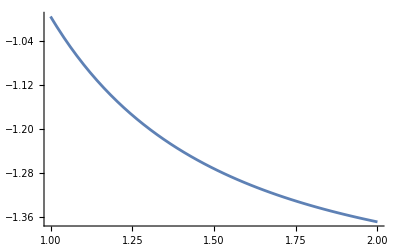

```mathematica
plotσexact=Plot[Evaluate[σ[r]/. sol],{r,Rmin,Rmax},PlotRange->All]
```

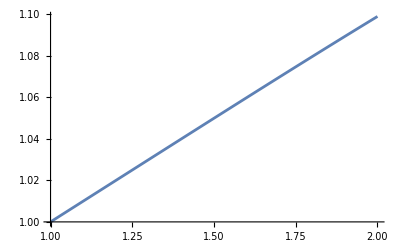

```mathematica
plotzexact=Plot[Evaluate[z[r]/. sol],{r,Rmin,Rmax},PlotRange->All]
```

```mathematica
(*sign*)
```

```mathematica
(*Compare with the solution from FE*)
```

```mathematica
(*check of z*)
```

```mathematica
tabz=Import["~/Desktop/z.csv"];
tabz=Table[{Norm[{tabz[[i,2]],tabz[[i,3]]}],tabz[[i,1]]},{i,1,Length[tabz]}]
```

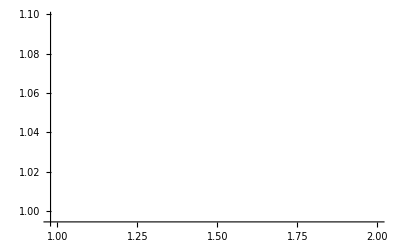

```mathematica
plotzfe=ListPlot[tabz,PlotRange->Full,PlotStyle->{PointSize->.02,Red,Opacity[0.001]}]
```

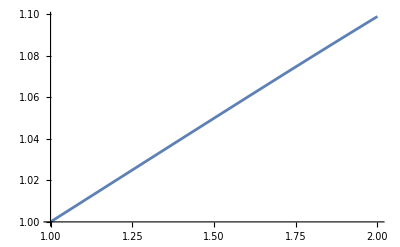

```mathematica
Show[plotzexact,plotzfe]
```

```mathematica
(*check of v*)
```

```mathematica
tabv=Import["~/Desktop/v.csv"];
tabv=Table[{Norm[{tabv[[i,4]],tabv[[i,5]]}],Norm[{tabv[[i,1]],tabv[[i,2]]}]},{i,1,Length[tabv]}]
```

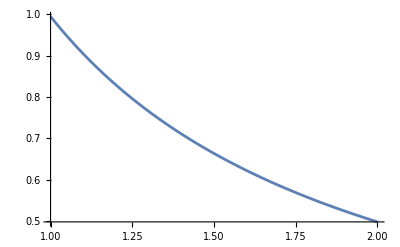

```mathematica
plotvexact=Plot[v[r]/.repv/.sol,{r,Rmin,Rmax}]
```

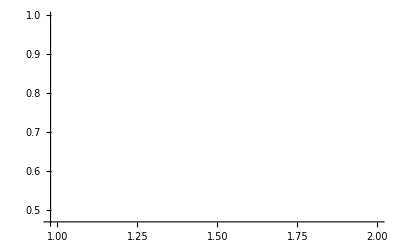

```mathematica
plotvfe=ListPlot[tabv,PlotRange->Full,PlotStyle->{PointSize->.02,Red,Opacity[0.001]}]
```

```mathematica
Show[plotvexact,plotvfe]
```

-Graphics-

```mathematica
(*check of ω*)
```

```mathematica
tabω=Import["~/Desktop/omega.csv"];
tabω=Table[{Norm[{tabω[[i,4]],tabω[[i,5]]}],Norm[{tabω[[i,1]],tabω[[i,2]]}]},{i,1,Length[tabω]}]
```

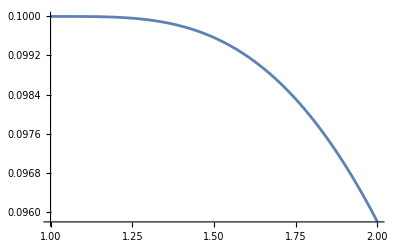

```mathematica
plotωexact=Plot[z'[r]/.sol,{r,Rmin,Rmax}]
```

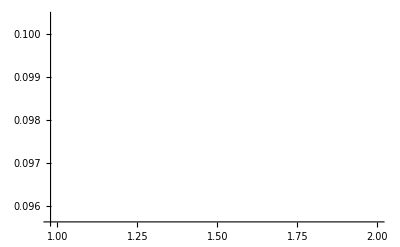

```mathematica
plotωfe=ListPlot[tabω,PlotRange->Full,PlotStyle->{PointSize->.02,Red,Opacity[0.001]}]
```

```mathematica
Show[plotωexact,plotωfe]
```

-Graphics-

```mathematica
(*check sigma*)
```

```mathematica
tabσ=Import["~/Desktop/sigma.csv"];
tabσ=Table[{Norm[{tabσ[[i,2]],tabσ[[i,3]]}],tabσ[[i,1]]},{i,1,Length[tabσ]}]
```

```mathematica
tabσr03={{1,-0.99502},{1.0000039804420782,-0.99502},{1.0000039804420782,-0.99502},{2,-1.2288},{2.0000426020462663,-1.2271},{2.0000426020462663,-1.2286},{0.9999987412492078,-0.99502},{1.00000097999952,-0.99502},{0.999998964499464,-0.99502},{0.9999961362425357,-0.99502},{0.9999962064428045,-0.99502},{1.0000018276483298,-0.99502},{0.9999967656947697,-0.99502},{0.9999993976498187,-0.99502},{0.9999988452493331,-0.99502},{0.9999988452493331,-0.99502},{0.9999993976498187,-0.99502},{0.9999967656947697,-0.99502},{1.0000018276483298,-0.99502},{0.9999962064428045,-0.99502},{0.9999961362425357,-0.99502},{0.999998964499464,-0.99502},{1.00000097999952,-0.99502},{0.9999987412492078,-0.99502},{2.000037243753226,-1.2272},{1.9999563120478407,-1.2268},{1.9999670954543227,-1.2281},{1.9999959524959043,-1.2287},{1.999966324716494,-1.2266},{2.0000416720658603,-1.2281},{2.0000426020462663,-1.2287},{1.9999550375945956,-1.2254},{2.000042652445192,-1.2255},{1.999992412885609,-1.2293},{1.999992412885609,-1.2275},{2.000042652445192,-1.2291},{1.9999550375945956,-1.2275},{2.0000416720658603,-1.2285},{1.999966324716494,-1.2293},{1.9999959524959043,-1.2277},{1.9999670954543227,-1.2291},{1.9999563120478407,-1.2281},{2.000037243753226,-1.2268},{2.,-1.2265},{2.000037243753226,-1.2279},{1.9999563120478407,-1.2285},{1.9999670954543227,-1.2253},{1.9999959524959043,-1.225},{1.999966324716494,-1.2289},{2.0000416720658603,-1.227},{1.9999550375945956,-1.227},{2.000042652445192,-1.2265},{1.999992412885609,-1.2279},{1.999992412885609,-1.2287},{2.000042652445192,-1.2269},{1.9999550375945956,-1.2284},{2.0000426020462663,-1.2263},{2.0000416720658603,-1.2276},{1.999966324716494,-1.2286},{1.9999959524959043,-1.2251},{1.9999670954543227,-1.2253},{1.9999563120478407,-1.2291},{2.000037243753226,-1.2272},{1.2559636898015805,-1.0051},{1.2560134738130797,-1.0049},{1.2559370165736816,-1.0053},{1.2574374241289306,-1.0015},{1.2573866196079073,-1.0017},{1.2658836504197375,-1.0078},{1.2574293946381245,-1.0004},{1.2574296142925854,-1.001},{1.2658427489226298,-1.0098},{1.2658497679029688,-1.0106},{1.7355842269679682,-1.1848},{1.7355325090588192,-1.184},{1.7465731387205061,-1.1855},{1.7465446065016492,-1.1856},{1.7355133868973756,-1.1842},{1.7464938419587972,-1.1854},{1.7355,-1.1845},{1.749719059620715,-1.1889},{1.7496531855199193,-1.1884},{1.7496794342107356,-1.1882},{1.7496793906599004,-1.1885},{1.2623778594382904,-1.0057},{1.4913917357957969,-1.1478},{1.2588538554176971,-1.0034},{1.491403411589232,-1.1445},{1.2243638462891657,-0.98419},{1.4877982986950886,-1.1383},{1.2588369739167977,-1.0036},{1.4914,-1.1446},{1.2588100094930927,-1.0039},{1.4913932066695221,-1.1449},{1.230117641731879,-0.98714},{1.493253842318847,-1.1428},{1.230132801001583,-0.98687},{1.4919428982370604,-1.1422},{1.2535289790028787,-0.99638},{1.4914128368764967,-1.1453},{1.2534792981537433,-0.99615},{1.4913936965469579,-1.1451},{1.248362357141948,-0.99262},{1.2535066063248332,-0.99615},{1.4913534983028,-1.1447},{1.5405295130574421,-1.1477},{1.5415034419682623,-1.1482},{1.5414579396143122,-1.1479},{1.5414804921243734,-1.1479},{1.476377982123819,-1.1405},{1.4780644674708878,-1.1428},{1.5632513257950558,-1.1479},{1.4780571047493396,-1.1429},{1.56330130288438,-1.1484},{1.4780966952131378,-1.1431},{1.5632985267056323,-1.1485},{1.7505644925280528,-1.1865},{1.7549017942893557,-1.1878},{1.7540366137854704,-1.1881},{1.7549450311904358,-1.1871},{1.7549282520946548,-1.1874},{1.755517305525639,-1.1889},{1.750631868783383,-1.1881},{1.732623262014925,-1.183},{1.7468645511315408,-1.1839},{1.7499148836443446,-1.1859},{1.7498688231121784,-1.1863},{1.749898125720466,-1.1861},{1.74172374563247,-1.1851},{1.7416759450598152,-1.1849},{1.7424322942656911,-1.1853},{1.7444840279005138,-1.1838},{1.7426335135363373,-1.1862},{1.7426916778650205,-1.1864},{1.7376513862107097,-1.1846},{1.7426293982370433,-1.1867},{1.7435612237314753,-1.184},{1.754756601953673,-1.1884},{1.7456954490689378,-1.1871},{1.7465247779519188,-1.1868},{1.803274151342496,-1.1989},{1.4791870931021538,-1.1385},{1.803289457103324,-1.1989},{1.476880109182868,-1.1369},{1.803278128326299,-1.1991},{1.476909914111216,-1.1373},{1.510084578558433,-1.1401},{1.510530660926815,-1.1399},{1.5107519918570353,-1.14},{1.5059116375139678,-1.1383},{1.8003169755629145,-1.1979},{1.7998856863978887,-1.1968},{1.8003243806603302,-1.1973},{1.8002849559167016,-1.1976},{1.5423417739269076,-1.1415},{1.5506371883841816,-1.1458},{1.5413688721393075,-1.1425},{1.5355420989344448,-1.1399},{1.5355878913627834,-1.1407},{1.5356073937045236,-1.1412},{1.5355296967496266,-1.1409},{1.3332057305607414,-1.0611},{1.3330564930264581,-1.0605},{1.3331275126183542,-1.0615},{1.3180784324538506,-1.0549}};
```

```mathematica
tabσr01={{1,-0.99502},{1.0000039804420782,-0.99502},{1.0000039804420782,-0.99502},{2,-1.3175},{2.0000426020462663,-1.3176},{2.0000426020462663,-1.3178},{0.9999992437617141,-0.99502},{0.9999983256985984,-0.99502},{0.9999987412492078,-0.99502},{1.0000016276486754,-0.99502},{0.9999967154446059,-0.99502},{1.00000097999952,-0.99502},{0.9999981328482568,-0.99502},{1.0000044772399772,-0.99502},{0.999998964499464,-0.99502},{1.0000054516851395,-0.99502},{0.9999980904981768,-0.99502},{0.9999961362425357,-0.99502},{0.9999957849911169,-0.99502},{1.0000025292968013,-0.99502},{0.9999962064428045,-0.99502},{1.0000008254301593,-0.99502},{1.0000003265999466,-0.99502},{1.0000018276483298,-0.99502},{1.000003582493583,-0.99502},{1.0000049720876392,-0.99502},{0.9999994755998626,-0.99502},{1.0000018522482845,-0.99502},{0.9999967656947697,-0.99502},{0.9999953384391349,-0.99502},{1.0000017488484707,-0.99502},{0.9999993976498187,-0.99502},{0.9999974882468456,-0.99502},{1.0000032719946472,-0.99502},{0.9999988452493331,-0.99502},{1.0000030806532547,-0.99502},{1.0000030806532547,-0.99502},{0.9999988452493331,-0.99502},{1.0000032719946472,-0.99502},{0.9999974882468456,-0.99502},{0.9999993976498187,-0.99502},{1.0000017488484707,-0.99502},{0.9999953384391349,-0.99502},{0.9999967656947697,-0.99502},{1.0000018522482845,-0.99502},{0.9999994755998626,-0.99502},{1.0000049720876392,-0.99502},{1.000003582493583,-0.99502},{1.0000018276483298,-0.99502},{1.0000003265999466,-0.99502},{1.0000008254301593,-0.99502},{0.9999962064428045,-0.99502},{1.0000025292968013,-0.99502},{0.9999957849911169,-0.99502},{0.9999961362425357,-0.99502},{0.9999980904981768,-0.99502},{1.0000054516851395,-0.99502},{0.999998964499464,-0.99502},{1.0000044772399772,-0.99502},{0.9999981328482568,-0.99502},{1.00000097999952,-0.99502},{0.9999967154446059,-0.99502},{1.0000016276486754,-0.99502},{0.9999987412492078,-0.99502},{0.9999983256985984,-0.99502},{0.9999992437617141,-0.99502},{1.9999861861682944,-1.3173},{2.0000386870258287,-1.3173},{2.000037243753226,-1.3177},{1.9999554630291148,-1.3174},{2.0000428395661927,-1.3174},{1.9999563120478407,-1.3176},{2.000013770352594,-1.3174},{2.0000439987410275,-1.3171},{1.9999670954543227,-1.3177},{1.999963084684315,-1.3174},{2.0000309922598696,-1.3176},{1.9999959524959043,-1.3172},{2.000022562372735,-1.3174},{2.000024442350643,-1.3172},{1.999966324716494,-1.3175},{1.9999942849918346,-1.3171},{2.0000469294494065,-1.3175},{2.0000416720658603,-1.3174},{2.0000268648195703,-1.3174},{2.0000445045048374,-1.3177},{2.0000426020462663,-1.317},{1.9999605862116383,-1.3172},{1.9999876011865674,-1.3174},{1.9999550375945956,-1.3175},{2.0000418972861547,-1.3174},{1.9999530650492776,-1.3173},{2.000042652445192,-1.3173},{1.9999853624464357,-1.3176},{2.0000217414068278,-1.3172},{1.999992412885609,-1.3173},{2.000021619713397,-1.3176},{2.000021619713397,-1.3171},{1.999992412885609,-1.3173},{2.0000217414068278,-1.3176},{1.9999853624464357,-1.3174},{2.000042652445192,-1.3175},{1.9999530650492776,-1.3171},{2.0000418972861547,-1.3175},{1.9999550375945956,-1.3169},{1.9999876011865674,-1.3172},{1.9999605862116383,-1.3178},{2.0000445045048374,-1.3169},{2.0000268648195703,-1.3176},{2.0000416720658603,-1.3175},{2.0000469294494065,-1.3172},{1.9999942849918346,-1.3172},{1.999966324716494,-1.3178},{2.000024442350643,-1.3177},{2.000022562372735,-1.3174},{1.9999959524959043,-1.3171},{2.0000309922598696,-1.3176},{1.999963084684315,-1.3178},{1.9999670954543227,-1.3176},{2.0000439987410275,-1.3173},{2.000013770352594,-1.3178},{1.9999563120478407,-1.3175},{2.0000428395661927,-1.3173},{1.9999554630291148,-1.3179},{2.000037243753226,-1.3176},{2.0000386870258287,-1.3178},{1.9999861861682944,-1.317},{2.,-1.3176},{1.9999861861682944,-1.3177},{2.0000386870258287,-1.3176},{2.000037243753226,-1.3177},{1.9999554630291148,-1.3178},{2.0000428395661927,-1.3177},{1.9999563120478407,-1.3172},{2.000013770352594,-1.318},{2.0000439987410275,-1.3177},{1.9999670954543227,-1.3181},{1.999963084684315,-1.3178},{2.0000309922598696,-1.3177},{1.9999959524959043,-1.3178},{2.000022562372735,-1.3177},{2.000024442350643,-1.318},{1.999966324716494,-1.3177},{1.9999942849918346,-1.318},{2.0000469294494065,-1.3179},{2.0000416720658603,-1.3181},{2.0000268648195703,-1.3175},{2.0000445045048374,-1.3179},{1.9999605862116383,-1.3181},{1.9999876011865674,-1.318},{1.9999550375945956,-1.3171},{2.0000418972861547,-1.3181},{1.9999530650492776,-1.3177},{2.000042652445192,-1.3177},{1.9999853624464357,-1.3178},{2.0000217414068278,-1.3175},{1.999992412885609,-1.3178},{2.000021619713397,-1.3177},{2.000021619713397,-1.3179},{1.999992412885609,-1.3175},{2.0000217414068278,-1.3178},{1.9999853624464357,-1.3175},{2.000042652445192,-1.3178},{1.9999530650492776,-1.3174},{2.0000418972861547,-1.3178},{1.9999550375945956,-1.3176},{1.9999876011865674,-1.3175},{1.9999605862116383,-1.3175},{2.0000426020462663,-1.3178},{2.0000445045048374,-1.3175},{2.0000268648195703,-1.3175},{2.0000416720658603,-1.3176},{2.0000469294494065,-1.3177},{1.9999942849918346,-1.3176},{1.999966324716494,-1.317},{2.000024442350643,-1.3179},{2.000022562372735,-1.3175},{1.9999959524959043,-1.3177},{2.0000309922598696,-1.3178},{1.999963084684315,-1.3174},{1.9999670954543227,-1.3177},{2.0000439987410275,-1.3178},{2.000013770352594,-1.3172},{1.9999563120478407,-1.3173},{2.0000428395661927,-1.3177},{1.9999554630291148,-1.3179},{2.000037243753226,-1.3176},{2.0000386870258287,-1.3172},{1.9999861861682944,-1.3176},{1.101750218969799,-1.0197},{1.0878998524680477,-1.0078},{1.1037298050247621,-1.0208},{1.0855590289339405,-1.0051},{1.0848069675292467,-1.0054},{1.082325490275453,-1.0011},{1.0851077158052098,-1.0046},{1.083641775357521,-1.0044},{1.0855224034537474,-1.0053},{1.0858125912421535,-1.0067},{1.084101167881024,-1.0039},{1.0799192609172226,-1.0005},{1.0754174131471,-0.99566},{1.077602305584022,-0.99794},{1.0836428413919412,-1.004},{1.0925696602505488,-1.0126},{1.083625774165602,-1.0044},{1.0841942118458296,-1.0041},{1.9129673218327594,-1.3059},{1.9106769193141995,-1.3056},{1.9146323224055317,-1.3066},{1.9054924455373734,-1.3051},{1.911263306009928,-1.3059},{1.9096838540449568,-1.306},{1.9130368135506435,-1.3062},{1.9122812422862907,-1.3059},{1.9331975610371541,-1.309},{1.9194690620064705,-1.3068},{1.924859535680461,-1.308},{1.93068884339243,-1.3087},{1.8991517185311972,-1.3041},{1.9253416346196848,-1.3075},{1.913059413112933,-1.3064},{1.93113828589151,-1.3088},{1.912437906861292,-1.3058},{1.898937926842265,-1.3041},{1.9176659883566796,-1.3065},{1.933248267967671,-1.3086},{1.9152552962986422,-1.3063},{1.909342590082775,-1.3058},{1.9145099450250973,-1.3062},{1.9130018348135476,-1.3059},{1.917536085423166,-1.3067},{1.913061994839686,-1.3059},{1.9101316515258835,-1.3059},{1.9102128808067438,-1.3056},{1.9111439846332878,-1.3062},{1.9093000465091912,-1.3059},{1.9210082378792654,-1.3071},{1.9218693035687937,-1.3074},{1.9177971313202031,-1.3069},{1.907101896202717,-1.3054},{1.9125317959186978,-1.3062},{1.0759584491047969,-0.995},{1.0822075588813822,-1.0025},{1.0836578929256226,-1.0046},{1.0851204064065885,-1.0059},{1.0875207681552568,-1.0079},{1.084798751151567,-1.0049},{1.0856686843139576,-1.0053},{1.912978077954894,-1.3058},{1.9143028058538702,-1.3061},{1.9112753700082046,-1.3057},{1.9129673218327594,-1.3063},{1.9125395339443312,-1.3062},{1.908547746324414,-1.3051},{1.9183687446369637,-1.3069},{1.9069975569203017,-1.3051},{1.9173648804804995,-1.3066},{1.91299928648706,-1.3062},{1.9123961007333183,-1.3059},{1.9216053043224042,-1.3076},{1.9202744905091043,-1.3071},{1.9145200165054423,-1.3063},{1.909774774678941,-1.3059},{1.9252812911364408,-1.3077},{1.9267724664837829,-1.308},{1.0834446719606867,-1.0021},{1.1685783919361166,-1.0815},{1.1709373570349526,-1.0828},{1.2568803370647503,-1.1257},{1.2491684405635615,-1.1215},{1.2613411643960568,-1.1277},{1.344823757821076,-1.1669},{1.3523215795438597,-1.17},{1.4338673682039076,-1.1998},{1.4442717334352286,-1.2033},{1.4304127026840892,-1.1986},{1.5176222969171218,-1.2259},{1.5175833774788126,-1.2259},{1.3669891683550384,-1.1758},{1.4613631262968145,-1.2089},{1.392116350597176,-1.1853},{1.485615239185436,-1.2165},{1.4210608976746915,-1.1953},{1.5155643577228914,-1.2253},{1.4524447122352024,-1.2061},{1.5507935027269104,-1.235},{1.4923154709712019,-1.2185},{1.5371722772675809,-1.2314},{1.5819052983348907,-1.2431},{1.591713433033723,-1.2456},{1.5381452832876354,-1.2316},{1.4384641734850405,-1.2014},{1.4893341735151315,-1.2177},{1.3897356439265705,-1.1841},{1.4458737859509039,-1.2039},{1.5450729634874851,-1.2335},{1.506433164000315,-1.2227},{1.408044088656318,-1.1908},{1.4735383567793543,-1.2128},{1.3764103667148109,-1.1791},{1.4468791811689046,-1.2043},{1.5427949474897822,-1.233},{1.5205288170909488,-1.2268},{1.4266046058530022,-1.1974},{1.504655195340115,-1.2222},{1.4159083579416432,-1.1936},{1.495678719678795,-1.2196},{1.4102196494163592,-1.1916},{1.4930282789016422,-1.2189},{1.408127731457626,-1.191},{1.4964243950163336,-1.2199},{1.4170041703890641,-1.1942},{1.507006538008379,-1.223},{1.4317346758739904,-1.1994},{1.5239575806432408,-1.2279},{1.450929917535647,-1.2059},{1.5467761823870962,-1.2342},{1.4782601381691924,-1.2144},{1.5757766854792592,-1.2419},{1.511881507559372,-1.2245},{1.5798383366661288,-1.2428},{1.5851418093107634,-1.2441},{1.4133713807771826,-1.1931},{1.4520247023036488,-1.2063},{1.5512833492305653,-1.2355},{1.496334457399147,-1.2199},{1.4013231256209255,-1.1885},{1.4474801864274343,-1.2045},{1.546032262955725,-1.2341},{1.5008506454674297,-1.2214},{1.4013279075220046,-1.189},{1.4609415676542303,-1.209},{1.5596532467186415,-1.2378},{1.5246311156801176,-1.2282},{1.4269369693157437,-1.1977},{1.4954774287831962,-1.2198},{1.3993832793412961,-1.1881},{1.4725169446902808,-1.2127},{1.5673738057336546,-1.2397},{1.548693838723458,-1.2348},{1.4561233806240461,-1.2075},{1.5363593395101292,-1.2314},{1.4463464459112139,-1.2042},{1.5303467936712907,-1.2298},{1.44186465484802,-1.2027},{1.5305585687911458,-1.2298},{1.4465149817751628,-1.2043},{1.5376434483000279,-1.2317},{1.4581057631049952,-1.208},{1.5510776334213578,-1.2354},{1.4790006998308012,-1.2149},{1.5712951239025723,-1.2407},{1.5034477116281766,-1.2219},{1.597061014019189,-1.247},{1.5303404628003536,-1.2298},{1.4223468549692793,-1.1961},{1.4649490233537141,-1.2103},{1.5652268489596006,-1.239},{1.5068542168703647,-1.223},{1.6185276094339573,-1.2523},{1.4092823231702014,-1.1912},{1.45409435419439,-1.2068},{1.553111569752798,-1.2358},{1.5044155524322393,-1.2222},{1.4046987049186028,-1.1896},{1.46071292953133,-1.2088},{1.559947913521474,-1.2376},{1.5212105812148429,-1.227},{1.4227692890978496,-1.1962},{1.488158545619384,-1.2174},{1.390953889422651,-1.1847},{1.4611734752930605,-1.209},{1.5571870351695074,-1.2369},{1.534749752272337,-1.2308},{1.440687297820037,-1.2022},{1.5184530534725134,-1.2262},{1.427232327128278,-1.1976},{1.5086341945282826,-1.2234},{1.4206001161481017,-1.1953},{1.5054572389809018,-1.2225},{1.420653754051282,-1.1953},{1.5087131602793156,-1.2234},{1.42697582320094,-1.1976},{1.5184514875359043,-1.2262},{1.4407099822309832,-1.2021},{1.534746621563312,-1.2308},{1.4612269455495268,-1.2089},{1.5572200390439366,-1.2369},{1.4881571556794664,-1.2174},{1.585646087908648,-1.2441},{1.5212401153006714,-1.2269},{1.425278508958863,-1.1967},{1.461141759173284,-1.209},{1.5600373617320833,-1.2375},{1.5043833954148789,-1.222},{1.4085014271913254,-1.1908},{1.453882014642179,-1.2064},{1.5531879501206545,-1.2357},{1.5072009495750724,-1.223},{1.404632999897126,-1.19},{1.4660052476372651,-1.2104},{1.5653081741625192,-1.239},{1.5294726857319156,-1.2292},{1.4315352807737574,-1.1991},{1.4995191983099116,-1.2207},{1.4030306518390823,-1.189},{1.4756095172924308,-1.2134},{1.570712544325027,-1.2403},{1.551110181500979,-1.2351},{1.458140546681286,-1.2078},{1.537836363649917,-1.2315},{1.4461341337856595,-1.2039},{1.5306516339128244,-1.2295},{1.4418555379787534,-1.2024},{1.5300470711713414,-1.2294},{1.4448658125929892,-1.2034},{1.5360290603045246,-1.231},{1.454623528752371,-1.2067},{1.5484219400408923,-1.2344},{1.4722771220459823,-1.2123},{1.5674610713188382,-1.2393},{1.4955010185218864,-1.2193},{1.592148451652672,-1.2455},{1.5246180604007027,-1.2278},{1.4269827500358931,-1.1974},{1.4608769511495483,-1.2086},{1.5596682218023166,-1.2373},{1.5006422492053195,-1.2208},{1.5986460435318384,-1.2474},{1.59235795598854,-1.2458},{1.357689560098331,-1.1724},{1.6000840227938031,-1.2475},{1.5459052752351936,-1.2336},{1.4461840188579045,-1.2038},{1.4963430990585014,-1.2195},{1.3967197830631597,-1.1865},{1.4520135157773155,-1.2057},{1.5512965931761729,-1.235},{1.5118811593508268,-1.224},{1.4133289547730916,-1.1926},{1.4781417388396825,-1.214},{1.3807734222529056,-1.1806},{1.4504763937755072,-1.2052},{1.5466780764270245,-1.2338},{1.5235208034024348,-1.2274},{1.4292451023180033,-1.1981},{1.5066246020824168,-1.2226},{1.4161408122075996,-1.1935},{1.496419256926347,-1.2196},{1.4083509548759496,-1.1907},{1.4926138684870913,-1.2185},{1.4075981269169124,-1.1906},{1.4954473986402863,-1.2193},{1.4152181457287778,-1.1933},{1.5050407893475843,-1.2221},{1.428934190367072,-1.198},{1.5209884123161492,-1.2267},{1.4473722823102562,-1.2043},{1.5430008663639825,-1.2328},{1.4736766341704681,-1.2126},{1.5711497402249728,-1.2403},{1.5065316028930855,-1.2225},{1.5865224311052146,-1.2441},{1.579276057217357,-1.2423},{1.597110402696069,-1.2468},{1.408115668805656,-1.1907},{1.4459086487728054,-1.2037},{1.545034992961648,-1.2333},{1.4894283165362472,-1.2175},{1.5889661576005953,-1.2447},{1.5381895707616795,-1.2314},{1.438485089425678,-1.2013},{1.4922506419499375,-1.2183},{1.3928276857170812,-1.1851},{1.4517175236250335,-1.2056},{1.550567912088987,-1.2348},{1.5148839102716751,-1.225},{1.417050730390412,-1.1937},{1.4850497097403843,-1.2162},{1.5818203712495296,-1.2429},{1.6294614815944561,-1.2547},{1.3752103551457138,-1.1794},{1.6196560923850474,-1.2522},{1.5564694812620004,-1.2365},{1.6263128240286369,-1.2538},{1.604982900968107,-1.2489},{1.362318353983385,-1.1736},{1.3388546678411366,-1.1645},{1.3302730600895443,-1.1609},{1.6276319923127587,-1.2542},{1.603163046480301,-1.2483},{1.6062255568879484,-1.249},{1.6225854492136922,-1.2533},{1.6106299016223435,-1.25},{1.3479138536642465,-1.1683},{1.6198049705134259,-1.2525},{1.340379815574675,-1.1649},{1.6184534989921704,-1.2519},{1.3418215252409689,-1.1659},{1.6377970487517677,-1.2563},{1.6151442636495357,-1.2513},{1.6443344058919402,-1.2579},{1.616012369507115,-1.2517},{1.629234866432707,-1.2548},{1.3310475010306733,-1.1609},{1.6455566821291816,-1.258},{1.3765752299093572,-1.1793},{1.6449666414137398,-1.2581},{1.3383111798763732,-1.1643},{1.629395008246926,-1.2546},{1.6421798645702608,-1.2578},{1.3557678267314062,-1.1717},{1.6391904250574427,-1.2566},{1.6494711826824984,-1.2591},{1.6592406311623398,-1.2613},{1.3618417651709762,-1.1738},{1.3628225770069997,-1.1743},{1.668788860945566,-1.2631},{1.6520662365655925,-1.2596},{1.3387826162600112,-1.1643},{1.6628299371853996,-1.2619},{1.3296163718907799,-1.161},{1.3411329343506557,-1.1657},{1.6584914892757214,-1.2613},{1.3340669316417373,-1.1627},{1.6789359956829804,-1.2653},{1.303748070794354,-1.1492},{1.3440319312055051,-1.1668},{1.6890629929342482,-1.2675},{1.6643421096937974,-1.2623},{1.4614010903581536,-1.2088},{1.2934501497931803,-1.1447},{1.6886129408778079,-1.2673},{1.6911637045537606,-1.268},{1.6664464025284462,-1.2631},{1.7258789524181581,-1.275},{1.3245220061969527,-1.1585},{1.7206986168414269,-1.2743},{1.6936035316744,-1.2688},{1.69948032118645,-1.2697},{1.70366775578456,-1.2707},{1.3149665749364126,-1.1539},{1.309849952513646,-1.1521},{1.7185315024462018,-1.2737},{1.690240030291556,-1.2678},{1.6960980279453188,-1.2689},{1.6902431186074978,-1.2677},{1.285358339763663,-1.1404},{1.331122769732379,-1.1612},{1.2641772757014738,-1.1295},{1.3387774060313387,-1.1645},{1.3465410884559,-1.1672},{1.2901481654833293,-1.1433},{1.2970737496765556,-1.1461},{1.2796783784998478,-1.1383},{1.2941314990757316,-1.1451},{1.2846971627586012,-1.1405},{1.307468892325932,-1.1509},{1.34675505078095,-1.1674},{1.3144865071958707,-1.1543},{1.177838857993741,-1.0875},{1.650701002604651,-1.2591},{1.666450953853728,-1.2628},{1.739382786853141,-1.2776},{1.7217000173182437,-1.2741},{1.662800416887126,-1.2623},{1.7363602431811205,-1.2773},{1.7195158976002518,-1.274},{1.643329379643655,-1.2576},{1.7139353864425577,-1.2724},{1.693066920000506,-1.2683},{1.6536350602233856,-1.2601},{1.7246909237599648,-1.2749},{1.7044710763166384,-1.2709},{1.639160482198128,-1.2569},{1.7104369624455618,-1.272},{1.690376890666694,-1.268},{1.7400563927643264,-1.2775},{1.4338493226626012,-1.1997},{1.7094271116371123,-1.2716},{1.2325962495886478,-1.1136},{1.2638494771925968,-1.1293},{1.7354972205105947,-1.2767},{1.7103437468824798,-1.2719},{1.23694781927129,-1.1143},{1.2691868213939193,-1.1321},{1.743916035822826,-1.2783},{1.7354343411376878,-1.2768},{1.736033950820087,-1.2767},{1.6909312312746485,-1.2678},{1.7888276699838916,-1.2865},{1.748224305288083,-1.279},{1.2390843241684564,-1.1157},{1.741903932511779,-1.2781},{1.1932627462549898,-1.0926},{1.2544190108970767,-1.1249},{1.8047689692589466,-1.2894},{1.2118544582993456,-1.1046},{1.748308074939883,-1.2793},{1.8200354797640623,-1.2919},{1.2331350584992709,-1.1125},{1.7460432136977595,-1.2788},{1.7107790272562966,-1.2721},{1.6883006771307059,-1.2674},{1.74841148474837,-1.2791},{1.537142016503355,-1.2313},{1.7452939305744464,-1.2785},{1.7246795664412562,-1.2746},{1.7734005194540798,-1.2836},{1.7558064608891264,-1.2807},{1.703153153888399,-1.2707},{1.2498379435686853,-1.1208},{1.2024756059479962,-1.1012},{1.2822885790647907,-1.1386},{1.2499372278638634,-1.122},{1.1693073088371593,-1.0826},{1.7632659553932866,-1.2818},{1.703116872767104,-1.2704},{1.7606949257608484,-1.2816},{1.7393428070394865,-1.2778},{1.754950489330112,-1.2807},{1.7549545652523315,-1.2803},{1.7354295309519197,-1.2767},{1.7875629037603122,-1.2863},{1.7206872731847584,-1.2738},{1.7810718402130776,-1.2851},{1.754683726487483,-1.2807},{1.6989850646783213,-1.27},{1.8216299130174605,-1.2925},{1.8277374346442654,-1.2934},{1.75843430212789,-1.281},{1.2390083759200339,-1.1155},{1.1948136792404078,-1.0943},{1.216773697842372,-1.1068},{1.7597548539782464,-1.2813},{1.7054445568238215,-1.271},{1.8195643087288782,-1.2917},{1.7801453995671255,-1.2847},{1.207309136302712,-1.0975},{1.7741226705050586,-1.2839},{1.7809290187988964,-1.2849},{1.818673151751023,-1.2917},{1.7544491413546304,-1.2804},{1.1400387637707765,-1.064},{1.2310955862564044,-1.1111},{1.19787943466778,-1.0963},{1.2687016867648595,-1.133},{1.8133141371532953,-1.2911},{1.7457458520643832,-1.2791},{1.7800118977411359,-1.285},{1.1360706779509804,-1.0531},{1.8538410719638294,-1.297},{1.8389849788402297,-1.2949},{1.7841547814301313,-1.2856},{1.7651611798643205,-1.282},{1.2232213884657184,-1.1069},{1.187245507761558,-1.0897},{1.0968243750482571,-1.0161},{1.1705493506896667,-1.0833},{1.8161796221739743,-1.2913},{1.8029889428668164,-1.2892},{1.769711010306485,-1.283},{1.8177789506978013,-1.2912},{1.217698981727422,-1.1038},{1.185826462851964,-1.0893},{1.8155478949617387,-1.2913},{1.7524273251692923,-1.2802},{1.2023744285371343,-1.0981},{1.2751088864877382,-1.1356},{1.7940987040851457,-1.2877},{1.7264043500420172,-1.2752},{1.8241608699903638,-1.2927},{1.75972945347971,-1.2815},{1.8159769508451922,-1.291},{1.8140783004049192,-1.2908},{1.8027460164981641,-1.2892},{1.7035892093166123,-1.2706},{1.7560408268602412,-1.2806},{1.1399084226814014,-1.0653},{1.0841467515516523,-1.0046},{1.1702934033822459,-1.082},{1.1751430538023868,-1.085},{1.084085267679623,-1.0051},{1.1693767239859019,-1.0816},{1.1789130532825567,-1.0884},{1.0841096928355543,-1.0047},{1.173016310372537,-1.0843},{1.1801609051735276,-1.0893},{1.2648982164980704,-1.1298},{1.1766209772479836,-1.0865},{1.08333109550174,-1.005},{1.1700994585145315,-1.0823},{1.1757483251529641,-1.0865},{1.2561584437327167,-1.1249},{1.2563686326297707,-1.1254},{1.272908633052663,-1.1345},{1.0840474080500355,-1.0041},{1.170081773638065,-1.0823},{1.175335044061905,-1.0855},{1.1699810789068341,-1.0828},{1.2550199960159998,-1.1248},{1.0829234802207588,-1.0036},{1.1679392767365946,-1.0809},{1.1671487634830446,-1.0809},{1.2490411242228976,-1.1214},{1.0846887886393959,-1.0052},{1.1707165711648573,-1.0826},{1.169004945284664,-1.082},{1.247621399343567,-1.1204},{1.0815863638655954,-1.0031},{1.165091983493149,-1.0787},{1.1782750452797515,-1.087},{1.2550008492427407,-1.1249},{1.0887136398520962,-1.0071},{1.1702238161992773,-1.0829},{1.172469685791492,-1.0839},{1.0942516160486127,-1.0134},{1.0888128566930133,-1.0074},{1.1701519329129872,-1.0825},{1.1725071136671197,-1.0841},{1.171748900106162,-1.0837},{1.261687829853328,-1.1282},{1.0887300317801472,-1.0079},{1.1720715048579586,-1.0841},{1.1678804419973818,-1.0812},{1.183323677275157,-1.0916},{1.2579261679844331,-1.1257},{1.0852211515170536,-1.0056},{1.1714224314481945,-1.0829},{1.1738298290638214,-1.0846},{1.179654535912951,-1.0881},{1.1781138181432218,-1.0875},{1.2617332810463548,-1.128},{1.2793599229692947,-1.1369},{1.0883085591871453,-1.0078},{1.178325819499853,-1.0875},{1.091466608788377,-1.0123},{1.865371804761721,-1.299},{1.0847463589706121,-1.0054},{1.1013638964937975,-1.0193},{1.1006398697575879,-1.0189},{1.071722036770729,-0.99284},{1.2586185800312977,-1.1268},{1.2655689931445855,-1.1301},{1.8204162436102354,-1.2918},{1.088528617033103,-1.0098},{1.8206962958165207,-1.2919},{1.78440526517941,-1.2856},{1.0951342835013431,-1.0136},{1.0950089662189986,-1.0137},{1.8228681514580256,-1.2925},{1.8259865122448196,-1.2927},{1.0930771973653095,-1.0131},{1.089608545350118,-1.0085},{1.1864160457444934,-1.0932},{1.262028051827692,-1.1277},{1.0924127231957708,-1.0119},{1.8569246545027074,-1.2979},{1.256216526280402,-1.1252},{1.0930578698769795,-1.0128},{1.2586680670057535,-1.1264},{1.8124864232319093,-1.2904},{1.900234522999727,-1.3043},{1.7931734564453041,-1.2873},{1.0972184258842903,-1.0165},{1.3447460246827279,-1.167},{1.1804181898378219,-1.0886},{1.240562102798566,-1.1163},{1.2902343601454738,-1.1426},{1.2817642785239414,-1.1389},{1.8457330928387234,-1.2957},{1.8994590530990658,-1.304},{1.0896495819120018,-1.0094},{1.094188708404542,-1.0134},{1.2644614614925993,-1.1294},{1.1908983568718197,-1.0921},{1.2780227769488306,-1.1367},{1.8633260999889416,-1.2985},{1.7696512952839043,-1.2832},{1.1826474925352863,-1.0905},{1.0854593483406,-1.0055},{1.3504755733074183,-1.1692},{1.3608168643869754,-1.1734},{1.1773128471226328,-1.0869},{1.190599705862554,-1.0912},{1.2060174826261847,-1.1004},{1.2507236137932314,-1.1229},{1.2883520078379198,-1.1421},{1.2556045218937368,-1.1259},{1.2722925806983234,-1.1338},{1.2609995270562158,-1.1283},{1.4013342780721518,-1.1882},{1.290516199084692,-1.1434},{1.3487887962538836,-1.1687},{1.3804606855684085,-1.1802},{1.3531144118661953,-1.1698},{1.3566380488545942,-1.1714},{1.3785160302296087,-1.1803},{1.3185004596510386,-1.1557},{1.2812855569310067,-1.1386},{1.3427083990576658,-1.1665},{1.390979863297812,-1.1852},{1.3808761601132085,-1.181},{1.1683671822248347,-1.0841},{1.3471672723162478,-1.1677},{1.400781984071754,-1.1881},{1.3636042241061004,-1.1748},{1.2699743676153468,-1.1326},{1.2666686586870302,-1.131},{1.3558705413497263,-1.1718},{1.3627071337965468,-1.1739},{1.3901496018774384,-1.1843},{1.3640547145917572,-1.1746},{1.3587950664099426,-1.1731},{1.3898079287800886,-1.1839},{1.3020766680960074,-1.1485},{1.351787890166205,-1.1702},{1.352988411775947,-1.1699},{1.3194997641530672,-1.1561},{1.3856869632063367,-1.1828},{1.3646683949223708,-1.1747},{1.3647040150893528,-1.1749},{1.366050458841107,-1.1754},{1.3529718947930887,-1.1702},{1.3777905466361715,-1.1803},{1.2734753052179693,-1.1343},{1.6105339995169303,-1.2504},{1.6737179094459138,-1.2646},{1.709389809873687,-1.2721},{1.7715825906798701,-1.2837},{1.740044457363087,-1.278},{1.8248409891275459,-1.293},{1.7500282980854909,-1.2799},{1.8554218497150452,-1.2976},{1.6198142515733094,-1.2524},{1.6834823025205818,-1.2664},{1.606524690628812,-1.2493},{1.630687855354298,-1.2548},{1.5960546388203631,-1.2469},{1.6039676078088358,-1.2486},{1.6129479517021001,-1.2505},{1.6274167301585662,-1.2544},{1.7083336837105332,-1.2718},{1.8020579423536858,-1.2891},{1.7848246332903408,-1.2862},{1.6225941729218676,-1.2529},{1.6279267891772653,-1.2544},{1.8159292056685468,-1.2915},{1.9088087410738668,-1.3058},{1.5960496514833111,-1.2465},{1.5889508524809697,-1.2449},{1.6062265375718332,-1.2491},{1.6961277605180571,-1.269},{1.7737255058210106,-1.2838},{1.7870710814066686,-1.286},{1.7078182397433281,-1.2714},{1.8008644646391354,-1.2889},{1.7251311051627352,-1.2748},{1.8200991456511373,-1.2917},{1.6308130395603293,-1.2549},{1.6049081695201879,-1.2486},{1.59631346808827,-1.2467},{1.5920897312965747,-1.246},{1.6000850758631553,-1.2479},{1.5916172643258177,-1.2454},{1.5757899511038898,-1.2414},{1.5856717062494368,-1.2442},{1.6065088266486431,-1.2492},{1.5710848347877335,-1.2404},{1.6039605494213376,-1.2487},{1.6293122575184906,-1.2545},{1.5994591173581147,-1.2473},{1.611055968642927,-1.2504},{1.5971043491330927,-1.247},{1.8154013964134765,-1.2912},{1.7818780728209214,-1.2854},{1.7843438627756143,-1.2858},{1.765774108320767,-1.2825},{1.6151936404344838,-1.2512},{1.6971507855520676,-1.2692},{1.5924817487180192,-1.2458},{1.6779481070641014,-1.2654},{1.6809299836697542,-1.266},{1.7632932030720245,-1.282},{1.7620810679421082,-1.2818},{1.7683022055067399,-1.2829},{1.6893790723221358,-1.2677},{1.7784085048154712,-1.2847},{1.8466838522064353,-1.2962},{1.57949739157746,-1.2426},{1.6650417110691251,-1.2627},{1.6685350289700243,-1.2634},{1.7520557354148298,-1.2801},{1.7518676462564173,-1.28},{1.755314516233487,-1.2807},{1.6773609115512378,-1.2653},{1.7662635003022624,-1.2827},{1.835444343503774,-1.2945},{1.8148603485932466,-1.2909},{1.801938425758494,-1.2887},{1.8724928614283152,-1.2998},{1.5798764621324035,-1.2425},{1.6650824542946814,-1.2624},{1.6676175225752456,-1.2629},{1.7496916756960352,-1.2793},{1.7503415676947172,-1.2795},{1.7565216869996227,-1.2806},{1.6195729710019244,-1.2525},{1.7025719509318835,-1.2706},{1.6176182250766094,-1.2518},{1.7697006865569103,-1.2831},{1.8550639881146957,-1.2974},{1.810810746599434,-1.2902},{1.585084026163913,-1.2438},{1.598614825403543,-1.2473},{1.6415555622944962,-1.2572},{1.6449904494859537,-1.2583},{1.5864467749029592,-1.2445},{1.6153180801315883,-1.2512},{1.6432350459992022,-1.258},{1.6536449250368108,-1.2601},{1.724724975177202,-1.2748},{1.6130218450163658,-1.2508},{1.5241738909980054,-1.2277},{1.3426400186200322,-1.1661},{1.677056502596141,-1.2649},{1.650679814985329,-1.2595},{1.6898061136118545,-1.2678},{1.6757356613845755,-1.2649},{1.6186629358825757,-1.2524},{1.6777777940180278,-1.2652},{1.6904127448939803,-1.2677},{1.663779080316855,-1.2624},{1.658484550455626,-1.2609},{1.6442200876406419,-1.2577},{1.6494341696775898,-1.259},{1.6109521190898257,-1.2503},{1.6455319535031823,-1.2584},{1.6378242258862823,-1.2565},{1.652714507378694,-1.2599},{1.6530458578333513,-1.2599},{1.692768506795894,-1.2684},{1.5993627740134504,-1.2477},{1.6737381665003639,-1.2641},{1.6830898388380817,-1.2664},{1.6686847769725714,-1.2633},{1.688469155773951,-1.2678},{1.695193207277566,-1.2687},{1.7087368258745992,-1.2716},{1.6155640067790566,-1.2513},{1.709553637766303,-1.272},{1.7951378533416311,-1.2879},{1.8101998615898742,-1.2905},{1.9084478459994654,-1.3057},{1.8322119148450051,-1.294},{1.8649023526447706,-1.2992},{1.6957211327337995,-1.2693},{1.7488942335372946,-1.2794},{1.7757790787144665,-1.2842},{1.8175701692094313,-1.2915},{1.7019326804841606,-1.2705},{1.7329339447595802,-1.2764},{1.6680379093114162,-1.263},{1.6923513193483204,-1.2685},{1.7863021997691209,-1.2864},{1.7853264827756294,-1.2861},{1.8943018779751026,-1.3035},{1.7718228579629511,-1.2833},{1.7758460096528639,-1.2843},{1.6804514642202553,-1.2659},{1.6676182819818206,-1.2632},{1.7654150102454664,-1.2824},{1.7880221614957685,-1.2868},{1.710634654273086,-1.2718},{1.7436556777357162,-1.2782},{1.7574029277317138,-1.2807},{1.7260872595555532,-1.2753},{1.675980578318257,-1.2647},{1.705264629346425,-1.2711},{1.5565234184232501,-1.2366},{1.6588003545032173,-1.2611},{1.7044773773799404,-1.2708},{1.8099588173215435,-1.2901},{1.8653946124345915,-1.2987},{1.7136006705472542,-1.2728},{1.8117889998562196,-1.2904},{1.7185123341134332,-1.2737},{1.7967895870134598,-1.288},{1.90411831565163,-1.305},{1.7693383549790582,-1.2832},{1.8523861261626853,-1.2971},{1.7562065968729306,-1.2808},{1.8429841933692759,-1.2957},{1.7569009797083044,-1.2807},{1.8408629632865126,-1.295},{1.7674260183668224,-1.2826},{1.8517620885254131,-1.2968},{1.651886451908847,-1.2597},{1.7467876030015783,-1.279},{1.8119318750990612,-1.2909},{1.8244191836307797,-1.2927},{1.8164116671063306,-1.2915},{1.8094767570764758,-1.2903},{1.899028052873364,-1.3044},{1.8461664740754016,-1.2961},{1.1714176822978217,-1.0843},{1.3508048152490426,-1.1695},{1.4435769579762625,-1.2032},{1.524016818936064,-1.2277},{1.6153909168062075,-1.2512},{1.706660848001149,-1.2711},{1.8007691946776523,-1.2887},{1.0868384684027335,-1.0078},{1.8842742137226207,-1.3023},{1.8330508210357945,-1.2944},{1.8221060678237146,-1.2921},{1.8350394273693416,-1.2942},{1.9131962115290213,-1.3059},{1.0837966484539432,-1.0021},{1.8935963270982545,-1.3032},{1.8352862151719007,-1.2941},{1.178769561407148,-1.0881},{1.3277702745957225,-1.1599},{1.2893152936981704,-1.1416},{1.2561258709221779,-1.1256},{1.3556966659249405,-1.1712},{1.2757175129706422,-1.136},{1.914539425031514,-1.3062},{1.8348618855107324,-1.2944},{1.8291844145410816,-1.2934},{1.906277627839135,-1.3052},{1.8323627459921796,-1.2937},{1.3554726579315424,-1.1716},{1.856493873542275,-1.2977},{1.176281588831518,-1.0869},{1.78033497412706,-1.2851},{1.2683547914522972,-1.1319},{1.9177848810541813,-1.3066},{1.9178225204642894,-1.3066},{1.9186131117033471,-1.3066},{1.912348851543567,-1.3059},{1.9178,-1.3067},{1.8971415038420305,-1.3037},{1.9115338670554596,-1.3061},{1.916930423880846,-1.3066},{1.9104396614392194,-1.3056},{1.9177984951761744,-1.3067},{1.9190483292507254,-1.3069},{1.917769709845267,-1.3072},{1.9184521127461067,-1.3068},{1.9126735231345682,-1.3063},{1.9147630968085843,-1.3061},{1.918270184306684,-1.3068},{1.9012011768616175,-1.3045},{1.9103228889378883,-1.3061},{1.9172130874005633,-1.3065},{1.917783525974712,-1.307},{1.917801928875868,-1.307},{1.924433449096123,-1.3075},{1.9075263118499832,-1.3053},{1.9120536968401276,-1.306},{1.897648465865056,-1.3042},{1.9125399342235967,-1.3063},{1.9093403160254068,-1.306},{1.8398488351220599,-1.2947},{1.3391345925260836,-1.1647},{1.2528436094341544,-1.1233},{1.9181473479375875,-1.3069},{1.7175303229055376,-1.2732},{1.9098848768708547,-1.3056},{1.1701903618215288,-1.0823},{1.9147113413608956,-1.3065},{1.16526082234837,-1.0797},{1.098991149418411,-1.015},{1.3112299998474715,-1.1525},{1.3361104763080036,-1.1634},{1.257428752971714,-1.1265},{1.2461050133917284,-1.1211},{1.2589809879819471,-1.1266},{1.3497636497179795,-1.1695},{1.8360809117247527,-1.2946},{1.2649561385281307,-1.13},{1.8349646344275956,-1.2941},{1.8423955529690141,-1.2953},{1.7965691565035844,-1.288},{1.1563883645644313,-1.073},{1.9176053552282335,-1.3069},{1.8328278335948522,-1.2938},{1.3607584876090248,-1.1736},{1.2513981789981956,-1.1229},{1.3267969325032374,-1.1592},{1.9193740662257575,-1.3071},{1.9218500297629886,-1.3073},{1.9213206733910921,-1.3076},{1.9170969432973388,-1.3065},{1.8367847397014163,-1.2942},{1.6934816525725929,-1.2683},{1.1658597133313253,-1.0818},{1.159071355051103,-1.076},{1.3129251362191219,-1.1542},{1.929644455359588,-1.3087},{1.7022434573526783,-1.2702},{1.2535599778630457,-1.1236},{1.8445245512055404,-1.2959},{1.8281539498630854,-1.293},{1.8337230788753247,-1.2941},{1.8366936189794965,-1.2947},{1.9217967010066388,-1.3074},{1.8372561477377072,-1.2944},{1.3408768064218277,-1.165},{1.8368343959377504,-1.2946},{1.926382155752072,-1.3081},{1.8192816683790338,-1.2918},{1.9209806089599135,-1.3071},{1.834849358939311,-1.2943},{1.9168660219483258,-1.3068},{1.8655311576063263,-1.299},{1.839223447545186,-1.295},{1.8394137245329014,-1.2946},{1.2489321816656018,-1.1222},{1.1703745445151308,-1.0829},{1.303521974536678,-1.1494},{1.3409156479435984,-1.1653},{1.8420569643743376,-1.2954},{1.3301852143216748,-1.1607},{1.92166947470162,-1.3074},{1.2868381010834269,-1.1411},{1.8685243450648428,-1.2994},{1.9266988792297046,-1.3081},{1.9236564725542862,-1.3074},{1.8370503098445614,-1.2947},{1.191466974867537,-1.0921},{1.252375696411025,-1.1234},{1.2461262159588813,-1.1199},{1.0794704617542807,-0.99589},{1.3399419739675296,-1.1647},{1.9244930994939942,-1.3077},{1.8411009507628853,-1.2951},{1.2343633996518206,-1.1128},{1.9279901892903917,-1.3083},{1.3330102662770456,-1.1621},{1.929952476098829,-1.3087},{1.8384829670138367,-1.2947},{1.2022299601157842,-1.0986},{1.9277759439571809,-1.3081},{1.9309849850529652,-1.3082},{1.841928211521828,-1.2951},{1.8412225252804182,-1.2954},{1.8415682747050133,-1.2952},{1.8383349967021787,-1.2947},{1.832568556316516,-1.2938},{1.9344872608781893,-1.309},{1.0783452595991694,-0.99573},{1.847385783316522,-1.2961},{1.8483539674250706,-1.2961},{1.8398793574579828,-1.2953},{1.1631202108552667,-1.0789},{1.237153794036942,-1.116},{1.423265590675191,-1.1959},{1.850623101865858,-1.2968},{1.3398034604000695,-1.1645},{1.850706443496645,-1.2968},{1.1591000371408846,-1.0767},{1.924298643896004,-1.3075},{1.923236298534322,-1.3075},{1.3249563389032863,-1.1584},{1.8467436665655577,-1.2963},{1.8465074066734743,-1.2959},{1.1515668124776781,-1.0709},{1.2536708654587139,-1.1251},{1.2004366882514046,-1.0975},{1.2536975290715062,-1.1245},{1.0603083581675663,-0.97909},{1.9380299589015646,-1.3095},{1.8346888365333232,-1.294},{1.9368899856212796,-1.3095},{1.2057369617789777,-1.1005},{1.8501984569229324,-1.2963},{1.1595977982041876,-1.0764},{1.319315604546539,-1.1562},{1.840763260172258,-1.2951},{1.8431626832431258,-1.2953},{1.8407294903586457,-1.2952},{1.8341259198866364,-1.2939},{1.938343854944215,-1.3097},{1.9387683538783071,-1.3094},{1.202851127987167,-1.0987},{1.2518130162288614,-1.124},{1.9256776599420784,-1.3081},{1.243899735710238,-1.1188},{1.178885464708086,-1.0845},{1.1418274596452829,-1.0647},{1.8544894930950675,-1.2972},{1.8562244184365206,-1.2974},{1.855408066949155,-1.2973},{1.8441011929934865,-1.2957},{1.9429149080698311,-1.3101},{1.1557315548603835,-1.0742},{1.9436503029094507,-1.3102},{1.3280153278693736,-1.1604},{1.232086574109141,-1.1119},{1.1624768212742997,-1.0787},{1.8583233870615739,-1.2976},{1.1476944970243603,-1.0678},{1.1747528101264537,-1.0821},{1.8469634457671327,-1.2957},{1.8491153912073741,-1.2961},{1.9429101304229177,-1.3103},{1.9457410305844915,-1.3101},{1.8417899893581786,-1.2953},{1.8596970576951506,-1.2979},{1.8571181986077245,-1.2974},{1.9446722011691329,-1.3104},{1.1730852774201883,-1.0811},{1.856312807934051,-1.2975},{1.76657237315656,-1.2822},{1.843725979206238,-1.2954},{1.9438362716288633,-1.3101},{1.0723819713609513,-1.0029},{1.8319765617769241,-1.2939},{1.2495257610793786,-1.1216},{1.1292904853048218,-1.0548},{1.3029019103908015,-1.1484}};
```

```mathematica
tabσr005={{1,-0.99502},{1.0000039804420782,-0.99502},{1.0000039804420782,-0.99502},{2,-1.3413},{2.0000426020462663,-1.3411},{2.0000426020462663,-1.3412},{1.0000030806532547,-0.99502},{0.9999992437617141,-0.99502},{0.9999988452493331,-0.99502},{0.9999983256985984,-0.99502},{1.0000032719946472,-0.99502},{0.9999987412492078,-0.99502},{0.9999974882468456,-0.99502},{1.0000016276486754,-0.99502},{0.9999993976498187,-0.99502},{0.9999967154446059,-0.99502},{1.0000017488484707,-0.99502},{1.00000097999952,-0.99502},{0.9999953384391349,-0.99502},{0.9999981328482568,-0.99502},{0.9999967656947697,-0.99502},{1.0000044772399772,-0.99502},{1.0000018522482845,-0.99502},{0.999998964499464,-0.99502},{0.9999994755998626,-0.99502},{1.0000054516851395,-0.99502},{1.0000039804420782,-0.99502},{0.9999980904981768,-0.99502},{1.0000049720876392,-0.99502},{0.9999961362425357,-0.99502},{1.000003582493583,-0.99502},{0.9999957849911169,-0.99502},{1.0000018276483298,-0.99502},{1.0000025292968013,-0.99502},{1.0000003265999466,-0.99502},{0.9999962064428045,-0.99502},{1.0000008254301593,-0.99502},{1.0000008254301593,-0.99502},{0.9999962064428045,-0.99502},{1.0000003265999466,-0.99502},{1.0000025292968013,-0.99502},{1.0000018276483298,-0.99502},{0.9999957849911169,-0.99502},{1.000003582493583,-0.99502},{0.9999961362425357,-0.99502},{1.0000049720876392,-0.99502},{0.9999980904981768,-0.99502},{1.0000054516851395,-0.99502},{0.9999994755998626,-0.99502},{0.999998964499464,-0.99502},{1.0000018522482845,-0.99502},{1.0000044772399772,-0.99502},{0.9999967656947697,-0.99502},{0.9999981328482568,-0.99502},{0.9999953384391349,-0.99502},{1.00000097999952,-0.99502},{1.0000017488484707,-0.99502},{0.9999967154446059,-0.99502},{0.9999993976498187,-0.99502},{1.0000016276486754,-0.99502},{0.9999974882468456,-0.99502},{0.9999987412492078,-0.99502},{1.0000032719946472,-0.99502},{0.9999983256985984,-0.99502},{0.9999988452493331,-0.99502},{0.9999992437617141,-0.99502},{1.0000030806532547,-0.99502},{1.,-0.99502},{1.0000030806532547,-0.99502},{0.9999992437617141,-0.99502},{0.9999988452493331,-0.99502},{0.9999983256985984,-0.99502},{1.0000032719946472,-0.99502},{0.9999987412492078,-0.99502},{0.9999974882468456,-0.99502},{1.0000016276486754,-0.99502},{0.9999993976498187,-0.99502},{0.9999967154446059,-0.99502},{1.0000017488484707,-0.99502},{1.00000097999952,-0.99502},{0.9999953384391349,-0.99502},{0.9999981328482568,-0.99502},{0.9999967656947697,-0.99502},{1.0000044772399772,-0.99502},{1.0000018522482845,-0.99502},{0.999998964499464,-0.99502},{0.9999994755998626,-0.99502},{1.0000054516851395,-0.99502},{0.9999980904981768,-0.99502},{1.0000049720876392,-0.99502},{0.9999961362425357,-0.99502},{1.000003582493583,-0.99502},{0.9999957849911169,-0.99502},{1.0000018276483298,-0.99502},{1.0000025292968013,-0.99502},{1.0000003265999466,-0.99502},{0.9999962064428045,-0.99502},{1.0000008254301593,-0.99502},{1.0000008254301593,-0.99502},{0.9999962064428045,-0.99502},{1.0000003265999466,-0.99502},{1.0000025292968013,-0.99502},{1.0000018276483298,-0.99502},{0.9999957849911169,-0.99502},{1.000003582493583,-0.99502},{0.9999961362425357,-0.99502},{1.0000049720876392,-0.99502},{0.9999980904981768,-0.99502},{1.0000039804420782,-0.99502},{1.0000054516851395,-0.99502},{0.9999994755998626,-0.99502},{0.999998964499464,-0.99502},{1.0000018522482845,-0.99502},{1.0000044772399772,-0.99502},{0.9999967656947697,-0.99502},{0.9999981328482568,-0.99502},{0.9999953384391349,-0.99502},{1.00000097999952,-0.99502},{1.0000017488484707,-0.99502},{0.9999967154446059,-0.99502},{0.9999993976498187,-0.99502},{1.0000016276486754,-0.99502},{0.9999974882468456,-0.99502},{0.9999987412492078,-0.99502},{1.0000032719946472,-0.99502},{0.9999983256985984,-0.99502},{0.9999988452493331,-0.99502},{0.9999992437617141,-0.99502},{1.0000030806532547,-0.99502},{2.000021619713397,-1.3411},{1.9999861861682944,-1.3412},{1.999992412885609,-1.3413},{2.0000386870258287,-1.3411},{2.0000217414068278,-1.3411},{2.000037243753226,-1.3412},{1.9999853624464357,-1.3412},{1.9999554630291148,-1.3412},{2.000042652445192,-1.3411},{2.0000428395661927,-1.3414},{1.9999530650492776,-1.3411},{1.9999563120478407,-1.3417},{2.0000418972861547,-1.3408},{2.000013770352594,-1.3412},{1.9999550375945956,-1.3412},{2.0000439987410275,-1.3412},{1.9999876011865674,-1.3409},{1.9999670954543227,-1.3414},{1.9999605862116383,-1.3411},{1.999963084684315,-1.3414},{2.0000426020462663,-1.3411},{2.0000309922598696,-1.3411},{2.0000445045048374,-1.3415},{1.9999959524959043,-1.341},{2.0000268648195703,-1.3411},{2.000022562372735,-1.3414},{2.0000416720658603,-1.3411},{2.000024442350643,-1.341},{2.0000469294494065,-1.3414},{1.999966324716494,-1.3411},{1.9999942849918346,-1.3409},{1.9999942849918346,-1.3414},{1.999966324716494,-1.3413},{2.0000469294494065,-1.3412},{2.000024442350643,-1.3407},{2.0000416720658603,-1.3413},{2.000022562372735,-1.341},{2.0000268648195703,-1.3414},{1.9999959524959043,-1.3411},{2.0000445045048374,-1.3411},{2.0000309922598696,-1.3412},{2.0000426020462663,-1.3411},{1.999963084684315,-1.341},{1.9999605862116383,-1.3413},{1.9999670954543227,-1.3411},{1.9999876011865674,-1.3411},{2.0000439987410275,-1.3411},{1.9999550375945956,-1.3412},{2.000013770352594,-1.341},{2.0000418972861547,-1.3413},{1.9999563120478407,-1.3407},{1.9999530650492776,-1.3411},{2.0000428395661927,-1.3415},{2.000042652445192,-1.341},{1.9999554630291148,-1.3408},{1.9999853624464357,-1.3414},{2.000037243753226,-1.341},{2.0000217414068278,-1.3411},{2.0000386870258287,-1.3413},{1.999992412885609,-1.3409},{1.9999861861682944,-1.3411},{2.000021619713397,-1.3411},{2.,-1.3412},{2.000021619713397,-1.3411},{1.9999861861682944,-1.3411},{1.999992412885609,-1.341},{2.0000386870258287,-1.3412},{2.0000217414068278,-1.341},{2.000037243753226,-1.3412},{1.9999853624464357,-1.3411},{1.9999554630291148,-1.3414},{2.000042652445192,-1.3404},{2.0000428395661927,-1.3412},{1.9999530650492776,-1.341},{1.9999563120478407,-1.3413},{2.0000418972861547,-1.341},{2.000013770352594,-1.3411},{1.9999550375945956,-1.3409},{2.0000439987410275,-1.3412},{1.9999876011865674,-1.3413},{1.9999670954543227,-1.341},{1.9999605862116383,-1.3411},{1.999963084684315,-1.3411},{2.0000309922598696,-1.3411},{2.0000445045048374,-1.3411},{1.9999959524959043,-1.3411},{2.0000268648195703,-1.3412},{2.000022562372735,-1.3411},{2.0000416720658603,-1.3412},{2.000024442350643,-1.341},{2.0000469294494065,-1.3409},{1.999966324716494,-1.3413},{1.9999942849918346,-1.3407},{1.9999942849918346,-1.3414},{1.999966324716494,-1.3409},{2.0000469294494065,-1.3412},{2.000024442350643,-1.3414},{2.0000416720658603,-1.3409},{2.000022562372735,-1.3411},{2.0000268648195703,-1.341},{1.9999959524959043,-1.3413},{2.0000445045048374,-1.341},{2.0000309922598696,-1.3411},{2.0000426020462663,-1.3412},{1.999963084684315,-1.3412},{1.9999605862116383,-1.3411},{1.9999670954543227,-1.3414},{1.9999876011865674,-1.3406},{2.0000439987410275,-1.3414},{1.9999550375945956,-1.3411},{2.000013770352594,-1.3409},{2.0000418972861547,-1.3413},{1.9999563120478407,-1.3411},{1.9999530650492776,-1.3412},{2.0000428395661927,-1.3412},{2.000042652445192,-1.3412},{1.9999554630291148,-1.3411},{1.9999853624464357,-1.341},{2.000037243753226,-1.3411},{2.0000217414068278,-1.3414},{2.0000386870258287,-1.341},{1.999992412885609,-1.3411},{1.9999861861682944,-1.3411},{2.000021619713397,-1.3413},{2.,-1.341},{2.000021619713397,-1.3416},{1.9999861861682944,-1.3406},{1.999992412885609,-1.3411},{2.0000386870258287,-1.3413},{2.0000217414068278,-1.3409},{2.000037243753226,-1.3412},{1.9999853624464357,-1.3415},{1.9999554630291148,-1.341},{2.000042652445192,-1.3412},{2.0000428395661927,-1.3412},{1.9999530650492776,-1.3409},{1.9999563120478407,-1.3414},{2.0000418972861547,-1.341},{2.000013770352594,-1.3412},{1.9999550375945956,-1.3413},{2.0000439987410275,-1.3409},{1.9999876011865674,-1.3411},{1.9999670954543227,-1.3411},{1.9999605862116383,-1.3414},{1.999963084684315,-1.3409},{2.0000426020462663,-1.3414},{2.0000309922598696,-1.3407},{2.0000445045048374,-1.3413},{1.9999959524959043,-1.3413},{2.0000268648195703,-1.3409},{2.000022562372735,-1.3415},{2.0000416720658603,-1.3412},{2.000024442350643,-1.3409},{2.0000469294494065,-1.3412},{1.999966324716494,-1.3415},{1.9999942849918346,-1.3408},{1.9999942849918346,-1.3413},{1.999966324716494,-1.3413},{2.0000469294494065,-1.3407},{2.000024442350643,-1.3416},{2.0000416720658603,-1.3411},{2.000022562372735,-1.3411},{2.0000268648195703,-1.3411},{1.9999959524959043,-1.3412},{2.0000445045048374,-1.3412},{2.0000309922598696,-1.3411},{1.999963084684315,-1.3413},{1.9999605862116383,-1.3411},{1.9999670954543227,-1.3412},{1.9999876011865674,-1.3412},{2.0000439987410275,-1.3412},{1.9999550375945956,-1.3409},{2.000013770352594,-1.3416},{2.0000418972861547,-1.3411},{1.9999563120478407,-1.3412},{1.9999530650492776,-1.3412},{2.0000428395661927,-1.3411},{2.000042652445192,-1.3411},{1.9999554630291148,-1.3413},{1.9999853624464357,-1.3414},{2.000037243753226,-1.3408},{2.0000217414068278,-1.3415},{2.0000386870258287,-1.3411},{1.999992412885609,-1.3414},{1.9999861861682944,-1.341},{2.000021619713397,-1.3411},{2.,-1.3414},{2.000021619713397,-1.341},{1.9999861861682944,-1.3413},{1.999992412885609,-1.341},{2.0000386870258287,-1.3414},{2.0000217414068278,-1.3414},{2.000037243753226,-1.341},{1.9999853624464357,-1.3414},{1.9999554630291148,-1.3411},{2.000042652445192,-1.3409},{2.0000428395661927,-1.3414},{1.9999530650492776,-1.3413},{1.9999563120478407,-1.3413},{2.0000418972861547,-1.3407},{2.000013770352594,-1.3417},{1.9999550375945956,-1.3412},{2.0000439987410275,-1.3406},{1.9999876011865674,-1.3419},{1.9999670954543227,-1.3408},{1.9999605862116383,-1.3412},{1.999963084684315,-1.3412},{2.0000426020462663,-1.3415},{2.0000309922598696,-1.3412},{2.0000445045048374,-1.3411},{1.9999959524959043,-1.3409},{2.0000268648195703,-1.3416},{2.000022562372735,-1.341},{2.0000416720658603,-1.3413},{2.000024442350643,-1.3412},{2.0000469294494065,-1.3412},{1.999966324716494,-1.3413},{1.9999942849918346,-1.3411},{1.9999942849918346,-1.3411},{1.999966324716494,-1.3414},{2.0000469294494065,-1.3412},{2.000024442350643,-1.3414},{2.0000416720658603,-1.3408},{2.000022562372735,-1.3412},{2.0000268648195703,-1.3413},{1.9999959524959043,-1.3413},{2.0000445045048374,-1.3411},{2.0000309922598696,-1.3415},{2.0000426020462663,-1.3409},{1.999963084684315,-1.3411},{1.9999605862116383,-1.3414},{1.9999670954543227,-1.3412},{1.9999876011865674,-1.3413},{2.0000439987410275,-1.3412},{1.9999550375945956,-1.3409},{2.000013770352594,-1.3415},{2.0000418972861547,-1.3412},{1.9999563120478407,-1.341},{1.9999530650492776,-1.3414},{2.0000428395661927,-1.3412},{2.000042652445192,-1.3411},{1.9999554630291148,-1.3415},{1.9999853624464357,-1.3409},{2.000037243753226,-1.3411},{2.0000217414068278,-1.3415},{2.0000386870258287,-1.3412},{1.999992412885609,-1.3408},{1.9999861861682944,-1.3414},{2.000021619713397,-1.341},{1.0413270153991012,-0.99765},{1.0440681847944606,-1.0009},{1.042720086312717,-0.99929},{1.041045786937347,-0.99724},{1.0409878865769766,-0.99676},{1.0433589947855917,-1.0007},{1.0490969241571533,-1.0055},{1.0428363851055447,-0.99986},{1.0430632867185001,-1},{1.0426523907803598,-0.99916},{1.0437474012422738,-1.0009},{1.0401337077510755,-0.9966},{1.0410127830382296,-0.99727},{1.0423004024272464,-0.99887},{1.0523643910737384,-1.0083},{1.0446435591626457,-1.0012},{1.0392688639615835,-0.99597},{1.0455306683211163,-1.0014},{1.0426543535611406,-0.99974},{1.041123285110846,-0.9975},{1.0409768349242938,-0.99761},{1.042536836951098,-0.99885},{1.0415850212536661,-0.99783},{1.0426860373573628,-0.99941},{1.0428704230631916,-0.99986},{1.0425372456176327,-0.99887},{1.9571899039183704,-1.3358},{1.957201014203702,-1.3358},{1.9554133482463496,-1.3353},{1.9592755629568803,-1.3359},{1.9570892458189022,-1.3357},{1.9602004106723374,-1.336},{1.9538763018420584,-1.3354},{1.9615676747183617,-1.3364},{1.9541336341202462,-1.3354},{1.9566502533922612,-1.3358},{1.9566682826284072,-1.3356},{1.9538014942414188,-1.3352},{1.9549815855910255,-1.3356},{1.9566709525109223,-1.3356},{1.9562384676976374,-1.3356},{1.9587209806401726,-1.3357},{1.9608583681898089,-1.3362},{1.9567001768538788,-1.3356},{1.9575998569677102,-1.3358},{1.9582649411149655,-1.3358},{1.9566379583356754,-1.3356},{1.956401395419662,-1.3356},{1.9513087680067447,-1.335},{1.9660750901478812,-1.3367},{1.955084526152258,-1.3355},{1.9575446514703054,-1.3359},{1.9535298420039557,-1.3353},{1.9594051490439643,-1.336},{1.9566902284214538,-1.3362},{1.9620009225278159,-1.3364},{1.9552249200795289,-1.3355},{1.956685819670598,-1.3356},{1.9567031983415366,-1.3355},{1.9566639363978682,-1.3361},{1.956760245916704,-1.3357},{1.9593111365987792,-1.3359},{1.9566400073595553,-1.3355},{1.9619970285400536,-1.3362},{1.9580472048446635,-1.336},{1.0461632180974438,-1.0035},{1.0427099184816455,-0.99992},{1.0427198512544011,-0.99936},{1.0436937497177992,-1.0001},{1.0378129937517644,-0.99463},{1.0466225644424068,-1.0041},{1.0416103455120636,-0.99723},{1.959494598844304,-1.3359},{1.9620227037422378,-1.3364},{1.9578142021141844,-1.3357},{1.9599891103013816,-1.336},{1.9616572432767148,-1.3362},{1.9514691516905922,-1.335},{1.9552169640221517,-1.3355},{1.9548298061491183,-1.3354},{1.961429644417561,-1.3361},{1.9551731364766654,-1.3354},{1.9566400073595553,-1.3358},{1.956669932410676,-1.3356},{1.9570465630638427,-1.3357},{1.9532113294776883,-1.3352},{1.9637206638419833,-1.3367},{1.956669932410676,-1.3356},{1.9610913696204977,-1.3364},{1.9582725525574827,-1.3358},{1.960032669217531,-1.336},{1.9552446920014896,-1.3355},{1.0398417201189805,-0.99642},{1.0428650528711756,-0.99928},{1.0428773717460746,-1.0003},{1.048946450349111,-1.005},{1.0490499827372384,-1.005},{1.0443472186011702,-1.0023},{1.0428652304588546,-0.99974},{1.0435003858648064,-0.99979},{1.0435025405814786,-1.0001},{1.0417206691335255,-0.9984},{1.0406915831100008,-0.9969},{1.042537309164521,-0.99898},{1.0427183416436099,-0.99926},{1.041589418579125,-0.99812},{1.0428773717460746,-0.99925},{1.0440098124059947,-1.0011},{1.0447176047621671,-1.001},{1.0414603722177815,-0.99765},{1.0378987334513903,-0.99386},{1.0439815117136892,-1.0005},{1.039052819879721,-0.99619},{1.0428712617097087,-0.9994},{1.9599246216372712,-1.336},{1.9600048490756343,-1.3359},{1.952376185984658,-1.335},{1.9541212500763607,-1.3353},{1.959557917516091,-1.336},{1.95469326493954,-1.3354},{1.9588579657545362,-1.3359},{1.9591828526199386,-1.3359},{1.9600504140261295,-1.336},{1.960639959299004,-1.3361},{1.9657962381691547,-1.3367},{1.9565954699170702,-1.3356},{1.9578036902611047,-1.3358},{1.956196373296914,-1.3355},{1.9567201363761755,-1.3356},{1.9582321412181956,-1.3359},{1.9545644476455617,-1.3355},{1.9547069632300387,-1.3355},{1.9514527152867422,-1.335},{1.947078166407297,-1.3344},{1.9566902284214538,-1.3355},{1.9558756299928686,-1.3355},{1.9546647794442913,-1.3354},{1.9602458059131258,-1.3361},{1.9589289375829844,-1.3359},{1.956356271873812,-1.3355},{1.9552876940235675,-1.3356},{1.9569884644524607,-1.3356},{1.9563475560339474,-1.3357},{1.9517868107662268,-1.335},{1.958722282509698,-1.3359},{1.948381313013446,-1.3347},{1.9574916244009832,-1.3358},{1.9597175536285836,-1.336},{1.956676109349731,-1.3356},{1.9529282310417864,-1.3352},{1.956669932410676,-1.336},{1.9567064189601873,-1.3355},{1.9574653628864036,-1.3359},{1.9525466661772772,-1.3352},{1.9586286682268286,-1.3358},{1.955754713659154,-1.3357},{1.9565014726546974,-1.3356},{1.9559668184557732,-1.3353},{1.9507584499368447,-1.3348},{1.9599420801646152,-1.3361},{1.956676109349731,-1.3359},{1.9601550503977994,-1.3361},{1.956652043584653,-1.3356},{1.0421119153430691,-0.99871},{1.085473227537188,-1.0442},{1.0860566700223337,-1.0446},{1.1292275450501552,-1.0739},{1.131163949655398,-1.0753},{1.1735383410012645,-1.1036},{1.1774092315758355,-1.106},{1.2185121630907094,-1.1297},{1.2232018780642875,-1.1323},{1.2636125422375326,-1.1534},{1.260028912842876,-1.1516},{1.2691471504912266,-1.1561},{1.3046466786452184,-1.1727},{1.3021152861402097,-1.1716},{1.346292700307032,-1.1906},{1.3447643958701465,-1.19},{1.388481634340188,-1.2071},{1.3878957012686508,-1.2069},{1.431159659157566,-1.2223},{1.4314656160732608,-1.2224},{1.4325832625365968,-1.2228},{1.4742842142544972,-1.2363},{1.4754352841110994,-1.2367},{1.4335008817925436,-1.2231},{1.4782510709957224,-1.2376},{1.437268825272433,-1.2244},{1.4827438062254719,-1.239},{1.4427457636049394,-1.2262},{1.4888884580115462,-1.2408},{1.4499175000323294,-1.2286},{1.4966697171052803,-1.2432},{1.4587590382239284,-1.2314},{1.506062216510327,-1.2459},{1.4693368074066615,-1.2348},{1.517036029268916,-1.2491},{1.4814237147082532,-1.2385},{1.5295604440818937,-1.2527},{1.495076435370446,-1.2427},{1.5436861696601416,-1.2565},{1.5102553014639613,-1.2472},{1.5591890797462638,-1.2607},{1.526909000202697,-1.2519},{1.4777488745047314,-1.2374},{1.4955960445253926,-1.2429},{1.5449928383005531,-1.2569},{1.5148765574791894,-1.2485},{1.4654122080834457,-1.2335},{1.4859209746483826,-1.2399},{1.5356309260040317,-1.2543},{1.5078000870141903,-1.2464},{1.4579952182363287,-1.2312},{1.481127635418366,-1.2385},{1.5309918962554963,-1.2531},{1.5055549617665904,-1.2458},{1.4556746823724043,-1.2305},{1.4814613458933041,-1.2386},{1.5312167265834706,-1.2531},{1.5083592128829924,-1.2466},{1.458572837580969,-1.2314},{1.4867211463385626,-1.2402},{1.4370515246716102,-1.2243},{1.466460811537765,-1.2339},{1.5159868378613977,-1.2488},{1.4969531737128585,-1.2433},{1.4477357912561253,-1.2278},{1.4794565106484208,-1.238},{1.4304031588681563,-1.222},{1.4633483258951028,-1.2329},{1.5121561961649335,-1.2477},{1.49723013341303,-1.2433},{1.4487801028451488,-1.2282},{1.4838326418097156,-1.2393},{1.4358959032255785,-1.2239},{1.4720997693430973,-1.2357},{1.4245398288921236,-1.22},{1.4618774484887576,-1.2324},{1.41485399232571,-1.2167},{1.4532960960864099,-1.2297},{1.4999431258884453,-1.2442},{1.4924108311386648,-1.2419},{1.446476819067627,-1.2274},{1.4866120282037274,-1.2402},{1.4412583958471845,-1.2257},{1.4823736610247769,-1.2389},{1.4377487402185405,-1.2246},{1.4798014400925552,-1.2381},{1.4360588889387509,-1.224},{1.4790021864757332,-1.2378},{1.4360077785304646,-1.224},{1.4797881605148757,-1.2381},{1.4376835324924606,-1.2245},{1.482257400892301,-1.2389},{1.4410892040744736,-1.2257},{1.4864831314212752,-1.2401},{1.446287684003428,-1.2274},{1.4922726143704441,-1.2419},{1.45309976477873,-1.2297},{1.4997047009661602,-1.2441},{1.4615832897580623,-1.2324},{1.5087441091517144,-1.2468},{1.4717822212881906,-1.2356},{1.519452071767978,-1.2499},{1.4835148804107088,-1.2393},{1.531631112539831,-1.2533},{1.4968119339449428,-1.2433},{1.5453382801186284,-1.2571},{1.5116380684542183,-1.2476},{1.5197542375331612,-1.2499},{1.560545090665438,-1.2611},{1.5280618442981946,-1.2523},{1.4789937998517777,-1.2379},{1.496464075746558,-1.2432},{1.5457800134559898,-1.2572},{1.5153724624659115,-1.2487},{1.4658893178204144,-1.2338},{1.486119414313668,-1.2401},{1.5357746099281626,-1.2544},{1.5076526134690313,-1.2465},{1.4578932943120357,-1.2312},{1.4807558300070947,-1.2384},{1.5305853847466335,-1.253},{1.5048451702417762,-1.2457},{1.4549837284313527,-1.2303},{1.4804150069828392,-1.2383},{1.5302613347072453,-1.2529},{1.5069856812856584,-1.2463},{1.4572030615188813,-1.231},{1.4850253548003818,-1.2398},{1.5347141271585403,-1.2542},{1.5140641248309135,-1.2483},{1.4645217786021483,-1.2334},{1.4947037334870077,-1.2427},{1.4453544202374722,-1.2271},{1.4768598429099493,-1.2372},{1.427767361617431,-1.2212},{1.460413939812956,-1.232},{1.5092668083874365,-1.247},{1.4940088587756097,-1.2425},{1.4455013802829797,-1.2272},{1.4803676962498202,-1.2383},{1.4322643959828087,-1.2227},{1.4681959727502323,-1.2345},{1.4205569196973415,-1.2187},{1.4577283572737412,-1.2312},{1.5050181601894377,-1.2457},{1.4955451356946738,-1.2429},{1.4488052828451448,-1.2283},{1.4876835443399916,-1.2406},{1.4415522940219685,-1.2259},{1.4815552706531068,-1.2387},{1.4360913244289166,-1.224},{1.4769894713233402,-1.2373},{1.4322497561877958,-1.2228},{1.4741959746248121,-1.2364},{1.4301370287143815,-1.2221},{1.4729865782144793,-1.236},{1.4298597852936488,-1.2219},{1.473463755892557,-1.2362},{1.4312220229304047,-1.2224},{1.4757268141834383,-1.2369},{1.434416975451089,-1.2235},{1.479568066316653,-1.2381},{1.4392336820739018,-1.2251},{1.4850743097990082,-1.2398},{1.4457548885509603,-1.2273},{1.4923269995547221,-1.242},{1.4540571841918735,-1.23},{1.5011023075060541,-1.2446},{1.463912481161357,-1.2332},{1.5115710953838726,-1.2476},{1.4754879306859814,-1.2368},{1.5235040210317792,-1.2511},{1.4885452275292144,-1.2408},{1.536960980018686,-1.2548},{1.5031435859557798,-1.2452},{1.552000941011313,-1.2589},{1.5193352231815072,-1.2499},{1.4702392615149413,-1.2352},{1.4876262164939151,-1.2405},{1.536881868882576,-1.2548},{1.5063663241057932,-1.2461},{1.5185198558135484,-1.2496},{1.517550059801653,-1.2494},{1.5273202718814414,-1.252},{1.5239462084010709,-1.2511},{1.555826440352522,-1.2599},{1.5265053978286485,-1.2519},{1.4769036482113518,-1.2373},{1.4982735879671643,-1.2438},{1.5480855313903041,-1.2578},{1.52106688662925,-1.2504},{1.4711864776771162,-1.2355},{1.4952228579379063,-1.2428},{1.5450429436103061,-1.257},{1.520425536650842,-1.2502},{1.470615373372657,-1.2353},{1.497064189538979,-1.2434},{1.4472193089162402,-1.2278},{1.4750235450324174,-1.2367},{1.5246899168355512,-1.2514},{1.5038775686870256,-1.2454},{1.4543537823033295,-1.2301},{1.4844485174299578,-1.2396},{1.4351190368746418,-1.2237},{1.4664577458624575,-1.234},{1.5156685034993636,-1.2488},{1.4988059377050786,-1.2439},{1.4499587925523953,-1.2287},{1.4835063809771767,-1.2393},{1.435009355405044,-1.2237},{1.4697395640384727,-1.235},{1.4216459194890971,-1.2191},{1.4575489185615693,-1.2311},{1.5053950833253043,-1.2458},{1.4943395765354004,-1.2426},{1.4469673562316463,-1.2277},{1.484856090670069,-1.2397},{1.438036971012915,-1.2247},{1.4769269311648427,-1.2373},{1.4307886811126234,-1.2223},{1.4707366817007048,-1.2353},{1.4252416883111438,-1.2204},{1.466195523421075,-1.2339},{1.421501493632701,-1.2191},{1.4633334112224732,-1.233},{1.4194271129226748,-1.2183},{1.4622485008027877,-1.2326},{1.4191081293897234,-1.2182},{1.4627833913467847,-1.2328},{1.4205341986731612,-1.2187},{1.4650210954112572,-1.2335},{1.4237059712243958,-1.2198},{1.4689431834145255,-1.2348},{1.4286118197747069,-1.2215},{1.4745416570582197,-1.2365},{1.4352383842414471,-1.2238},{1.4817975154858372,-1.2388},{1.4435528923111893,-1.2266},{1.4906865571272854,-1.2415},{1.453531025606265,-1.2299},{1.5011834809909148,-1.2446},{1.4652324928488312,-1.2336},{1.5132471947768482,-1.2481},{1.4784326024543697,-1.2377},{1.5269395101312955,-1.252},{1.4931816427012488,-1.2422},{1.5420307094542574,-1.2562},{1.5094367877125558,-1.247},{1.505729800993525,-1.246},{1.509845139608695,-1.2471},{1.5233671258104529,-1.251},{1.5585739555439775,-1.2606},{1.527144580057828,-1.2521},{1.4778049132412572,-1.2376},{1.4967178381044306,-1.2433},{1.5462578946928616,-1.2573},{1.5170359959144013,-1.2492},{1.4674563026202858,-1.2343},{1.4890088436271962,-1.241},{1.5387990064982495,-1.2553},{1.5118989479789977,-1.2477},{1.4620442999102319,-1.2326},{1.4861874110959223,-1.2401},{1.5360668206819652,-1.2546},{1.5115887814352815,-1.2477},{1.4617250720162804,-1.2325},{1.4884795634233612,-1.2408},{1.5381874016260177,-1.2551},{1.5163054493904053,-1.249},{1.4666000101152536,-1.234},{1.4956642592507183,-1.243},{1.4461102589788926,-1.2274},{1.476420039513146,-1.2371},{1.525804375450536,-1.2517},{1.507769145758063,-1.2465},{1.458727499192361,-1.2315},{1.4912847107108689,-1.2416},{1.442441635006422,-1.2262},{1.4761989928190575,-1.237},{1.4277119161791711,-1.2212},{1.4626606629358705,-1.2328},{1.5108488835419642,-1.2474},{1.4984534929052684,-1.2438},{1.4507118557453096,-1.2289},{1.4877229561984988,-1.2406},{1.440486632912642,-1.2255},{1.47850087010458,-1.2377},{1.43182998994294,-1.2226},{1.4709103297278185,-1.2354},{1.4248647523537104,-1.2202},{1.4649823799622983,-1.2335},{1.4197156405421474,-1.2184},{1.4608241509504147,-1.2322},{1.4162061444577907,-1.2172},{1.4582695507004184,-1.2314},{1.414451440700599,-1.2166},{1.4574185706241019,-1.2311},{1.414450198098187,-1.2166},{1.4583586457384208,-1.2314},{1.4162990554257955,-1.2172},{1.4609159640787008,-1.2322},{1.4198043528599285,-1.2185},{1.4651627195980657,-1.2336},{1.4250526617988544,-1.2203},{1.4710942377699667,-1.2354},{1.4320972683794913,-1.2227},{1.4787617821677703,-1.2378},{1.4407567392172766,-1.2256},{1.4879850728081918,-1.2406},{1.4510738816476576,-1.229},{1.49880617829658,-1.2439},{1.4630255474529485,-1.2329},{1.511278943676514,-1.2475},{1.4766407992467228,-1.2371},{1.525198128113197,-1.2515},{1.4916906515762576,-1.2418},{1.5008104735775267,-1.2445},{1.5405788068125563,-1.2558},{1.5083089471325164,-1.2467},{1.5106280125828462,-1.2474},{1.5058567780834933,-1.246},{1.525628390827858,-1.2516},{1.5574745262764333,-1.2603},{1.5263744560231607,-1.2518},{1.476946163541515,-1.2373},{1.496273685159236,-1.2431},{1.545842973914233,-1.2572},{1.5168941063897636,-1.2491},{1.4672089094944865,-1.2342},{1.4891385201182594,-1.241},{1.5389246097193976,-1.2553},{1.5123235148604943,-1.2478},{1.4624828836263348,-1.2327},{1.4869187461324174,-1.2403},{1.5367744313659046,-1.2547},{1.512685221088644,-1.2479},{1.4628565535964215,-1.2328},{1.4897854375714645,-1.2412},{1.440028865023198,-1.2253},{1.4683147068663447,-1.2345},{1.5179643747137153,-1.2494},{1.4976418171578945,-1.2435},{1.448154840339941,-1.228},{1.4787172108283584,-1.2378},{1.4294459704724765,-1.2218},{1.4613452132880855,-1.2323},{1.5104002403667711,-1.2472},{1.4941389326632246,-1.2425},{1.4453931264538378,-1.2271},{1.4794731795135725,-1.238},{1.4310011294195404,-1.2223},{1.4662596255779536,-1.2339},{1.4183082199931014,-1.2179},{1.454639419787598,-1.2302},{1.5022572985011589,-1.2449},{1.4918460188973928,-1.2418},{1.4447437172038509,-1.2269},{1.482939799857027,-1.2391},{1.4364122242935695,-1.2241},{1.4756680170011136,-1.2368},{1.4297744290971215,-1.2219},{1.470150494881391,-1.2351},{1.4249499334713485,-1.2202},{1.4662100578020874,-1.2339},{1.4217598118177344,-1.2191},{1.4640561932180063,-1.2332},{1.4203127752717004,-1.2186},{1.4635008698664993,-1.233},{1.4207162286677801,-1.2187},{1.4646433525090674,-1.2334},{1.4227681894844992,-1.2195},{1.4675800063287863,-1.2343},{1.4266609375026709,-1.2208},{1.4721010027046377,-1.2357},{1.4321805581563383,-1.2227},{1.4782908034892863,-1.2376},{1.4394069968219552,-1.2251},{1.4862278016508774,-1.2401},{1.448415101964903,-1.2281},{1.4956879982469604,-1.2429},{1.4589730416974813,-1.2315},{1.5068372964922256,-1.2462},{1.4711457609632024,-1.2354},{1.519443741275076,-1.2498},{1.4849913260352734,-1.2397},{1.5335703640850653,-1.2538},{1.5002725688687373,-1.2443},{1.5070042064294313,-1.2463},{1.5492685175914471,-1.2581},{1.5171333733393382,-1.2492},{1.510997738218029,-1.2474},{1.4679130629570678,-1.2344},{1.4858808012757956,-1.24},{1.5353337744282187,-1.2543},{1.5053806779682009,-1.2458},{1.5178163549309907,-1.2494},{1.5549236670653646,-1.2596},{1.5261712095633304,-1.2517},{1.4765072907371641,-1.2371},{1.498526199837694,-1.2438},{1.5483779558299064,-1.2578},{1.52186045628369,-1.2505},{1.4720510325732596,-1.2357},{1.4966301857506417,-1.2432},{1.4468099300184525,-1.2276},{1.4726560486413656,-1.2359},{1.5225392922351793,-1.2507},{1.4998071225660985,-1.2441},{1.450000352586164,-1.2286},{1.478407309776301,-1.2376},{1.528012785319547,-1.2522},{1.5078391938134517,-1.2465},{1.529677116943311,-1.2527},{1.5285703654395502,-1.2525},{1.5319855019222604,-1.2533},{1.5390087013724127,-1.2554},{1.4287258196029076,-1.2215},{1.5350291184208855,-1.2543},{1.5340478806086855,-1.254},{1.5352473346011712,-1.2542},{1.5426023337205217,-1.2563},{1.5429556929477917,-1.2564},{1.538498879590102,-1.2552},{1.5477905173504585,-1.2577},{1.5432217041306802,-1.2564},{1.5573041527267564,-1.2602},{1.5383242116017029,-1.2551},{1.556958194686036,-1.2602},{1.5595810719549017,-1.2609},{1.4274967715900448,-1.2211},{1.5614668078764913,-1.2614},{1.4300202053117987,-1.222},{1.4355175694152964,-1.2238},{1.43330558433992,-1.223},{1.4281659602791268,-1.2213},{1.5649584117157875,-1.2622},{1.5672581300156017,-1.2628},{1.5716325042451875,-1.264},{1.5636264158679336,-1.2619},{1.4230577447524748,-1.2196},{1.582322175443421,-1.2667},{1.5877101751894143,-1.268},{1.5698886393945273,-1.2635},{1.5207367293519283,-1.2502},{1.5534633371920947,-1.2592},{1.6068814893762389,-1.2727},{1.3960459483842214,-1.21},{1.406717959969233,-1.2138},{1.393670754697823,-1.2091},{1.3995131836067138,-1.2112},{1.4033807063302532,-1.2126},{1.602297565653771,-1.2716},{1.5869923384818214,-1.2678},{1.3853828180326189,-1.206},{1.396696423744258,-1.2102},{1.3962135724881062,-1.21},{1.3956752607967227,-1.2098},{1.381423084862288,-1.2045},{1.3937116425215081,-1.2091},{1.3915476404349223,-1.2083},{1.3901154507450095,-1.2077},{1.3865223254242969,-1.2064},{1.3934724064724064,-1.209},{1.5384007443120924,-1.2551},{1.5731253255859812,-1.2643},{1.3879910324278033,-1.2069},{1.382727314440559,-1.205},{1.3787891224186535,-1.2035},{1.384281910739283,-1.2056},{1.3871849903974596,-1.2067},{1.377087075532989,-1.2029},{1.3776785223338572,-1.203},{1.6213866966273036,-1.2762},{1.608578129902306,-1.2731},{1.3719545823750872,-1.2009},{1.3747626065615839,-1.202},{1.5249018166426322,-1.2514},{1.6565678404460231,-1.2841},{1.6448533855635887,-1.2815},{1.3014847289154028,-1.1713},{1.6924744606640303,-1.2918},{1.6816846850703018,-1.2895},{1.6344380104488514,-1.2792},{1.6723827701815157,-1.2875},{1.7046543168630994,-1.2943},{1.6255602018996405,-1.2771},{1.6644529581817564,-1.2858},{1.229962268039146,-1.1361},{1.2766145845947399,-1.1597},{1.2386765539478013,-1.1406},{1.2859656347274604,-1.1641},{1.249307733506841,-1.1462},{1.323500977861369,-1.181},{1.297174333426313,-1.1693},{1.2618203631658509,-1.1525},{1.71079923135358,-1.2955},{1.70377732406556,-1.2941},{1.6579847074083645,-1.2844},{1.6982664219727128,-1.2929},{1.6529951754315557,-1.2833},{1.694130437717238,-1.2921},{1.310201719163885,-1.1752},{1.2761355030324952,-1.1595},{1.7402830947865924,-1.3012},{1.752915314554585,-1.3036},{1.128790985435302,-1.0736},{1.7437112432968938,-1.3019},{1.3878588148655469,-1.2069},{1.3929006836095672,-1.2088},{1.4002936179244694,-1.2114},{1.4222424527484756,-1.2192},{1.408793164421591,-1.2145},{1.3984584876212807,-1.2108},{1.416906862265844,-1.2175},{1.4207164559122978,-1.2188},{1.404766006991912,-1.2131},{1.413024392429232,-1.216},{1.398694080526546,-1.2109},{1.4032143145293237,-1.2126},{1.5702364173588637,-1.2637},{1.5717620373644352,-1.264},{1.5581515843896576,-1.2604},{1.5625156383217418,-1.2616},{1.5463064623599037,-1.2573},{1.541799325463596,-1.2561},{1.5386799520693055,-1.2552},{1.565922011093557,-1.2626},{1.547152495263476,-1.2575},{1.5535060112210701,-1.2593},{1.5981410276943648,-1.2706},{1.6215769562065196,-1.2762},{1.6479114550242073,-1.2822},{1.6714797927585006,-1.2874},{1.697773625339963,-1.2929},{1.7212918398981623,-1.2976},{1.747546351316611,-1.3026},{1.725107859932242,-1.2983},{1.637039059552337,-1.2798},{1.6563886831296573,-1.2841},{1.6864809137372412,-1.2905},{1.7059996207795594,-1.2945},{1.7358708506107245,-1.3004},{1.4383134390319796,-1.2248},{1.4365552548022646,-1.2242},{1.5847232944902399,-1.2673},{1.5867123993969414,-1.2678},{1.6123476430658497,-1.2741},{1.6365681269351424,-1.2797},{1.6621810925407616,-1.2854},{1.6864238761355341,-1.2905},{1.7120158605865778,-1.2958},{1.6889607344458897,-1.2911},{1.736279645132085,-1.3005},{1.7117068352962779,-1.2957},{1.7387440673083547,-1.3009},{1.71668270303513,-1.2967},{1.7615456877413087,-1.3052},{1.7381334643806843,-1.3008},{1.5862685414519195,-1.2677},{1.605403703247255,-1.2724},{1.6355915566240857,-1.2795},{1.6549064010088304,-1.2839},{1.6849439018554893,-1.2903},{1.7045255049133174,-1.2943},{1.7344183845024248,-1.3002},{1.7160005066724193,-1.2966},{1.754063710815545,-1.3039},{1.7252299158373066,-1.2984},{1.5844184731629456,-1.2673},{1.6132068134309376,-1.2743},{1.634213458028051,-1.2792},{1.662808564597861,-1.2856},{1.6839309085885916,-1.29},{1.7124205288421417,-1.2959},{1.6924759751322913,-1.2918},{1.7336563222276784,-1.3},{1.7061643948049086,-1.2946},{1.7419577830992345,-1.3016},{1.7229846255843375,-1.2979},{1.755971992060238,-1.3042},{1.7296389507640026,-1.2992},{1.5810735581888657,-1.2663},{1.6078494559581753,-1.2729},{1.6309318897378888,-1.2784},{1.6576522597806815,-1.2844},{1.6807914821776675,-1.2893},{1.707459596572932,-1.2948},{1.6854241714483185,-1.2903},{1.7306522765708887,-1.2993},{1.705076227885428,-1.2943},{1.7351507129802874,-1.3002},{1.7141964905345592,-1.2961},{1.587999716216599,-1.2682},{1.6156486658924334,-1.2749},{1.6378162029348713,-1.28},{1.6653845175466235,-1.2861},{1.6876364631566836,-1.2908},{1.7151287503347963,-1.2964},{1.6939718844068812,-1.2922},{1.7374601341961775,-1.3007},{1.711053264775822,-1.2956},{1.7435140845502224,-1.3019},{1.723527931976735,-1.2981},{1.5112815412423988,-1.2476},{1.5251101551769957,-1.2515},{1.5223254975201592,-1.2507},{1.5939214347012212,-1.2696},{1.6094417044428793,-1.2734},{1.6426539410356642,-1.2811},{1.658395109737122,-1.2846},{1.691381994110142,-1.2916},{1.7074004216937513,-1.2948},{1.7401736263947916,-1.3012},{1.7251803441959337,-1.2983},{1.756453295707005,-1.3043},{1.7247827573349637,-1.2983},{1.5922789951512892,-1.2691},{1.6081810322224297,-1.273},{1.6410387477448543,-1.2807},{1.6571295071900687,-1.2842},{1.6898639235157367,-1.2912},{1.7062227814678834,-1.2945},{1.738749011099647,-1.3009},{1.72342292618498,-1.2979},{1.755357918175094,-1.304},{1.7238661294021647,-1.298},{1.5909437874733352,-1.2689},{1.607754432617121,-1.273},{1.639818863807829,-1.2805},{1.6568821231457596,-1.2843},{1.688843291279567,-1.2911},{1.7061448090944686,-1.2946},{1.7379164404826832,-1.3008},{1.7216535761006044,-1.2977},{1.755442389940496,-1.3041},{1.7247145598330178,-1.2983},{1.5895966815516445,-1.2685},{1.606682308360928,-1.2727},{1.6385994293908441,-1.2802},{1.6559975754813168,-1.2841},{1.6876518272439964,-1.2908},{1.6713269847639032,-1.2874},{1.720167331976747,-1.2974},{1.7049532838174777,-1.2944},{1.7368200021879068,-1.3006},{1.6494361763948309,-1.2826},{1.69145415545323,-1.2915},{1.7357241399485115,-1.3003},{1.733830109901198,-1.3},{1.6902271240575923,-1.2913},{1.7333739366045633,-1.2999},{1.690482438122325,-1.2914},{1.734339738920838,-1.3001},{1.692207366873221,-1.2917},{1.7367369438403732,-1.3005},{1.695397424676586,-1.2924},{1.7405596371282426,-1.3012},{1.700049162700891,-1.2933},{1.7457984548337757,-1.3022},{1.706140822118737,-1.2945},{1.7524406967426889,-1.3035},{1.7137524093053813,-1.296},{1.7604704775996673,-1.3049},{1.6122881411211833,-1.274},{1.7555420218268771,-1.3041},{1.760821741716066,-1.3051},{1.7354885100167041,-1.3004},{1.7548569146514483,-1.3039},{1.7303578233706463,-1.2993},{1.7535668792492631,-1.3037},{1.7393599311240904,-1.3011},{1.763816611829019,-1.3056},{1.7440196353599347,-1.3019},{1.7741967678079003,-1.3075},{1.7723511170476351,-1.3069},{1.7711997962115962,-1.3069},{1.7740565098102148,-1.3075},{1.7434149534749324,-1.3018},{1.7848858408943133,-1.3093},{1.766392222610822,-1.3061},{1.7453918671748188,-1.3022},{1.7652165293810274,-1.3059},{1.7478355745321126,-1.3027},{1.7867798361435023,-1.3098},{1.7720848676347305,-1.307},{1.7749831459481524,-1.3077},{1.7472048943670002,-1.3026},{1.7748132752771486,-1.3076},{1.7534338408106533,-1.3037},{1.7705205434843165,-1.3069},{1.7552707129101197,-1.3041},{1.7729450178998782,-1.3073},{1.754003466815274,-1.3038},{1.7723192196667055,-1.3072},{1.7543822938287994,-1.3039},{1.773743995056784,-1.3074},{1.7596023783798431,-1.3048},{1.2274738964637903,-1.1347},{1.2432177500743786,-1.143},{1.7861240522427329,-1.3096},{1.7928700789516232,-1.3108},{1.7632673365091296,-1.3055},{1.7802263794529054,-1.3085},{1.7794838060797291,-1.3084},{1.7914603456398357,-1.3105},{1.7785092018035782,-1.3082},{1.7765720081100005,-1.3079},{1.713681837448247,-1.2961},{1.705263304712794,-1.2944},{1.7377873553746441,-1.3008},{1.489961634539628,-1.2412},{1.4768599455940297,-1.2372},{1.3249560044016557,-1.1816},{1.7226856596895441,-1.2978},{1.7698767922089944,-1.3067},{1.785364057804458,-1.3094},{1.7666392592716826,-1.3061},{1.787734155292671,-1.3099},{1.7744375249638968,-1.3075},{1.726411610827499,-1.2986},{1.7624386088598947,-1.3054},{1.714801694074274,-1.2963},{1.7517938263391615,-1.3034},{1.7045895605687604,-1.2943},{1.7425723514391018,-1.3017},{1.6958259258839041,-1.2925},{1.7346954640224317,-1.3002},{1.6883949248916854,-1.291},{1.7281494195815363,-1.2989},{1.6824988060619837,-1.2898},{1.7231120954830534,-1.298},{1.6780597965805628,-1.2888},{1.71950222276681,-1.2973},{1.6750949389213738,-1.2882},{1.7172493652641134,-1.2968},{1.6735265751101773,-1.2879},{1.7165269266749064,-1.2967},{1.6735280930118863,-1.2879},{1.7172535987733435,-1.2968},{1.6750156069720663,-1.2882},{1.719431261813045,-1.2972},{1.6778953036468038,-1.2888},{1.7229528645903232,-1.2979},{1.6823377670670063,-1.2897},{1.7280001267650418,-1.2989},{1.6882458825953048,-1.291},{1.7344706117141333,-1.3002},{1.6955980713600733,-1.2925},{1.7422459483092507,-1.3017},{1.7042819409064922,-1.2943},{1.7515049844062673,-1.3034},{1.7144709548137584,-1.2963},{1.762125202390568,-1.3053},{1.7260393814742465,-1.2985},{1.7740847421698887,-1.3075},{1.7598904277255447,-1.3049},{1.7682693890920578,-1.3064},{1.7613821966001586,-1.3052},{1.7684223654150044,-1.3065},{1.781108404786188,-1.3087},{1.7808926359834272,-1.3087},{1.7389620935776606,-1.301},{1.7872594919596874,-1.3098},{1.6906538439609686,-1.2915},{1.7853679879789488,-1.3095},{1.7859729584738957,-1.3095},{1.7879318219663747,-1.3099},{1.7655738585513776,-1.3059},{1.7867091071576255,-1.3097},{1.771028451041936,-1.3069},{1.7223839371348075,-1.2978},{1.7567132452679919,-1.3044},{1.7083874450486927,-1.2951},{1.7436165203679392,-1.3018},{1.6956514972127972,-1.2925},{1.7318565757302191,-1.2997},{1.7777532951453079,-1.3083},{1.7666371925214301,-1.3062},{1.7211586823997371,-1.2976},{1.7589465643958602,-1.3047},{1.712446589999233,-1.2959},{1.7512411508413113,-1.3033},{1.7049514576374307,-1.2944},{1.7446247046284769,-1.3021},{1.698885010264085,-1.2932},{1.7393147749616804,-1.3011},{1.6941664611542753,-1.2922},{1.735518960685823,-1.3004},{1.691003181073294,-1.2915},{1.7330526225420853,-1.2999},{1.6892087738346615,-1.2912},{1.7321181244072241,-1.2997},{1.688984635690923,-1.2911},{1.7325184536968143,-1.2998},{1.6901319523164455,-1.2914},{1.7343534270730405,-1.3002},{1.6927482081423095,-1.2919},{1.737717578152218,-1.3008},{1.696926210657376,-1.2928},{1.7424030932663086,-1.3017},{1.7024553869044559,-1.2939},{1.748598355456164,-1.3028},{1.7094213768407132,-1.2953},{1.756089091589604,-1.3042},{1.7179072479327864,-1.297},{1.7649565451874447,-1.3059},{1.7276912961811204,-1.2989},{1.7752795751655568,-1.3077},{1.7803194439481922,-1.3086},{1.775293919327163,-1.3077},{1.7389491631729777,-1.301},{1.7868379596650614,-1.3098},{1.778970961984484,-1.3084},{1.7905841790041594,-1.3104},{1.7969504305906714,-1.3115},{1.770224241840564,-1.3068},{1.8022480461912007,-1.3124},{1.5949539391781822,-1.2699},{1.620137620111329,-1.2759},{1.6462762139142995,-1.2819},{1.7460119272215755,-1.3023},{1.7426762503689546,-1.3017},{1.798913464177752,-1.3118},{1.7446103010128076,-1.3021},{1.7941410517570797,-1.311},{1.7345169961692506,-1.3002},{1.784218666531656,-1.3093},{1.788277934214925,-1.3099},{1.8011896762973076,-1.3122},{1.7950800572954957,-1.3111},{1.7751238674808019,-1.3076},{1.7256707757854624,-1.2984},{1.7563566159809345,-1.3042},{1.7070845623167001,-1.2948},{1.7389035061210267,-1.301},{1.7879907731585194,-1.3099},{1.7714656169680516,-1.307},{1.7226299731515182,-1.2978},{1.756197098847393,-1.3042},{1.7076538308743958,-1.2949},{1.7423198358510412,-1.3016},{1.6941112065327943,-1.2921},{1.7296745721666833,-1.2992},{1.6818435387692874,-1.2896},{1.7184759767014495,-1.297},{1.7660197608180948,-1.306},{1.7556699918834404,-1.3041},{1.7085667095258528,-1.2951},{1.7466825498641703,-1.3024},{1.7000600219992237,-1.2934},{1.7391738590779244,-1.301},{1.6930799065608213,-1.2919},{1.7329723958851737,-1.2998},{1.6874467032768767,-1.2908},{1.728284582353265,-1.2989},{1.6832704841765627,-1.2899},{1.7249289879876217,-1.2983},{1.6806647025804997,-1.2893},{1.7230101318332403,-1.2979},{1.679436493857389,-1.2891},{1.722631706459625,-1.2978},{1.679787070553884,-1.2891},{1.723597502917662,-1.298},{1.6815178110888387,-1.2895},{1.7260036039869675,-1.2985},{1.6847230526875598,-1.2902},{1.7299441479079607,-1.2993},{1.6894944328529171,-1.2912},{1.7352095388883153,-1.3003},{1.695619729454691,-1.2924},{1.7418870465388965,-1.3015},{1.7031834949881357,-1.294},{1.750059412734322,-1.3031},{1.7122653113346658,-1.2958},{1.7595094344731432,-1.3048},{1.7226455706557864,-1.2978},{1.7704116522436246,-1.3068},{1.7343963543838532,-1.3001},{1.767726363786262,-1.3063},{1.7825441092999637,-1.3089},{1.7475892025587705,-1.3026},{1.76691600029543,-1.3062},{1.785469998179751,-1.3095},{1.7753167216271581,-1.3077},{1.7734656770290198,-1.3073},{1.7884447601198088,-1.31},{1.79598114480637,-1.3113},{1.7619995901248104,-1.3053},{1.8107874168162315,-1.3138},{1.7777869291903348,-1.3081},{1.7988691635580392,-1.3118},{1.7934105811274783,-1.3108},{1.7746460745737442,-1.3075},{1.7253357741610764,-1.2983},{1.7569946458654906,-1.3043},{1.707903714030741,-1.2949},{1.740594691506325,-1.3013},{1.6918630952000815,-1.2916},{1.7255801892696845,-1.2984},{1.7740846710346156,-1.3074},{1.7600639200040433,-1.3049},{1.7117868716928517,-1.2957},{1.747252522132963,-1.3025},{1.6993442073046885,-1.2932},{1.7357820933515817,-1.3003},{1.688383184114317,-1.2909},{1.725774605821977,-1.2984},{1.7728733661770655,-1.3072},{1.7637802108256007,-1.3056},{1.7170568676954179,-1.2967},{1.755961620195612,-1.3041},{1.7097529115050514,-1.2953},{1.7495307131056606,-1.3029},{1.7039728474655926,-1.2941},{1.7445966971194231,-1.302},{1.699538079861702,-1.2932},{1.7409792676536961,-1.3013},{1.6965621263013035,-1.2926},{1.7387892186518754,-1.3009},{1.6950493611986643,-1.2923},{1.7381190403421742,-1.3008},{1.6950936258507963,-1.2923},{1.7387837405496982,-1.3009},{1.6965092294473378,-1.2926},{1.7408821513531583,-1.3013},{1.699392681548323,-1.2932},{1.7444048722701964,-1.302},{1.7038179132759461,-1.2941},{1.7494231819659873,-1.3029},{1.709595440447827,-1.2953},{1.755763614527878,-1.3041},{1.716808411704696,-1.2967},{1.7635154805104492,-1.3055},{1.7856849407440272,-1.3095},{1.7828017217009857,-1.309},{1.7814108458185605,-1.3087},{1.7897599774550774,-1.3102},{1.8023660948874953,-1.3124},{1.7948430261167687,-1.3111},{1.7906186922122758,-1.3104},{1.8200226614248514,-1.3154},{1.794330298467927,-1.311},{1.7952682675578042,-1.3111},{1.7958325765226555,-1.3112},{1.8024292166129576,-1.3127},{1.7989363301684693,-1.3118},{1.7968703122095373,-1.3115},{1.8144655990401142,-1.3145},{1.8051906812301022,-1.3128},{1.1908877235071322,-1.114},{1.8244127675501507,-1.3161},{1.802921323879664,-1.3125},{1.8047697088825487,-1.3129},{1.7287880433702683,-1.299},{1.4212971046195793,-1.219},{1.3891370099813767,-1.2074},{1.372321107066418,-1.201},{1.3399147884847007,-1.1881},{1.323512345994551,-1.1811},{1.2908421344610654,-1.1665},{1.3086088032716268,-1.1746},{1.2746844656227674,-1.1589},{1.2592986787891107,-1.1513},{1.2784782008700812,-1.1607},{1.2289719262863574,-1.1355},{1.2496108515854047,-1.1464},{1.2099376895113236,-1.125},{1.2992859908811454,-1.1704},{1.2718702960600976,-1.1575},{1.222096277262966,-1.1319},{1.2458472113786667,-1.1445},{1.1960278431541633,-1.117},{1.2213057595868448,-1.1314},{1.3087066189180827,-1.1746},{1.2603921582190203,-1.1518},{1.2957507914718784,-1.1688},{1.2479293982032797,-1.1455},{1.212199706484043,-1.1263},{1.2001716627216292,-1.1193},{1.2372509755098193,-1.14},{1.190211635844651,-1.1138},{1.2286068066753497,-1.1352},{1.181875681551998,-1.1089},{1.2218371467081854,-1.1316},{1.175896775825157,-1.1052},{1.2170743650722418,-1.1291},{1.4188376567105907,-1.2181},{1.387265152160898,-1.2066},{1.3697168455195403,-1.2},{1.3379156249928468,-1.1871},{1.320755061167664,-1.1798},{1.2887086485703432,-1.1654},{1.2717629630163003,-1.1574},{1.3072426945674624,-1.1739},{1.2578224399333953,-1.1505},{1.277779310209709,-1.1602},{1.2280897483897502,-1.135},{1.2496110310412596,-1.1463},{1.2083397229670139,-1.124},{1.199792665421822,-1.119},{1.2228273600144872,-1.1321},{1.3051766157880704,-1.173},{1.2566667665296156,-1.1499},{1.2914354494127842,-1.1667},{1.2433861292454569,-1.1432},{1.2081655571981849,-1.124},{1.1953849892398685,-1.1165},{1.2318843077172468,-1.1371},{1.1845685691001597,-1.1104},{1.2224097363813822,-1.1318},{1.1756687043215022,-1.1051},{1.2148089733126768,-1.1278},{1.1689303199288659,-1.1007},{1.2093185441183023,-1.1246},{1.385741500749689,-1.2061},{1.3552868524781019,-1.1943},{1.336486622304915,-1.1866},{1.3057438197824258,-1.1733},{1.2871927377436527,-1.1648},{1.2563200229240954,-1.1498},{1.238024952131418,-1.1403},{1.2068449050727272,-1.1233},{1.1888685811308162,-1.1128},{1.2214820429707511,-1.1315},{1.3259164632811524,-1.1822},{1.3965794599753354,-1.2102},{1.36722734605379,-1.199},{1.3470744520122118,-1.191},{1.3175630054099878,-1.1785},{1.2976981316546616,-1.1696},{1.2680156043535111,-1.1555},{1.2893045755479966,-1.1658},{1.2482540083208227,-1.1457},{1.2395282232466511,-1.1412},{1.2623832995172264,-1.1528},{1.2125269872724485,-1.1265},{1.2368867472812537,-1.1398},{1.2867660451301939,-1.1646},{1.2627466255745845,-1.153},{1.2145830990096973,-1.1281},{1.2421821341494168,-1.1422},{1.290288375364205,-1.1661},{1.269357158407357,-1.1563},{1.2154255105106193,-1.1282},{1.2503433538432551,-1.1465},{1.2991285165448414,-1.1702},{1.2810893021175376,-1.162},{1.2334700586556608,-1.1382},{1.2649666210615993,-1.1541},{1.2173685734402706,-1.129},{1.2504978902821067,-1.1467},{1.2049123231173295,-1.1217},{1.2381230055612404,-1.1405},{1.193324850994062,-1.116},{1.2275195354860955,-1.1347},{1.18986058607889,-1.1133},{1.2793666749216193,-1.1611},{1.2301980158088373,-1.1363},{1.2627409957707083,-1.153},{1.2139246449430048,-1.1272},{1.2478872591704746,-1.1454},{1.2007276450552806,-1.1193},{1.2351356251440568,-1.139},{1.180532161527165,-1.1081},{1.222773407504432,-1.1323},{1.1765895121494157,-1.1056},{1.2145580399470417,-1.1276},{1.3802167350093968,-1.204},{1.349262420880386,-1.1918},{1.331034165188858,-1.1843},{1.2998631813002477,-1.1706},{1.2819036322594615,-1.1622},{1.2504957177455667,-1.1467},{1.2697901213980205,-1.1564},{1.2328313575262433,-1.1375},{1.2202309899768977,-1.1307},{1.2410824559633418,-1.1419},{1.3786385430561559,-1.2035},{1.3467777990819423,-1.1909},{1.3296614516861052,-1.1837},{1.2975545654807739,-1.1696},{1.280752193049069,-1.1617},{1.3160322965641837,-1.1779},{1.2665051963967617,-1.1548},{1.2863948456442136,-1.1644},{1.2367786472930393,-1.1399},{1.2581255899154107,-1.1506},{1.2171007885955871,-1.1291},{1.2100470941248525,-1.1246},{1.2314827567205315,-1.1369},{1.2810073838975324,-1.1618},{1.2555958292380553,-1.1495},{1.2057403278069452,-1.1225},{1.23159850442423,-1.1369},{1.2813784735588465,-1.162},{1.2589262901774672,-1.1511},{1.2101378402892786,-1.125},{1.238199457276573,-1.1404},{1.2876443287259103,-1.165},{1.2682136336201404,-1.1557},{1.2188752408675796,-1.13},{1.2504565872112472,-1.1468},{1.201410015773133,-1.1201},{1.2344664274090242,-1.1385},{1.2832112581332817,-1.1629},{1.2686216357921696,-1.1559},{1.2203131326835748,-1.1307},{1.2558501989090898,-1.1495},{1.208060118744096,-1.1239},{1.244939880676975,-1.1439},{1.1977528520107978,-1.118},{1.2359606112251313,-1.1392},{1.189454101678581,-1.113},{1.22895198441599,-1.1355},{1.1811422509164593,-1.1085},{1.223553236479721,-1.1326},{1.1707531449455943,-1.1017},{1.21944729923027,-1.1305},{1.1769444591823355,-1.106},{1.219661813618841,-1.1303},{1.1765581819867645,-1.1055},{1.2207684976685793,-1.131},{1.1786305612871235,-1.1068},{1.2238783537999192,-1.1327},{1.1832419071770572,-1.1096},{1.2291131107021842,-1.1355},{1.1896934421942487,-1.1133},{1.2361333999208985,-1.1393},{1.1979877371659529,-1.1181},{1.245209994980766,-1.144},{1.2083773445823947,-1.124},{1.3814090495215383,-1.2044},{1.349225663111994,-1.1918},{1.3324807174965048,-1.1849},{1.300042219929799,-1.1706},{1.3181430001517285,-1.1787},{1.2687342988285606,-1.1558},{1.2882404134201815,-1.1652},{1.2386424883217917,-1.1406},{1.2596018650196579,-1.1514},{1.219364437436159,-1.1302},{1.2098573504343393,-1.1248},{1.2322156383831526,-1.1372},{1.1824745373499592,-1.1091},{1.206373514252116,-1.1228},{1.2562534357763961,-1.1497},{1.231925419982882,-1.137},{1.281782594046276,-1.1621},{1.2589345393625515,-1.151},{1.2091632910405443,-1.1245},{1.2376754141938828,-1.1401},{1.2872131536385107,-1.1647},{1.26740993719475,-1.1552},{1.2180872068944815,-1.1295},{1.249285642437309,-1.1461},{1.2001525509700839,-1.1193},{1.2329124219100074,-1.1375},{1.2817611567292873,-1.1621},{1.266786421185513,-1.1549},{1.2183576166709018,-1.1296},{1.2536199470333902,-1.1483},{1.2056933275091142,-1.1225},{1.2423124420209275,-1.1425},{1.1949766834963769,-1.1163},{1.2328320333686986,-1.1375},{1.186256090437474,-1.1112},{1.2254020187677186,-1.1335},{1.3736000737114133,-1.2015},{1.2656590495074098,-1.1544},{1.2169545007517741,-1.1289},{1.2512851200266069,-1.1471},{1.2030298801359842,-1.1212},{1.2386582129062076,-1.1405},{1.1932826858712062,-1.1151},{1.2283337463409527,-1.1353},{1.1766061575990496,-1.1053},{1.2185755850171955,-1.1299},{1.3730752965515036,-1.2013},{1.3364401531306966,-1.1866},{1.3257680182068055,-1.1821},{1.288751107700785,-1.1655},{1.27865443588172,-1.1607},{1.2411367058064153,-1.142},{1.231756775869327,-1.137},{1.5873536215979098,-1.2679},{1.2704355158763467,-1.1568},{1.2242376993051636,-1.1329},{1.2642272398979546,-1.1537},{1.2190149664380663,-1.13},{1.3920956477555702,-1.2084},{1.6848241124817747,-1.2902},{1.2598668782454756,-1.1516},{1.2156156224728276,-1.1282},{1.2575679526769121,-1.1504},{1.3704927524069583,-1.2003},{1.6932576775257804,-1.2919},{1.6949960048330497,-1.2924},{1.7047648741395396,-1.2943},{1.6797947624933232,-1.2892},{1.2726355721886764,-1.1578},{1.2473452156079328,-1.1451},{1.1975212048644481,-1.1179},{1.2235645199171152,-1.1325},{1.6856081663304792,-1.2904},{1.6805904734943609,-1.2893},{1.6883381770249704,-1.2909},{1.6987498050331014,-1.2931},{1.3175706672888556,-1.1785},{1.7066954327002812,-1.2947},{1.741221072265093,-1.3015},{1.7895521814409323,-1.3102},{1.7765676232555856,-1.308},{1.7285925823050379,-1.2991},{1.7648927729468438,-1.3059},{1.7173192961415182,-1.2969},{1.7545611143815993,-1.304},{1.707423951717909,-1.2949},{1.7455929263147238,-1.3023},{1.6989386376205586,-1.2932},{1.7380093155389014,-1.3009},{1.6918806678072777,-1.2917},{1.7318284711829866,-1.2997},{1.686267965063679,-1.2906},{1.726979030706511,-1.2988},{1.6821149966931512,-1.2897},{1.7236418022605506,-1.2981},{1.6794325917999806,-1.2891},{1.7217475673280331,-1.2977},{1.6781452216360775,-1.2889},{1.721296042201922,-1.2976},{1.678417057497927,-1.2889},{1.7223003512744228,-1.2978},{1.6801501956670422,-1.2893},{1.7247282568567144,-1.2983},{1.6834395534143778,-1.29},{1.7285909695471628,-1.299},{1.6881342511779092,-1.2909},{1.7338789000388695,-1.3001},{1.6942832968544548,-1.2922},{1.7405064119387783,-1.3013},{1.701870926363101,-1.2938},{1.7486045321913128,-1.3029},{1.710877999741653,-1.2956},{1.7580793980932714,-1.3046},{1.7212149720473617,-1.2976},{1.7689088868565277,-1.3066},{1.7329933063921512,-1.2999},{1.7647952090823456,-1.3058},{1.781068288977152,-1.3087},{1.7461159010787344,-1.3024},{1.7695286632321048,-1.3067},{1.765687698886754,-1.306},{1.7721877796667032,-1.3072},{1.7798367818426497,-1.3085},{1.6977833813534635,-1.2929},{1.7119032361672781,-1.2958},{1.7605526973084333,-1.3051},{1.7273468354676198,-1.2988},{1.7762716515218049,-1.3079},{1.744084714140916,-1.302},{1.7932390470876995,-1.3109},{1.7620630664082373,-1.3053},{1.7843398507291148,-1.3093},{1.712745010910848,-1.2959},{1.7317678817035498,-1.2997},{1.7812505523928965,-1.3088},{1.7520033618689204,-1.3035},{1.805561289460981,-1.313},{1.8018459957776634,-1.3124},{1.8016190998376989,-1.3123},{1.7766715537768931,-1.3079},{1.7113663108756114,-1.2956},{1.3301248747392103,-1.1839},{1.5581872853094396,-1.2605},{1.5532694582718094,-1.2592},{1.3168669401651785,-1.1781},{1.5467919556617817,-1.2574},{1.3496559816857032,-1.192},{1.2622235567569835,-1.1528},{1.285675657737985,-1.164},{1.7181946921114615,-1.2969},{1.292304132160847,-1.1671},{1.6672942061915768,-1.2865},{1.2897511358397789,-1.1659},{1.6698764861210547,-1.2871},{1.6460007320776013,-1.2818},{1.6743426245544843,-1.288},{1.2690847689969336,-1.1561},{1.6423908907747873,-1.281},{1.6459708814253065,-1.2819},{1.6472051141554898,-1.2821},{1.65338333619279,-1.2835},{1.2632490253706907,-1.1532},{1.6309135724801607,-1.2784},{1.6367220080392393,-1.2797},{1.6354545938056488,-1.2795},{1.6457072737580034,-1.2818},{1.2751855583012222,-1.159},{1.63987417816002,-1.2804},{1.6332110860510347,-1.279},{1.658365593739812,-1.2846},{1.6565847261459343,-1.2842},{1.6490374950255073,-1.2825},{1.680337164857101,-1.2893},{1.6864483306938283,-1.2905},{1.7023135512883636,-1.2939},{1.7236148712516957,-1.2981},{1.3791521772813906,-1.2036},{1.4088896293180668,-1.2145},{1.6469736606576317,-1.282},{1.6545337107475326,-1.2837},{1.8056209264405416,-1.313},{1.675557410803939,-1.2882},{1.6854307970367695,-1.2903},{1.8057772342124596,-1.313},{1.8119362937200634,-1.3141},{1.8047372728738107,-1.3127},{1.7991408421799555,-1.3119},{1.82035658594683,-1.3154},{1.803140666836617,-1.3125},{1.8061297024577165,-1.313},{1.1803865836665546,-1.1077},{1.2182747114259576,-1.1297},{1.1725739395023242,-1.1031},{1.2114810479739253,-1.1259},{1.1666872061096754,-1.0994},{1.206719690939035,-1.123},{1.2572142134099502,-1.1502},{1.1671075327063911,-1.1},{1.8033705038344174,-1.3126},{1.1913708262333773,-1.1142},{1.2136573323636288,-1.1271},{1.2634739217332505,-1.1533},{1.237635136055857,-1.1401},{1.1877714461124245,-1.1121},{1.2132526939595067,-1.1268},{1.2631266066392552,-1.1532},{1.2402220856362782,-1.1415},{1.2899699124010604,-1.166},{1.2685805177441438,-1.1559},{1.2195481311535021,-1.1302},{1.248887968914746,-1.1459},{1.298242445770435,-1.1699},{1.2798918706281401,-1.1613},{1.2307299640863547,-1.1364},{1.2632229771896963,-1.1531},{1.2154979149714737,-1.1282},{1.2485339964133937,-1.1459},{1.201268351118933,-1.1199},{1.235552866736183,-1.1391},{1.1877022440409886,-1.1123},{1.2242383191601216,-1.1328},{1.1769520542486003,-1.1058},{1.2149693030278583,-1.1279},{1.3290917139535554,-1.1834},{1.2833444346705993,-1.163},{1.8035155573490347,-1.3126},{1.1724113746360532,-1.1029},{1.8021173019534549,-1.3124},{1.81036349112547,-1.3137},{1.1942218655258328,-1.1159},{1.1788864258273568,-1.1068},{1.1727091494484043,-1.103},{1.2067767649818257,-1.1232},{1.1938082583061653,-1.1159},{1.2046137747842667,-1.1221},{1.8069901363593548,-1.3132},{1.1549106431235276,-1.0927},{1.1729099219036387,-1.1034},{1.2123541042533736,-1.1263},{1.8161050024709473,-1.3147},{1.1668607918685074,-1.0994},{1.2077605723403952,-1.1236},{1.2528634329407178,-1.148},{1.249242260092093,-1.1461},{1.2050373780509884,-1.1221},{1.2475990872071043,-1.1453},{1.8080013772118648,-1.3133},{1.824618130897531,-1.3161},{1.8093463239523824,-1.3136},{1.1793972481314343,-1.1071},{1.1706970767880136,-1.1018},{1.1686522461365487,-1.1005},{1.207560285244592,-1.1236},{1.1642899834770546,-1.0978},{1.8160053138688776,-1.3147},{1.8228931764916998,-1.3159},{1.8153051120954846,-1.3146},{1.7938405726262299,-1.3109},{1.8349267619172163,-1.3178},{1.1607275635996588,-1.0956},{1.1725099713435276,-1.1029},{1.8267409861280282,-1.3165},{1.168390684403124,-1.1005},{1.2077168190018717,-1.1237},{1.2538088632642537,-1.1485},{1.2478366544143507,-1.1455},{1.2025495159867639,-1.1208},{1.2438423543600692,-1.1434},{1.1994406111183662,-1.119},{1.2417454529814071,-1.1423},{1.1983102311171343,-1.1184},{1.2417423877761444,-1.1423},{1.1574910097275053,-1.0935},{1.8226697877575082,-1.3158},{1.1912297704893042,-1.1141},{1.8243188591910133,-1.316},{1.8136296424573568,-1.3143},{1.8377330001934449,-1.3182},{1.1636608193541622,-1.0977},{1.2041333404569443,-1.1219},{1.1610041431881282,-1.0956},{1.2033430395361084,-1.1213},{1.1623306476214073,-1.0964},{1.2048782477910371,-1.1221},{1.246405548126291,-1.1447},{1.1641225915684308,-1.0978},{1.2082412392399127,-1.124},{1.1690065127705662,-1.1009},{1.2137661458864306,-1.1271},{1.1749851264165008,-1.1046},{1.2211546754199485,-1.1312},{1.2534254074335656,-1.1483},{1.1778135212757577,-1.1065},{1.1778818283681942,-1.1063},{1.1564551251561819,-1.0926},{1.1640457946747627,-1.0978},{1.163224333480004,-1.0972},{1.8247749324505749,-1.3162},{1.174552049463965,-1.1041},{1.8216779997848138,-1.3157},{1.8409819885322072,-1.3187},{1.822561420089869,-1.3158},{1.1687035980093496,-1.1004},{1.1715020924010338,-1.1024},{1.8221320211499494,-1.3158},{1.835620298863575,-1.3179},{1.1590214269464565,-1.0942},{1.82931817352805,-1.3169},{1.1695455748281038,-1.1013},{1.1524413159028966,-1.0903},{1.8246414187176616,-1.3162},{1.151180142288773,-1.0893},{1.2562003311972179,-1.1496},{1.6703076978808424,-1.2871},{1.6784315625309243,-1.2889},{1.3170461131638482,-1.1783},{1.3153237346372184,-1.1774},{1.651748168486952,-1.2831},{1.6547597729277808,-1.2837},{1.6566310197750735,-1.2842},{1.6481634279648971,-1.2824},{1.6637562803487775,-1.2857},{1.254809519871841,-1.149},{1.3586432101548958,-1.1956},{1.2972552183745494,-1.1693},{1.2612793570022465,-1.1523},{1.2692926703089402,-1.1562},{1.2752029151864417,-1.1591},{1.6515526721542972,-1.283},{1.3217400867417166,-1.1803},{1.2658824014891747,-1.1544},{1.666944714140214,-1.2865},{1.282984755365394,-1.1628},{1.642562744615864,-1.2811},{1.6359411266913,-1.2796},{1.6551742657496824,-1.2839},{1.3273950073734646,-1.1827},{1.2716071877745894,-1.1573},{1.2653828274478833,-1.1542},{1.660152149322465,-1.285},{1.658859892335697,-1.2846},{1.6783952722764683,-1.2889},{1.3360289052262304,-1.1864},{1.2552237890113458,-1.1492},{1.3490652836686592,-1.1918},{1.6616240674713396,-1.2853},{1.6738544969321558,-1.2879},{1.6641121656907627,-1.2858},{1.6762415601875524,-1.2884},{1.3372435298403953,-1.1869},{1.347731299221028,-1.1912},{1.3483502790076471,-1.1915},{1.3368673681783096,-1.1867},{1.703829809840173,-1.2941},{1.664691906750315,-1.2859},{1.7445098638012912,-1.3021},{1.3061336287302308,-1.1734},{1.3129620870763938,-1.1765},{1.697370991739873,-1.2929},{1.6273498678833633,-1.2776},{1.6430952470566034,-1.2811},{1.798368516183488,-1.3117},{1.7442124469226792,-1.302},{1.7267376175898872,-1.2986},{1.706964630096359,-1.2947},{1.6571429031921174,-1.2842},{1.7112321363275058,-1.2957},{1.6613728636582459,-1.2853},{1.7042739131078664,-1.2942},{1.654418133846459,-1.2837},{1.5893373776514537,-1.2685},{1.804073116589236,-1.3127},{1.7469119325255067,-1.3025},{1.1794962952040164,-1.1073},{1.7316164214109313,-1.2996},{1.6828956592730284,-1.2899},{1.704476684176114,-1.2943},{1.656013481225319,-1.2841},{1.785038344125974,-1.3094},{1.8345521154766902,-1.3177},{1.7332221122522065,-1.2999},{1.2015468309225403,-1.12},{1.2511362689971064,-1.147},{1.7577568119623372,-1.3044},{1.8060882889825733,-1.313},{1.8300955883505103,-1.3169},{1.8066178200161758,-1.313},{1.8306898288896456,-1.3171},{1.837962893640674,-1.3183},{1.1580370633533281,-1.0938},{1.1704288633231836,-1.1017},{1.1607199448618086,-1.0957},{1.8308420455080225,-1.3171},{1.843545055050188,-1.3193},{1.8231700222414804,-1.3158},{1.1634128403967354,-1.0973},{1.1576429909086825,-1.0935},{1.158457927505354,-1.0941},{1.1624973481690184,-1.0966},{1.1626727901800231,-1.0969},{1.1615205109111462,-1.0961},{1.8442415738996885,-1.3193},{1.8195776334358478,-1.3153},{1.15851895629722,-1.0942},{1.159880535917385,-1.0951},{1.8564487604025055,-1.3212},{1.1209677449418427,-1.0675},{1.1461177238399205,-1.0864},{1.1401028006719391,-1.0823},{1.1548137479264784,-1.0914},{1.8555530625934684,-1.3211},{1.1295563655258645,-1.0739},{1.13479289194108,-1.0778},{1.1233908906520471,-1.0699},{1.1406782431518538,-1.0822},{1.8460436099940867,-1.3196},{1.829335317102909,-1.3169},{1.8638408280751875,-1.3224},{1.1346950250922052,-1.0778},{1.1233876887771204,-1.0695},{1.848658175542466,-1.32},{1.8574487879885142,-1.3214},{1.8513323660542427,-1.3205},{1.8474123795189856,-1.3197},{1.1416372359466906,-1.0832},{1.1476115372372309,-1.0874},{1.1307756400365194,-1.0749},{1.8546176405124588,-1.3209},{1.8539232049898937,-1.3208},{1.852764621450874,-1.3207},{1.8322966126967544,-1.3173},{1.8743393042883136,-1.3239},{1.8595376333916986,-1.3217},{1.1432396012210213,-1.0848},{1.2419120590444397,-1.1424},{1.2836256845747518,-1.163},{1.2926319584475698,-1.1672},{1.2503902778608766,-1.1467},{1.2846768409214826,-1.1636},{1.6315989631033725,-1.2786},{1.2934601076183216,-1.1677},{1.2586999502824334,-1.151},{1.5851709056123888,-1.2674},{1.3033659967948374,-1.1722},{1.2938558389944377,-1.1678},{1.2712002486233238,-1.1572},{1.6013831053186491,-1.2715},{1.5913662746520676,-1.269},{1.3001733106013214,-1.1708},{1.2856426565729684,-1.164},{1.1741087524160616,-1.104},{1.1267113674761606,-1.0714},{1.3175099051240562,-1.1784},{1.1414992438017644,-1.0828},{1.183840899614471,-1.1097},{1.1994207268381682,-1.1189},{1.642439591735416,-1.2811},{1.6075335223876361,-1.2729},{1.3902794231376654,-1.2078},{1.1457857017784783,-1.0858},{1.3968995533323074,-1.2102},{1.3888796434551123,-1.2073},{1.3008109252650826,-1.1711},{1.512906014926241,-1.248},{1.465345031895219,-1.2336},{1.4289537660820242,-1.2216},{1.6669873117693488,-1.2864},{1.6578521069142444,-1.2844},{1.5789967257724127,-1.2658},{1.5404422514330096,-1.2557},{1.5325708401245275,-1.2535},{1.4937223369823456,-1.2423},{1.4865130339152766,-1.2401},{1.4471890377210572,-1.2277},{1.6341305168498625,-1.2791},{1.6477955942409848,-1.2823},{1.6119212529152902,-1.274},{1.6351408165659618,-1.2794},{1.5263589355063245,-1.2518},{1.406266155462756,-1.2136},{1.6071615133520338,-1.2729},{1.3715208097582772,-1.2007},{1.3793242185940187,-1.2037},{1.319303524932758,-1.1793},{1.6836682667615968,-1.29},{1.3669681255976673,-1.1989},{1.3783453646310855,-1.2033},{1.3610758609644062,-1.1966},{1.3455772896790432,-1.1904},{1.379339306914727,-1.2037},{1.3623494966050378,-1.1972},{1.6253609500969317,-1.2771},{1.6263406900154715,-1.2774},{1.625922934090051,-1.2773},{1.6258465223076868,-1.2773},{1.6251843280071339,-1.2771},{1.6065698920681912,-1.2727},{1.6113192318209326,-1.2739},{1.6053155678868876,-1.2723},{1.6682242951413935,-1.2867},{1.6120076462597812,-1.274},{1.6564132093170474,-1.2841},{1.5780438509749974,-1.2656},{1.60457521671625,-1.2722},{1.6175833112702418,-1.2753},{1.3663547352353267,-1.1986},{1.8371194480490374,-1.3181},{1.5982243916609458,-1.2706},{1.6310468417553188,-1.2784},{1.4074272576584552,-1.2141},{1.5861000948367918,-1.2676},{1.5966781046911116,-1.2703},{1.567627145592982,-1.2629},{1.5752200189183097,-1.2649},{1.6061891033125582,-1.2726},{1.5595060756534425,-1.2608},{1.564846653477586,-1.2623},{1.82101284388661,-1.3155},{1.8457435584609256,-1.3194},{1.8214972007938963,-1.3156},{1.3397330242999907,-1.1879},{1.600065261450295,-1.2711},{1.3316415176765855,-1.1845},{1.6263173920240783,-1.2773},{1.6281452760733608,-1.2778},{1.6241075082641543,-1.2769},{1.3320320624144149,-1.1847},{1.3655675260125366,-1.1984},{1.3518964614570157,-1.1929},{1.8413049156508545,-1.3188},{1.3306864472519435,-1.184},{1.3638625891562535,-1.1976},{1.3498037006913264,-1.192},{1.3092567498703223,-1.1748},{1.8223771344044022,-1.3157},{1.8207171551067454,-1.3154},{1.8545914510748722,-1.3209},{1.8409037928148229,-1.3187},{1.8136908287798115,-1.3143},{1.8503093633227932,-1.3203},{1.8614735093736898,-1.3219},{1.8405281503959674,-1.3187},{1.3225326313176549,-1.1806},{1.304801997086148,-1.1729},{1.2983129528738437,-1.1699},{1.30771893555152,-1.1742},{1.830277369690179,-1.3169},{1.3809338009115426,-1.2043},{1.3796774768039088,-1.2037},{1.3505080888687782,-1.1923},{1.3295115104428392,-1.1836},{1.6099669169271769,-1.2734},{1.6268187047424798,-1.2774},{1.6447741809743976,-1.2816},{1.3560138467213376,-1.1945},{1.7492274523343154,-1.3029},{1.8307567178628623,-1.3171},{1.3631998175249291,-1.1974},{1.387207463791916,-1.2067},{1.5979972778762799,-1.2706},{1.6108079025445585,-1.2737},{1.1345923056322917,-1.0774},{1.7655946641570934,-1.306},{1.8152360211553757,-1.3146},{1.8437836342694873,-1.3192},{1.6406677050518181,-1.2806},{1.3111287120645325,-1.1756},{1.306049199877248,-1.1733},{1.2611049504700234,-1.1521},{1.3180759624922989,-1.1786},{1.6162379943560292,-1.275},{1.624006233023753,-1.2768},{1.7639826150220415,-1.3056},{1.8339863298563595,-1.3175},{1.8199621232322392,-1.3153},{1.7565981697588096,-1.3043},{1.829616826004833,-1.317},{1.5788517599825513,-1.2659},{1.6473287954746616,-1.2821},{1.417852228689577,-1.2177},{1.6699497709811515,-1.2871},{1.6708685321113688,-1.2873},{1.7997024451003005,-1.312},{1.8481283368857262,-1.3199},{1.7947250291897086,-1.3111},{1.843900023347253,-1.3192},{1.373774513120694,-1.2015},{1.6379947353089996,-1.28},{1.6285973165887262,-1.2778},{1.4406022503106122,-1.2255},{1.7094042303972459,-1.2952},{1.4008779814459216,-1.2117},{1.8695056792906513,-1.3232},{1.1436217085207854,-1.0843},{1.1211917242380984,-1.0684},{1.8564053436682408,-1.3213},{1.84296008095672,-1.319},{1.1335272030260235,-1.0766},{1.1332590244070415,-1.0769},{1.8652519829770988,-1.3226},{1.8836553911212104,-1.3252},{1.8619870048150176,-1.322},{1.8689448306731797,-1.3231},{1.8534696964342308,-1.3208},{1.1379078094467936,-1.0806},{1.1298913606626082,-1.0742},{1.864540012013687,-1.3226},{1.8374353311341325,-1.3182},{1.1398618893971322,-1.0812},{1.1336860826966166,-1.0769},{1.175072877059121,-1.1045},{1.9094846853536165,-1.3291},{1.8666524716722177,-1.3227},{1.8699140348155046,-1.3233},{1.8623486784165846,-1.3221},{1.851406524780552,-1.3204},{1.8042549099281955,-1.3127},{1.8427552631860804,-1.3191},{1.1267488993116437,-1.0719},{1.12212345849287,-1.0691},{1.131325194415841,-1.0758},{1.1292205866065317,-1.0738},{1.124657375603788,-1.0709},{1.1379077539062648,-1.0805},{1.1862749259762682,-1.1111},{1.1529550641720605,-1.0905},{1.1133751375434966,-1.0619},{1.1305437345366167,-1.0753},{1.8703449591987034,-1.3234},{1.8577805007319887,-1.3215},{1.8841509579914237,-1.3254},{1.120462267130848,-1.0677},{1.8785543297972511,-1.3246},{1.8638323020057357,-1.3223},{1.1203380858026741,-1.0671},{1.1431493485105086,-1.0842},{1.8720885796350557,-1.3236},{1.8794494752453443,-1.3247},{1.85622908607747,-1.3212},{1.8703654944689287,-1.3233},{1.8480766530639359,-1.3199},{1.8702518386570295,-1.3233},{1.1241682794404049,-1.0708},{1.8696484299461225,-1.3232},{1.8593917415111856,-1.3217},{1.8726952902167504,-1.3238},{1.8601904004966805,-1.3219},{1.868586263060927,-1.3231},{1.1034719959292125,-1.0566},{1.8702161800177004,-1.3234},{1.8707869858431234,-1.3234},{1.8527384063866112,-1.3206},{1.890248031344035,-1.3264},{1.8706129503454207,-1.3233},{1.853010515350628,-1.3207},{1.8778714853791247,-1.3245},{1.1252637483274754,-1.071},{1.4072540411738033,-1.214},{1.4227492920750304,-1.2194},{1.381108721317768,-1.2043},{1.18327022982918,-1.1096},{1.134167103384682,-1.0773},{1.199339219111924,-1.1189},{1.157419496163772,-1.0935},{1.1618712472391248,-1.0963},{1.118460376698254,-1.0664},{1.5943278646815404,-1.2697},{1.1709248781715247,-1.1021},{1.1286115077744867,-1.0734},{1.17703806331826,-1.1057},{1.127454577932078,-1.0726},{1.2481568483568082,-1.1456},{1.3393801140826302,-1.1878},{1.4141811800473092,-1.2165},{1.4125835134603546,-1.2158},{1.4101009172750723,-1.215},{1.411318923595939,-1.2155},{1.6647175676372252,-1.2859},{1.381502001446252,-1.2044},{1.5935114315247318,-1.2695},{1.3483000503732372,-1.1915},{1.2954001587507016,-1.1685},{1.2920803825521072,-1.167},{1.300524925405123,-1.1709},{1.2175609160941396,-1.1291},{1.1834517582478807,-1.1098},{1.1279617887588211,-1.0728},{1.1490956096426441,-1.0882},{1.30058768393369,-1.171},{1.562520155262005,-1.2616},{1.3388393854379994,-1.1875},{1.5918368794885989,-1.2691},{1.1774972331602314,-1.106},{1.1289661041855952,-1.074},{1.2900029389889,-1.1661},{1.278041104072948,-1.1604},{1.165597073477795,-1.0987},{1.1503854161106182,-1.089},{1.3396127137721558,-1.1879},{1.3271665073004215,-1.1826},{1.4057489326334198,-1.2135},{1.1382346949553066,-1.0802},{1.2865417964838919,-1.1645},{1.4025696112492956,-1.2123},{1.3438160856679757,-1.1896},{1.3320371972659022,-1.1848},{1.3778582111378512,-1.2031},{1.3629261937463817,-1.1973},{1.3634095150027374,-1.1975},{1.3636006073627276,-1.1976},{1.3116374256630527,-1.1759},{1.6401126762817242,-1.2805},{1.3405379058049793,-1.1882},{1.5966846698393518,-1.2703},{1.5638887746895558,-1.262},{1.3873970276975511,-1.2067},{1.6144938680589653,-1.2746},{1.3974673292782196,-1.2105},{1.3987607661426595,-1.211},{1.6246640148563025,-1.277},{1.575193041154004,-1.2649},{1.624420765811617,-1.2769},{1.8333279410951004,-1.3175},{1.5663285545823393,-1.2627},{1.614805465063826,-1.2747},{1.8116846685888799,-1.314},{1.6207416388801765,-1.2761},{1.796215243226713,-1.3113},{1.8354928520699827,-1.3178},{1.3978102430587638,-1.2106},{1.36814410063414,-1.1994},{1.3868457766096416,-1.2065},{1.358389683743218,-1.1955},{1.6747030930884437,-1.2881},{1.6449965167136373,-1.2816},{1.6262080801668646,-1.2774},{1.3972187529517344,-1.2104},{1.386537829451472,-1.2063},{1.7984038425503877,-1.3117},{1.8039344694306387,-1.3126},{1.8350650260958055,-1.3178},{1.5943962443821798,-1.2697},{1.6286048245047047,-1.2778},{1.596751270580362,-1.2703},{1.6140533479721169,-1.2745},{1.684722545732679,-1.2901},{1.634983300373432,-1.2793},{1.6074239017757574,-1.2728},{1.6881010872871327,-1.2909},{1.6382968137672735,-1.2801},{1.6116130498664996,-1.2739},{1.5938247904020066,-1.2695},{1.6318593357271942,-1.2786},{1.5564580911801,-1.26},{1.5865526149485243,-1.2678},{1.6570442027900163,-1.2843},{1.6071892465108146,-1.2728},{1.6739140636544039,-1.288},{1.6527230746861377,-1.2834},{1.719730949422031,-1.2973},{1.589064756389745,-1.2684},{1.5907121958732822,-1.2687},{1.716795555679243,-1.2967},{1.668285786188925,-1.2868},{1.6341436524675543,-1.2792},{1.6990456733119332,-1.2931},{1.7354991961968753,-1.3003},{1.801283462562181,-1.3122},{1.7141331985875543,-1.2962},{1.8231238278295854,-1.3159},{1.8721415865259765,-1.3236},{1.162022597241551,-1.0964},{1.2304505038805909,-1.1362},{1.3414020808467535,-1.1886},{1.6488505386783847,-1.2824},{1.7446286931321517,-1.302},{1.0993854312296483,-1.0544},{1.1200048464627288,-1.0665},{1.8874593671123097,-1.3258},{1.8813124344722754,-1.3249},{1.9131512171284317,-1.3298},{1.1168735077885945,-1.0652},{1.0821862744001145,-1.0416},{1.123235277401845,-1.0691},{1.8835066498422564,-1.3253},{1.8660873988106772,-1.3227},{1.1210067022101164,-1.0682},{1.1387345643739808,-1.0812},{1.1171977058694669,-1.066},{1.8790133769880406,-1.3246},{1.8605498165864842,-1.3218},{1.8842965011112236,-1.3254},{1.859960652164448,-1.3219},{1.0989420556153084,-1.0542},{1.8783707434902195,-1.3244},{1.8565979772759098,-1.3212},{1.9047615810373748,-1.3285},{1.8843791296668513,-1.3254},{1.881737545355356,-1.3249},{1.8837239239336532,-1.3252},{1.8798018246613124,-1.3248},{1.8749834399268703,-1.324},{1.8295546179330096,-1.3169},{1.869767199412804,-1.3232},{1.8250335339384864,-1.3161},{1.8660105251578833,-1.3226},{1.821865752463666,-1.3156},{1.863940227045921,-1.3223},{1.8932944646831884,-1.3267},{1.0807221672102456,-1.0406},{1.1146770065359741,-1.063},{1.1350964394711138,-1.0785},{1.8898802591963335,-1.3263},{1.8718959763031706,-1.3236},{1.8859590335158394,-1.3256},{1.876632707910634,-1.3243},{1.1107057681042267,-1.0601},{1.0807557239728134,-1.0409},{1.1060568864665146,-1.0564},{1.136358731255232,-1.0791},{1.1066959962428706,-1.0568},{1.1212677329683576,-1.0684},{1.1135115446639967,-1.0619},{1.9091612425617697,-1.3291},{1.8838880018727229,-1.3253},{1.8521705411759468,-1.3206},{1.899030784479283,-1.3279},{1.8673615463803468,-1.3229},{1.900722647547506,-1.328},{1.095033139635509,-1.0508},{1.1097256277566994,-1.0622},{1.1141139719526003,-1.0624},{1.0867991760214948,-1.0456},{1.0940954109217351,-1.0499},{1.0776910308692376,-1.0387},{1.1102675499175862,-1.0596},{1.0906277341054553,-1.0475},{1.1128946232236008,-1.0613},{1.8969050798867084,-1.3274},{1.8740696159961612,-1.3238},{1.1153579786256966,-1.0634},{1.137606678777863,-1.0801},{1.0948405272769361,-1.0505},{1.124827273595373,-1.071},{1.0781595023464756,-1.0381},{1.084929848607734,-1.0441},{1.1132284414710218,-1.0621},{1.0760114955240954,-1.0371},{1.1058623207705378,-1.0561},{1.0901479307415118,-1.048},{1.9226013029226834,-1.3309},{1.8990583350703052,-1.3276},{1.8882272373843143,-1.3259},{1.0830751647508126,-1.0426},{1.0937746005919136,-1.051},{1.9070699121951458,-1.3287},{1.8968827592922022,-1.3276},{1.8498319130126393,-1.3202},{1.8856029029464287,-1.3255},{1.1004331945647587,-1.0539},{1.0671922940595102,-1.031},{1.0736270150289626,-1.0364},{1.0957096697214095,-1.0513},{1.908620279154552,-1.329},{1.0933739170567405,-1.0505},{1.0767565976115492,-1.0375},{1.918529118595806,-1.3303},{1.920483831642433,-1.3304},{1.8820262272348918,-1.3249},{1.9005380974871298,-1.3278},{1.9305858723509295,-1.3318},{1.9224411488781652,-1.3309},{1.9128287304670015,-1.3297},{1.9260299129556635,-1.3313},{1.902256072167993,-1.3282},{1.88473270136643,-1.3255},{1.931740898490271,-1.3322},{1.9171044468155616,-1.3302},{1.86850711681813,-1.323},{1.9021683660759372,-1.3283},{1.0667449620691911,-1.0305},{1.1019806209276097,-1.0553},{1.0911292794165135,-1.049},{1.0481294733953435,-1.0052},{1.9297356943374397,-1.3318},{1.9049290533770542,-1.3286},{1.9248978013390736,-1.3313},{1.8754847251044198,-1.3241},{1.8962570738167333,-1.3273},{1.9130889307347945,-1.3297},{1.8616022561223975,-1.322},{1.8468198098623483,-1.3196},{1.0889818777188167,-1.0472},{1.1095825573611005,-1.06},{1.0650838183448286,-1.0291},{1.0831358949942522,-1.0427},{1.9314996398912427,-1.3322},{1.901234631390876,-1.3281},{1.9172307112082259,-1.3303},{1.0864194422505518,-1.0451},{1.0440898034173114,-0.99999},{1.0429547296503332,-0.99968},{1.0848824222467612,-1.0439},{1.0941149658513953,-1.051},{1.0899436530848738,-1.048},{1.0865423040544717,-1.0453},{1.0431651031835756,-0.99963},{1.0848427854763105,-1.0439},{1.0424343088175867,-0.99874},{1.084314322878749,-1.0435},{1.0825996085811227,-1.0421},{1.0833580955990498,-1.0428},{1.04293548606805,-1.0001},{1.0847672617202273,-1.0439},{1.0866403335050654,-1.0454},{1.09384306758328,-1.0505},{1.0853503991799145,-1.0453},{1.040143764101867,-0.99682},{1.0428562448391439,-0.99935},{1.0857320226464724,-1.0447},{1.0889606092049429,-1.0474},{1.0886989606406354,-1.0468},{1.0901659781886426,-1.0479},{1.0440040702027937,-1.0014},{1.095471335499017,-1.0524},{1.0865244497939288,-1.0451},{1.1285872148841665,-1.073},{1.125065014521383,-1.0707},{1.1274079987298298,-1.0727},{1.1315256039524693,-1.0755},{1.1693377972596284,-1.1008},{1.1684892831772142,-1.1005},{1.0420059995988507,-0.99873},{1.089184217292924,-1.0473},{1.0426976249133784,-0.99939},{1.085916636211086,-1.0447},{1.0872385573092962,-1.0461},{1.087556180295988,-1.0463},{1.1305331131815644,-1.075},{1.0421528534720808,-0.99863},{1.0850720253052328,-1.0441},{1.0813842353206378,-1.0411},{1.0428927791964042,-0.99856},{1.0478561754840214,-1.0039},{1.0425332763993675,-0.9989},{1.0823928631028568,-1.0425},{1.088649699811652,-1.0468},{1.130289864636501,-1.0749},{1.0426701156645855,-0.99918},{1.0838912256310596,-1.0433},{1.0865726524259665,-1.0451},{1.0848181068271308,-1.0442},{1.131705897528152,-1.0761},{1.1335956353568057,-1.0768},{1.0910204729976427,-1.0486},{1.039605525043033,-0.99578},{1.0853546160126655,-1.0443},{1.0415163063533859,-0.99818},{1.0863383194935177,-1.0446},{1.049578667132674,-1.0051},{1.0413745783818615,-0.99863},{1.0917771467199704,-1.049},{1.086331953180058,-1.045},{1.0408362446609938,-0.99743},{1.038314891061474,-0.99496},{1.043414922358311,-1.0001},{1.0425474909566472,-0.99918},{1.042478447002143,-0.99866},{1.0829346476316102,-1.0427},{1.0840199719562367,-1.0433},{1.040412994920767,-0.99731},{1.083529878360537,-1.0427},{1.086171877743113,-1.0447},{1.0412259307662288,-0.99804},{1.0851484167615046,-1.0441},{1.0865614212275345,-1.045},{1.1305703534499743,-1.075},{1.042625112396589,-0.99945},{1.0930060751889716,-1.0503},{1.0396621809030084,-0.99635},{1.0430749787167748,-0.99954},{1.087863783855773,-1.0462},{1.082087036979928,-1.0422},{1.0425369106175568,-0.99939},{1.084764498128511,-1.0438},{1.09333291983732,-1.0501},{1.129610584272297,-1.0743},{1.0424873616979728,-0.99993},{1.0423312049919642,-0.999},{1.0440639647550336,-1.0007},{1.0438512639739437,-1.0004},{1.0887501820436127,-1.0468},{1.1305126664040523,-1.0744},{1.0434532615311527,-1.0004},{1.0438659606003062,-1.0006},{1.0863373594330632,-1.0455},{1.0430403310035523,-1.0003},{1.0436419788893123,-0.99997},{1.088522239827924,-1.047},{1.131090170764471,-1.0754},{1.0408576871983988,-0.99752},{1.0822869431902058,-1.0418},{1.0490908597924204,-1.005},{1.0854051093485788,-1.0442},{1.9043219160635632,-1.3284},{1.9280112914607115,-1.3316},{1.9283045506350909,-1.3316},{1.043414411727191,-1.0005},{1.0943721433315088,-1.0514},{1.0860637655773258,-1.0445},{1.0428707467850462,-0.99962},{1.0898034056195642,-1.0475},{1.0468050701539422,-1.0033},{1.0438919745356796,-1.0008},{1.1353121595402738,-1.0782},{1.907382019942518,-1.3288},{1.8630524013027654,-1.3222},{1.9065921483106973,-1.3286},{1.8632708471931825,-1.3222},{1.907611071471331,-1.3288},{1.8648620401788438,-1.3225},{1.9102786111193306,-1.3292},{1.8677344672088696,-1.3229},{1.0438914431108246,-1.0009},{1.0867003320143047,-1.0472},{1.1291443578657248,-1.0746},{1.0429917212518995,-0.99994},{1.0845239386938401,-1.0438},{1.044063054657141,-1.0007},{1.087548554134481,-1.0459},{1.086814988855049,-1.0451},{1.1460499106496191,-1.0859},{1.0869082824231306,-1.0452},{1.8688470929693528,-1.3231},{1.8838373154017307,-1.3253},{1.852933721342725,-1.3208},{1.8713025077311791,-1.3235},{1.8419322162435838,-1.3189},{1.8886085272046431,-1.3261},{1.8622238809820908,-1.3222},{1.9140689219450797,-1.3299},{1.8835205223580656,-1.3253},{1.850755512108501,-1.3204},{1.132540424929724,-1.0761},{1.0409556684604777,-0.99758},{1.1322193217305558,-1.0764},{1.1338278862512599,-1.0773},{1.4558858169856592,-1.2305},{1.3933203044885263,-1.2089},{1.581811670206033,-1.2665},{1.6206799321581051,-1.276},{1.9517731706322845,-1.335},{1.142160684251126,-1.0836},{1.1590382608007381,-1.0945},{1.2019492142349442,-1.1203},{1.2028824576408121,-1.1209},{1.2478081362533264,-1.1454},{1.2690573421244604,-1.156},{1.304175613021498,-1.1725},{1.2480495495035444,-1.1455},{1.1276314734876816,-1.0728},{1.3402303169604843,-1.1881},{1.3299325847575882,-1.1838},{1.230542488823527,-1.1363},{1.2679575328062056,-1.1556},{1.3150621690627404,-1.1774},{1.3061894414670485,-1.1735},{1.3028539298401796,-1.1719},{1.2587833864887161,-1.1509},{1.2584396308126984,-1.1507},{1.215167786933146,-1.1278},{1.2907802330761036,-1.1664},{1.3343308433653176,-1.1857},{1.2914048110875227,-1.1667},{1.328098029100262,-1.1831},{1.3280989702955124,-1.1831},{1.2571456077260899,-1.1502},{1.3450782356428195,-1.1901},{1.3337981742377667,-1.1855},{1.3512525870835548,-1.1926},{1.1613927783484792,-1.096},{1.1201821317982177,-1.0675},{1.144446518540731,-1.085},{1.1937079901299144,-1.1157},{1.1722634195862294,-1.1029},{1.3002649418099372,-1.1708},{1.3016294682051417,-1.1714},{1.2437368942425082,-1.1433},{1.2885357957387138,-1.1654},{1.2933475474133007,-1.1676},{1.3336954925694244,-1.1854},{1.091923574294465,-1.0493},{1.3941392085799753,-1.2092},{1.345433890609271,-1.1903},{1.559143552755807,-1.2608},{1.3438501041410829,-1.1897},{1.64952768997674,-1.2827},{1.6736402869195042,-1.2879},{1.3957024188916491,-1.2098},{1.3470912012183882,-1.191},{1.2978914501606058,-1.1697},{1.3406571858014262,-1.1883},{1.57650263418746,-1.2652},{1.1991070844590985,-1.1188},{1.3709080011437675,-1.2005},{1.3954921185373996,-1.2098},{1.8229419765861994,-1.3158},{1.5769009889336743,-1.2654},{1.8196976699441036,-1.3153},{1.4085266674436805,-1.2144},{1.3618220735470548,-1.1968},{1.3460968081456846,-1.1906},{1.577619175371547,-1.2655},{1.625311578005891,-1.2771},{1.1149402719428518,-1.0632},{1.6268383970142823,-1.2774},{1.3449825798500141,-1.1901},{1.3797141357542149,-1.2039},{1.4149647294544128,-1.2168},{1.3670326897700729,-1.199},{1.1903489338845146,-1.1136},{1.1927861211885389,-1.1151},{1.122977061920679,-1.0689},{1.7842103015059632,-1.3092},{1.1477363467277666,-1.0872},{1.3522905937704366,-1.193},{1.4554691923912373,-1.2304},{1.4081345772332985,-1.2143},{1.3810964606427751,-1.2044},{1.405894087084799,-1.2134},{1.1162269511170209,-1.064},{1.6445085740123095,-1.2815},{1.4428889101036158,-1.2263},{1.4164181091753947,-1.2173},{1.3729947559987257,-1.2012},{1.3232125539383308,-1.1809},{1.3689730822773691,-1.1997},{1.3817122531120583,-1.2046},{1.417246297896029,-1.2176},{1.3693954925075518,-1.1999},{1.4061252100719908,-1.2136},{1.3588016494323227,-1.1957},{1.3499635245442745,-1.1922},{1.3116634103686813,-1.1759},{1.3217023356641238,-1.1803},{1.417792323473364,-1.2178},{1.3894479659202785,-1.2075},{1.4034894428174371,-1.2127},{1.35606842688708,-1.1946},{1.3192434651723692,-1.1793},{1.54981048196223,-1.2582},{1.6302793932329511,-1.2783},{1.582582628774877,-1.2668},{1.4298384594072158,-1.2219},{1.415870093652663,-1.217},{1.4453120147566751,-1.2272},{1.4444030817261502,-1.2268},{1.1403976612129647,-1.0823},{1.3132935093116085,-1.1766},{1.625144605750516,-1.2771},{1.6368684522587635,-1.2798},{1.5895930435491972,-1.2686},{1.623708448860201,-1.2767},{1.629945772993691,-1.2782},{1.6045566252395085,-1.2722},{1.3590208390606082,-1.1957},{1.1485266806217433,-1.0875},{1.1541087716935523,-1.0912},{1.1345816189239097,-1.0782},{1.4416109858071975,-1.2258},{1.152695720864791,-1.0904},{1.1692344108860293,-1.1003},{1.181851998179129,-1.1089},{1.4252813133202864,-1.2204},{1.1570537902794322,-1.0932},{1.1842437621115003,-1.1101},{1.1785133441756186,-1.1069},{1.1535738944688372,-1.0907},{1.1264516767709125,-1.0726},{1.1585997469359295,-1.0939},{1.2394544485377428,-1.141},{1.1733717767187002,-1.1034},{1.18977688433126,-1.1132},{1.393434612746504,-1.209},{1.3557856305847176,-1.1945},{1.3465862154351649,-1.1908},{1.366744614622644,-1.1988},{1.3189469619359226,-1.1791},{1.417059567987528,-1.2174},{1.181283427505863,-1.1085},{1.167734775923026,-1.1},{1.2483687891004003,-1.1457},{1.6636455902625416,-1.2857},{1.6179215197592252,-1.2754},{1.6132641784903055,-1.2743},{1.5723626758480373,-1.2642},{1.5684508066560454,-1.2631},{1.6102251426741543,-1.2735},{1.160037588356515,-1.095},{1.13640287944021,-1.0798},{1.6536287923533504,-1.2835},{1.6074027334803185,-1.2729},{1.6015683146216397,-1.2714},{1.5614000680479043,-1.2613},{1.5682759944920408,-1.2631},{1.6421725512564143,-1.281},{1.5971697662114694,-1.2704},{1.6386407777179233,-1.2802},{1.5943208378805067,-1.2697},{1.5931275155805955,-1.2694},{1.5503372310565209,-1.2584},{1.6362208385483912,-1.2796},{1.5933940961356672,-1.2695},{1.6372395667403106,-1.2799},{1.595220550043473,-1.2699},{1.5987006812661368,-1.2707},{1.5536650949290844,-1.2593},{1.550987792205019,-1.2586},{1.6439180064130328,-1.2814},{1.603624775707834,-1.272},{1.6495597391913395,-1.2826},{1.6100787090850557,-1.2735},{1.6181439418049308,-1.2754},{1.5712922707122314,-1.2639},{1.563882680317165,-1.262},{1.665073215357211,-1.286},{1.627597882647922,-1.2776},{1.675102475939905,-1.2881},{1.6386138573806825,-1.2801},{1.5908009515963961,-1.2688},{1.5524653504667985,-1.2589},{1.658563721688136,-1.2846},{1.6134151728553938,-1.2743},{1.6102814233853657,-1.2735},{1.5685569354027287,-1.2632},{1.6180811792057899,-1.2754},{1.6524567835801334,-1.2832},{1.6086888853970491,-1.2732},{1.6087320263176212,-1.2732},{1.5653772975228688,-1.2623},{1.250914903620546,-1.147},{1.448771223105981,-1.2282},{1.398924528378854,-1.211},{1.6349778090543003,-1.2794},{1.5918246642139955,-1.2691},{1.5930947325567302,-1.2694},{1.5490755346657568,-1.2581},{1.5511873098049764,-1.2587},{1.595922193717476,-1.2701},{1.5921157158008332,-1.2692},{1.5939670321559352,-1.2696},{1.5496737089142345,-1.2583},{1.6384971193139155,-1.2802},{1.597315372742653,-1.2705},{1.6022625565118847,-1.2717},{1.556652912501692,-1.2601},{1.6461306857746745,-1.2819},{1.6025752463145062,-1.2718},{1.6029151349962358,-1.2718},{1.5593961671429102,-1.2608},{1.5604409815497668,-1.2611},{1.6047048309268592,-1.2723},{1.6037870655298976,-1.2721},{1.6066458360849163,-1.2727},{1.561887022522436,-1.2615},{1.2012814884530603,-1.1199},{1.129716540286102,-1.0747},{1.1481834488007567,-1.0875},{1.5849509768128476,-1.2674},{1.6898612553993893,-1.2912},{1.173744216812164,-1.1038},{1.4150014721193755,-1.2168},{1.4353481866432267,-1.2238},{1.4074256433645085,-1.2141},{1.4304917645341408,-1.2222},{1.380653147644259,-1.2042},{1.357653998962917,-1.1952},{1.3308213268880238,-1.1842},{1.651600068388405,-1.2831},{1.610943980185531,-1.2738},{1.616769126498895,-1.2752},{1.5708182038036738,-1.2638},{1.6630428850946686,-1.2856},{1.6242042359260116,-1.2769},{1.6709190603976,-1.2873},{1.6330304431026386,-1.2789},{1.6434207990955936,-1.2813},{1.5957987022491278,-1.2701},{1.585982955898329,-1.2677},{1.691074830869409,-1.2916},{1.6958059730110637,-1.2925},{1.384948436765788,-1.2058},{1.3801200185491114,-1.204},{1.3352616410277052,-1.1861},{1.3330526824173154,-1.1852},{1.2907650609231718,-1.1664},{1.2894498487727237,-1.1659},{1.3327066497920688,-1.185},{1.3393178002251742,-1.1878},{1.4267571210265606,-1.2208},{1.3790859516723386,-1.2036},{1.409638138707945,-1.2149},{1.1705417122426693,-1.1015},{1.3967257032431242,-1.2102},{1.348145151828986,-1.1914},{1.6822205234748506,-1.2897},{1.6327798660260358,-1.2789},{1.6030611354842335,-1.2719},{1.401186597994714,-1.2118},{1.3524116357455669,-1.1932},{1.4173777323282597,-1.2176},{1.3970888557640133,-1.2103},{1.2184859391047562,-1.1298},{1.3998505372003114,-1.2113},{1.4099197320769719,-1.215},{1.3623962707303627,-1.1971},{1.6573138183518532,-1.2844},{1.61041824260035,-1.2736},{1.6026737687065324,-1.2718},{1.5637074134568785,-1.262},{1.5565305120363044,-1.2601},{1.5964535541004632,-1.2703},{1.6195623765696707,-1.2758},{1.2011779593798746,-1.12},{1.3978324409241616,-1.2106},{1.351035065274029,-1.1926},{1.3598850405824752,-1.1961},{1.6079308971470134,-1.273},{1.605110778108477,-1.2723},{1.5632052945470727,-1.2618},{1.561093959247809,-1.2612},{1.518872985769383,-1.2496},{1.5218519773289387,-1.2505},{1.603830093276716,-1.272},{1.560579175050084,-1.2611},{1.5669139414785995,-1.2627},{1.4809475682818753,-1.2384},{1.4022801084305516,-1.2122},{1.3559917100041576,-1.1946},{1.6575460548956098,-1.2844},{1.6198916795884841,-1.2759},{1.630609977891709,-1.2784},{1.6106594456929746,-1.2737},{1.5829196418011877,-1.2669},{1.594642057014677,-1.2698},{1.6428118577609552,-1.2811},{1.4185923882849505,-1.218},{1.6659260288500208,-1.2862},{1.627396025680289,-1.2776},{1.6194989240194018,-1.2758},{1.6588684811039118,-1.2847},{1.6130099387480537,-1.2743},{1.5732816837426158,-1.2644},{1.5673955300433902,-1.2629},{1.6081398866081271,-1.2731},{1.6492878439193084,-1.2826},{1.660451284320019,-1.2851},{1.6226714818779555,-1.2765},{1.633077837214136,-1.279},{1.613648815572955,-1.2744},{1.5854656992820755,-1.2675},{1.5968966940913867,-1.2704},{1.6449302304049251,-1.2816},{1.400711109579702,-1.2116},{1.355235836339934,-1.1942},{1.3515084356377507,-1.1927},{1.3100812443890646,-1.1752},{1.3607856195962684,-1.1964},{1.3071739451580264,-1.1739},{1.3497027051910357,-1.192},{1.663225447737017,-1.2856},{1.3800700737281422,-1.2039},{1.6498081179640256,-1.2827},{1.6181700930371936,-1.2754},{1.377090568009236,-1.2028},{1.637088147565671,-1.2798},{1.596618304417183,-1.2703},{1.5919436954867467,-1.2691},{1.6028371603191638,-1.2718},{1.556700073103358,-1.2601},{1.5639566912481946,-1.262},{1.6332868163307999,-1.279},{1.5888167685733936,-1.2683},{1.5871664672932073,-1.268},{1.5446758171215087,-1.2569},{1.5470887539181453,-1.2575},{1.6492739352818255,-1.2826},{1.1723798403247985,-1.103},{1.6409587385428068,-1.2807},{1.6003036313150076,-1.2712},{1.6062164325208481,-1.2727},{1.5601786368554083,-1.2611},{1.5671261077526593,-1.2629},{1.6524728317282555,-1.2833},{1.4228685690885157,-1.2195},{1.5972233719802627,-1.2704},{1.3926313180809917,-1.2086},{1.3496499468010215,-1.192},{1.3514346787395979,-1.1927},{1.3071587910043676,-1.1739},{1.3099571628110593,-1.1752},{1.3550587531173695,-1.1942},{1.6358274473794603,-1.2796},{1.6307234038916594,-1.2783},{1.2763014840154345,-1.1596},{1.4146165629243848,-1.2166},{1.3764171404047538,-1.2026},{1.334230298861482,-1.1857},{1.3376063490055659,-1.1871},{1.292671516240688,-1.1673},{1.2971165623798042,-1.1694},{1.670516110936976,-1.2872},{1.6636026419791476,-1.2857},{1.6155232055281659,-1.2748},{1.164284195976223,-1.0979},{1.1434393012311586,-1.0836},{1.3894851181675174,-1.2076},{1.647989786497477,-1.2822},{1.6041043812981746,-1.272},{1.6060064285051912,-1.2725},{1.6505120993497744,-1.2828},{1.6093635417766863,-1.2733},{1.5643925488508312,-1.2621},{1.56864131429081,-1.2632},{1.6142643592670936,-1.2745},{1.660132294758463,-1.2849},{1.3829605656344652,-1.2051},{1.4145897695445135,-1.2166},{1.400573043757447,-1.2116},{1.3605874734466725,-1.1964},{1.367822688837994,-1.1992},{1.3212695183042709,-1.1801},{1.3296610592553275,-1.1837},{1.3768333499737722,-1.2027},{1.6309198700120124,-1.2784},{1.588733685329294,-1.2683},{1.5918663596231941,-1.2691},{1.547007723607093,-1.2575},{1.5445902952239474,-1.2569},{1.6301560566093052,-1.2783},{1.5871666882845041,-1.2679},{1.6369216297978348,-1.2798},{1.6148560748562082,-1.2746},{1.6524491588245613,-1.2832},{1.4113497520104645,-1.2154},{1.4012183033346375,-1.2118},{1.3543170279148085,-1.1939},{1.3637842998069745,-1.1977},{1.694899429346768,-1.2923},{1.6633795755930152,-1.2857},{1.4165083749840661,-1.2173},{1.40710355695663,-1.214},{1.360460331248214,-1.1964},{1.3691765218918999,-1.1998},{1.3477204838170265,-1.1912},{1.4071765889539238,-1.214},{1.3228279639091398,-1.1807},{1.4216839706488922,-1.219},{1.3853121341055237,-1.2059},{1.374189254215008,-1.2016},{1.4241886711036569,-1.22},{1.3876577582747123,-1.2068},{1.6591884228139975,-1.2847},{1.19032772919898,-1.1137},{1.411724423674819,-1.2155},{1.2016993538318974,-1.1202},{1.4628718228197575,-1.2328},{1.4484040657219932,-1.2281},{1.1444865934120856,-1.0852},{1.226041570094587,-1.134},{1.348778040487018,-1.1917},{1.31430748567449,-1.1771},{1.2657850466805176,-1.1545},{1.4286360815827104,-1.2214},{1.38568387072954,-1.2061},{1.438676833655147,-1.2249},{1.4119624296474746,-1.2157},{1.3621012072661856,-1.197},{1.3864268832145457,-1.2064},{1.4363071378016614,-1.2241},{1.4364017725204883,-1.2241},{1.4401271341447601,-1.2254},{1.1640558298037083,-1.0978},{1.720423197239563,-1.2975},{1.163340618907463,-1.0972},{1.7133742002551573,-1.296},{1.3675859515642883,-1.1991},{1.4557654992820788,-1.2305},{1.4569308322978136,-1.2309},{1.446553227503226,-1.2274},{1.3193716292614448,-1.1793},{1.4370630892553047,-1.2244},{1.4126433436646348,-1.2159},{1.4392785553880805,-1.2251},{1.3895028024800813,-1.2075},{1.1642331067273426,-1.0978},{1.1904748307293187,-1.1141},{1.7157088709918127,-1.2965},{1.1982504297933718,-1.1183},{1.2266019330247282,-1.1343},{1.6760592210300922,-1.2883},{1.6451085367914178,-1.2816},{1.6945516081795797,-1.2922},{1.6151043587335154,-1.2747},{1.3723392619902703,-1.201},{1.1833512834319317,-1.1095},{1.3580490303740878,-1.1954},{1.7068190443043456,-1.2947},{1.4583931546740063,-1.2313},{1.4890510575866764,-1.2409},{1.77366080466362,-1.3074},{1.339088644414551,-1.1877},{1.3771162841604918,-1.2028},{1.5607154929710922,-1.2611},{1.6939155616499897,-1.2921},{1.4514362714222073,-1.2291},{1.1699649781942192,-1.1015},{1.375093159607741,-1.202},{1.6910064517913586,-1.2915},{1.2136204022675294,-1.127},{1.454455412482624,-1.2301},{1.7696698031271256,-1.3067},{1.4467381454845243,-1.2276},{1.6633073137577434,-1.2857},{1.4472990161331554,-1.2278},{1.6754093387885838,-1.2882},{1.7663962664136268,-1.306},{1.4485580865122394,-1.2282},{1.219961079543114,-1.1305},{1.4270701434649242,-1.221},{1.6390966913516725,-1.2803},{1.4123462885921427,-1.2158},{1.6781011160237036,-1.2888},{1.2417323462002592,-1.1423},{1.1862465486145786,-1.1114},{1.4312645086076856,-1.2223},{1.642231989580035,-1.281},{1.3758490472795335,-1.2024},{1.719856599719872,-1.2973},{1.2058662348540157,-1.1226},{1.1843911923009223,-1.11},{1.4116312239745903,-1.2156},{1.1523946242932583,-1.0902},{1.6467934643117819,-1.282},{1.7716977079626195,-1.307},{1.7218994866425856,-1.2977},{1.2145424852383717,-1.1276},{1.7819521486280152,-1.3088},{1.2922451826569135,-1.1671},{1.1827046191251642,-1.1092},{1.1576667320520184,-1.0935},{1.183792446039423,-1.1102},{1.67705165823835,-1.2885},{1.6225480732477544,-1.2765},{1.1506297721248135,-1.0891},{1.6671172899349342,-1.2864},{1.4613855411902774,-1.2323},{1.3144499467457862,-1.1771},{1.3797408814701406,-1.2039},{1.6842897405137869,-1.2901},{1.6709711366747182,-1.2873},{1.6481268306777848,-1.2824},{1.6087399789897683,-1.2732},{1.410518916888391,-1.2152},{1.3366462569056932,-1.1867},{1.7734099424836887,-1.3074},{1.5721768093951773,-1.2641},{1.6546583846824698,-1.2837},{1.693073926354074,-1.292},{1.6581976539604681,-1.2846},{1.3168982033931096,-1.1782},{1.347075173886001,-1.1909},{1.400529116298551,-1.2115},{1.393484152618895,-1.209},{1.7541412029822459,-1.3039},{1.7827042940431819,-1.309},{1.4069665987861972,-1.2138},{1.6474665087946403,-1.2821},{1.7610936856396937,-1.3052},{1.7567896944142174,-1.3043},{1.6374500837888157,-1.2799},{1.3960913345479946,-1.2099},{1.8128673641499533,-1.3142},{1.8424210620810866,-1.319},{1.8624807596321633,-1.3222},{1.8891352201470386,-1.3261},{1.8716866938673256,-1.3235},{1.9143041816806439,-1.3299},{1.8191430968728106,-1.3153},{1.4146011566515844,-1.2166},{1.564459137977084,-1.2621},{1.7804976586617571,-1.3086},{1.5648851715062035,-1.2623},{1.5665901621355853,-1.2627},{1.5574181225348573,-1.2603},{1.5667252923215351,-1.2628},{1.3606063289945407,-1.1964},{1.3121141133681933,-1.1761},{1.5400948839600759,-1.2557},{1.3135558773421099,-1.1768},{1.5495284347181242,-1.2581},{1.5723310491432776,-1.2641},{1.3682699805228498,-1.1995},{1.6808215540026847,-1.2894},{1.6784142635237582,-1.2889},{1.7927202756983587,-1.3107},{1.8284659656663014,-1.3167},{1.8758214718090847,-1.3241},{1.8642947579178566,-1.3224},{1.8239873852633959,-1.3159},{1.8553036885911698,-1.3211},{1.8384254567700045,-1.3183},{1.8429224467462,-1.319},{1.8849011886303217,-1.3254},{1.871596153688076,-1.3235},{1.9097836220106192,-1.3291},{1.794886213663696,-1.3111},{1.6356149180048463,-1.2795},{1.9006846582218733,-1.3279},{1.9304320992979784,-1.332},{1.8037114489019574,-1.3127},{1.808428004124024,-1.3134},{1.843384821028968,-1.3191},{1.8311550615936378,-1.3172},{1.8782653263317195,-1.3244},{1.8668214295963073,-1.3227},{1.8915910129835147,-1.3266},{1.9260453847456451,-1.3313},{1.9117275910547504,-1.3294},{1.915517749852504,-1.33},{1.2526221916044757,-1.1479},{1.7530884294866587,-1.3037},{1.810674558168861,-1.3137},{1.848951595796926,-1.32},{1.841493471098934,-1.3187},{1.885481466363433,-1.3254},{1.8794816647416381,-1.3248},{1.8351330353955269,-1.3178},{1.874241045890309,-1.3238},{1.926227457726631,-1.3315},{1.8957074085681047,-1.3273},{1.2229425433764254,-1.1322},{1.67454784120968,-1.288},{1.6438740706027333,-1.2813},{1.6755431179172917,-1.2883},{1.3382238174535679,-1.1873},{1.6753536283722312,-1.2883},{1.6453997272699423,-1.2817},{1.2207198819139466,-1.1309},{1.676997709270946,-1.2886},{1.6490770763066231,-1.2825},{1.886016054650649,-1.3255},{1.1880598066174952,-1.1122},{1.2886383714991572,-1.1654},{1.3655009296591492,-1.1983},{1.6755799068979074,-1.2883},{1.6563653733400732,-1.2842},{1.199954843692045,-1.1194},{1.861334699644317,-1.3221},{1.9164041609483111,-1.3302},{1.9412011004530159,-1.3338},{1.170755175267656,-1.1018},{1.6611857237828647,-1.2852},{1.356695433360045,-1.1948},{1.3397744756487937,-1.188},{1.8056521460403165,-1.3129},{1.6551958917602472,-1.2838},{1.9048892277505272,-1.3285},{1.942314186737048,-1.3339},{1.6960967562023106,-1.2925},{1.5761143958799437,-1.2651},{1.5364044321246149,-1.2545},{1.577178956238004,-1.2654},{1.5395484494162566,-1.2555},{1.6618568742223263,-1.2853},{1.3311932025442437,-1.1844},{1.5468250434034225,-1.2575},{1.187492562671447,-1.1117},{1.3078887874739196,-1.1742},{1.576518287366182,-1.2653},{1.5762149665892657,-1.2652},{1.8049007174911311,-1.3128},{1.7894834317478325,-1.3101},{1.5452392845928424,-1.257},{1.873257413811567,-1.3237},{1.888799530865041,-1.3259},{1.2957576294971216,-1.1688},{1.5757653632441602,-1.2651},{1.5280308584580353,-1.2523},{1.5338938488696015,-1.2539},{1.7954018477488543,-1.3112},{1.7174168218868708,-1.2968},{1.6358070051938554,-1.2795},{1.2993474410256864,-1.1703},{1.8818485839461156,-1.3251},{1.8965333364061912,-1.3274},{1.928859138687945,-1.3318},{1.913984687216698,-1.3298},{1.5465407592430274,-1.2573},{1.88748571385322,-1.3258},{1.931331004773651,-1.3321},{1.9123521250020876,-1.3295},{1.811408908115448,-1.3139},{1.8125902462774097,-1.3142},{1.7776168941872712,-1.3081},{1.794608620284657,-1.3111},{1.8293142348978757,-1.317},{1.2794893466145,-1.1611},{1.8101947326185654,-1.3137},{1.8466196278605942,-1.3197},{1.8365236943747827,-1.318},{1.8814389307123416,-1.325},{1.8733008327548462,-1.3238},{1.8913102574670293,-1.3264},{1.2845993782109657,-1.1635},{1.656188366128684,-1.2841},{1.526006117156809,-1.2517},{1.788227666601767,-1.3098},{1.6667242393389494,-1.2864},{1.7834085622761824,-1.3091},{1.2734287975776268,-1.1581},{1.7934767676499186,-1.3109},{1.9078315131059138,-1.329},{1.2995588016323079,-1.1705},{1.2984757303854393,-1.1699},{1.7805142301032024,-1.3085},{1.838997066582761,-1.3184},{1.5567782907016656,-1.2601},{1.5614535546883872,-1.2614},{1.5621651329164916,-1.2615},{1.5554352574440378,-1.2597},{1.5180217849556705,-1.2495},{1.7924209800155766,-1.3107},{1.8307668803263837,-1.3172},{1.8235344384189733,-1.316},{1.8696098827295493,-1.3232},{1.863101731656111,-1.3223},{1.876008520769562,-1.3242},{1.9141664846350224,-1.3298},{1.9056753197751186,-1.3288},{1.8911944443657824,-1.3264},{1.3659677347946402,-1.1985},{1.7772134828432966,-1.3081},{1.82166974679825,-1.3157},{1.8253807048394042,-1.3163},{1.8663976339729966,-1.3228},{1.8635324118458472,-1.3224},{1.8700862328780457,-1.3233},{1.9070276699880366,-1.3288},{1.9058174773309222,-1.3286},{1.8619204811430592,-1.3221},{1.9053891870428992,-1.3285},{1.8617262944912176,-1.3221},{1.9058206507696365,-1.3287},{1.8628587074161047,-1.3222},{1.9092616255599961,-1.3291},{1.86511124785869,-1.3226},{1.8189087168959301,-1.3152},{1.81941968946145,-1.3153},{1.7894702512196174,-1.3102},{1.5708573591831947,-1.2638},{1.5683888279377665,-1.2632},{1.798613061472645,-1.3118},{1.8368938117376303,-1.3182},{1.5317999934717326,-1.2534},{1.3015994500613464,-1.1713},{1.7787303150281104,-1.3083},{1.8188894861700642,-1.3152},{1.8143280123505783,-1.3144},{1.8594209012754481,-1.3217},{1.85572884282699,-1.3211},{1.8645398033831295,-1.3224},{1.9004946030967835,-1.3281},{1.8959361439932518,-1.327},{1.852970857838838,-1.3207},{1.89569145762173,-1.3271},{1.8521541138900943,-1.3205},{1.8953541534235758,-1.3271},{1.8524786475422597,-1.3206},{1.893620062631361,-1.3267},{1.8536432833627943,-1.3208},{1.8089430286496035,-1.3135},{1.8994227324239856,-1.3277},{1.8569485397202043,-1.3212},{1.904000958711547,-1.3283},{1.8615852949099592,-1.322},{1.9332004574283028,-1.3324},{1.9067885178071005,-1.3288},{1.866943198774135,-1.3228},{1.9135248121610549,-1.3297},{1.8738255662947925,-1.3239},{1.918419540376922,-1.3304},{1.8807744729499067,-1.3249},{1.8349669251515135,-1.3178},{1.8210223278147912,-1.3155},{1.8121502777156757,-1.314},{1.809299525811025,-1.3135},{1.7740314935479584,-1.3075},{1.8139712752962764,-1.3144},{1.809169102682223,-1.3135},{1.8543874865841818,-1.3209},{1.8503632499863372,-1.3203},{1.8597359800788928,-1.3217},{1.9003740150033623,-1.3278},{1.9046573891385294,-1.3284},{1.9508860884223869,-1.3349},{1.7885314537072028,-1.31},{1.8383225642960486,-1.3183},{1.8658254302318853,-1.3227},{1.8854213958688386,-1.3255},{1.8610764223964584,-1.322},{1.9058022379040278,-1.3289},{1.8827571803076464,-1.3251},{1.9176577448543835,-1.3303},{1.895562431601766,-1.3271},{1.9238317234103401,-1.331},{1.6189939949240084,-1.2756},{1.3285889281372927,-1.1833},{1.7052785842788267,-1.2944},{1.8911414941510856,-1.3263},{1.7847137123079435,-1.3094},{1.2968759945731128,-1.1693},{1.3038201607583768,-1.1724},{1.6728493571149794,-1.2877},{1.7775325714034045,-1.3081},{1.353879293918036,-1.1937},{1.6765510609581804,-1.2885},{1.5090843794831355,-1.2468},{1.7642008077313647,-1.3057},{1.532247048096357,-1.2534},{1.7682379393339571,-1.3065},{1.8099357860432508,-1.3137},{1.8081042447823632,-1.3134},{1.852043654993046,-1.3205},{1.850864470997269,-1.3204},{1.8544697852486032,-1.3209},{1.8950581653342466,-1.3271},{1.904370340978876,-1.3286},{1.270323065208217,-1.1567},{1.7828515619927532,-1.309},{1.8251252915895937,-1.3162},{1.8243993566376853,-1.3161},{1.867425680154367,-1.3228},{1.8686983925984417,-1.3231},{1.867282237799096,-1.3229},{1.9110486911902587,-1.3293},{1.7694907303797893,-1.3066},{1.2986837244302403,-1.1701},{1.8790749452855786,-1.3247},{1.674826462084953,-1.2881},{1.7974140215598629,-1.3115},{1.7645431267328096,-1.3058},{1.9060189820670728,-1.3288},{1.3572279484670215,-1.1951},{1.759887740198221,-1.3049},{1.8028977976857143,-1.3125},{1.8035908849847295,-1.3126},{1.8462535619193805,-1.3196},{1.8476082685731843,-1.3198},{1.8462498141909183,-1.3196},{1.8881687801941858,-1.326},{1.8056658423972032,-1.313},{1.8502097961042148,-1.3203},{1.8889851914718654,-1.3262},{1.8938767628597166,-1.3269},{1.8540261020007243,-1.3208},{1.8970335533142264,-1.3274},{1.8590629055790449,-1.3217},{1.9402685901956975,-1.3338},{1.9096859872764422,-1.3291},{1.8668494276721943,-1.3229},{1.9126644456359825,-1.3296},{1.8731764341887287,-1.3238},{1.8274006632646274,-1.3166},{1.8137017671326232,-1.3144},{1.2963836077334518,-1.1691},{1.795643965267057,-1.3113},{1.8427631915143083,-1.319},{1.8530977524135095,-1.3208},{1.8337260427882895,-1.3176},{1.8886883755664934,-1.3262},{1.909641654866169,-1.3291},{1.937414287136337,-1.3333},{1.8782899802746114,-1.3246},{1.8707276926372798,-1.3234},{1.7814517569667723,-1.3087},{1.575938555274285,-1.265},{1.812154038182185,-1.3141},{1.76131011023045,-1.3052},{1.316490854506783,-1.178},{1.8802248462351518,-1.3247},{1.3187006250093312,-1.179},{1.2996612138938364,-1.1705},{1.3086595366633753,-1.1746},{1.8347953552371994,-1.3177},{1.882148138935934,-1.325},{1.9150059321056947,-1.33},{1.8035417343660223,-1.3126},{1.7618518353141959,-1.3052},{1.7664602599549188,-1.3061},{1.8108982522494192,-1.3138},{1.8145790090266116,-1.3145},{1.8556277670912342,-1.3212},{1.8527005289576617,-1.3207},{1.8598870100089415,-1.3218},{1.901133432981494,-1.328},{1.9039003151425757,-1.3283},{1.9497981254478631,-1.3348},{1.3345664929481784,-1.1858},{1.9097064571289482,-1.3292},{1.922609604912032,-1.331},{1.788211487917746,-1.31},{1.834134172872857,-1.3178},{1.8283260414184883,-1.3167},{1.8728313010052455,-1.3237},{1.7855446005070836,-1.3095},{1.830475384183027,-1.317},{1.8927592266318505,-1.3266},{1.9127480073444072,-1.3296},{1.891383377319363,-1.3264},{1.9344205624424073,-1.3325},{1.8906473410977522,-1.3261},{1.8483383314750579,-1.3199},{1.9282988176110052,-1.3316},{1.8345284518592238,-1.3177},{1.674134024289573,-1.288},{1.5663013351204167,-1.2626},{1.883608942960295,-1.3253},{1.878804415153424,-1.3246},{1.762046274335609,-1.3053},{1.7739174501650294,-1.3075},{1.7645777006876175,-1.3058},{1.261807683484294,-1.1525},{1.5677466640053805,-1.263},{1.398125555020006,-1.2106},{1.836299605184296,-1.3179},{1.8817429606617373,-1.325},{1.5024823626252657,-1.2449},{1.7952595224367982,-1.3112},{1.899242662457855,-1.3276},{1.9096172973661503,-1.3292},{1.930412115818796,-1.332},{1.7838220428058398,-1.3092},{1.791772805380191,-1.3105},{1.837946378869634,-1.3182},{1.8456087287396536,-1.3194},{1.8821612499730196,-1.325},{1.8768977729221161,-1.3243},{1.8887065461844517,-1.326},{1.9050808381798394,-1.3285},{1.8945787104261462,-1.3271},{1.258232577864681,-1.1507},{1.7290743332777803,-1.2991},{1.7870626877644782,-1.3098},{1.8167927812494193,-1.3148},{1.2610867724312231,-1.1521},{1.8916352280764916,-1.3265},{1.2677997501376153,-1.1555},{1.279740418248951,-1.1612},{1.9012714614173327,-1.3282},{1.2535797096315815,-1.1484},{1.2857396338683815,-1.1641},{1.7890236359534215,-1.3101},{1.9101613708009069,-1.3293},{1.80989942762022,-1.3137},{1.9037180043535857,-1.3284},{1.8898547341264091,-1.3263},{1.6342313735820886,-1.2791},{1.8758350450132866,-1.3241},{1.9084427060826326,-1.3292},{1.8910680630003776,-1.3263},{1.8932076211815756,-1.3268},{1.7875240553346408,-1.3098},{1.8181942257360737,-1.315},{1.854499459045486,-1.3209},{1.3099631324583147,-1.1751},{1.3399369537407346,-1.188},{1.8877531369593854,-1.326},{1.924278163779863,-1.3312},{1.7859591988620571,-1.3096},{1.8074514267332331,-1.3132},{1.8933312256443666,-1.3268},{1.9047530816617675,-1.3283},{1.910719736146565,-1.3294},{1.825326891271807,-1.3163},{1.8580600474688649,-1.3215},{1.87285982657539,-1.3237},{1.902692494860901,-1.3284},{1.8880798129316463,-1.3258},{1.8441600560959996,-1.3192},{1.3756329033939252,-1.2023},{1.8931232632874175,-1.3269},{1.9199659132651286,-1.3305},{1.898498683934229,-1.3276},{1.9256241179420248,-1.3313},{1.9477923143908333,-1.3345},{1.875535822771722,-1.3241},{1.3008144575226706,-1.171},{1.5798293388844253,-1.2661},{1.8232159060297826,-1.3158},{1.8472583167765142,-1.3198},{1.8113851743900302,-1.3139},{1.8234782851462747,-1.3159},{1.835672931788231,-1.318},{1.8658393955536472,-1.3226},{1.887536775800673,-1.326},{1.3257593410947555,-1.1821},{1.3182242876309025,-1.1788},{1.573836309785741,-1.2646},{1.577890539422808,-1.2655},{1.8446936340758593,-1.3193},{1.3087141091926837,-1.1745},{1.5754369426924075,-1.265},{1.8361873461060558,-1.3179},{1.8707757348223222,-1.3235},{1.8824845922344224,-1.325},{1.9190736541362867,-1.3304},{1.577631873537043,-1.2655},{1.6697553383654744,-1.287},{1.8105000458713054,-1.3138},{1.8316570372479668,-1.3172},{1.3221339975963102,-1.1805},{1.2829231514397113,-1.1627},{1.2820598727146093,-1.1623},{1.2597826038249615,-1.1515},{1.3281025684788055,-1.1831},{1.3908432886562023,-1.208},{1.6384851082631176,-1.2801},{1.2141214767888757,-1.1274},{1.2043702203043716,-1.1218},{1.3090669417948035,-1.1747},{1.554700885990614,-1.2596},{1.7572710808933265,-1.3043},{1.3311435034961483,-1.1843},{1.7828500206200746,-1.3091},{1.845931753884742,-1.3196},{1.7192384854929232,-1.2972},{1.6554589050773807,-1.284},{1.8424754869468412,-1.319},{1.8517970677425752,-1.3206},{1.6462364005208974,-1.2819},{1.8275097920394296,-1.3166},{1.5617552491027524,-1.2615},{1.7002249058286378,-1.2934},{1.7898034291228744,-1.3102},{1.279966860078807,-1.1613},{1.85756126143931,-1.3214},{1.8028303464552617,-1.3125},{1.7756037154725712,-1.3078},{1.8176360746860192,-1.315},{1.557609798248586,-1.2603},{1.0870918680589972,-1.0455},{1.6889202502190563,-1.2911},{1.3855718133680406,-1.2061},{1.811128593474246,-1.3139},{1.8057324889362765,-1.313},{1.596365480208088,-1.2702},{1.8086646925287175,-1.3135},{1.8271091003002529,-1.3165},{1.5655353690044822,-1.2624},{1.5944197526373034,-1.2697},{1.8250189296552513,-1.3162},{1.8686542885188797,-1.3231},{1.7640421029272515,-1.3057},{1.5951291765872757,-1.2699},{1.5958191633452705,-1.2701},{1.8315022140308759,-1.3172},{1.5801031161288177,-1.2662},{1.589322527022127,-1.2685},{1.5954112197173491,-1.27},{1.8390785006627641,-1.3186},{1.8847710618534017,-1.3257},{1.7574754194582638,-1.3044},{1.8196185314510291,-1.3153},{1.391912978027003,-1.2085},{1.6256213725526618,-1.2772},{1.8539259019712735,-1.3208},{1.6079533139988862,-1.273},{1.3880041835671821,-1.2069},{1.6511907811031408,-1.283},{1.8189982946940877,-1.3151},{1.3863272388595702,-1.2063},{1.865766314413464,-1.3226},{1.3210110578265422,-1.18},{1.3122414397602296,-1.1762},{1.5808571838088346,-1.2663},{1.5859471271136376,-1.2677},{1.5887212151916397,-1.2683},{1.303801499615643,-1.1724},{1.803682187748163,-1.3126},{1.5948333254685267,-1.2698},{1.8358688741029408,-1.3178},{1.6155121448011465,-1.2748},{1.7833941688813495,-1.3091},{1.583284189935591,-1.267},{1.5978107673939366,-1.2706},{1.8377881950866917,-1.3182},{1.8842960117773428,-1.3254},{1.8471074326091594,-1.3196},{1.348702796356558,-1.1916},{1.6008262708988756,-1.2713},{1.5993437725829927,-1.2709},{1.3936663898598545,-1.2091},{1.5198105466142813,-1.2499},{1.379276505128685,-1.2037},{1.532167478606696,-1.2535},{1.6738070326354826,-1.2879},{1.2753336473644847,-1.1591},{1.7869350520933882,-1.3098},{1.8421838806156134,-1.319},{1.5440814264798342,-1.2567},{1.8228575531017228,-1.3157},{1.347716573913076,-1.1911},{1.9046654141869643,-1.3286},{1.8489094624669968,-1.32},{1.3584021385436642,-1.1955},{1.5855615981727105,-1.2676},{1.8201011489749686,-1.3153},{1.925503005476751,-1.3312},{1.9193910986560292,-1.3305},{1.7895286362615155,-1.3101},{1.3378593306506479,-1.1871},{1.8460226083122602,-1.3195},{1.8799569265278393,-1.3248},{1.5457711646941796,-1.2571},{1.3374531118510287,-1.1869},{1.8303505732236105,-1.3171},{1.8348415720165052,-1.3178},{1.528563401400151,-1.2524},{1.811605355064949,-1.3139},{1.6097876403116036,-1.2735},{1.5802455450024213,-1.2661},{1.2826977518106126,-1.1626},{1.8090025224139406,-1.3136},{1.615188301715933,-1.2747},{1.6199615743899605,-1.2759},{1.3366179443296429,-1.1866},{1.8184295213452732,-1.3151},{1.8247029902151197,-1.3161},{1.2710878647835482,-1.1571},{1.59569258819987,-1.27},{1.6443447185502194,-1.2815},{1.378406847858788,-1.2033},{1.5774637340046838,-1.2655},{1.8656952579668524,-1.3227},{1.9091107317544471,-1.3291},{1.8767961769995163,-1.3243},{1.893702656728347,-1.3268},{1.8069850434690933,-1.3131},{1.852652294117814,-1.3206},{1.7499297271604934,-1.303},{1.3450043422219873,-1.1901},{1.2749772045413204,-1.159},{1.6843155553517875,-1.2901},{1.3127806314841792,-1.1764},{1.8541155789216592,-1.3209},{1.7658444580426669,-1.306},{1.8201172989947654,-1.3154},{1.593488911947617,-1.2695},{1.8131094541974018,-1.3142},{1.5808270779563462,-1.2664},{1.8035844261913552,-1.3126},{1.8077249265305826,-1.3134},{1.8270127886799261,-1.3165},{1.3979250955970424,-1.2106},{1.738968521854263,-1.301},{1.8256617374530255,-1.3163},{1.8768943763568582,-1.3245},{1.925558705934462,-1.3315},{1.3970028060100668,-1.2102},{1.833128446563415,-1.3175},{1.4272229294682732,-1.2211},{1.8361907710257126,-1.318},{1.8830071116435012,-1.3252},{1.6541481824794295,-1.2836},{1.1831492839874433,-1.1095},{1.3146434333689117,-1.1772},{1.6173018124332885,-1.2752},{1.8579444585078426,-1.3213},{1.3084349888320779,-1.1745},{1.8740533456921658,-1.324},{1.8575084133322248,-1.3213},{1.5279466599328657,-1.2522},{1.3125889935924344,-1.1763},{1.2908052291496188,-1.1664},{1.8354176227768983,-1.3178},{1.377653324497858,-1.2031},{1.3268656257888363,-1.1824},{1.5143340557816165,-1.2484},{1.3139506804751084,-1.177},{1.7802725016131662,-1.3085},{1.3075322073601094,-1.1741},{1.5285833285758417,-1.2525},{1.5500159355309866,-1.2583},{1.330063971544226,-1.1839},{1.8408783894923642,-1.3187},{1.825722897922902,-1.3163},{1.6787314015053154,-1.2889},{1.6222137058969759,-1.2763},{1.7660821499579233,-1.306},{1.6429235020535804,-1.2812},{1.3647940175718825,-1.198},{1.5159807978994986,-1.2489},{1.576605522760846,-1.2653},{1.8134510942622633,-1.3142},{1.5466726435804055,-1.2574},{1.6162834188347042,-1.275},{1.776383560536406,-1.3079},{1.8534650239214123,-1.3209},{1.8828791996301835,-1.3251},{1.2999550194141334,-1.1706},{1.372043122828142,-1.2009},{1.773886624223769,-1.3075},{1.830328016941226,-1.317},{1.64763470226261,-1.2822},{1.2165455252065167,-1.1286},{1.552468557362757,-1.259},{1.8201608088298133,-1.3153},{1.5489762360991854,-1.2581},{1.8708745900246762,-1.3234},{1.80986033114271,-1.3136},{1.3710477048228482,-1.2005},{1.8730083508890183,-1.3237},{1.5353736688181154,-1.2543},{1.8785664590053768,-1.3247},{1.9260546938236203,-1.3316},{1.6241736366842066,-1.2768},{1.6736856909527547,-1.2879},{1.8206570956662869,-1.3155},{1.3968600400899156,-1.2102},{1.3319068185184728,-1.1846},{1.6705357119499122,-1.2872},{1.287490642334926,-1.1649},{1.384154976872171,-1.2055},{1.8199744378424658,-1.3154},{1.8649310174909954,-1.3226},{1.8590673481345423,-1.3217},{1.2516254187655347,-1.1474},{1.537997360205797,-1.2551},{1.8473153364815658,-1.3198},{1.5726790268837438,-1.2643},{1.8606885849061363,-1.3219},{1.8510752604905074,-1.3203},{1.7768677648041231,-1.3079},{1.672008993666003,-1.2875},{1.2648958629468277,-1.154},{1.874534676686457,-1.324},{1.9171618874002267,-1.3302},{1.8706189580189763,-1.3234},{1.9126730792532216,-1.3295},{1.8625960654121978,-1.3221},{1.5219083825578992,-1.2505},{1.3054225960967583,-1.1731},{1.8926549949739917,-1.3268},{1.2481308783937684,-1.1457},{1.3472494349599855,-1.191},{1.4213964732262423,-1.219},{1.3529009738336357,-1.1933},{1.7708736438549193,-1.3069},{1.337346192427376,-1.1869},{1.588495852559899,-1.2683},{1.5852529337932164,-1.2674},{1.5807216902731487,-1.2663},{1.3491794841310034,-1.1918},{1.8206107223676344,-1.3154},{1.262954076758138,-1.1531},{1.575533872216018,-1.265},{1.5854680097687244,-1.2675},{1.5156430656655282,-1.2488},{1.8636495486008093,-1.3224},{1.7330636976176035,-1.2998},{1.2901394023903,-1.1662},{1.6945986833465911,-1.2923},{1.8714180232112763,-1.3235},{1.9134592215147936,-1.3297},{1.886007705604619,-1.3257},{1.823763059598478,-1.3161},{1.8916619809046222,-1.3266},{1.9374834631552342,-1.3335},{1.556091975077309,-1.2599},{1.3061571659260613,-1.1734},{1.7891594211807953,-1.3102},{1.8160069877147613,-1.3147},{1.5725644311442377,-1.2642},{1.3623406888513605,-1.1971},{1.614060079303122,-1.2744},{1.6164279909726877,-1.2751},{1.664852545692861,-1.286},{1.2319991508113957,-1.1372},{1.5272933601963967,-1.2521},{1.3628050147031305,-1.1973},{1.6659920317936696,-1.2862},{1.4316077632120467,-1.2224},{1.640776734232906,-1.2807},{1.7776642343254814,-1.3081},{1.76679023089896,-1.3061},{1.7815399355894328,-1.3087},{1.5173715301138346,-1.2493},{1.698820303740216,-1.2931},{1.524010936443699,-1.2511},{1.8153175865396116,-1.3145},{1.5080852709313224,-1.2466},{1.6945973681084248,-1.2922},{1.7812450865616445,-1.3087},{1.381756232747296,-1.2045},{1.522047204557073,-1.2506},{1.5108047344379087,-1.2474},{1.5661285879837583,-1.2625},{1.893239436098879,-1.3266},{1.932560806908802,-1.3324},{1.904816406481213,-1.3283},{1.520720421510805,-1.2503},{1.2157786907574915,-1.1282},{1.8490026311501022,-1.3201},{1.39092840376491,-1.2081},{1.4121914799700497,-1.2158},{1.827384095394288,-1.3165},{1.5511027593296327,-1.2586},{1.5067203622437708,-1.2462},{1.7241712472953494,-1.2982},{1.6086580662465222,-1.2732},{1.405128066085081,-1.2132},{1.7486515244896566,-1.3028},{1.5631770832506469,-1.2618},{1.439224939194704,-1.2251},{1.3500826687651388,-1.1922},{1.389100234864281,-1.2073},{1.5144720515413945,-1.2485},{1.265274271650222,-1.1542},{1.2467802547361744,-1.1449},{1.3552724354903702,-1.1943},{1.5804166134598814,-1.2662},{1.9096701207276612,-1.3292},{1.6636777392271618,-1.2857},{1.5610307011715048,-1.2612},{1.5223670907176101,-1.2507},{1.6661413186161609,-1.2863},{1.776400278906756,-1.3078},{1.9192423635382794,-1.3305},{1.2491924188850974,-1.1461},{1.3771464452265054,-1.2028},{1.5498109176283408,-1.2583},{1.5548903004392303,-1.2597},{1.2692605872711877,-1.1561},{1.7134126355317916,-1.2959},{1.4309221274758457,-1.2223},{1.796997341010832,-1.3115},{1.7158643513984433,-1.2966},{1.3678693898176097,-1.1993},{1.5025539466188893,-1.245},{1.825764491083119,-1.3163},{1.2940443611020451,-1.1679},{1.7545917616357374,-1.3039},{1.734673701564649,-1.3001},{1.5661185799293742,-1.2625},{1.8360084424914827,-1.318},{1.3148749484646818,-1.1773},{1.7379110572466017,-1.3008},{1.3045633840101447,-1.1727},{1.8684098061323593,-1.3231},{1.9153936940276792,-1.33},{1.335543246810076,-1.1861},{1.854091407158773,-1.3208},{1.4175293023073634,-1.2176},{1.4081957057170709,-1.2143},{1.7877236055945562,-1.3099},{1.9044682269862108,-1.3284},{1.5165253202304274,-1.2491},{1.7690640265405884,-1.3066},{1.4364781358934775,-1.2242},{1.5424801517037423,-1.2563},{1.428502814137935,-1.2215},{1.5008075992611445,-1.2445},{1.5161677850422757,-1.249},{1.810745280292068,-1.3139},{1.559845312848681,-1.261},{1.5067648083227854,-1.2463},{1.909069704437216,-1.3291},{1.4362228518234905,-1.224},{1.5437851876475561,-1.2567},{1.6302493626436418,-1.2783},{1.8350683987524825,-1.3178},{1.8821479385266184,-1.325},{1.8816004751540643,-1.3251},{1.9229948706379847,-1.3312},{1.817941033147115,-1.315},{1.460350023966857,-1.232},{1.3335235333881437,-1.1854},{1.7844284810829487,-1.3092},{1.527158086643292,-1.252},{1.5675563275365896,-1.2629},{1.6800656296704601,-1.2892},{1.3465316684356143,-1.1907},{1.3534256729883618,-1.1936},{1.8135497244079082,-1.3142},{1.8504900567147071,-1.3204},{1.5054219782174032,-1.2459},{1.4276404263329054,-1.2212},{1.532067988047528,-1.2534},{1.9167503068735898,-1.3301},{1.5204674072432465,-1.2502},{1.5779215571123932,-1.2656},{1.729954591889625,-1.2993},{1.5485722230493484,-1.258},{1.5580344864283335,-1.2604},{1.3314531581696745,-1.1845},{1.565615039261341,-1.2625},{1.4591898368615372,-1.2316},{1.9156396242508662,-1.33},{1.9400532595782003,-1.3336},{1.5024657806752204,-1.245},{1.3440733294355631,-1.1897},{1.779785169620199,-1.3085},{1.5391218080450944,-1.2553},{1.5126113050858803,-1.2479},{1.8063812249910038,-1.3131},{1.5076872656157843,-1.2465},{1.4471709430471578,-1.2277},{1.505772456780904,-1.2459},{1.843967955686866,-1.3192},{1.5465125961336366,-1.2574},{1.8339284091806856,-1.3176},{1.8265861173511637,-1.3164},{1.5312637076614204,-1.2532},{1.3452024102342368,-1.1902},{1.4462324576637051,-1.2274},{1.8822170995929244,-1.325},{1.550928150624651,-1.2586},{1.556158388982304,-1.2599},{1.8895752227683342,-1.3262},{1.603985975032201,-1.272},{1.552376576221118,-1.259},{1.5090366849619659,-1.2468},{1.5775806834834154,-1.2656},{1.4000909300827573,-1.2114},{1.6410258090901557,-1.2807},{1.8708232215792064,-1.3234},{1.5803399686143484,-1.2662},{1.2991784287772021,-1.1703},{1.2349531025913494,-1.1386},{1.5171983947065064,-1.2492},{1.5165268543616364,-1.2491},{1.5625212478555293,-1.2617},{1.5253749246988428,-1.2516},{1.3434521405874493,-1.1895},{1.699183768754869,-1.2932},{1.5331451659904878,-1.2537},{1.7726665027579214,-1.3072},{1.572433984019679,-1.2642},{1.5547333124687333,-1.2595},{1.5592733467868938,-1.2608},{1.9036034250862233,-1.3283},{1.5484216145481824,-1.2579},{1.6799353917338606,-1.2892},{1.69638647589516,-1.2926},{1.3865753820474385,-1.2065},{1.6636861993777552,-1.2858},{1.3299646831401202,-1.1838},{1.5247348813482298,-1.2513},{1.5463301677196883,-1.2573},{1.3571705132738479,-1.195},{1.3680329308901886,-1.1993},{1.6371506039457702,-1.2799},{1.342914869081432,-1.1893},{1.5698797979463268,-1.2636},{1.3214357780838235,-1.1801},{1.685086306395017,-1.2903},{1.3340053337224707,-1.1855},{1.5247759679375852,-1.2514},{1.7514565093373,-1.3034},{1.3889052955475403,-1.2073},{1.2716375712049406,-1.1574},{1.6220680935151888,-1.2764},{1.745490341565945,-1.3022},{1.900542182536341,-1.328},{1.6296367834888854,-1.2781},{1.264860028817418,-1.1541},{1.645839490624769,-1.2818},{1.504596005577577,-1.2455},{1.339179596021385,-1.1877},{1.6380895835087896,-1.2801},{1.8997923097012472,-1.328},{1.6167292475860018,-1.2751},{1.5744482500546024,-1.2647},{1.6241334576936712,-1.2769},{1.6464462435500284,-1.282},{1.3088403921410738,-1.1747},{1.7652838584488333,-1.3059},{1.3451844734459286,-1.1902},{1.3746676731486778,-1.2019},{1.7830826453083999,-1.309},{1.5734345151927998,-1.2645},{1.6027452709647907,-1.2717},{1.6036453356337865,-1.272},{1.6072016092886419,-1.2729},{1.6509646375377034,-1.2829},{1.3334618323746654,-1.1853},{1.763537170121458,-1.3055},{1.6512968297674406,-1.283},{1.6551502084403096,-1.2839},{1.6880465988828623,-1.2909},{1.7254337425702557,-1.2984},{1.6871645747821993,-1.2907},{1.7361841156974105,-1.3005},{1.303463885537302,-1.1723},{1.7032048216230486,-1.294},{1.7681130286551254,-1.3064},{1.8307084666871458,-1.3171},{1.3706036006446212,-1.2003},{1.8773545882437872,-1.3244},{1.9265064988211176,-1.3316},{1.813942085514309,-1.3144},{1.8629835362664908,-1.3222},{1.3468689838287908,-1.1909},{1.2744074709840647,-1.1587},{1.6963060701418244,-1.2926},{1.7460802622159155,-1.3024},{1.7959503707229774,-1.3113},{1.8454322528881952,-1.3195},{1.8128764381501568,-1.3142},{1.3153488109623241,-1.1775},{1.8635591303739198,-1.3223},{1.477044522010085,-1.2372},{1.5175324008402589,-1.2493},{1.1815433932361517,-1.1083},{1.5617458707805187,-1.2614},{1.2114635370492997,-1.1259},{1.8911378792674003,-1.3264},{1.523223306839808,-1.2509},{1.5284795777503868,-1.2523},{1.260741162332697,-1.1519},{1.5744623354021523,-1.2647},{1.310054778282191,-1.1752},{1.5436054361137759,-1.2565},{1.359494838129222,-1.1959},{1.5535189816671053,-1.2592},{1.1719507682492467,-1.1026},{1.3905413920124778,-1.2079},{1.6011155187555959,-1.2713},{1.47482303687595,-1.2365},{1.4398162300793806,-1.2252},{1.612992561328167,-1.2742},{1.517828222329523,-1.2493},{1.4717119453208227,-1.2356},{1.1293876253970556,-1.0743},{1.3548329912206893,-1.1941},{1.1725881971092835,-1.103},{1.3949764025244298,-1.2095},{1.4357367872977276,-1.2239},{1.6611421617670172,-1.2851},{1.696726739372018,-1.2926},{1.732926490910679,-1.2998},{1.7806327612396666,-1.3086},{1.8171945923318171,-1.3148},{1.8538464850413046,-1.3208},{1.9081477541322633,-1.3289},{1.9133693448992013,-1.3297},{1.9559314609668712,-1.3357},{1.1365140775195,-1.0801},{1.948704546204991,-1.3345},{1.8529882149922057,-1.3207},{1.0431156650151505,-1.0002},{1.9051181196975688,-1.3287},{1.1294089833625371,-1.0745},{1.9568352332273662,-1.3357},{1.7928694014414435,-1.3108},{1.9497258525238876,-1.3347},{1.9113243262199118,-1.3294},{1.9036966519117484,-1.3285},{1.046709632414955,-1.0034},{1.9520357282491014,-1.335},{1.9068088148527107,-1.329},{1.9113240548112191,-1.3293},{1.9180896173015483,-1.3303},{1.9384106169746387,-1.333},{1.1297170945860737,-1.0742},{1.9523845836566114,-1.3351},{1.092380333995445,-1.0486},{1.909413323746328,-1.3292},{1.1349242816152978,-1.0788},{1.9089421366034118,-1.3292},{1.8251956463897234,-1.3164},{1.9547784456556707,-1.3353},{1.9576284070272374,-1.3358},{1.9525015527778715,-1.335},{1.919669063276272,-1.3306},{1.8737200739704958,-1.3238},{1.9534097368447818,-1.3352},{1.9532143011968761,-1.3351},{1.9533931144549477,-1.3353},{1.8136375650377334,-1.3143},{1.9572657707209822,-1.3357},{1.9578806839284155,-1.3361},{1.9576739186085101,-1.3357},{1.9510291566247802,-1.3349},{1.9568824466737904,-1.3356},{1.9568281471810445,-1.3357},{1.9578624296921372,-1.336},{1.9522396420521737,-1.3352},{1.9578677598091245,-1.336},{1.9532855634801582,-1.3352},{1.9563734491400155,-1.3356},{1.9591004504363732,-1.3359},{1.9593630386388328,-1.3359},{1.9600833304989866,-1.3361},{1.9490930922867693,-1.3347},{1.9562884168751806,-1.3355},{1.964178859530109,-1.3368},{1.9502039304647094,-1.3348},{1.9608919771624342,-1.3361},{1.9498235868919012,-1.3348},{1.9595756785590088,-1.336},{1.9561598734254828,-1.3356},{1.9591895492779663,-1.3358},{1.9579171918137905,-1.3358},{1.9585613342451138,-1.3358},{1.9598595746634502,-1.336},{1.9500553120360455,-1.3348},{1.9484676492053954,-1.3346},{1.957185297819294,-1.3357},{1.9578503951017296,-1.3359},{1.9578463269623592,-1.3359},{1.9568508163884133,-1.3356},{1.9606445696249999,-1.3361},{1.9611747808137856,-1.3361},{1.9575943310349055,-1.3357},{1.9597185945946423,-1.3362},{1.9590253010106837,-1.336},{1.9583679484713794,-1.3358},{1.9578521497968124,-1.336},{1.9532013608688683,-1.3352},{1.9568650036474158,-1.3356},{1.9584695070385958,-1.3359},{1.9573759909634123,-1.3356},{1.9584736531288849,-1.336},{1.9548321478070694,-1.3355},{1.957886881308519,-1.3357},{1.9599085179926128,-1.336},{1.95409846732451,-1.3355},{1.9600926984201539,-1.3361},{1.0922371239341757,-1.0487},{1.9569632917241955,-1.3357},{1.9580831136598875,-1.336},{1.174099571118225,-1.104},{1.902620038889531,-1.3283},{1.1567659499224552,-1.0929},{1.9199667414046524,-1.3306},{1.1237085415711674,-1.0701},{1.0421525620080776,-0.99888},{1.8597391753684172,-1.3218},{1.8356304403021868,-1.3179},{1.9115576975074542,-1.3295},{1.0995226435139933,-1.0537},{1.9579921677320367,-1.3358},{1.042538722590197,-0.9995},{1.0842964613517836,-1.0434},{1.9038738514145312,-1.3287},{1.9551565692803223,-1.3354},{1.9573574963199747,-1.3356},{1.9111047276379178,-1.3293},{1.8171434427694477,-1.3149},{1.0391339022955608,-0.9956},{1.9124271515537528,-1.3295},{1.9523898176337633,-1.3352},{1.1290433864117002,-1.0739},{1.9114538644968653,-1.3294},{1.9128665862783008,-1.3296},{1.08610876642259,-1.0449},{1.9099510314403352,-1.3292},{1.957969778009865,-1.3358},{1.9580987995757517,-1.3358},{1.0425844337990091,-1.0002},{1.0881930182646828,-1.0467},{1.9092554952779366,-1.3292},{1.9165435090547775,-1.3302},{1.0424688504698834,-0.99938},{1.906075024756371,-1.3286},{1.9615661566462652,-1.3363},{1.1128386299908894,-1.062},{1.9584758595652896,-1.3359},{1.9579097942448727,-1.3358},{1.0394665844075988,-0.99535},{1.9020661194869124,-1.3282},{1.9571919584956403,-1.3358},{1.9148592592929643,-1.33},{1.8663917896304623,-1.3229},{1.9587261733330672,-1.3358},{1.9605617689835737,-1.3363},{1.0426798630931742,-0.99892},{1.0855905738813318,-1.0445},{1.9592960937285617,-1.3359},{1.96382344229312,-1.3367},{1.081789315717252,-1.0413},{1.0855243881645404,-1.0438},{1.0913936256456698,-1.0468},{1.9648075510084955,-1.3368},{1.0858959664719268,-1.0448},{1.0874536682084437,-1.0455},{1.0417210052835646,-0.99788},{1.913463051224141,-1.3297},{1.9650653556724267,-1.3369},{1.914088683943354,-1.3298},{1.9584138301186498,-1.3358},{1.1214641322842207,-1.0683},{1.172653913693209,-1.1033},{1.9106187741148155,-1.3293},{1.9161916866535038,-1.3301},{1.9108642637298965,-1.3293},{1.9597341942467605,-1.3361},{1.9612627322467533,-1.3362},{1.9596130638470441,-1.336},{1.1247624695463483,-1.0709},{1.1534407595056626,-1.0908},{1.9137721180955687,-1.3297},{1.9655797439941223,-1.3368},{1.9157319104979171,-1.33},{1.919097626490117,-1.3306},{1.9198588583799592,-1.3306},{1.9185899386622456,-1.3305},{1.9191125339854356,-1.3306},{1.1237602219779803,-1.0701},{1.130417976192877,-1.0753},{1.9139054715685413,-1.3297},{1.0399754571142532,-0.99657},{1.9183104691629038,-1.3303},{1.0793520892183424,-1.0392},{1.9113098178997563,-1.3292},{1.9660258034929248,-1.3369},{1.0399876003496389,-0.99651},{1.9194317064172923,-1.3306},{1.962168627029797,-1.3365},{1.1283513414712636,-1.0733},{1.0382362929988527,-0.99513},{1.9665093389048527,-1.337},{1.9169010401165734,-1.3302},{1.0827941184269518,-1.0425},{1.9142682426713347,-1.3298},{1.079884098973589,-1.0398},{1.9189350687555848,-1.3305},{1.0812548238505113,-1.0412},{1.9171737306775303,-1.3302},{1.9608856292247134,-1.3362},{1.9663198366491652,-1.3369},{1.9154680315787054,-1.33},{1.1651294162023376,-1.0984},{1.9136173337425642,-1.3298},{1.079961084900748,-1.0398},{1.17351289826742,-1.1038},{1.9626242714539124,-1.3365},{1.1286658052763006,-1.073},{1.914944095789744,-1.3298},{1.1383316495643965,-1.0812},{1.1758503172172894,-1.1051},{1.8148510379642735,-1.3143},{1.1307114073007312,-1.075},{1.909192006687908,-1.3291},{1.9096255392091925,-1.3292},{1.9579558090263427,-1.3358},{1.917853968267657,-1.3303},{1.1288920905471878,-1.0737},{1.1276712740865573,-1.0719},{1.964252751684467,-1.3366},{1.9637333930297158,-1.3366},{1.915905534962515,-1.33},{1.961566280399416,-1.3363},{1.889783076334424,-1.3261},{1.1307459540055849,-1.0754},{1.1196820504500373,-1.0671},{1.9100433536702774,-1.3291},{1.9185679839140442,-1.3304},{1.0848033794656062,-1.0417},{1.9672719492739175,-1.3371},{1.9677116912800003,-1.3371},{1.961250940318449,-1.3362},{1.1216084452249815,-1.0685},{1.9095144225692562,-1.3292},{1.965497954717837,-1.3368},{1.965246987632852,-1.3366},{1.96106195720584,-1.3361},{1.0817414013062459,-1.0413},{1.0838675657108667,-1.0435},{1.962872128514744,-1.3364},{1.9222477727910106,-1.3309},{1.9644205354251418,-1.3364},{1.038240657314093,-0.99422},{1.922899565760001,-1.331},{1.1210209597059282,-1.0685},{1.0782548687578462,-1.0388},{1.9200878713225604,-1.3307},{1.035180019561815,-0.99187},{1.9124913631438967,-1.3295},{1.9226865823893402,-1.3311},{1.921277733697031,-1.3309},{1.9615388474358595,-1.3363},{1.919286935296544,-1.3304},{1.962656416696514,-1.3363},{1.1240001703291687,-1.069},{1.080905137419561,-1.041},{1.115600063579099,-1.0635},{1.1316120997939179,-1.0763},{1.922572206706422,-1.331},{1.2101285634179537,-1.125},{1.9610791240793932,-1.3361},{1.0782482567572276,-1.0394},{1.0840665070760187,-1.0436},{1.960109765013174,-1.336},{1.9199247589423916,-1.3305},{1.9223146386583025,-1.3311},{1.0347620598475766,-0.9911},{1.9221077836843594,-1.331},{1.9661196225052022,-1.3367},{1.1289274472701953,-1.0733},{1.0828111830323883,-1.0423},{1.9493124450431236,-1.3347},{1.0974295499229096,-1.0525},{1.9665615989335294,-1.3368},{1.9630192911940523,-1.3363},{1.15945636726873,-1.0944},{1.9680049034491758,-1.3371},{1.1312986530974036,-1.0758},{1.9135463519078912,-1.3297},{1.9669459687800277,-1.3369},{1.0858375836192078,-1.0444},{1.1238847031613162,-1.07},{1.9294785461362352,-1.3319},{1.0776589427550816,-1.0382},{1.967956994575847,-1.3371},{1.0853164333575716,-1.0444},{1.9257077082465033,-1.3314},{1.9618653210911294,-1.3364},{1.921648393333182,-1.3307},{1.9223740183429445,-1.3308},{1.9196207433761492,-1.3303},{1.9695812042157592,-1.3375},{1.9679802628329381,-1.3371},{1.9674983946372102,-1.3369},{1.1260776229905292,-1.0715},{1.033652446860162,-0.99003},{1.8053669700091446,-1.3128},{1.9225449643636425,-1.3308},{1.1245801830461,-1.0706},{1.0721491398588163,-1.0337},{1.0814124612746054,-1.0415},{1.923447281341498,-1.3311},{1.9155655561739462,-1.3299},{1.0318262181685443,-0.98644},{1.9653133589583114,-1.3362},{1.9243387154032938,-1.331},{1.9241840020122816,-1.3312},{1.9686630107766034,-1.337},{1.0962255206844984,-1.0513},{1.0735355888371843,-1.0344},{1.9225633331570642,-1.3308},{1.96233322858275,-1.3364},{1.8934818130629087,-1.327},{1.962442788975006,-1.3362},{1.968938363687396,-1.3371},{1.2006636013471883,-1.1193},{1.1185001806437047,-1.0656},{1.924543712156209,-1.3314},{1.963297027960874,-1.3363},{1.1423575414028657,-1.0838},{1.0789482793906295,-1.0396},{1.1169759125871963,-1.0646},{1.1676587646226102,-1.0996},{1.9250840215429559,-1.3313},{1.9259414451119743,-1.3314},{1.9240325852375786,-1.3311},{1.121635110006815,-1.0684},{1.079711535966899,-1.0401},{1.1611419765472264,-1.0954},{1.9257591566963923,-1.3312},{1.9210157093579425,-1.3307},{1.9202867321314285,-1.3304},{1.9635244665906253,-1.3364},{1.925055183624615,-1.3312},{1.9265581991987681,-1.3314},{1.964366414394219,-1.3361},{1.9685370036908116,-1.3372},{1.9698419577214816,-1.3373},{1.1170771865900762,-1.0642},{1.9669546578658086,-1.3367},{1.9266655132637842,-1.3317},{1.884851567126706,-1.3254},{1.9203561883150742,-1.3307},{1.0718321810806017,-1.0332},{1.9208517511770657,-1.3306},{1.92127204997106,-1.3306},{1.9213225787462134,-1.3305},{1.9275609302950711,-1.3313},{1.9705180055000768,-1.3374},{1.0289249757878365,-0.98331},{1.9272595350912134,-1.3313},{1.0767186942279772,-1.0377},{1.9216894284977477,-1.3306},{1.1389785004116626,-1.0811},{1.9222751952048907,-1.3307},{1.1148233761901478,-1.063},{1.971003339317313,-1.3374},{1.927179609792507,-1.3314},{1.9278537399138969,-1.3315},{1.971069242822281,-1.3374},{1.9230772345384364,-1.3308},{1.971248571337466,-1.3374},{1.0282152764863979,-0.98264},{1.928217622572722,-1.3315},{1.9699638075903831,-1.3371},{1.92846842857227,-1.3315},{1.9285001344423107,-1.3317},{1.925679295625313,-1.3314},{1.9228936996100434,-1.3307},{1.92875510368735,-1.3317},{1.027673584169604,-0.98214},{1.0733885470788294,-1.0349},{1.1174408991978053,-1.065},{1.9287795312061977,-1.3314},{1.9710957181222835,-1.3374},{1.0768870889745126,-1.0379},{1.9210022823776134,-1.3305},{1.970208324010433,-1.3373},{1.1569758035931434,-1.0921},{1.0741134156130814,-1.0353},{1.9103928391825593,-1.3293},{1.9206123758062166,-1.3306},{1.1286780444396,-1.0731},{1.9171411911750267,-1.3303},{1.9278265353501074,-1.3316},{1.9295339742020607,-1.3318},{1.9234834769500881,-1.3312},{1.9307055938179698,-1.3319},{1.971272467215022,-1.3374},{1.926280598069762,-1.3312},{1.9651424833838382,-1.3365},{1.972503496600196,-1.3373},{1.823975161453686,-1.3158},{1.933404347259,-1.3323},{1.9219042145747016,-1.3307},{1.9268611366935606,-1.3316},{1.1416467980947522,-1.0831},{1.9257561378585812,-1.3312},{1.073953813206136,-1.0356},{1.0759335585899346,-1.037},{1.1139815496227934,-1.0611},{1.0780315336927764,-1.0387},{1.0699212552800321,-1.0321},{1.9293781142119342,-1.3319},{1.0980708579140055,-1.0532},{1.9306110474147817,-1.332},{1.8426227694240622,-1.319},{1.07526093289443,-1.0365},{1.1158002809194842,-1.0639},{1.9739625629682038,-1.3376},{1.9299858160100556,-1.3319},{1.1220931428807503,-1.0679},{1.120900287148237,-1.0673},{1.1465355122716434,-1.0866},{1.066528739650273,-1.0289},{1.9326799280791425,-1.332},{1.0670672899587916,-1.0296},{1.9246187888514443,-1.3309},{1.1696229061111962,-1.1007},{1.9225073055777966,-1.3308},{1.0741320665542016,-1.0323},{1.9251617308683444,-1.3312},{1.9290663898373224,-1.3317},{1.9722479442504182,-1.3374},{1.116966630792523,-1.0645},{1.9237731311149973,-1.3309},{1.0781513382637893,-1.0382},{1.0964928153435387,-1.0515}};
```

```mathematica
tabσr0025={{1,-0.99502},{1.0000039804420782,-0.99502},{1.0000039804420782,-0.99502},{2,-1.3539},{2.0000426020462663,-1.3538},{2.0000426020462663,-1.3543},{1.0000008254301593,-0.99502},{1.0000030806532547,-0.99502},{0.9999962064428045,-0.99502},{0.9999992437617141,-0.99502},{1.0000003265999466,-0.99502},{0.9999988452493331,-0.99502},{1.0000025292968013,-0.99502},{0.9999983256985984,-0.99502},{1.0000018276483298,-0.99502},{1.0000032719946472,-0.99502},{0.9999957849911169,-0.99502},{0.9999987412492078,-0.99502},{1.000003582493583,-0.99502},{0.9999974882468456,-0.99502},{0.9999961362425357,-0.99502},{1.0000016276486754,-0.99502},{1.0000049720876392,-0.99502},{0.9999993976498187,-0.99502},{0.9999980904981768,-0.99502},{0.9999967154446059,-0.99502},{1.0000039804420782,-0.99502},{1.0000017488484707,-0.99502},{1.0000054516851395,-0.99502},{1.00000097999952,-0.99502},{0.9999994755998626,-0.99502},{0.9999953384391349,-0.99502},{0.999998964499464,-0.99502},{0.9999981328482568,-0.99502},{1.0000018522482845,-0.99502},{0.9999967656947697,-0.99502},{1.0000044772399772,-0.99502},{1.0000044772399772,-0.99502},{0.9999967656947697,-0.99502},{1.0000018522482845,-0.99502},{0.9999981328482568,-0.99502},{0.999998964499464,-0.99502},{0.9999953384391349,-0.99502},{0.9999994755998626,-0.99502},{1.00000097999952,-0.99502},{1.0000054516851395,-0.99502},{1.0000017488484707,-0.99502},{1.0000039804420782,-0.99502},{0.9999967154446059,-0.99502},{0.9999980904981768,-0.99502},{0.9999993976498187,-0.99502},{1.0000049720876392,-0.99502},{1.0000016276486754,-0.99502},{0.9999961362425357,-0.99502},{0.9999974882468456,-0.99502},{1.000003582493583,-0.99502},{0.9999987412492078,-0.99502},{0.9999957849911169,-0.99502},{1.0000032719946472,-0.99502},{1.0000018276483298,-0.99502},{0.9999983256985984,-0.99502},{1.0000025292968013,-0.99502},{0.9999988452493331,-0.99502},{1.0000003265999466,-0.99502},{0.9999992437617141,-0.99502},{0.9999962064428045,-0.99502},{1.0000030806532547,-0.99502},{1.0000008254301593,-0.99502},{1.,-0.99502},{1.0000008254301593,-0.99502},{1.0000030806532547,-0.99502},{0.9999962064428045,-0.99502},{0.9999992437617141,-0.99502},{1.0000003265999466,-0.99502},{0.9999988452493331,-0.99502},{1.0000025292968013,-0.99502},{0.9999983256985984,-0.99502},{1.0000018276483298,-0.99502},{1.0000032719946472,-0.99502},{0.9999957849911169,-0.99502},{0.9999987412492078,-0.99502},{1.000003582493583,-0.99502},{0.9999974882468456,-0.99502},{0.9999961362425357,-0.99502},{1.0000016276486754,-0.99502},{1.0000049720876392,-0.99502},{0.9999993976498187,-0.99502},{0.9999980904981768,-0.99502},{0.9999967154446059,-0.99502},{1.0000017488484707,-0.99502},{1.0000054516851395,-0.99502},{1.00000097999952,-0.99502},{0.9999994755998626,-0.99502},{0.9999953384391349,-0.99502},{0.999998964499464,-0.99502},{0.9999981328482568,-0.99502},{1.0000018522482845,-0.99502},{0.9999967656947697,-0.99502},{1.0000044772399772,-0.99502},{1.0000044772399772,-0.99502},{0.9999967656947697,-0.99502},{1.0000018522482845,-0.99502},{0.9999981328482568,-0.99502},{0.999998964499464,-0.99502},{0.9999953384391349,-0.99502},{0.9999994755998626,-0.99502},{1.00000097999952,-0.99502},{1.0000054516851395,-0.99502},{1.0000017488484707,-0.99502},{1.0000039804420782,-0.99502},{0.9999967154446059,-0.99502},{0.9999980904981768,-0.99502},{0.9999993976498187,-0.99502},{1.0000049720876392,-0.99502},{1.0000016276486754,-0.99502},{0.9999961362425357,-0.99502},{0.9999974882468456,-0.99502},{1.000003582493583,-0.99502},{0.9999987412492078,-0.99502},{0.9999957849911169,-0.99502},{1.0000032719946472,-0.99502},{1.0000018276483298,-0.99502},{0.9999983256985984,-0.99502},{1.0000025292968013,-0.99502},{0.9999988452493331,-0.99502},{1.0000003265999466,-0.99502},{0.9999992437617141,-0.99502},{0.9999962064428045,-0.99502},{1.0000030806532547,-0.99502},{1.0000008254301593,-0.99502},{1.,-0.99502},{1.0000008254301593,-0.99502},{1.0000030806532547,-0.99502},{0.9999962064428045,-0.99502},{0.9999992437617141,-0.99502},{1.0000003265999466,-0.99502},{0.9999988452493331,-0.99502},{1.0000025292968013,-0.99502},{0.9999983256985984,-0.99502},{1.0000018276483298,-0.99502},{1.0000032719946472,-0.99502},{0.9999957849911169,-0.99502},{0.9999987412492078,-0.99502},{1.000003582493583,-0.99502},{0.9999974882468456,-0.99502},{0.9999961362425357,-0.99502},{1.0000016276486754,-0.99502},{1.0000049720876392,-0.99502},{0.9999993976498187,-0.99502},{0.9999980904981768,-0.99502},{0.9999967154446059,-0.99502},{1.0000039804420782,-0.99502},{1.0000017488484707,-0.99502},{1.0000054516851395,-0.99502},{1.00000097999952,-0.99502},{0.9999994755998626,-0.99502},{0.9999953384391349,-0.99502},{0.999998964499464,-0.99502},{0.9999981328482568,-0.99502},{1.0000018522482845,-0.99502},{0.9999967656947697,-0.99502},{1.0000044772399772,-0.99502},{1.0000044772399772,-0.99502},{0.9999967656947697,-0.99502},{1.0000018522482845,-0.99502},{0.9999981328482568,-0.99502},{0.999998964499464,-0.99502},{0.9999953384391349,-0.99502},{0.9999994755998626,-0.99502},{1.00000097999952,-0.99502},{1.0000054516851395,-0.99502},{1.0000017488484707,-0.99502},{0.9999967154446059,-0.99502},{0.9999980904981768,-0.99502},{0.9999993976498187,-0.99502},{1.0000049720876392,-0.99502},{1.0000016276486754,-0.99502},{0.9999961362425357,-0.99502},{0.9999974882468456,-0.99502},{1.000003582493583,-0.99502},{0.9999987412492078,-0.99502},{0.9999957849911169,-0.99502},{1.0000032719946472,-0.99502},{1.0000018276483298,-0.99502},{0.9999983256985984,-0.99502},{1.0000025292968013,-0.99502},{0.9999988452493331,-0.99502},{1.0000003265999466,-0.99502},{0.9999992437617141,-0.99502},{0.9999962064428045,-0.99502},{1.0000030806532547,-0.99502},{1.0000008254301593,-0.99502},{1.,-0.99502},{1.0000008254301593,-0.99502},{1.0000030806532547,-0.99502},{0.9999962064428045,-0.99502},{0.9999992437617141,-0.99502},{1.0000003265999466,-0.99502},{0.9999988452493331,-0.99502},{1.0000025292968013,-0.99502},{0.9999983256985984,-0.99502},{1.0000018276483298,-0.99502},{1.0000032719946472,-0.99502},{0.9999957849911169,-0.99502},{0.9999987412492078,-0.99502},{1.000003582493583,-0.99502},{0.9999974882468456,-0.99502},{0.9999961362425357,-0.99502},{1.0000016276486754,-0.99502},{1.0000049720876392,-0.99502},{0.9999993976498187,-0.99502},{0.9999980904981768,-0.99502},{0.9999967154446059,-0.99502},{1.0000039804420782,-0.99502},{1.0000017488484707,-0.99502},{1.0000054516851395,-0.99502},{1.00000097999952,-0.99502},{0.9999994755998626,-0.99502},{0.9999953384391349,-0.99502},{0.999998964499464,-0.99502},{0.9999981328482568,-0.99502},{1.0000018522482845,-0.99502},{0.9999967656947697,-0.99502},{1.0000044772399772,-0.99502},{1.0000044772399772,-0.99502},{0.9999967656947697,-0.99502},{1.0000018522482845,-0.99502},{0.9999981328482568,-0.99502},{0.999998964499464,-0.99502},{0.9999953384391349,-0.99502},{0.9999994755998626,-0.99502},{1.00000097999952,-0.99502},{1.0000054516851395,-0.99502},{1.0000017488484707,-0.99502},{1.0000039804420782,-0.99502},{0.9999967154446059,-0.99502},{0.9999980904981768,-0.99502},{0.9999993976498187,-0.99502},{1.0000049720876392,-0.99502},{1.0000016276486754,-0.99502},{0.9999961362425357,-0.99502},{0.9999974882468456,-0.99502},{1.000003582493583,-0.99502},{0.9999987412492078,-0.99502},{0.9999957849911169,-0.99502},{1.0000032719946472,-0.99502},{1.0000018276483298,-0.99502},{0.9999983256985984,-0.99502},{1.0000025292968013,-0.99502},{0.9999988452493331,-0.99502},{1.0000003265999466,-0.99502},{0.9999992437617141,-0.99502},{0.9999962064428045,-0.99502},{1.0000030806532547,-0.99502},{1.0000008254301593,-0.99502},{1.9999554231254757,-1.354},{2.000021619713397,-1.3535},{1.9999985768804938,-1.3543},{1.9999861861682944,-1.3538},{1.9999844694647009,-1.3539},{1.999992412885609,-1.3539},{2.000010433997783,-1.354},{2.0000386870258287,-1.354},{1.9999758510792072,-1.3539},{2.0000217414068278,-1.354},{1.9999766168883077,-1.3539},{2.000037243753226,-1.3539},{2.000008659581253,-1.354},{1.9999853624464357,-1.3538},{1.9999670303282504,-1.3539},{1.9999554630291148,-1.3541},{2.0000466444560736,-1.3537},{2.000042652445192,-1.3547},{2.000041378596953,-1.3533},{2.0000428395661927,-1.354},{2.0000471943431735,-1.354},{1.9999530650492776,-1.3539},{1.999955874413233,-1.3541},{1.9999563120478407,-1.3538},{1.9999543955050574,-1.3542},{2.0000418972861547,-1.3536},{2.0000320881425875,-1.3546},{2.000013770352594,-1.3536},{1.9999903865768955,-1.3536},{1.9999550375945956,-1.3544},{2.0000039797210403,-1.3537},{2.0000439987410275,-1.3538},{1.9999759144549716,-1.3539},{1.9999876011865674,-1.3539},{1.999987354360022,-1.3541},{1.9999670954543227,-1.3539},{2.0000164563322973,-1.3539},{1.9999605862116383,-1.354},{1.9999740627318146,-1.354},{1.999963084684315,-1.3539},{2.0000152371669575,-1.3535},{2.0000426020462663,-1.3544},{1.9999496518662667,-1.3537},{2.0000309922598696,-1.3539},{1.9999780923800141,-1.3538},{2.0000445045048374,-1.3539},{2.00003123975602,-1.3539},{1.9999959524959043,-1.3541},{2.0000236823597866,-1.354},{2.0000268648195703,-1.3536},{1.9999795998959589,-1.3543},{2.000022562372735,-1.3538},{2.000016892428661,-1.3539},{2.0000416720658603,-1.3539},{2.0000182399168267,-1.354},{2.000024442350643,-1.3539},{1.9999834924318751,-1.3539},{2.0000469294494065,-1.354},{1.999989102470311,-1.3539},{1.999966324716494,-1.3539},{1.999965812207799,-1.354},{1.9999942849918346,-1.3542},{1.9999808199080311,-1.3534},{1.9999942849918346,-1.3542},{1.999965812207799,-1.3538},{1.999966324716494,-1.3544},{1.999989102470311,-1.3539},{2.0000469294494065,-1.3538},{1.9999834924318751,-1.3537},{2.000024442350643,-1.3542},{2.0000182399168267,-1.3539},{2.0000416720658603,-1.3536},{2.000016892428661,-1.3543},{2.000022562372735,-1.3538},{1.9999795998959589,-1.3541},{2.0000268648195703,-1.3538},{2.0000236823597866,-1.3535},{1.9999959524959043,-1.3544},{2.00003123975602,-1.3538},{2.0000445045048374,-1.354},{1.9999780923800141,-1.3536},{2.0000309922598696,-1.3542},{1.9999496518662667,-1.3539},{2.0000426020462663,-1.3538},{2.0000152371669575,-1.3542},{1.999963084684315,-1.3539},{1.9999740627318146,-1.3539},{1.9999605862116383,-1.3537},{2.0000164563322973,-1.3542},{1.9999670954543227,-1.3538},{1.999987354360022,-1.3541},{1.9999876011865674,-1.3537},{1.9999759144549716,-1.3538},{2.0000439987410275,-1.3543},{2.0000039797210403,-1.3538},{1.9999550375945956,-1.3538},{1.9999903865768955,-1.354},{2.000013770352594,-1.3541},{2.0000320881425875,-1.3538},{2.0000418972861547,-1.3538},{1.9999543955050574,-1.354},{1.9999563120478407,-1.3539},{1.999955874413233,-1.354},{1.9999530650492776,-1.3539},{2.0000471943431735,-1.354},{2.0000428395661927,-1.354},{2.000041378596953,-1.3538},{2.000042652445192,-1.3538},{2.0000466444560736,-1.3541},{1.9999554630291148,-1.3539},{1.9999670303282504,-1.3538},{1.9999853624464357,-1.3539},{2.000008659581253,-1.354},{2.000037243753226,-1.3539},{1.9999766168883077,-1.3539},{2.0000217414068278,-1.354},{1.9999758510792072,-1.3539},{2.0000386870258287,-1.3539},{2.000010433997783,-1.354},{1.999992412885609,-1.3539},{1.9999844694647009,-1.3539},{1.9999861861682944,-1.354},{1.9999985768804938,-1.3539},{2.000021619713397,-1.3539},{1.9999554231254757,-1.354},{2.,-1.354},{1.9999554231254757,-1.3539},{2.000021619713397,-1.3541},{1.9999985768804938,-1.3536},{1.9999861861682944,-1.3543},{1.9999844694647009,-1.3537},{1.999992412885609,-1.354},{2.000010433997783,-1.3538},{2.0000386870258287,-1.3541},{1.9999758510792072,-1.3539},{2.0000217414068278,-1.3538},{1.9999766168883077,-1.3538},{2.000037243753226,-1.3541},{2.000008659581253,-1.354},{1.9999853624464357,-1.3536},{1.9999670303282504,-1.3542},{1.9999554630291148,-1.3538},{2.0000466444560736,-1.3542},{2.000042652445192,-1.3537},{2.000041378596953,-1.3539},{2.0000428395661927,-1.3539},{2.0000471943431735,-1.3542},{1.9999530650492776,-1.3538},{1.999955874413233,-1.3537},{1.9999563120478407,-1.3542},{1.9999543955050574,-1.3537},{2.0000418972861547,-1.3542},{2.0000320881425875,-1.3537},{2.000013770352594,-1.3539},{1.9999903865768955,-1.3541},{1.9999550375945956,-1.3539},{2.0000039797210403,-1.3539},{2.0000439987410275,-1.3538},{1.9999759144549716,-1.3541},{1.9999876011865674,-1.3536},{1.999987354360022,-1.3542},{1.9999670954543227,-1.3538},{2.0000164563322973,-1.3541},{1.9999605862116383,-1.354},{1.9999740627318146,-1.3539},{1.999963084684315,-1.3538},{2.0000152371669575,-1.3541},{1.9999496518662667,-1.3537},{2.0000309922598696,-1.3541},{1.9999780923800141,-1.3541},{2.0000445045048374,-1.3539},{2.00003123975602,-1.3535},{1.9999959524959043,-1.3544},{2.0000236823597866,-1.3538},{2.0000268648195703,-1.354},{1.9999795998959589,-1.3539},{2.000022562372735,-1.3538},{2.000016892428661,-1.3542},{2.0000416720658603,-1.3539},{2.0000182399168267,-1.3539},{2.000024442350643,-1.3542},{1.9999834924318751,-1.3537},{2.0000469294494065,-1.3537},{1.999989102470311,-1.3544},{1.999966324716494,-1.3539},{1.999965812207799,-1.354},{1.9999942849918346,-1.3539},{1.9999808199080311,-1.3539},{1.9999942849918346,-1.354},{1.999965812207799,-1.3539},{1.999966324716494,-1.3539},{1.999989102470311,-1.354},{2.0000469294494065,-1.3539},{1.9999834924318751,-1.3539},{2.000024442350643,-1.3539},{2.0000182399168267,-1.3541},{2.0000416720658603,-1.3538},{2.000016892428661,-1.354},{2.000022562372735,-1.3539},{1.9999795998959589,-1.3541},{2.0000268648195703,-1.3539},{2.0000236823597866,-1.3539},{1.9999959524959043,-1.354},{2.00003123975602,-1.3539},{2.0000445045048374,-1.3539},{1.9999780923800141,-1.3542},{2.0000309922598696,-1.3538},{1.9999496518662667,-1.3535},{2.0000426020462663,-1.3545},{2.0000152371669575,-1.3537},{1.999963084684315,-1.3541},{1.9999740627318146,-1.3539},{1.9999605862116383,-1.3538},{2.0000164563322973,-1.3541},{1.9999670954543227,-1.3539},{1.999987354360022,-1.3538},{1.9999876011865674,-1.3539},{1.9999759144549716,-1.3538},{2.0000439987410275,-1.3543},{2.0000039797210403,-1.3535},{1.9999550375945956,-1.3542},{1.9999903865768955,-1.3538},{2.000013770352594,-1.3542},{2.0000320881425875,-1.3537},{2.0000418972861547,-1.3538},{1.9999543955050574,-1.3543},{1.9999563120478407,-1.3539},{1.999955874413233,-1.3539},{1.9999530650492776,-1.3539},{2.0000471943431735,-1.3539},{2.0000428395661927,-1.3542},{2.000041378596953,-1.3536},{2.000042652445192,-1.3541},{2.0000466444560736,-1.3538},{1.9999554630291148,-1.3539},{1.9999670303282504,-1.3541},{1.9999853624464357,-1.3539},{2.000008659581253,-1.3537},{2.000037243753226,-1.3543},{1.9999766168883077,-1.3536},{2.0000217414068278,-1.3542},{1.9999758510792072,-1.3537},{2.0000386870258287,-1.3541},{2.000010433997783,-1.354},{1.999992412885609,-1.3539},{1.9999844694647009,-1.3539},{1.9999861861682944,-1.3542},{1.9999985768804938,-1.3536},{2.000021619713397,-1.3541},{1.9999554231254757,-1.3541},{2.,-1.354},{1.9999554231254757,-1.3535},{2.000021619713397,-1.3543},{1.9999985768804938,-1.3539},{1.9999861861682944,-1.3539},{1.9999844694647009,-1.3537},{1.999992412885609,-1.3541},{2.000010433997783,-1.354},{2.0000386870258287,-1.3538},{1.9999758510792072,-1.3542},{2.0000217414068278,-1.3536},{1.9999766168883077,-1.354},{2.000037243753226,-1.3541},{2.000008659581253,-1.3539},{1.9999853624464357,-1.3539},{1.9999670303282504,-1.3538},{1.9999554630291148,-1.3541},{2.0000466444560736,-1.3542},{2.000042652445192,-1.3538},{2.000041378596953,-1.3539},{2.0000428395661927,-1.354},{2.0000471943431735,-1.3539},{1.9999530650492776,-1.354},{1.999955874413233,-1.3539},{1.9999563120478407,-1.354},{1.9999543955050574,-1.3538},{2.0000418972861547,-1.3539},{2.0000320881425875,-1.3537},{2.000013770352594,-1.354},{1.9999903865768955,-1.3539},{1.9999550375945956,-1.354},{2.0000039797210403,-1.3539},{2.0000439987410275,-1.354},{1.9999759144549716,-1.3539},{1.9999876011865674,-1.354},{1.999987354360022,-1.354},{1.9999670954543227,-1.3539},{2.0000164563322973,-1.3539},{1.9999605862116383,-1.3542},{1.9999740627318146,-1.3541},{1.999963084684315,-1.3538},{2.0000152371669575,-1.354},{2.0000426020462663,-1.3539},{1.9999496518662667,-1.3537},{2.0000309922598696,-1.3542},{1.9999780923800141,-1.354},{2.0000445045048374,-1.3539},{2.00003123975602,-1.3539},{1.9999959524959043,-1.3538},{2.0000236823597866,-1.3542},{2.0000268648195703,-1.3538},{1.9999795998959589,-1.3537},{2.000022562372735,-1.3542},{2.000016892428661,-1.354},{2.0000416720658603,-1.3539},{2.0000182399168267,-1.3536},{2.000024442350643,-1.3543},{1.9999834924318751,-1.3537},{2.0000469294494065,-1.3543},{1.999989102470311,-1.3536},{1.999966324716494,-1.3539},{1.999965812207799,-1.3539},{1.9999942849918346,-1.3542},{1.9999808199080311,-1.3537},{1.9999942849918346,-1.3541},{1.999965812207799,-1.354},{1.999966324716494,-1.3538},{1.999989102470311,-1.3541},{2.0000469294494065,-1.3538},{1.9999834924318751,-1.3539},{2.000024442350643,-1.3541},{2.0000182399168267,-1.3538},{2.0000416720658603,-1.3537},{2.000016892428661,-1.3543},{2.000022562372735,-1.3538},{1.9999795998959589,-1.3539},{2.0000268648195703,-1.3538},{2.0000236823597866,-1.3542},{1.9999959524959043,-1.3539},{2.00003123975602,-1.3539},{2.0000445045048374,-1.3538},{1.9999780923800141,-1.3541},{2.0000309922598696,-1.3539},{1.9999496518662667,-1.3536},{2.0000152371669575,-1.3538},{1.999963084684315,-1.3541},{1.9999740627318146,-1.354},{1.9999605862116383,-1.3539},{2.0000164563322973,-1.3539},{1.9999670954543227,-1.3538},{1.999987354360022,-1.3538},{1.9999876011865674,-1.3542},{1.9999759144549716,-1.3539},{2.0000439987410275,-1.3538},{2.0000039797210403,-1.3542},{1.9999550375945956,-1.3537},{1.9999903865768955,-1.3537},{2.000013770352594,-1.3541},{2.0000320881425875,-1.3541},{2.0000418972861547,-1.3538},{1.9999543955050574,-1.354},{1.9999563120478407,-1.3539},{1.999955874413233,-1.3538},{1.9999530650492776,-1.3539},{2.0000471943431735,-1.3542},{2.0000428395661927,-1.3538},{2.000041378596953,-1.3539},{2.000042652445192,-1.3539},{2.0000466444560736,-1.3539},{1.9999554630291148,-1.3539},{1.9999670303282504,-1.3539},{1.9999853624464357,-1.3539},{2.000008659581253,-1.354},{2.000037243753226,-1.3539},{1.9999766168883077,-1.3539},{2.0000217414068278,-1.354},{1.9999758510792072,-1.3539},{2.0000386870258287,-1.3539},{2.000010433997783,-1.3539},{1.999992412885609,-1.3539},{1.9999844694647009,-1.3539},{1.9999861861682944,-1.3539},{1.9999985768804938,-1.3538},{2.000021619713397,-1.3542},{1.9999554231254757,-1.354},{2.,-1.3538},{1.9999554231254757,-1.354},{2.000021619713397,-1.3539},{1.9999985768804938,-1.3539},{1.9999861861682944,-1.3542},{1.9999844694647009,-1.3539},{1.999992412885609,-1.3541},{2.000010433997783,-1.3538},{2.0000386870258287,-1.3538},{1.9999758510792072,-1.354},{2.0000217414068278,-1.3538},{1.9999766168883077,-1.3542},{2.000037243753226,-1.3538},{2.000008659581253,-1.3537},{1.9999853624464357,-1.354},{1.9999670303282504,-1.354},{1.9999554630291148,-1.3538},{2.0000466444560736,-1.354},{2.000042652445192,-1.354},{2.000041378596953,-1.3542},{2.0000428395661927,-1.3536},{2.0000471943431735,-1.354},{1.9999530650492776,-1.3538},{1.999955874413233,-1.3541},{1.9999563120478407,-1.3538},{1.9999543955050574,-1.3541},{2.0000418972861547,-1.3537},{2.0000320881425875,-1.3539},{2.000013770352594,-1.354},{1.9999903865768955,-1.3536},{1.9999550375945956,-1.3541},{2.0000039797210403,-1.354},{2.0000439987410275,-1.3538},{1.9999759144549716,-1.3541},{1.9999876011865674,-1.3539},{1.999987354360022,-1.3538},{1.9999670954543227,-1.3541},{2.0000164563322973,-1.3536},{1.9999605862116383,-1.3541},{1.9999740627318146,-1.354},{1.999963084684315,-1.3539},{2.0000152371669575,-1.3538},{2.0000426020462663,-1.3539},{1.9999496518662667,-1.354},{2.0000309922598696,-1.354},{1.9999780923800141,-1.354},{2.0000445045048374,-1.3537},{2.00003123975602,-1.3544},{1.9999959524959043,-1.3535},{2.0000236823597866,-1.3541},{2.0000268648195703,-1.3541},{1.9999795998959589,-1.3538},{2.000022562372735,-1.3539},{2.000016892428661,-1.3539},{2.0000416720658603,-1.3541},{2.0000182399168267,-1.3538},{2.000024442350643,-1.354},{1.9999834924318751,-1.354},{2.0000469294494065,-1.354},{1.999989102470311,-1.3537},{1.999966324716494,-1.354},{1.999965812207799,-1.3538},{1.9999942849918346,-1.354},{1.9999808199080311,-1.3541},{1.9999942849918346,-1.3539},{1.999965812207799,-1.3539},{1.999966324716494,-1.3539},{1.999989102470311,-1.3539},{2.0000469294494065,-1.354},{1.9999834924318751,-1.354},{2.000024442350643,-1.3539},{2.0000182399168267,-1.3541},{2.0000416720658603,-1.3538},{2.000016892428661,-1.3539},{2.000022562372735,-1.3541},{1.9999795998959589,-1.3538},{2.0000268648195703,-1.3543},{2.0000236823597866,-1.3536},{1.9999959524959043,-1.3539},{2.00003123975602,-1.3542},{2.0000445045048374,-1.3535},{1.9999780923800141,-1.3543},{2.0000309922598696,-1.3538},{1.9999496518662667,-1.354},{2.0000426020462663,-1.3539},{2.0000152371669575,-1.3539},{1.999963084684315,-1.3538},{1.9999740627318146,-1.3542},{1.9999605862116383,-1.3538},{2.0000164563322973,-1.3539},{1.9999670954543227,-1.354},{1.999987354360022,-1.3539},{1.9999876011865674,-1.3538},{1.9999759144549716,-1.3543},{2.0000439987410275,-1.3535},{2.0000039797210403,-1.354},{1.9999550375945956,-1.354},{1.9999903865768955,-1.3542},{2.000013770352594,-1.3537},{2.0000320881425875,-1.3539},{2.0000418972861547,-1.354},{1.9999543955050574,-1.3539},{1.9999563120478407,-1.3541},{1.999955874413233,-1.3541},{1.9999530650492776,-1.3538},{2.0000471943431735,-1.3536},{2.0000428395661927,-1.3544},{2.000041378596953,-1.3538},{2.000042652445192,-1.3538},{2.0000466444560736,-1.3539},{1.9999554630291148,-1.3539},{1.9999670303282504,-1.354},{1.9999853624464357,-1.354},{2.000008659581253,-1.3539},{2.000037243753226,-1.3538},{1.9999766168883077,-1.3542},{2.0000217414068278,-1.3537},{1.9999758510792072,-1.354},{2.0000386870258287,-1.354},{2.000010433997783,-1.3538},{1.999992412885609,-1.3542},{1.9999844694647009,-1.3539},{1.9999861861682944,-1.3538},{1.9999985768804938,-1.3542},{2.000021619713397,-1.3537},{1.9999554231254757,-1.3543},{1.0215067964531612,-0.99619},{1.021814127373467,-0.99624},{1.0214783566498118,-0.99571},{1.0220970079694003,-0.99601},{1.0214703044631301,-0.99557},{1.0222762337059392,-0.99584},{1.0214323386793664,-0.99566},{1.0219837347531517,-0.99594},{1.0204428080495251,-0.99511},{1.0211044070025357,-0.99538},{1.0214651080188693,-0.99588},{1.0190533640590174,-0.99339},{1.0229334400634287,-0.99814},{1.0214859989740437,-0.99623},{1.0210172557307735,-0.99521},{1.0215029045969473,-0.99593},{1.021484101687344,-0.99577},{1.0209019472995435,-0.99493},{1.0214399467908037,-0.99566},{1.0214723531256242,-0.99562},{1.0208205420660381,-0.99542},{1.0214864359843454,-0.99587},{1.0219846236123125,-0.99645},{1.021070207625313,-0.99534},{1.0214386163152438,-0.99581},{1.020006202824277,-0.99414},{1.0214386163152438,-0.99578},{1.0214817827058886,-0.99583},{1.0214399123296485,-0.9956},{1.0197877293417488,-0.99399},{1.0231026832630241,-0.99802},{1.0208864366324004,-0.99524},{1.0227905124706622,-0.99746},{1.0200922754339432,-0.99406},{1.0211029944623609,-0.99511},{1.0208523384897543,-0.99548},{1.0214814202911378,-0.99591},{1.0252711518910498,-0.99988},{1.0201990333263407,-0.99439},{1.022541261025686,-0.99714},{1.977703841225981,-1.3511},{1.9778186316242448,-1.3511},{1.9792795437987027,-1.3514},{1.9777623877756398,-1.351},{1.9803073277903105,-1.3514},{1.9796179454632148,-1.3513},{1.9782734969917581,-1.3511},{1.9766429957126805,-1.3512},{1.9800365703693452,-1.3515},{1.9764582496222884,-1.351},{1.9822390093023596,-1.3518},{1.9783393911055809,-1.3512},{1.9782795810754352,-1.3513},{1.978996246813015,-1.3513},{1.9785206393666963,-1.3514},{1.9790399920163309,-1.3513},{1.9769104851004253,-1.351},{1.9798369276281318,-1.3514},{1.9799564627536637,-1.3514},{1.9783589127355026,-1.3511},{1.9796010731710567,-1.3513},{1.977202177320266,-1.3511},{1.9769752736187673,-1.351},{1.9772889849488364,-1.3511},{1.977179254114305,-1.351},{1.9765300691828598,-1.351},{1.9798066395484182,-1.3514},{1.9773840329081245,-1.351},{1.9792918298219693,-1.3513},{1.9790787983301725,-1.3514},{1.9761897640583508,-1.3509},{1.9776833518033161,-1.3511},{1.9783951804429771,-1.3512},{1.9752968637650394,-1.3509},{1.9769867882461938,-1.3512},{1.9786589285675285,-1.3513},{1.9760341924167202,-1.3509},{1.9772420817896832,-1.3513},{1.9768821360920836,-1.351},{1.9804967555893644,-1.3513},{1.9759089028849484,-1.3509},{1.9793046117513091,-1.3513},{1.9769786266927625,-1.3511},{1.9787402946319155,-1.3513},{1.9783703621920745,-1.3512},{1.9788328277042504,-1.3513},{1.9783569571743114,-1.3512},{1.9808097990468443,-1.3516},{1.9822590022749298,-1.3518},{1.9783253650499455,-1.3516},{1.9766014818622393,-1.3511},{1.9828524230511961,-1.3519},{1.9783607757941926,-1.3512},{1.979545784491988,-1.3514},{1.9799511332353634,-1.3514},{1.9788601011693578,-1.3512},{1.9769227634128756,-1.351},{1.9790553908367494,-1.3512},{1.9785127552027557,-1.3512},{1.9784052416024376,-1.3511},{1.9771867691242526,-1.3511},{1.9755480672362797,-1.3508},{1.9792069042927274,-1.3513},{1.9783944974650531,-1.3512},{1.0214278854623073,-0.99667},{1.022801296684747,-0.99684},{1.0214785710963301,-0.99617},{1.0220099581217394,-0.99588},{1.0208641381202497,-0.99574},{1.0214841211198538,-0.99556},{1.0207951039263463,-0.99503},{1.0214836193008676,-0.9958},{1.0206601735151617,-0.99396},{1.0214343581454464,-0.99582},{1.9807900570227026,-1.3514},{1.9778515044484508,-1.3511},{1.982230521407639,-1.3518},{1.9810394247717538,-1.3516},{1.9810234631020904,-1.3517},{1.9776623177125061,-1.3512},{1.9796586406752048,-1.3514},{1.9759109233211904,-1.3509},{1.9827068624484054,-1.3519},{1.9782365711916257,-1.3513},{1.9776852353193113,-1.3512},{1.97787854440054,-1.3512},{1.9790400715751058,-1.3513},{1.9792616160831293,-1.3513},{1.9778661885982078,-1.3512},{1.9768801522601214,-1.3511},{1.9783373347333868,-1.3516},{1.9813268004042142,-1.3516},{1.979371223393934,-1.3513},{1.9783789449951188,-1.3514},{1.9791403790534918,-1.3513},{1.9778843777127117,-1.3512},{1.980007846550109,-1.3514},{1.978832999623768,-1.3513},{1.976752254482084,-1.3511},{1.9780604856525494,-1.3511},{1.020491963368649,-0.99483},{1.0232487050565957,-0.99775},{1.021245917984498,-0.99618},{1.0216489749419808,-0.99572},{1.020329166102783,-0.99476},{1.0215569239156477,-0.99526},{1.0215139970161935,-0.99621},{1.0192183311243965,-0.99355},{1.0222885192821056,-0.99678},{1.0231360064527102,-0.99753},{1.021483924831419,-0.99642},{1.0214423192721163,-0.9956},{1.980073920337319,-1.3514},{1.9796387801818798,-1.3513},{1.9772843852111914,-1.3511},{1.9783385858088096,-1.3515},{1.977046766796375,-1.351},{1.9787969785958337,-1.3513},{1.9818664800889085,-1.3517},{1.9784005516831016,-1.3513},{1.978760201136055,-1.3512},{1.9791935676936703,-1.3515},{1.9793097483718916,-1.3513},{1.978394350376082,-1.3512},{1.9783714333764528,-1.3512},{1.980217902050176,-1.3514},{1.978387897784456,-1.351},{1.9764483237362926,-1.351},{1.976033446328528,-1.3511},{1.9811374926793948,-1.3514},{1.9793852884165832,-1.3513},{1.9792083226381199,-1.3513},{1.9795057590216807,-1.3514},{1.9790335217979507,-1.3513},{1.979556014261784,-1.3514},{1.9792283850025998,-1.3513},{1.9770600016185649,-1.351},{1.978757236247034,-1.3513},{1.9766033513074899,-1.351},{1.9783292103186465,-1.3512},{1.9785190042049128,-1.3514},{1.9778397647180626,-1.3511},{1.9788993531759012,-1.3513},{1.9784021254537714,-1.3511},{1.9779377464672643,-1.3512},{1.981675008900299,-1.3517},{1.9804233543361376,-1.3515},{1.975467599228092,-1.3511},{1.9790085713811347,-1.3513},{1.9768080826423187,-1.3511},{1.977275625703205,-1.351},{1.9764379942272412,-1.3511},{1.9780978994984044,-1.3512},{1.9790436099287958,-1.3514},{1.978327548713812,-1.3512},{1.9797469434248407,-1.3517},{1.9786450529614956,-1.3514},{1.9773896840279108,-1.3512},{1.9783484985209252,-1.3514},{1.0201197213900925,-0.99457},{1.0214219630495518,-0.99575},{1.0206123249304802,-0.99467},{1.0257258912594533,-1.0002},{1.0205263325363045,-0.99437},{1.0211131079385867,-0.99489},{1.0213349658657536,-0.99579},{1.0214712638640404,-0.99625},{1.0214879794691665,-0.99603},{1.0209241756859322,-0.99479},{1.0212636490642364,-0.99524},{1.0195344354164797,-0.99363},{1.0236086805513132,-0.99827},{1.021170366797333,-0.99629},{1.0215119477519585,-0.9959},{1.020769143832238,-0.99515},{1.0209008854928083,-0.99524},{1.0231364003396612,-0.99796},{1.019859524640526,-0.99355},{1.0200348678354088,-0.99415},{1.0203530025437275,-0.99517},{1.0197272718722394,-0.99421},{1.0206801755932167,-0.99491},{1.0244399865780327,-0.99893},{1.020051268711529,-0.99294},{1.0215119126079735,-0.99583},{1.0210876695465478,-0.99527},{1.0208037614056877,-0.99366},{1.0214359666665356,-0.99588},{1.021954243398402,-0.99642},{1.0214363520063305,-0.99583},{1.0222372383160379,-0.99649},{1.0215067964531612,-0.99617},{1.021483088895749,-0.99585},{1.020985588781742,-0.99548},{1.0211837571171998,-0.99566},{1.0210059863193752,-0.99523},{1.0201778746988193,-0.99426},{1.0208237956670094,-0.9952},{1.0215115123188774,-0.9955},{1.0213512988193632,-0.99573},{1.0212660315999942,-0.99618},{1.0209519001892302,-0.99499},{1.021516133010145,-0.99656},{1.978327548713812,-1.3513},{1.9784033664548792,-1.3515},{1.9802351425020213,-1.3514},{1.9802940561694364,-1.3514},{1.97498596149441,-1.3508},{1.9785377557428618,-1.3512},{1.9782907177914981,-1.3512},{1.9783257297270336,-1.3512},{1.9770685806263775,-1.3511},{1.9782709299790058,-1.3512},{1.9796938279693657,-1.3514},{1.978914411994617,-1.3513},{1.9795053750874234,-1.3513},{1.9776832607877328,-1.3512},{1.978398696547286,-1.3513},{1.9777272056580502,-1.351},{1.973785948374342,-1.3507},{1.978774586985592,-1.3513},{1.983790170355726,-1.3518},{1.9807178290710667,-1.3515},{1.9775624876094309,-1.3512},{1.9784033664548792,-1.3512},{1.9791616185900536,-1.3514},{1.9785623856982624,-1.3512},{1.9800403100947213,-1.3513},{1.9799662504217084,-1.3514},{1.975920887991217,-1.3509},{1.9783589127355026,-1.3512},{1.9783420963018508,-1.3511},{1.9779907102916334,-1.3512},{1.9783420963018508,-1.3512},{1.9779533662096285,-1.3511},{1.9792989794369116,-1.3513},{1.9775229960736236,-1.3512},{1.9783963935470568,-1.3512},{1.978588127023914,-1.3513},{1.9799722851595676,-1.3514},{1.978872523054479,-1.3514},{1.975147146417198,-1.3508},{1.9789224649793633,-1.3513},{1.9788922896661152,-1.3512},{1.9791445656141442,-1.3513},{1.9759599116631894,-1.351},{1.9804810778192252,-1.3515},{1.978613244194024,-1.3513},{1.9776711257436106,-1.3511},{1.9783603337107218,-1.3512},{1.978357607815129,-1.3511},{1.9773673449564195,-1.3515},{1.97676369098585,-1.351},{1.9782647108261322,-1.3512},{1.9783951804429771,-1.3511},{1.978341698013768,-1.3511},{1.9796972745599262,-1.3514},{1.9790487158228318,-1.3513},{1.9792571536058674,-1.3514},{1.978396392435045,-1.3514},{1.9769409233459658,-1.3511},{1.9783527218623072,-1.3512},{1.979687007306963,-1.3514},{1.9755266827861375,-1.3509},{1.9783607757941926,-1.3511},{1.9812513682266573,-1.3517},{1.9795210515677775,-1.3515},{1.9795178251281296,-1.3515},{1.0213279673542677,-0.99572},{1.0429628147733743,-1.0207},{1.0433653342909184,-1.0212},{1.0647476404294116,-1.0378},{1.0655180434887062,-1.0385},{1.0866701912263905,-1.0559},{1.0877009793596766,-1.0565},{1.108689533503406,-1.0724},{1.1099864183853783,-1.0733},{1.1308297904194071,-1.0883},{1.1323758691353325,-1.0891},{1.1530839969837412,-1.1033},{1.1541917541292694,-1.1039},{1.1753403616399805,-1.1173},{1.174949364228093,-1.1169},{1.1974679196120455,-1.1303},{1.2001457515652003,-1.1325},{1.2204017735975312,-1.1434},{1.222903404934339,-1.145},{1.2184409056248893,-1.1424},{1.2409500080583424,-1.1545},{1.2392881160569562,-1.1536},{1.2616147206655446,-1.1651},{1.2602335447844577,-1.1644},{1.2824234705431745,-1.1752},{1.2813007798717677,-1.1747},{1.3033780174607827,-1.1849},{1.302496771627477,-1.1845},{1.3244630636223873,-1.1942},{1.3238521484289703,-1.1939},{1.3255490928668012,-1.1946},{1.3465394158360162,-1.2034},{1.3478315823573803,-1.204},{1.3687078674428668,-1.2123},{1.370205623401101,-1.2129},{1.390895310079087,-1.2208},{1.3925999277969245,-1.2214},{1.4132475119383723,-1.2289},{1.4151446696716206,-1.2295},{1.4356849221190562,-1.2366},{1.4340319392886616,-1.2361},{1.437768483623146,-1.2373},{1.4563629550699235,-1.2434},{1.4549538937368427,-1.243},{1.4771795889802974,-1.25},{1.4759946409116804,-1.2497},{1.498040374489286,-1.2564},{1.497078768435382,-1.2561},{1.5191039860391387,-1.2625},{1.518360535874138,-1.2623},{1.520262674671716,-1.2628},{1.5402773744037144,-1.2684},{1.5397462453274564,-1.2683},{1.5615623463698143,-1.2741},{1.5612377733388338,-1.274},{1.5396187950593485,-1.2682},{1.5613174721689371,-1.274},{1.5399011481585434,-1.2683},{1.561789079357389,-1.2742},{1.540580908748385,-1.2685},{1.5626584502379273,-1.2744},{1.541663695784525,-1.2688},{1.5639249214716158,-1.2747},{1.5431486608878615,-1.2692},{1.5655931016710567,-1.2752},{1.545040141096664,-1.2697},{1.5676504534174702,-1.2757},{1.5473255418624745,-1.2703},{1.5701011280806088,-1.2763},{1.5500087262980164,-1.271},{1.5729432872484628,-1.2771},{1.5530876327174843,-1.2719},{1.5761798504295121,-1.2779},{1.5565599128848207,-1.2728},{1.5797982180012735,-1.2788},{1.560427754944137,-1.2738},{1.5370993404461537,-1.2675},{1.5412173910256788,-1.2687},{1.5178869034285791,-1.2621},{1.5222571875015074,-1.2634},{1.5457218963642845,-1.2699},{1.5270266431532882,-1.2647},{1.550614310394432,-1.2712},{1.5321824690290644,-1.2662},{1.5084165347807614,-1.2594},{1.5138452848293318,-1.261},{1.5377253630281318,-1.2677},{1.519659445698279,-1.2626},{1.5436511555400074,-1.2693},{1.525858951410647,-1.2644},{1.5017903545102427,-1.2575},{1.508269236045077,-1.2594},{1.532439125218356,-1.2662},{1.5151307970271084,-1.2614},{1.5393987503242943,-1.2682},{1.5223698630753302,-1.2634},{1.4980376800668265,-1.2564},{1.5055652325953863,-1.2586},{1.5299844835814511,-1.2656},{1.5134694703230718,-1.2609},{1.5379621725192074,-1.2678},{1.521737846181135,-1.2632},{1.4971845417649756,-1.2561},{1.5057517724047347,-1.2587},{1.5303678419255942,-1.2657},{1.514677909656043,-1.2612},{1.4901073172426205,-1.254},{1.4993347783600566,-1.2567},{1.5239597645935405,-1.2639},{1.508917877984087,-1.2596},{1.533590878428794,-1.2666},{1.518849884484968,-1.2624},{1.4940427203062168,-1.2552},{1.504279418858079,-1.2582},{1.5291239991903862,-1.2653},{1.51485739068072,-1.2613},{1.4899839152151944,-1.254},{1.500869588771789,-1.2572},{1.5257695377742995,-1.2644},{1.5120880932009217,-1.2605},{1.4871684605652449,-1.2531},{1.4986967738672157,-1.2566},{1.5236338384270678,-1.2638},{1.5105487195386977,-1.26},{1.4856034254133907,-1.2526},{1.497766357780812,-1.2563},{1.4729148870182551,-1.2487},{1.485391860789603,-1.2525},{1.510243030641095,-1.26},{1.4981799357887557,-1.2564},{1.4732350616585255,-1.2488},{1.486336703980629,-1.2528},{1.5112722719616078,-1.2602},{1.499739379225604,-1.2569},{1.4748201159463483,-1.2493},{1.4885342320887351,-1.2535},{1.463637882264599,-1.2458},{1.477666101791606,-1.2502},{1.5025373528921004,-1.2577},{1.491979147047639,-1.2546},{1.4671412685300622,-1.2469},{1.4817655163270604,-1.2515},{1.5065687932016247,-1.2589},{1.4966622385348005,-1.256},{1.472003619998606,-1.2484},{1.4872079880687035,-1.2531},{1.4625006151636175,-1.2454},{1.4780128867127649,-1.2503},{1.4533635208030373,-1.2425},{1.4691836449076063,-1.2475},{1.4937802400704732,-1.2551},{1.4852538342842279,-1.2525},{1.460726939746098,-1.2449},{1.477099407272239,-1.25},{1.4526492045504311,-1.2422},{1.4693231264769502,-1.2476},{1.4450563756822776,-1.2397},{1.4620304489305276,-1.2453},{1.4862283768317706,-1.2528},{1.4792300573271218,-1.2507},{1.4550279813116997,-1.243},{1.4725203109295302,-1.2486},{1.4484211122460209,-1.2409},{1.4662041020608285,-1.2466},{1.442215278521206,-1.2388},{1.4602865372590408,-1.2447},{1.4364172305079053,-1.2369},{1.4547724812148464,-1.2429},{1.4785574241131116,-1.2505},{1.4733225608806781,-1.2488},{1.4497648438626176,-1.2413},{1.4685907154820228,-1.2473},{1.4450730154563123,-1.2397},{1.464169368618262,-1.2459},{1.440795794552441,-1.2383},{1.4601629095755035,-1.2447},{1.4369387330015153,-1.237},{1.4565703670265988,-1.2435},{1.4335052223134732,-1.2359},{1.4533969330158916,-1.2425},{1.4305946915880823,-1.2349},{1.4507414603918924,-1.2416},{1.4280166000435708,-1.234},{1.4484136612515086,-1.2408},{1.4258701019377609,-1.2333},{1.4465121439172226,-1.2402},{1.4241603147469037,-1.2327},{1.4450385912147814,-1.2397},{1.422882637781486,-1.2322},{1.4439943133198274,-1.2394},{1.422134933436346,-1.2319},{1.4434771935849906,-1.2392},{1.4217299694738097,-1.2318},{1.4432934062067906,-1.2391},{1.421762407190456,-1.2318},{1.443540509857621,-1.2392},{1.4222322166580252,-1.232},{1.4442182833630104,-1.2395},{1.4231389647184844,-1.2323},{1.4453261208460877,-1.2398},{1.4245763912124896,-1.2328},{1.4469529744950247,-1.2404},{1.4263535082159682,-1.2334},{1.4489168348804564,-1.241},{1.4285638472255975,-1.2342},{1.4513113218396663,-1.2418},{1.4312054010518545,-1.2351},{1.4541251315137913,-1.2427},{1.4342757871483434,-1.2361},{1.4573603337884558,-1.2438},{1.4378584688348155,-1.2373},{1.4611000226199435,-1.245},{1.4417770453159533,-1.2386},{1.465168406327409,-1.2463},{1.446115147420841,-1.2401},{1.469648781478078,-1.2477},{1.4508745121822217,-1.2417},{1.4745373925743628,-1.2492},{1.4560402063473383,-1.2433},{1.4798301938060328,-1.2509},{1.4616948532782073,-1.2451},{1.4856100329494277,-1.2526},{1.4676695864192322,-1.2471},{1.4916971715465577,-1.2545},{1.4740420906134264,-1.2491},{1.4981747669748011,-1.2564},{1.480807230567166,-1.2512},{1.5050377777318418,-1.2584},{1.4879596508306265,-1.2533},{1.5122809565685869,-1.2605},{1.4955002139752438,-1.2556},{1.4654192195068279,-1.2463},{1.5199753287471476,-1.2627},{1.503486118858435,-1.258},{1.4672875115668367,-1.2469},{1.4741295276874418,-1.2491},{1.5279351098786886,-1.265},{1.5117787305025825,-1.2604},{1.4796943341447246,-1.2508},{1.4932333267443505,-1.2549},{1.5363241096851927,-1.2673},{1.5203952019129765,-1.2629},{1.495796874578898,-1.2557},{1.5047799307539957,-1.2584},{1.529437452137223,-1.2654},{1.51405258164966,-1.2611},{1.4893496903011059,-1.2538},{1.4989957471587438,-1.2566},{1.5237464126290832,-1.2638},{1.5089919946772414,-1.2596},{1.4842040291011205,-1.2522},{1.4944361411582632,-1.2553},{1.5192609058354658,-1.2625},{1.5050107507921662,-1.2584},{1.4801576267411525,-1.251},{1.491143076837364,-1.2543},{1.5159953990695356,-1.2616},{1.5023748445710878,-1.2577},{1.4774769458776675,-1.2501},{1.4890964758537304,-1.2537},{1.5140092398661247,-1.261},{1.5009645731995145,-1.2572},{1.4760426585976438,-1.2497},{1.4882231104239714,-1.2534},{1.5131491804841979,-1.2608},{1.5007969448263145,-1.2572},{1.475871971954207,-1.2496},{1.4886799560684627,-1.2536},{1.5135987247616192,-1.2609},{1.5017913977646828,-1.2575},{1.4768843077235263,-1.25},{1.4903893249751892,-1.2541},{1.4654996485840588,-1.2464},{1.4792372197859271,-1.2507},{1.5041055708958728,-1.2582},{1.493341408017604,-1.255},{1.4684181035726847,-1.2473},{1.4828400562771427,-1.2518},{1.5076491012500224,-1.2592},{1.4974550560534363,-1.2562},{1.4726857807760623,-1.2486},{1.487694690485921,-1.2532},{1.4629717290843318,-1.2456},{1.4782041246390838,-1.2504},{1.4535340264679049,-1.2425},{1.4690752468474852,-1.2475},{1.4936961019230117,-1.2551},{1.4849591922002436,-1.2524},{1.4604029794888806,-1.2447},{1.4765031713138987,-1.2498},{1.4520184636911475,-1.242},{1.4684216465647733,-1.2473},{1.4928448761006616,-1.2548},{1.485150999763997,-1.2525},{1.4608110158744012,-1.2449},{1.4777431226028426,-1.2502},{1.4534934882551074,-1.2425},{1.470724861284394,-1.248},{1.4465728967459608,-1.2403},{1.464189439109571,-1.2459},{1.4401427934757025,-1.2381},{1.457958745781238,-1.244},{1.4819253855710819,-1.2515},{1.47607264387631,-1.2497},{1.452129264218582,-1.2421},{1.4705259625045726,-1.248},{1.4467997202100917,-1.2403},{1.4653823622522553,-1.2463},{1.4417875140255585,-1.2387},{1.460740909127967,-1.2448},{1.4371902259617546,-1.2371},{1.4564164838397016,-1.2435},{1.433104399860666,-1.2357},{1.4525041638838765,-1.2422},{1.4293492694579586,-1.2345},{1.4491094886515647,-1.2411},{1.4260200391649478,-1.2333},{1.446040313718812,-1.2401},{1.423216619106171,-1.2323},{1.4433951546613977,-1.2392},{1.4207482086914627,-1.2315},{1.4412739055779784,-1.2385},{1.418713538703286,-1.2308},{1.4394837838961576,-1.2379},{1.4172125571346028,-1.2302},{1.4381235559227865,-1.2374},{1.4160509080184938,-1.2298},{1.4372930094103986,-1.2371},{1.415325785958837,-1.2296},{1.4367961241943827,-1.237},{1.415140217646294,-1.2295},{1.4367302647330848,-1.237},{1.4152949818324092,-1.2296},{1.4371976601706529,-1.2371},{1.4158886398301245,-1.2298},{1.4379980285104703,-1.2374},{1.417020229213401,-1.2302},{1.439229742049545,-1.2378},{1.418489758299298,-1.2307},{1.4409914145896219,-1.2384},{1.4204950741628777,-1.2314},{1.4430821864897372,-1.2391},{1.4228348681589862,-1.2322},{1.4455998549145612,-1.2399},{1.425606828608786,-1.2332},{1.448642184121393,-1.2409},{1.4289083844057324,-1.2343},{1.4520066230866029,-1.242},{1.4325366472785257,-1.2355},{1.4557902117025654,-1.2433},{1.4365883627849,-1.2369},{1.4600896059845097,-1.2446},{1.4411598919623736,-1.2384},{1.4647012896973226,-1.2461},{1.4460473951084731,-1.2401},{1.4697213620615304,-1.2477},{1.4513465713260907,-1.2418},{1.4752451911800968,-1.2494},{1.4571524923974155,-1.2437},{1.4810689858679775,-1.2512},{1.4632611854689512,-1.2456},{1.4872878041925846,-1.2531},{1.4697672987585484,-1.2477},{1.493997147119097,-1.2551},{1.4767659623650595,-1.2499},{1.5009909228239855,-1.2572},{1.4840508503417258,-1.2521},{1.5083642564049309,-1.2594},{1.4917167459005078,-1.2545},{1.4585248364014924,-1.2441},{1.4618407355454286,-1.2452},{1.5162099407403973,-1.2617},{1.499855902545308,-1.2569},{1.4657440952922172,-1.2465},{1.4757196922180038,-1.2496},{1.524325317509356,-1.264},{1.5082658126470945,-1.2594},{1.4835398556725734,-1.252},{1.5328052624192026,-1.2663},{1.5170387271259755,-1.2619},{1.4924498281684382,-1.2547},{1.5015226177450676,-1.2574},{1.5262654790042263,-1.2645},{1.5109522025530788,-1.2602},{1.4862625890467673,-1.2528},{1.4959965957180517,-1.2558},{1.5208309926155503,-1.263},{1.5061791049207927,-1.2587},{1.4999577360712533,-1.2569},{1.5309539176931486,-1.2658},{1.5166052321220576,-1.2618},{1.4917998270880715,-1.2545},{1.5025330618991384,-1.2577},{1.5273670380429192,-1.2648},{1.5136007349694303,-1.2609},{1.4887452482207963,-1.2536},{1.5001223086468647,-1.257},{1.525093147188066,-1.2642},{1.5119220203436419,-1.2604},{1.4869395875085176,-1.253},{1.498952805294416,-1.2566},{1.4740605051693096,-1.2491},{1.48638739650873,-1.2529},{1.511374435042488,-1.2603},{1.4991196372871647,-1.2567},{1.4741363954872018,-1.2491},{1.4871816738045154,-1.2531},{1.51206846154531,-1.2605},{1.500441244567744,-1.2571},{1.4755723816878656,-1.2495},{1.489140511973266,-1.2537},{1.4642913253857648,-1.246},{1.478173751762627,-1.2503},{1.5029995941449883,-1.2578},{1.4923434256229362,-1.2547},{1.467548451125209,-1.247},{1.4820299119788372,-1.2515},{1.5068807498936339,-1.259},{1.4967864137544808,-1.256},{1.4720662553023895,-1.2484},{1.487131101281928,-1.2531},{1.462459606279777,-1.2454},{1.4778331761061532,-1.2502},{1.4532170450417927,-1.2424},{1.4688994248756448,-1.2474},{1.4935501557028477,-1.255},{1.484919430676291,-1.2524},{1.4603365312146375,-1.2447},{1.476575150000839,-1.2499},{1.452151055641251,-1.2421},{1.468697855550964,-1.2474},{1.4931421072690971,-1.2549},{1.4855556309004385,-1.2526},{1.4611978602844997,-1.245},{1.478350551290187,-1.2504},{1.4540865252453168,-1.2427},{1.47153247075965,-1.2483},{1.4473695792367618,-1.2405},{1.4651067921827403,-1.2462},{1.4410525371755187,-1.2384},{1.4590002476010757,-1.2443},{1.4351406798289843,-1.2364},{1.4533757334220219,-1.2425},{1.4772282710874445,-1.25},{1.47188372125654,-1.2484},{1.4481584728544041,-1.2408},{1.4669433025512608,-1.2468},{1.4433528821809307,-1.2392},{1.462411110768788,-1.2454},{1.438963085871212,-1.2377},{1.4582175938110198,-1.2441},{1.4349928998082186,-1.2364},{1.454493372277784,-1.2429},{1.431445815425788,-1.2352},{1.4512082862222087,-1.2418},{1.4283604307036792,-1.2341},{1.4483447966558236,-1.2408},{1.4256554031041302,-1.2332},{1.4459122643161997,-1.24},{1.4233891628433877,-1.2324},{1.4438990006575945,-1.2394},{1.4215567219073604,-1.2318},{1.4423071690870843,-1.2388},{1.4201663006845362,-1.2313},{1.4411450447820997,-1.2385},{1.4192059690192962,-1.2309},{1.44041366780519,-1.2382},{1.418683286572447,-1.2308},{1.4401136944352693,-1.2381},{1.4185987370993955,-1.2307},{1.4402514603012906,-1.2382},{1.41895239891971,-1.2308},{1.4408145764115523,-1.2383},{1.419749797112153,-1.2311},{1.4418087399166368,-1.2387},{1.42097835173517,-1.2316},{1.443233060042625,-1.2392},{1.4226429242786118,-1.2321},{1.445086264864489,-1.2398},{1.4247419865014157,-1.2329},{1.447372065814454,-1.2405},{1.427278893594381,-1.2337},{1.4500775842692006,-1.2414},{1.4302406561135088,-1.2348},{1.453205948274366,-1.2424},{1.4336300265061417,-1.2359},{1.4567544336640954,-1.2436},{1.4374439799866985,-1.2372},{1.4607247516216053,-1.2449},{1.4416838223410846,-1.2386},{1.4651038216112877,-1.2463},{1.4463363517868173,-1.2402},{1.4698928669804476,-1.2478},{1.451402378942518,-1.2418},{1.4750878946354349,-1.2494},{1.4568775902250677,-1.2436},{1.4806846313783366,-1.2511},{1.4627573908205012,-1.2455},{1.48677409030424,-1.253},{1.4690408436799842,-1.2475},{1.4931608796442533,-1.2549},{1.4757148532490958,-1.2496},{1.4999350164590466,-1.2569},{1.4827781627741894,-1.2518},{1.5070912775608516,-1.259},{1.490225236700815,-1.254},{1.5146276845812634,-1.2612},{1.498053673304131,-1.2564},{1.4623220200762894,-1.2454},{1.4640391833554183,-1.2459},{1.4712324969222235,-1.2482},{1.5225316234482618,-1.2635},{1.5062507893441914,-1.2588},{1.4763238982350724,-1.2498},{1.5308009309181911,-1.2658},{1.5148140139634303,-1.2613},{1.4905032875173407,-1.2541},{1.4902094603108653,-1.254},{1.4990715136043378,-1.2567},{1.523737174712227,-1.2638},{1.5082937361137585,-1.2594},{1.5330139864006458,-1.2664},{1.51786956294011,-1.2621},{1.493107132927842,-1.2549},{1.5029863728257817,-1.2578},{1.5277923451830748,-1.265},{1.5132120101294464,-1.2608},{1.4883722527983383,-1.2535},{1.4989048083183936,-1.2566},{1.523777071129501,-1.2638},{1.5097757151643418,-1.2598},{1.4849764746958116,-1.2524},{1.4961572132967844,-1.2558},{1.5209777184429756,-1.263},{1.507667439324734,-1.2592},{1.4827334530858878,-1.2517},{1.4945548850410275,-1.2553},{1.519501298321262,-1.2626},{1.506697726951229,-1.2589},{1.4817460647492875,-1.2514},{1.4941993665170656,-1.2552},{1.4692489222728735,-1.2476},{1.4820168193714944,-1.2515},{1.5069635572567772,-1.259},{1.4950926114793022,-1.2555},{1.470156405999035,-1.2479},{1.4835450280999227,-1.252},{1.5084660521204976,-1.2594},{1.4972299737849226,-1.2561},{1.4724301258803418,-1.2485},{1.4864269289894474,-1.2529},{1.461555236520673,-1.2451},{1.4758653965213087,-1.2496},{1.5007072149919851,-1.2571},{1.4904552982884123,-1.2541},{1.4656522439869564,-1.2464},{1.4805525267061619,-1.2511},{1.4557947395567137,-1.2433},{1.4710060044775481,-1.2481},{1.495720003195869,-1.2557},{1.4864798263094592,-1.2529},{1.461822676607529,-1.2452},{1.4776028573727111,-1.2502},{1.4531094165271932,-1.2424},{1.4691955948644142,-1.2475},{1.4936325310182552,-1.2551},{1.4855260909943655,-1.2526},{1.461064652656069,-1.2449},{1.4776954062322858,-1.2502},{1.4533162116002147,-1.2425},{1.4702458115566934,-1.2479},{1.445956372820425,-1.24},{1.4631834055920672,-1.2456},{1.4874007214264757,-1.2532},{1.4806299162518632,-1.2511},{1.4565138206004087,-1.2435},{1.4742499418009145,-1.2491},{1.4503415494289613,-1.2415},{1.4683647987131807,-1.2473},{1.4444733917937014,-1.2395},{1.4627812763704628,-1.2455},{1.439013567830408,-1.2377},{1.4576031154261437,-1.2438},{1.4339685996910811,-1.236},{1.452834650226928,-1.2423},{1.4293393141238364,-1.2345},{1.4484799269924316,-1.2409},{1.471883096444823,-1.2484},{1.4677964907983667,-1.2471},{1.444642306039803,-1.2396},{1.4642203988471134,-1.2459},{1.4411257306702978,-1.2384},{1.4609659492609677,-1.2449},{1.438033118533784,-1.2374},{1.4581284216762254,-1.244},{1.4353672100197914,-1.2365},{1.4557126716835296,-1.2432},{1.4331303863919709,-1.2358},{1.4537208019767758,-1.2426},{1.4313246593278548,-1.2351},{1.452154556822379,-1.2421},{1.4300460781387432,-1.2347},{1.4511094214083238,-1.2417},{1.4291099279271695,-1.2344},{1.4503975931102477,-1.2415},{1.428605285759506,-1.2342},{1.450114375661451,-1.2414},{1.428535907179095,-1.2342},{1.4502638828847665,-1.2415},{1.4289018555870097,-1.2343},{1.4508384181568947,-1.2417},{1.4297939840760276,-1.2346},{1.451932033670998,-1.242},{1.4310284588714508,-1.235},{1.4533613984140352,-1.2425},{1.4326960467942949,-1.2356},{1.4552168146362245,-1.2431},{1.4347952376907307,-1.2363},{1.457496655227723,-1.2438},{1.4373288675873728,-1.2372},{1.4601989322006779,-1.2447},{1.4403726658056242,-1.2382},{1.4634082794627068,-1.2457},{1.4437531397022139,-1.2393},{1.466952302871501,-1.2468},{1.4475554357605789,-1.2406},{1.470905768871684,-1.2481},{1.4517762396457656,-1.242},{1.4752702810332754,-1.2494},{1.4564119127499608,-1.2435},{1.480042202945578,-1.2509},{1.4615413639031911,-1.2451},{1.4853001757557291,-1.2525},{1.4669936967826411,-1.2468},{1.4908739285734391,-1.2542},{1.4728540473855514,-1.2487},{1.4968424863358203,-1.256},{1.4791060320680192,-1.2506},{1.5032011462542196,-1.2579},{1.485750370183363,-1.2527},{1.5099511421234795,-1.2599},{1.4928598327036602,-1.2548},{1.5171529125305727,-1.2619},{1.5002719509808882,-1.257},{1.5246506214867719,-1.2641},{1.5080601025489666,-1.2593},{1.4720895523031199,-1.2485},{1.4744453397803527,-1.2492},{1.480269924743457,-1.251},{1.5325175282521242,-1.2663},{1.51621187503594,-1.2617},{1.4872802029543728,-1.2531},{1.5407346981229442,-1.2685},{1.5247748423947713,-1.2641},{1.5001305309872204,-1.257},{1.509063898580839,-1.2596},{1.5337018386896457,-1.2666},{1.5182135851058636,-1.2622},{1.4935288982808468,-1.255},{1.503050125577986,-1.2578},{1.5277848670542589,-1.2649},{1.5128530199593087,-1.2607},{1.4880796013654647,-1.2534},{1.4981877719431564,-1.2564},{1.5230000131319763,-1.2636},{1.5087126333400935,-1.2595},{1.4838702807186348,-1.2521},{1.494698237103396,-1.2554},{1.5195682873763852,-1.2626},{1.505861752651949,-1.2587},{1.4808890412181461,-1.2512},{1.4923839485869579,-1.2547},{1.5172917484781892,-1.262},{1.5041290085627628,-1.2582},{1.4792101332805965,-1.2507},{1.4913447936677822,-1.2543},{1.5162698854755376,-1.2617},{1.5037178444109787,-1.258},{1.4787918134747704,-1.2505},{1.4914768018309907,-1.2544},{1.5163986528614433,-1.2617},{1.5045474336158364,-1.2583},{1.4796351509747259,-1.2508},{1.492937319648752,-1.2548},{1.4680401848723352,-1.2472},{1.4816556298951522,-1.2514},{1.5066157265872409,-1.2589},{1.4956446682283864,-1.2556},{1.4707931348765537,-1.248},{1.4850110115416655,-1.2524},{1.4601918094551825,-1.2447},{1.4748068517605957,-1.2493},{1.4995920945377115,-1.2568},{1.4896121462984921,-1.2538},{1.4648655058059084,-1.2462},{1.4799797271922341,-1.2509},{1.4552886273519765,-1.2431},{1.4707990829817648,-1.248},{1.495442597527568,-1.2556},{1.4864800109318659,-1.2529},{1.4618984735268041,-1.2452},{1.4778835502501542,-1.2503},{1.4533709286001286,-1.2425},{1.469748838441453,-1.2477},{1.494201457668945,-1.2552},{1.4862765983826833,-1.2528},{1.4619044848758076,-1.2452},{1.4787295095790844,-1.2505},{1.454445084044083,-1.2428},{1.4716571383647756,-1.2483},{1.447467891491898,-1.2405},{1.4648835032520506,-1.2462},{1.4407927930136242,-1.2383},{1.458500668494876,-1.2441},{1.4826009746388271,-1.2517},{1.4765088060692355,-1.2498},{1.4526146765057826,-1.2422},{1.470813911954874,-1.2481},{1.447040998589881,-1.2404},{1.465614979317556,-1.2464},{1.4418767664401837,-1.2387},{1.4607288202811637,-1.2448},{1.4372211877091152,-1.2371},{1.4562530034303793,-1.2434},{1.4328893223134855,-1.2357},{1.452286971779338,-1.2421},{1.428979209925743,-1.2343},{1.448643393523748,-1.2409},{1.4255906318435176,-1.2332},{1.4454179784754302,-1.2399},{1.4225320216079498,-1.2321},{1.4427159106698728,-1.2389},{1.4199071916502146,-1.2312},{1.440343271619651,-1.2382},{1.4178134320495062,-1.2304},{1.4383987576816104,-1.2375},{1.4160579501206865,-1.2298},{1.4369822500295544,-1.237},{1.4147395565615601,-1.2294},{1.4358991407825272,-1.2367},{1.4139580766415956,-1.2291},{1.4352482025419855,-1.2365},{1.4135174024043708,-1.2289},{1.4351290318643826,-1.2364},{1.4135162383573807,-1.229},{1.4353428057436315,-1.2365},{1.41405278897218,-1.2291},{1.435990716683085,-1.2367},{1.4149305998528694,-1.2294},{1.4371703801567857,-1.2371},{1.4162466662273208,-1.2299},{1.4386817506314593,-1.2376},{1.4180996391371798,-1.2305},{1.440622907772884,-1.2383},{1.4202881443006556,-1.2313},{1.443092011273363,-1.2391},{1.4229101228131031,-1.2323},{1.44588721452401,-1.24},{1.426063117778803,-1.2333},{1.4491059032995797,-1.2411},{1.42954437765884,-1.2345},{1.4528452729127763,-1.2423},{1.4334507466338005,-1.2359},{1.4569021350372164,-1.2436},{1.4378787129410464,-1.2373},{1.4613730114686667,-1.2451},{1.442624505844816,-1.2389},{1.4663539712228422,-1.2466},{1.4477840861468259,-1.2407},{1.4716411155237543,-1.2483},{1.4534523896227218,-1.2425},{1.477329919990792,-1.2501},{1.459425541951353,-1.2444},{1.483515179194335,-1.252},{1.4657983083971682,-1.2465},{1.4899931261921984,-1.2539},{1.4726644913557194,-1.2486},{1.4968581930496956,-1.256},{1.4798220332188596,-1.2509},{1.5042053823863284,-1.2582},{1.4873615318408637,-1.2532},{1.457934345435349,-1.2439},{1.5118284855101785,-1.2604},{1.4953768012109858,-1.2556},{1.4581231270369455,-1.244},{1.468373027401416,-1.2473},{1.46882984409359,-1.2474},{1.5198222302624738,-1.2627},{1.503665176693269,-1.258},{1.5282786291772847,-1.2651},{1.5123190319506001,-1.2606},{1.489300774054724,-1.2537},{1.4900255079695783,-1.254},{1.53699574495182,-1.2675},{1.5214293411131523,-1.2631},{1.4967043096082808,-1.256},{1.5061146038731583,-1.2587},{1.5307949700727395,-1.2658},{1.5157803747245182,-1.2615},{1.4910592878889828,-1.2543},{1.501029542813865,-1.2572},{1.5257921855875394,-1.2644},{1.5113480806551483,-1.2603},{1.4865503262251163,-1.2529},{1.4971768288682534,-1.2561},{1.5220975272629542,-1.2633},{1.5082325226900526,-1.2594},{1.4832890928271536,-1.2519},{1.4945602070508903,-1.2553},{1.5195227813033934,-1.2626},{1.5062534736557458,-1.2588},{1.4812777837056763,-1.2513},{1.493282361410594,-1.2549},{1.5181730191582248,-1.2622},{1.5055115224069195,-1.2586},{1.4806172817105707,-1.2511},{1.4931588033762517,-1.2549},{1.518051508381715,-1.2622},{1.5060084973531855,-1.2587},{1.4811225878029137,-1.2512},{1.494284258800848,-1.2553},{1.4694106533232976,-1.2476},{1.482886353737197,-1.2518},{1.5078337994951567,-1.2592},{1.4967502591948998,-1.256},{1.4718223636363188,-1.2484},{1.4859085949007764,-1.2527},{1.4611043836769502,-1.245},{1.4754997039647282,-1.2495},{1.5003611630537494,-1.257},{1.4902609394330915,-1.254},{1.498286970142903,-1.2564},{1.4989058336333207,-1.2566},{1.4988108547778802,-1.2566},{1.450731105339649,-1.2416},{1.5149983965668083,-1.2613},{1.505203352906178,-1.2585},{1.5098514313997917,-1.2598},{1.511442980598342,-1.2603},{1.521174877652139,-1.2631},{1.5223332762900508,-1.2634},{1.529901751224568,-1.2656},{1.5204076112674523,-1.2629},{1.5273290072541672,-1.2648},{1.531331430357256,-1.266},{1.5106667967821363,-1.2601},{1.5033561188554092,-1.2579},{1.4970206298177724,-1.2561},{1.4685882419521137,-1.2473},{1.4636652358035973,-1.2458},{1.4630107074112615,-1.2456},{1.459658305768854,-1.2445},{1.5451503389638175,-1.2697},{1.5359519946925426,-1.2672},{1.5112649934409252,-1.2603},{1.527105147002,-1.2647},{1.5406225783429244,-1.2685},{1.4584865933219955,-1.2441},{1.5516561508272377,-1.2715},{1.543101213271508,-1.2692},{1.5528062467674453,-1.2718},{1.552490466959459,-1.2717},{1.5024803148128096,-1.2577},{1.5569966249160594,-1.2729},{1.4431548088822626,-1.2391},{1.4354660444956544,-1.2365},{1.567599373436976,-1.2757},{1.5593316785084566,-1.2735},{1.4378142934329174,-1.2373},{1.4331697380631507,-1.2358},{1.4330155965655085,-1.2357},{1.4233040788601712,-1.2324},{1.4233090684738856,-1.2324},{1.4224476488082083,-1.2321},{1.4242587975856074,-1.2327},{1.4206199887373117,-1.2314},{1.5838639722210996,-1.2798},{1.575878136944605,-1.2778},{1.4182610902087105,-1.2306},{1.418443408952222,-1.2307},{1.4143323413243436,-1.2292},{1.415641407595864,-1.2297},{1.4141343312783266,-1.2292},{1.582830809530823,-1.2796},{1.4151685754354497,-1.2295},{1.4137621576488741,-1.229},{1.4137816035371233,-1.229},{1.4132381133301637,-1.2288},{1.4137733991343875,-1.229},{1.5862662042986353,-1.2804},{1.4121736458736227,-1.2285},{1.407938329615328,-1.227},{1.4058905371685237,-1.2262},{1.6002633129894592,-1.2839},{1.5925553161193493,-1.282},{1.6083207226483156,-1.2858},{1.5959383509396599,-1.2828},{1.400872767563136,-1.2244},{1.4034110903081818,-1.2253},{1.4021090412660495,-1.2249},{1.3997157613244198,-1.224},{1.4004646160828198,-1.2242},{1.4001018747366207,-1.2241},{1.4003449326505237,-1.2242},{1.3021138936744359,-1.1843},{1.4000425127273814,-1.2241},{1.39698033271768,-1.223},{1.3928834301548711,-1.2215},{1.393595193591023,-1.2217},{1.3926890280676445,-1.2214},{1.616880627659321,-1.2879},{1.6094457655043863,-1.2861},{1.417471011379069,-1.2303},{1.6337914653039416,-1.2918},{1.6266241987933168,-1.2902},{1.5682478638595367,-1.2758},{1.6508243258748037,-1.2957},{1.6439208104102827,-1.2941},{1.4403087516223736,-1.2382},{1.4202240140203235,-1.2313},{1.6680557731982466,-1.2994},{1.6614113525855057,-1.298},{1.675050557326554,-1.3009},{1.5246126367376076,-1.2641},{1.5095101192439886,-1.2597},{1.5546939409414315,-1.2723},{1.443240860009167,-1.2391},{1.423422123651308,-1.2324},{1.1079524080934162,-1.0719},{1.6855421442372776,-1.3031},{1.6791509878507056,-1.3018},{1.6551462171059086,-1.2966},{1.6731068106967948,-1.3005},{1.697022834260046,-1.3055},{1.691226897846649,-1.3043},{1.667335734037989,-1.2993},{1.6857796356582315,-1.3032},{1.7095189732787406,-1.308},{1.7043131285066135,-1.307},{1.680684437959726,-1.3021},{1.6994569720943216,-1.306},{1.4465896937625402,-1.2402},{1.427041482963968,-1.2337},{1.675944515788038,-1.3011},{1.6949535096869177,-1.3051},{1.7183865979458754,-1.3098},{1.714114774453566,-1.3089},{1.2034681606091622,-1.134},{1.2259618057672106,-1.1465},{1.206972400347249,-1.136},{1.229468753771319,-1.1485},{1.2107831928136432,-1.138},{1.2334278934741179,-1.1506},{1.2143443302869248,-1.1401},{1.237750776408563,-1.1528},{1.2189702382338954,-1.1427},{1.242628272815326,-1.1554},{1.2241847852754908,-1.1456},{1.2480128887555608,-1.1582},{1.2299171680239283,-1.1487},{1.2538842645954211,-1.1611},{1.236112011146239,-1.1522},{1.2601836280479128,-1.1644},{1.2427902156035828,-1.1554},{1.2669717093921238,-1.1678},{1.249921997566248,-1.1592},{1.3237042631947666,-1.1938},{1.302202045920678,-1.1844},{1.324026006579931,-1.194},{1.3027675037780149,-1.1846},{1.3950311609781338,-1.2223},{1.407065149309015,-1.2267},{1.4362987683974389,-1.2368},{1.4381697528803756,-1.2375},{1.4377957937064638,-1.2373},{1.4378016704500278,-1.2373},{1.428956755818734,-1.2343},{1.5222294573749384,-1.2634},{1.5216001326235484,-1.2632},{1.521427142324272,-1.2632},{1.509903751450403,-1.2599},{1.3248170364242755,-1.1943},{1.3038096462290802,-1.1851},{1.3260822071048237,-1.1949},{1.3053273315532774,-1.1858},{1.2843595055902377,-1.1761},{1.4503662330942484,-1.2415},{1.737542382216906,-1.3135},{1.733496504178765,-1.3127},{1.7101956203896675,-1.3081},{1.7298003844374645,-1.312},{1.3278086421243085,-1.1956},{1.3073243524466298,-1.1867},{1.284727156286501,-1.1763},{1.2869972937422984,-1.1774},{1.3097874894806407,-1.1878},{1.2897400707119246,-1.1786},{1.2669148407055624,-1.1677},{1.2699520233457642,-1.1692},{1.2929579614589175,-1.1801},{1.2734650260215237,-1.1709},{1.2966474287176142,-1.1818},{1.2774551372161762,-1.1728},{1.3008091552568348,-1.1837},{1.2819179017784252,-1.1749},{1.2583743361973019,-1.1634},{1.2631504107191667,-1.1658},{1.2868528163313786,-1.1773},{1.2684030400862336,-1.1684},{1.2922455286825334,-1.1798},{1.274117623455543,-1.1712},{1.291261976362659,-1.1793},{1.3084849902081415,-1.1872},{1.7066315653942417,-1.3074},{1.726384997617855,-1.3113},{1.7494001829198487,-1.3157},{1.7462712733135137,-1.3151},{1.2501743228846127,-1.1593},{1.2562232403518094,-1.1624},{1.2802923841451215,-1.1742},{1.2627314880448655,-1.1656},{1.2869206982561125,-1.1773},{1.2696961118314887,-1.1691},{1.2469260950032284,-1.1576},{1.245422391038478,-1.1569},{1.2527311955882636,-1.1606},{1.2771096452928385,-1.1727},{1.2604909317008193,-1.1645},{1.2849676159732588,-1.1764},{1.2686933252760495,-1.1686},{1.4697646070034482,-1.2477},{1.2441501641281087,-1.1562},{1.2527075103151573,-1.1606},{1.2773328311759624,-1.1728},{1.2617024856914565,-1.1651},{1.2371137410925481,-1.1525},{1.2464688118440832,-1.1574},{1.2711200156161493,-1.1698},{1.2562516924963725,-1.1624},{1.2809537267208366,-1.1745},{1.266447338660396,-1.1675},{1.2416075728264548,-1.1549},{1.2521705244893766,-1.1603},{1.4736715145852552,-1.249},{1.723395949861784,-1.3108},{1.743493148825082,-1.3146},{1.425966886151288,-1.2333},{1.4114118282414951,-1.2282},{1.454560180295061,-1.2429},{1.2770484847882635,-1.1726},{1.2631374050751565,-1.1658},{1.2382314332950848,-1.1531},{1.2495692357368597,-1.159},{1.2246415972030347,-1.1459},{1.2363552664586341,-1.1521},{1.2612980978341324,-1.1649},{1.2484570767150946,-1.1584},{1.223506973457855,-1.1452},{1.2359859029940432,-1.152},{1.2609358524921084,-1.1648},{1.2489373582770273,-1.1587},{1.2239952212325012,-1.1455},{1.2372242136734957,-1.1526},{1.7692021987325248,-1.3193},{1.2621514535110276,-1.1653},{1.2508103902670458,-1.1596},{1.2259064762537963,-1.1465},{1.2398673432109582,-1.154},{1.2149952529162407,-1.1405},{1.2293327505602378,-1.1484},{1.7207628192171052,-1.3102},{1.7410674886402309,-1.3141},{1.401114225500548,-1.2245},{1.3866175364894242,-1.2191},{1.4780089772731422,-1.2503},{1.4591679362225585,-1.2443},{1.2256569538006954,-1.1462},{1.2331404593151585,-1.1504},{1.2045017343432929,-1.1346},{1.2192173401014277,-1.1429},{1.4930616899512221,-1.2549},{1.3154964148943928,-1.1903},{1.2440046931679962,-1.1561},{1.2342611995363866,-1.151},{1.209531701444989,-1.1375},{1.2250480579148724,-1.146},{1.200386183465971,-1.1322},{1.2161751296848657,-1.1412},{1.240773891474188,-1.1544},{1.2322662304879575,-1.1499},{1.207752101918684,-1.1364},{1.2242076707327887,-1.1456},{1.1997884501344396,-1.1319},{1.2166070293747278,-1.1414},{1.2409459202978992,-1.1545},{1.2337002351057569,-1.1507},{1.2094726786496668,-1.1374},{1.2269186105443177,-1.1471},{1.2028133502750955,-1.1336},{1.2206089393823067,-1.1436},{1.1967372168107753,-1.1301},{1.2148773592836437,-1.1404},{1.275716888498385,-1.172},{1.3199831083767701,-1.1922},{1.7184872417332635,-1.3098},{1.738995767677426,-1.3138},{1.7614942804335187,-1.3179},{1.7596238063858989,-1.3176},{1.7372127359652876,-1.3134},{1.7581047807226962,-1.3173},{1.6980912401870518,-1.3057},{1.1910508647828606,-1.1268},{1.2095329026115826,-1.1374},{1.2332561941462123,-1.1505},{1.2282445992553763,-1.1478},{1.2046830662045516,-1.1347},{1.223720821919771,-1.1453},{1.2003301194254852,-1.1322},{1.2196902900326787,-1.1431},{1.1964812578557178,-1.13},{1.216160383378771,-1.1412},{1.1932380459908238,-1.128},{1.2132270615593768,-1.1395},{1.1904108440366294,-1.1264},{1.210703083707975,-1.1381},{1.1881005092162868,-1.125},{1.2086885083014567,-1.137},{1.18631006132461,-1.1239},{1.2071858856447917,-1.1361},{1.1850418568135053,-1.1232},{1.2061971290382014,-1.1356},{1.1843946128296936,-1.1227},{1.205816609149169,-1.1353},{1.184174666550505,-1.1226},{1.205857945572363,-1.1353},{1.1844798783010204,-1.1228},{1.206418956416054,-1.1357},{1.1853098424040862,-1.1233},{1.2074910557018632,-1.1363},{1.186663457809332,-1.1242},{1.2090767138606218,-1.1372},{1.1886281886696106,-1.1253},{1.2112627706653911,-1.1384},{1.1910221026076722,-1.1267},{1.2138679040159186,-1.1399},{1.1939322535638277,-1.1285},{1.2169786261064737,-1.1416},{1.197359934021512,-1.1305},{1.2205910714076191,-1.1436},{1.2012908265694864,-1.1328},{1.2247008001957047,-1.1459},{1.2058089722671663,-1.1353},{1.2293920580921287,-1.1484},{1.2107394659463282,-1.1381},{1.234479939124164,-1.1511},{1.2161614738183413,-1.1412},{1.240048590539903,-1.1541},{1.2220846001811823,-1.1444},{1.246091566820031,-1.1572},{1.2284852321456696,-1.1479},{1.252633703721882,-1.1606},{1.2353559475713873,-1.1516},{1.2596194957605253,-1.1641},{1.2426953112086647,-1.1554},{1.2670574211534378,-1.1678},{1.2504826119942651,-1.1595},{1.2749395667638526,-1.1716},{1.2587156332150642,-1.1636},{1.283264421232039,-1.1756},{1.2673856886125865,-1.1679},{1.2427733709731634,-1.1555},{1.2518021086417772,-1.1601},{1.2764838730277794,-1.1724},{1.261259110095939,-1.1649},{1.2365318527235762,-1.1522},{1.246354258788407,-1.1573},{1.2711419743285957,-1.1698},{1.2565946084557262,-1.1626},{1.231766506648074,-1.1497},{1.2423772485440967,-1.1553},{1.2672427697959063,-1.1679},{1.25339414570996,-1.1609},{1.2285022211620131,-1.1479},{1.2398933187173808,-1.154},{1.2648077187066815,-1.1667},{1.2516774074017634,-1.1601},{1.226749732463798,-1.147},{1.2389096923101377,-1.1535},{1.2638434945039674,-1.1662},{1.2514482415585553,-1.16},{1.2265238364173767,-1.1468},{1.2394386184478843,-1.1537},{1.2643380372748418,-1.1664},{1.2527490646174915,-1.1606},{1.2278504725331991,-1.1475},{1.24147056352537,-1.1548},{1.2165971675538292,-1.1414},{1.2305936803429471,-1.1491},{1.2057542279005289,-1.1353},{1.2202136234692675,-1.1434},{1.2183496972544459,-1.1424},{1.245015040431239,-1.1566},{1.2349239905759384,-1.1514},{1.2101731456696598,-1.1378},{1.2252570256480881,-1.1462},{1.249957077223054,-1.1592},{1.2407441565850712,-1.1544},{1.2161114957519312,-1.1411},{1.2318746040080542,-1.1497},{1.2073190961796305,-1.1362},{1.2234536854331675,-1.1452},{1.1989854979940335,-1.1314},{1.2155754668468757,-1.1408},{1.2479400051284515,-1.1582},{1.2776487368991527,-1.1729},{1.7803624013104746,-1.3213},{1.7790363458906622,-1.3211},{1.7569381150171453,-1.3171},{1.7780587729318738,-1.3209},{1.756124511531002,-1.317},{1.7774302574222145,-1.3208},{1.7556644611086711,-1.3169},{1.7771511697095437,-1.3208},{1.7554966847020814,-1.3168},{1.7772216744120581,-1.3208},{1.7557454855416832,-1.3169},{1.777641729933228,-1.3208},{1.756348043526681,-1.317},{1.778411088584414,-1.321},{1.7573039947601552,-1.3172},{1.7795292973143206,-1.3212},{1.7586127629469768,-1.3174},{1.7809392269249393,-1.3214},{1.760279143232686,-1.3177},{1.7827762449617734,-1.3218},{1.762285394026745,-1.3181},{1.784931539555509,-1.3221},{1.764641714938191,-1.3185},{1.7874320928080036,-1.3226},{1.7673467057711116,-1.319},{1.7902816377318962,-1.3231},{1.7704038755041178,-1.3196},{1.7934680605185027,-1.3236},{1.7738010978968304,-1.3202},{1.7969948386125096,-1.3242},{1.7775416202159653,-1.3208},{1.80085997237431,-1.3249},{1.7816232801857974,-1.3216},{1.8050612882669665,-1.3256},{1.7860437389940933,-1.3223},{1.8096010274090808,-1.3264},{1.7908049892715845,-1.3232},{1.7672625752841598,-1.319},{1.7722458492263427,-1.3199},{1.7958952338318623,-1.324},{1.777569234122823,-1.3208},{1.753758359210299,-1.3165},{1.7593098810613212,-1.3175},{1.7832210122135732,-1.3218},{1.7652002633129191,-1.3186},{1.789202447712388,-1.3229},{1.7714178786779815,-1.3197},{1.7473496101238584,-1.3153},{1.7538076012208408,-1.3165},{1.7779634575547385,-1.3209},{1.7605950608814054,-1.3178},{1.784833391692345,-1.3221},{1.767708193933603,-1.3191},{1.743410387602414,-1.3146},{1.75077073910321,-1.316},{1.7751430853877666,-1.3204},{1.7584538681466741,-1.3174},{1.7828957099337022,-1.3218},{1.7664555630131205,-1.3188},{1.7419618073884398,-1.3143},{1.7502163577398084,-1.3159},{1.774774651638906,-1.3203},{1.7587856843856784,-1.3174},{1.7834003392396223,-1.3219},{1.7676681169269304,-1.3191},{1.7431056957052262,-1.3145},{1.7522428102577565,-1.3162},{1.7768530644090976,-1.3207},{1.7616881432591867,-1.318},{1.7863388473635118,-1.3224},{1.7714313336960028,-1.3197},{1.7466499262588369,-1.3152},{1.7566533327893696,-1.317},{1.7814702495691583,-1.3215},{1.766951986472751,-1.3189},{1.742106997976875,-1.3143},{1.7526683354531172,-1.3163},{1.7775407555383924,-1.3208},{1.763518987706115,-1.3183},{1.7386271642879618,-1.3137},{1.7497403240481144,-1.3158},{1.7746536479268282,-1.3203},{1.7611384563684935,-1.3179},{1.7362105524388451,-1.3132},{1.7478746105198735,-1.3154},{1.7230340427281174,-1.3107},{1.7349665918685582,-1.313},{1.759814663537044,-1.3176},{1.7471735064383271,-1.3153},{1.7222229835012655,-1.3105},{1.7346986200490273,-1.3129},{1.759649076520657,-1.3176},{1.7474409930237988,-1.3153},{1.72249448254559,-1.3106},{1.7355054234717908,-1.3131},{1.7604443103943959,-1.3177},{1.7487750946305245,-1.3156},{1.7238490054526239,-1.3108},{1.7373855048319014,-1.3134},{1.762297651504989,-1.3181},{1.7511733735127428,-1.316},{1.726281075723186,-1.3113},{1.7403353857518382,-1.314},{1.7652057670424717,-1.3186},{1.7546315645867083,-1.3167},{1.7298889065604763,-1.312},{1.7444496092008506,-1.3148},{1.7196396265988407,-1.31},{1.73446543696927,-1.3129},{1.7592431657872085,-1.3175},{1.7495209418698023,-1.3157},{1.7247841556102026,-1.311},{1.7401018979973588,-1.3139},{1.7154108579263339,-1.3092},{1.7309909576658682,-1.3122},{1.706350632204589,-1.3074},{1.7221930395890586,-1.3105},{1.7467879813420404,-1.3152},{1.7382486929438494,-1.3136},{1.7138128328484412,-1.3088},{1.7301266475041648,-1.312},{1.7056552020338112,-1.3072},{1.722226415893102,-1.3105},{1.7466440032530957,-1.3152},{1.7389975165307165,-1.3137},{1.7146526483226856,-1.309},{1.7316764565299143,-1.3123},{1.7074105250056297,-1.3076},{1.7246849674360822,-1.311},{1.7005025254024175,-1.3062},{1.718028258906122,-1.3097},{1.7421459231648764,-1.3143},{1.7357339411326842,-1.3131},{1.7118071084091224,-1.3084},{1.7297567807064669,-1.312},{1.7058278821733452,-1.3073},{1.7240213887594318,-1.3109},{1.700193474284618,-1.3061},{1.7186273435797534,-1.3098},{1.6949073236020902,-1.305},{1.7135793073272096,-1.3088},{1.6899726981226648,-1.304},{1.7088803463379174,-1.3079},{1.6854905975412617,-1.3031},{1.7046310635735815,-1.307},{1.6812677887832148,-1.3022},{1.700638408627772,-1.3062},{1.6774074871956424,-1.3014},{1.6970028963145587,-1.3055},{1.7201523305800563,-1.3101},{1.716739055418732,-1.3094},{1.6937293749592939,-1.3048},{1.7136819505380807,-1.3088},{1.690814978050526,-1.3042},{1.710982925104748,-1.3083},{1.6882639851634578,-1.3037},{1.708646587946144,-1.3078},{1.6861735279620542,-1.3032},{1.706763966135915,-1.3074},{1.684353614417115,-1.3029},{1.7051481691923434,-1.3071},{1.6829013428005812,-1.3026},{1.703895894971286,-1.3069},{1.6818176655036063,-1.3023},{1.7030079454013125,-1.3067},{1.6811032953391054,-1.3022},{1.7024848905350087,-1.3066},{1.680855396546651,-1.3021},{1.7024198166433564,-1.3066},{1.6808803928001539,-1.3021},{1.702630641566162,-1.3066},{1.6812753566563687,-1.3022},{1.70320290699611,-1.3067},{1.6820400274963732,-1.3024},{1.7041399832173412,-1.3069},{1.6831739014433413,-1.3026},{1.7054412688802862,-1.3072},{1.6847662864919872,-1.3029},{1.7071957034856897,-1.3075},{1.6866354398328054,-1.3033},{1.7092220299305765,-1.3079},{1.6888754389829939,-1.3038},{1.7116093667656764,-1.3084},{1.6914757392289137,-1.3043},{1.714356205810216,-1.309},{1.6944391413090054,-1.305},{1.7174657402405442,-1.3096},{1.6978503703212482,-1.3056},{1.721012677495433,-1.3103},{1.701533321918792,-1.3064},{1.724826226754452,-1.311},{1.705573015264958,-1.3072},{1.7289911185717524,-1.3118},{1.7099669220192537,-1.3081},{1.7335048205586276,-1.3127},{1.7147123191952638,-1.309},{1.7383646156373525,-1.3136},{1.7198119019532339,-1.3101},{1.743650182834848,-1.3146},{1.725333507615267,-1.3111},{1.7492212953197204,-1.3157},{1.7311203539904438,-1.3122},{1.7550776279127942,-1.3168},{1.7372164919779,-1.3134},{1.7244631482290367,-1.311},{1.7274688796039135,-1.3115},{1.7242983756879202,-1.3109},{1.7277814922321628,-1.3116},{1.7324089221658956,-1.3125},{1.7612665953795865,-1.3179},{1.7437075700931048,-1.3146},{1.734408256466741,-1.3129},{1.7337659925434,-1.3127},{1.7678455730068732,-1.3191},{1.750469814078495,-1.3159},{1.7442238435476107,-1.3147},{1.7478791225081898,-1.3154},{1.7746902631163555,-1.3203},{1.7576994993456647,-1.3172},{1.7570812376210725,-1.3171},{1.7633593287812896,-1.3183},{1.7819973540945566,-1.3216},{1.7651116593575602,-1.3186},{1.7894818495866338,-1.3229},{1.772842635430455,-1.32},{1.665701810319002,-1.2989},{1.6593815692600662,-1.2975},{1.6624082333771089,-1.2982},{1.6747389492395526,-1.3008},{1.6960842255029673,-1.3053},{1.7742637518207378,-1.3202},{1.7731098386732842,-1.32},{1.7972802257856175,-1.3243},{1.7809540926144054,-1.3214},{1.756465746890613,-1.317},{1.764763355240583,-1.3185},{1.7893111356049847,-1.3229},{1.7735131293565325,-1.3201},{1.748852449465077,-1.3156},{1.757783433759688,-1.3172},{1.7824280518438886,-1.3217},{1.7669534968413854,-1.3189},{1.7422689402041236,-1.3144},{1.751767692931914,-1.3161},{1.7764956093387905,-1.3206},{1.7614988078338287,-1.3179},{1.7367368856565466,-1.3133},{1.7467990668648756,-1.3152},{1.7715959415171396,-1.3198},{1.7571596996289212,-1.3171},{1.732335028220581,-1.3125},{1.7428877904214028,-1.3145},{1.767739372758326,-1.3191},{1.7538051088989337,-1.3165},{1.728858053745304,-1.3118},{1.7400420971919042,-1.3139},{1.764933590818646,-1.3186},{1.7514353656358546,-1.3161},{1.726594813498523,-1.3114},{1.7383312112483054,-1.3136},{1.7632475719535243,-1.3182},{1.7502682137318268,-1.3159},{1.7253451190993643,-1.3111},{1.737550091364275,-1.3135},{1.7624762239531062,-1.3181},{1.750103474083747,-1.3158},{1.7250989826673715,-1.3111},{1.737921220884307,-1.3135},{1.7628419469708567,-1.3182},{1.750984831459142,-1.316},{1.7260726520051235,-1.3113},{1.7394251607930706,-1.3138},{1.7643253583168839,-1.3184},{1.752950270258686,-1.3164},{1.7280722919195248,-1.3117},{1.7419522267846497,-1.3143},{1.766816825933011,-1.3189},{1.7560001644646845,-1.3169},{1.731160127082414,-1.3122},{1.745472475749761,-1.315},{1.7206614761771126,-1.3102},{1.7353238845817802,-1.313},{1.760105351505983,-1.3177},{1.750129546090803,-1.3158},{1.7253854108865065,-1.3111},{1.7404589561664474,-1.314},{1.7157568913164825,-1.3092},{1.7311801185607463,-1.3122},{1.7558427853597827,-1.3169},{1.746737244836784,-1.3152},{1.7221250426435357,-1.3105},{1.7379415476073987,-1.3136},{1.7133800598816364,-1.3088},{1.72954443319621,-1.3119},{1.7540572881465415,-1.3166},{1.7458321672199764,-1.315},{1.721383272255194,-1.3104},{1.7380110081354492,-1.3135},{1.7135458845330056,-1.3088},{1.7304282283874128,-1.3121},{1.706127211435302,-1.3073},{1.7231726981356221,-1.3107},{1.7474139851792418,-1.3153},{1.740498687273277,-1.314},{1.7163400643229187,-1.3094},{1.7338226956641214,-1.3128},{1.7097519176769478,-1.3081},{1.727480623451389,-1.3115},{1.703503075547561,-1.3068},{1.7215691341331605,-1.3104},{1.6976904109996027,-1.3056},{1.715906337070879,-1.3093},{1.6921317766651627,-1.3045},{1.7105880674200906,-1.3082},{1.6869198229020845,-1.3034},{1.7057087242844249,-1.3072},{1.6821593028307396,-1.3024},{1.7010896020198347,-1.3063},{1.6776610045238578,-1.3015},{1.6968241278635805,-1.3054},{1.6735219379799,-1.3006},{1.693010768571777,-1.3047},{1.7162300319304518,-1.3093},{1.7125463424094545,-1.3086},{1.6894608189893012,-1.3039},{1.709218280998656,-1.308},{1.6862719116737965,-1.3033},{1.7063447436259767,-1.3074},{1.6835430603640646,-1.3027},{1.7037319626044467,-1.3068},{1.6810802195017345,-1.3022},{1.7014829019417148,-1.3064},{1.6789863351439165,-1.3017},{1.6996943094568504,-1.306},{1.6773582853999918,-1.3014},{1.698172052649554,-1.3057},{1.6760015920040172,-1.3011},{1.6970146139618243,-1.3055},{1.675014793964519,-1.3009},{1.6963213770981016,-1.3053},{1.6744972972208705,-1.3008},{1.6958958115403198,-1.3053},{1.6742522305793712,-1.3007},{1.6958365775038584,-1.3052},{1.6743769833881497,-1.3008},{1.6962417707685424,-1.3053},{1.6749735367760292,-1.3009},{1.6969153903774932,-1.3055},{1.6758415766712558,-1.3011},{1.6979547238074402,-1.3057},{1.6770797047546668,-1.3013},{1.6994588023544437,-1.306},{1.6787868646436332,-1.3017},{1.7012274193945969,-1.3063},{1.6807624545735187,-1.3021},{1.7033588755423799,-1.3068},{1.683104994572828,-1.3026},{1.7059520187347006,-1.3073},{1.6859129491836164,-1.3032},{1.708805371719085,-1.3079},{1.6889845929480827,-1.3038},{1.7120169699962937,-1.3085},{1.6924178722091183,-1.3045},{1.7156848106458833,-1.3092},{1.6963105808433194,-1.3053},{1.7196066519992297,-1.31},{1.7004603329337031,-1.3062},{1.723880073914946,-1.3108},{1.7049644687453165,-1.3071},{1.7286023824491854,-1.3117},{1.7099198256058674,-1.3081},{1.7335706211170054,-1.3127},{1.7151239612342892,-1.3091},{1.7388829922970663,-1.3137},{1.7206744075797722,-1.3102},{1.7446342775779684,-1.3148},{1.7266656139797305,-1.3114},{1.7506226089308914,-1.3159},{1.7328957968960512,-1.3126},{1.717628398577527,-1.3096},{1.7218098944134337,-1.3104},{1.7221014237262564,-1.3105},{1.7569442165589662,-1.3171},{1.7394609073215757,-1.3138},{1.7180923531929244,-1.3097},{1.7292967426384636,-1.3119},{1.7287583063042675,-1.3118},{1.7292050694177368,-1.3119},{1.7636945926378524,-1.3183},{1.7464560996772864,-1.3151},{1.7388995041692317,-1.3137},{1.7706716767656279,-1.3196},{1.7536793956992254,-1.3165},{1.7454771484038398,-1.315},{1.7521776834556477,-1.3162},{1.7779708834792542,-1.3209},{1.7612258919570765,-1.3179},{1.7646786632132208,-1.3185},{1.7856884659984786,-1.3222},{1.7691915695028617,-1.3193},{1.7685230659790672,-1.3192},{1.7446763202668856,-1.3148},{1.7527958271287616,-1.3163},{1.7773718329038526,-1.3208},{1.7613266955337954,-1.3179},{1.785862581499484,-1.3223},{1.7700703940804163,-1.3195},{1.7454900356060474,-1.315},{1.7544902051593219,-1.3166},{1.7791203940149751,-1.3211},{1.763796757112338,-1.3183},{1.7391277123891735,-1.3138},{1.7486941597660808,-1.3156},{1.773501473244384,-1.3201},{1.7586582281955754,-1.3174},{1.7834059284414192,-1.3218},{1.768821906693831,-1.3193},{1.7440449224718955,-1.3147},{1.7544708061407008,-1.3166},{1.779279706763386,-1.3211},{1.7651901877418195,-1.3186},{1.7403614286980738,-1.314},{1.7513421033310428,-1.3161},{1.7762866745263841,-1.3206},{1.7626069125304145,-1.3181},{1.737741225528128,-1.3135},{1.749271698764946,-1.3157},{1.724393403751012,-1.3109},{1.7361919433346071,-1.3132},{1.7611731544910627,-1.3179},{1.7483594859467546,-1.3155},{1.7233734627468302,-1.3107},{1.7358091900033255,-1.3131},{1.7607035113556173,-1.3178},{1.748419986988252,-1.3155},{1.7234357563019285,-1.3108},{1.7364074080986867,-1.3132},{1.7612932925836062,-1.3179},{1.7495471535514555,-1.3157},{1.7246673498388032,-1.311},{1.7380791301031149,-1.3136},{1.76294143490361,-1.3182},{1.7517432316409847,-1.3161},{1.7268904497969753,-1.3114},{1.7408212633409557,-1.3141},{1.7657391320350806,-1.3187},{1.7550850174279307,-1.3167},{1.7301983740600384,-1.3121},{1.7447219819787907,-1.3148},{1.7198666825076878,-1.31},{1.7345672775652146,-1.3129},{1.7593912271010104,-1.3175},{1.7495869369654085,-1.3157},{1.724802660132457,-1.311},{1.7400844950748802,-1.3139},{1.715344697837726,-1.3092},{1.7308888728049525,-1.3122},{1.755501449273113,-1.3168},{1.746565350165862,-1.3152},{1.722004985474781,-1.3105},{1.7379408351264436,-1.3135},{1.7133529992386276,-1.3088},{1.729632565142088,-1.3119},{1.7540861517040718,-1.3166},{1.7460386160964483,-1.3151},{1.72164511860023,-1.3104},{1.7383058433141159,-1.3136},{1.7139829807789808,-1.3089},{1.7308975131127782,-1.3122},{1.7066562882138863,-1.3074},{1.723835331462956,-1.3108},{1.6995769497436706,-1.306},{1.7170886552534206,-1.3095},{1.7411374270860989,-1.3142},{1.7346369130166692,-1.3129},{1.7106786051155256,-1.3082},{1.7284714461049102,-1.3117},{1.7046089786223704,-1.307},{1.722644623826981,-1.3106},{1.6988834244879782,-1.3058},{1.7171598935451526,-1.3095},{1.6934285990262476,-1.3047},{1.7120205431010458,-1.3085},{1.6884024224100131,-1.3037},{1.7072955250922437,-1.3076},{1.6837302931289204,-1.3027},{1.7028571901366245,-1.3067},{1.7262015873008574,-1.3113},{1.7219921602608996,-1.3105},{1.6987730425221612,-1.3058},{1.7181340809145254,-1.3097},{1.6949732977247751,-1.3051},{1.7146297209601846,-1.309},{1.6916060179604469,-1.3044},{1.7114812531839196,-1.3084},{1.6886000118441313,-1.3038},{1.7086906449091364,-1.3078},{1.6859572117939412,-1.3032},{1.7062596519873523,-1.3074},{1.6836793281382294,-1.3027},{1.7041222520699622,-1.3069},{1.6817678436692742,-1.3023},{1.702415968557626,-1.3066},{1.680224008875007,-1.302},{1.701073264148255,-1.3063},{1.679048837884116,-1.3017},{1.7000950002867488,-1.3061},{1.6782431051549118,-1.3016},{1.6994818063162667,-1.306},{1.677807342933032,-1.3015},{1.6992340774596062,-1.3059},{1.6777418394973642,-1.3015},{1.699351973547564,-1.306},{1.678046638207651,-1.3015},{1.6998354185038034,-1.3061},{1.6786920213368501,-1.3017},{1.7006724053738274,-1.3062},{1.6797313938841534,-1.3019},{1.7018860168648196,-1.3065},{1.6811399801622704,-1.3022},{1.7034579339977844,-1.3068},{1.6829223918232237,-1.3026},{1.7053929974055835,-1.3072},{1.6850662629107496,-1.303},{1.7076899725945573,-1.3077},{1.6875758555099085,-1.3035},{1.710347401436328,-1.3082},{1.6904495408026825,-1.3041},{1.7133687243556186,-1.3088},{1.6936854655159557,-1.3048},{1.7167416907910171,-1.3095},{1.6972864720193819,-1.3055},{1.720469443030012,-1.3102},{1.7012403211774638,-1.3063},{1.7245496803803595,-1.311},{1.7055495644806105,-1.3072},{1.728979907344212,-1.3118},{1.7102115154564945,-1.3081},{1.7337574409645657,-1.3128},{1.7152232981451716,-1.3091},{1.7388837845296048,-1.3137},{1.7205861334150057,-1.3102},{1.7443470458598542,-1.3148},{1.7262881085149142,-1.3113},{1.7501485196691162,-1.3159},{1.732330236675444,-1.3125},{1.7213833100155236,-1.3104},{1.7217877250114197,-1.3104},{1.7562848543445337,-1.317},{1.7387089717373636,-1.3137},{1.7266866363066578,-1.3114},{1.7259227821661085,-1.3112},{1.7627525528275374,-1.3182},{1.74542062325962,-1.315},{1.7332667683885248,-1.3127},{1.7344189632265903,-1.3129},{1.7409114049830337,-1.3141},{1.7453238381458036,-1.3149},{1.7695517179500577,-1.3194},{1.7524613661932753,-1.3163},{1.7437859881590976,-1.3147},{1.7766709913768501,-1.3207},{1.7598307645907318,-1.3176},{1.7626391781927464,-1.3181},{1.7574333327042593,-1.3172},{1.7587603958470297,-1.3174},{1.7841103567044276,-1.322},{1.7675175993748973,-1.319},{1.743086186193901,-1.3145},{1.7510273020430032,-1.316},{1.775521341015083,-1.3205},{1.7592826070873322,-1.3175},{1.7838377238134637,-1.3219},{1.767851066945403,-1.3191},{1.7432493940913905,-1.3146},{1.7520735327320027,-1.3162},{1.7767281509561335,-1.3207},{1.7612064905626483,-1.3179},{1.7859092569612827,-1.3223},{1.7706434889327665,-1.3196},{1.7459030848245845,-1.3151},{1.755599258059766,-1.3169},{1.7803796930991997,-1.3213},{1.7655943340416564,-1.3187},{1.7407823080730114,-1.3141},{1.7510393349094133,-1.316},{1.775883265898972,-1.3205},{1.7615895903700156,-1.318},{1.7368179989855008,-1.3133},{1.7476327088092622,-1.3154},{1.7724299198839994,-1.3199},{1.758734440556618,-1.3174},{1.7338230976948024,-1.3128},{1.7451906464337932,-1.3149},{1.770119636747754,-1.3195},{1.7568385454844735,-1.3171},{1.7319000697499842,-1.3124},{1.743814853962427,-1.3147},{1.7687628588649187,-1.3192},{1.756004347631292,-1.3169},{1.7310524873902582,-1.3122},{1.7435078555601633,-1.3146},{1.7185572677394254,-1.3098},{1.7312819301315427,-1.3123},{1.756230151887844,-1.317},{1.7442702155629444,-1.3147},{1.7194302108547472,-1.31},{1.7326874802167875,-1.3125},{1.7575172741398588,-1.3172},{1.7462010239660266,-1.3151},{1.721287434596558,-1.3103},{1.7350679011496928,-1.313},{1.7599631037041656,-1.3176},{1.7490958846215379,-1.3156},{1.7242245097434385,-1.3109},{1.7385182111315372,-1.3137},{1.7136755124938328,-1.3088},{1.7282360395527574,-1.3117},{1.7530498642639918,-1.3164},{1.7430315895086355,-1.3145},{1.7182543578131848,-1.3097},{1.7333142846050742,-1.3127},{1.7580562286141475,-1.3173},{1.748600024963548,-1.3156},{1.7240030400361133,-1.3109},{1.7395500279428586,-1.3138},{1.7149028956885575,-1.3091},{1.7307110718340597,-1.3122},{1.7553134711828537,-1.3168},{1.7467320784897151,-1.3152},{1.722187945720211,-1.3105},{1.7384661904014698,-1.3136},{1.713985415019626,-1.3089},{1.7305203680974115,-1.3121},{1.7061079415148384,-1.3073},{1.722898766730071,-1.3107},{1.7472546780878855,-1.3153},{1.7398848918534813,-1.3139},{1.715705436722749,-1.3092},{1.732942183946135,-1.3126},{1.7087452999203832,-1.3078},{1.7262314671271635,-1.3113},{1.7021221323982598,-1.3065},{1.7198562272759894,-1.3101},{1.695839882300213,-1.3052},{1.7138202082190535,-1.3089},{1.6899038354001092,-1.304},{1.7081270060800513,-1.3077},{1.7319728433205874,-1.3124},{1.7265193898708464,-1.3114},{1.7027800594615854,-1.3067},{1.7214099966016232,-1.3104},{1.6978827504866167,-1.3057},{1.7167457990046167,-1.3094},{1.6932358082972376,-1.3047},{1.712333276438906,-1.3086},{1.6889462401450202,-1.3038},{1.7082757125534507,-1.3078},{1.6850148963436495,-1.303},{1.7045712899436034,-1.307},{1.6814467230334715,-1.3023},{1.7012244279047959,-1.3063},{1.7242642104967556,-1.3109},{1.7211360928177644,-1.3103},{1.6983336347431854,-1.3057},{1.7184604218893145,-1.3098},{1.6957076236486053,-1.3052},{1.7160461947162144,-1.3093},{1.6934448482604918,-1.3048},{1.7139914709239366,-1.3089},{1.691546766276357,-1.3044},{1.7122975447041906,-1.3086},{1.6900178283083287,-1.3041},{1.710965487670631,-1.3083},{1.6889469084610091,-1.3038},{1.7100900641779078,-1.3081},{1.688148976956714,-1.3037},{1.7094871137566379,-1.308},{1.6877192232122025,-1.3036},{1.7092444269033025,-1.308},{1.6876579284914346,-1.3036},{1.709365592522559,-1.308},{1.6879651329337346,-1.3036},{1.7098505332630687,-1.3081},{1.6887320822439538,-1.3038},{1.7107901076695526,-1.3083},{1.6897748342308807,-1.304},{1.7120008318047046,-1.3085},{1.6911890571133672,-1.3043},{1.7135736934547054,-1.3088},{1.69296533718207,-1.3047},{1.7155076965435043,-1.3092},{1.6951067040455006,-1.3051},{1.7178062522880744,-1.3097},{1.6976117761431795,-1.3056},{1.7204587863706589,-1.3102},{1.7005664809409833,-1.3062},{1.7235554067102106,-1.3108},{1.703793208960524,-1.3069},{1.726919017672803,-1.3114},{1.7073781481851054,-1.3076},{1.7306355036228744,-1.3121},{1.7113190474309576,-1.3084},{1.734702596527716,-1.3129},{1.7156134536952081,-1.3092},{1.7391178366056743,-1.3138},{1.7203480025855236,-1.3101},{1.743962158419729,-1.3147},{1.7253406306002304,-1.3111},{1.7490704138198667,-1.3156},{1.730678257909309,-1.3122},{1.7545185778440764,-1.3166},{1.7363461002922198,-1.3132},{1.76027432521184,-1.3177},{1.7423992797289602,-1.3144},{1.7311601885440873,-1.3123},{1.7313373941840453,-1.3123},{1.7343004728131743,-1.3128},{1.7346531338858495,-1.3129},{1.7357638661119776,-1.3131},{1.766421855050486,-1.3188},{1.7488083371255982,-1.3156},{1.7440886960243736,-1.3147},{1.740562272485532,-1.314},{1.772919535681188,-1.32},{1.755467214162657,-1.3168},{1.7503643918910143,-1.3159},{1.7500944867349304,-1.3158},{1.7502924264533626,-1.3159},{1.7797237341789875,-1.3212},{1.7625152056081672,-1.3181},{1.7867890222407345,-1.3224},{1.7698246834079356,-1.3194},{1.7626615105856258,-1.3181},{1.7712875915118924,-1.3197},{1.7941721349970854,-1.3237},{1.7775174823331557,-1.3208},{1.6806350823423863,-1.3021},{1.6742918442135466,-1.3007},{1.6718667470824342,-1.3002},{1.6594102627138354,-1.2975},{1.6730175043913917,-1.3005},{1.6562037948271946,-1.2968},{1.6662890703896487,-1.299},{1.660802434999419,-1.2978},{1.662422458372119,-1.2982},{1.6688722211122096,-1.2996},{1.6530980491186844,-1.2962},{1.6778828605120204,-1.3015},{1.6807191105000263,-1.3021},{1.6548748527003485,-1.2965},{1.702361072158313,-1.3066},{1.7016452905643995,-1.3064},{1.6659057872088685,-1.299},{1.68620511127324,-1.3033},{1.7741274644173681,-1.3202},{1.7783776089458616,-1.321},{1.685706006396133,-1.3031},{1.6819272214040655,-1.3024},{1.7087722646684078,-1.3079},{1.7247203135581144,-1.311},{1.684571513946499,-1.3029},{1.719592059181479,-1.31},{1.7531154554107382,-1.3164},{1.7610695869272175,-1.3178},{1.785537132069787,-1.3222},{1.769262538460587,-1.3193},{1.7937908936105122,-1.3237},{1.7778338392549513,-1.3209},{1.7532589540624055,-1.3164},{1.762017803542291,-1.318},{1.786645465670232,-1.3224},{1.7711525202534084,-1.3197},{1.7464148991577002,-1.3151},{1.7558078852767462,-1.3169},{1.7805212860283361,-1.3213},{1.7655046700589612,-1.3187},{1.7407563011518874,-1.3141},{1.750713640205045,-1.3159},{1.77549865953202,-1.3204},{1.760897001530754,-1.3178},{1.7360831114897697,-1.3132},{1.746529613261682,-1.3152},{1.7713719118242783,-1.3197},{1.7573410425981635,-1.3172},{1.7324763836774224,-1.3125},{1.7435459414652656,-1.3146},{1.768430866615939,-1.3192},{1.7549084648493778,-1.3167},{1.729932406193953,-1.312},{1.7415622928853278,-1.3142},{1.7664750040688375,-1.3188},{1.7533940116243125,-1.3164},{1.7284731412434502,-1.3117},{1.7406503870680063,-1.314},{1.7655758069253216,-1.3187},{1.7530820231808892,-1.3164},{1.7281559246780946,-1.3117},{1.7407927619334818,-1.3141},{1.7657157755425985,-1.3187},{1.753772519456272,-1.3165},{1.7288565382934464,-1.3118},{1.742023940708049,-1.3143},{1.7171190552783462,-1.3095},{1.7305724801059332,-1.3121},{1.7555276414799057,-1.3168},{1.7443542250643935,-1.3147},{1.7194828066892671,-1.31},{1.7334442418491574,-1.3127},{1.7582998557982084,-1.3173},{1.7477382116323943,-1.3154},{1.7229155383825407,-1.3106},{1.7373914354571913,-1.3134},{1.7126006656544308,-1.3086},{1.7273424236091697,-1.3115},{1.752101453797696,-1.3162},{1.7424010455690155,-1.3144},{1.7176823837950952,-1.3096},{1.732918756780017,-1.3126},{1.7575994269457418,-1.3172},{1.7483768244860718,-1.3155},{1.7237448002532163,-1.3108},{1.7395503240780361,-1.3138},{1.7149720026869246,-1.3091},{1.7309451268310039,-1.3122},{1.7554762260138983,-1.3168},{1.747131626094611,-1.3153},{1.7226625075446436,-1.3106},{1.7391938168300851,-1.3138},{1.7147919268820928,-1.309},{1.7314887758515791,-1.3123},{1.7071592031500755,-1.3075},{1.724109722175477,-1.3109},{1.699857771138515,-1.3061},{1.717152142968118,-1.3095},{1.7413422955008013,-1.3142},{1.7345423341331279,-1.3129},{1.710438114899221,-1.3082},{1.7281674578871113,-1.3117},{1.7040622971300081,-1.3069},{1.722033722550171,-1.3105},{1.6981177384386514,-1.3057},{1.7162440293850987,-1.3093},{1.6924302716508,-1.3045},{1.7108917703934403,-1.3083},{1.6870919654838026,-1.3034},{1.7057931253232324,-1.3073},{1.6822005856615316,-1.3024},{1.701044510763901,-1.3063},{1.7245589290018477,-1.311},{1.7201373467255456,-1.3101},{1.6967440713319144,-1.3054},{1.7159714153796386,-1.3093},{1.6927045797775817,-1.3046},{1.7121554567561905,-1.3085},{1.689020561183315,-1.3038},{1.7087939396252552,-1.3079},{1.6857000652844503,-1.3032},{1.7056938303517428,-1.3072},{1.6828391363704374,-1.3025},{1.702952983056197,-1.3067},{1.6802463874384612,-1.302},{1.70067051979506,-1.3062},{1.6780199614128553,-1.3015},{1.6986535097246878,-1.3058},{1.676259160780337,-1.3012},{1.6970002887742832,-1.3055},{1.6747698206320774,-1.3008},{1.6958083684190262,-1.3052},{1.6736486777098711,-1.3006},{1.6948860904497387,-1.305},{1.6729988367001336,-1.3005},{1.6943300745722483,-1.3049},{1.6726217724279446,-1.3004},{1.6942396874114358,-1.3049},{1.6726161497486505,-1.3004},{1.6944172361021355,-1.3049},{1.673081268199486,-1.3005},{1.6949613937786312,-1.3051},{1.6738184580174758,-1.3006},{1.6959713374936498,-1.3053},{1.674926337365318,-1.3009},{1.697246727055321,-1.3055},{1.676503156125869,-1.3012},{1.6988879059255206,-1.3059},{1.6783503918219818,-1.3016},{1.7009928150536087,-1.3063},{1.6805650993829429,-1.3021},{1.7033602382118116,-1.3068},{1.6832460491859176,-1.3026},{1.7060886164677964,-1.3073},{1.686191754825352,-1.3033},{1.7092762789859337,-1.3079},{1.6895001653569908,-1.3039},{1.7127212593790502,-1.3086},{1.693269159453393,-1.3047},{1.7165213882224128,-1.3094},{1.6972963731255069,-1.3055},{1.720774240513845,-1.3102},{1.70167930592371,-1.3064},{1.7252773736660434,-1.3111},{1.7065149804452349,-1.3074},{1.730128014801217,-1.3121},{1.7116008049776092,-1.3084},{1.7353230977544212,-1.3131},{1.7170333618191582,-1.3095},{1.7409592282417188,-1.3141},{1.7229089849437782,-1.3106},{1.7468338358298423,-1.3152},{1.7290250807897496,-1.3118},{1.7168562116846011,-1.3095},{1.7162058916109106,-1.3093},{1.7530432311839887,-1.3164},{1.735478960431385,-1.3131},{1.7214413983926375,-1.3104},{1.7232889406306768,-1.3107},{1.7596843179672879,-1.3176},{1.7423634680800677,-1.3144},{1.7290878278167363,-1.3118},{1.7318447378734618,-1.3124},{1.739919065649032,-1.3139},{1.74008894956551,-1.314},{1.7665524680857911,-1.3189},{1.7494776713350757,-1.3157},{1.7435731070419735,-1.3146},{1.773744358948042,-1.3202},{1.7569167581021021,-1.3171},{1.753876156289263,-1.3165},{1.758669472328442,-1.3174},{1.7813545952729346,-1.3215},{1.7647749607527867,-1.3185},{1.7717022754684264,-1.3198},{1.6694856484558351,-1.2997},{1.6555348485912338,-1.2967},{1.6510043687404345,-1.2957},{1.655874950743564,-1.2968},{1.6699642871657465,-1.2998},{1.6932378225163762,-1.3047},{1.7891818611030015,-1.3229},{1.7728511342185502,-1.32},{1.7708859105261412,-1.3196},{1.7973207768509214,-1.3243},{1.781239548993902,-1.3215},{1.7567222876994528,-1.3171},{1.7653637944910956,-1.3186},{1.790033360722643,-1.323},{1.7744130419944504,-1.3203},{1.7496991063894387,-1.3158},{1.7590050061327285,-1.3175},{1.7836659938452601,-1.3219},{1.768514712859353,-1.3192},{1.7437203817126188,-1.3146},{1.7535841984062241,-1.3165},{1.778322994396687,-1.321},{1.7636547758560912,-1.3183},{1.7388853972875844,-1.3137},{1.7492187697369364,-1.3157},{1.7740158398390922,-1.3202},{1.7598418338021178,-1.3176},{1.7350207723252191,-1.313},{1.7459086459491517,-1.315},{1.7708470601381703,-1.3196},{1.7571772973721234,-1.3171},{1.7322188510982093,-1.3125},{1.743756702754143,-1.3146},{1.76863169812146,-1.3192},{1.7554761210566208,-1.3168},{1.730493819376423,-1.3121},{1.742577797287685,-1.3144},{1.767472993428754,-1.319},{1.7548404493001635,-1.3167},{1.729942481009123,-1.312},{1.7424729158583785,-1.3144},{1.7175797969526772,-1.3096},{1.7303760754529638,-1.3121},{1.7552642612723588,-1.3168},{1.743434848481583,-1.3146},{1.7684059449402447,-1.3192},{1.7568412148227854,-1.3171},{1.7185556442838854,-1.3098},{1.7817088595222283,-1.3216},{1.7704069792282224,-1.3195},{1.7180941936925345,-1.3097},{1.680072202496071,-1.302},{1.7952593235797443,-1.3239},{1.7842178664333568,-1.322},{1.7593856666745926,-1.3175},{1.7734580318970052,-1.3201},{1.7486502269178936,-1.3156},{1.762984976368205,-1.3182},{1.7877672003088099,-1.3226},{1.7775536960947198,-1.3208},{1.7382059567554127,-1.3136},{1.790859703298949,-1.3232},{1.7212213850635254,-1.3103},{1.428316197704486,-1.2341},{1.3469735920202741,-1.2036},{1.770289994351208,-1.3195},{1.5097947212306708,-1.2598},{1.7932860028729383,-1.3236},{1.3327198979530541,-1.1977},{1.3763595505898885,-1.2152},{1.3617379273927859,-1.2096},{1.37233078625381,-1.2137},{1.3475089862780136,-1.2038},{1.358442128358805,-1.2083},{1.333594187937245,-1.1981},{1.344872094327189,-1.2028},{1.3199124830457512,-1.1922},{1.3315387635739335,-1.1972},{1.3066552959751856,-1.1864},{1.3186347191318755,-1.1917},{1.2937425813893582,-1.1805},{1.3060789680949616,-1.1861},{1.2810918413993588,-1.1746},{1.2937881333896983,-1.1805},{1.2817722507918476,-1.1749},{1.268895283307492,-1.1687},{1.2819555062481693,-1.175},{1.2570784989013217,-1.1628},{1.2705054019562452,-1.1695},{1.2455537802921235,-1.1569},{1.259349382657569,-1.164},{1.2440061769943107,-1.1561},{1.2345207335642443,-1.1511},{1.2486877246133237,-1.1585},{1.2735791870158684,-1.1709},{1.2631877396491782,-1.1659},{1.238436071987569,-1.1532},{1.2533032675294513,-1.1609},{1.228507928342345,-1.1479},{1.2438398610753716,-1.156},{1.2780094434705873,-1.1731},{1.2191065213507801,-1.1428},{1.234709623514776,-1.1513},{1.2101434538516498,-1.1378},{1.2261148294103614,-1.1466},{1.2506149041171706,-1.1595},{1.2423810248470475,-1.1553},{1.2179718397811996,-1.1421},{1.2345976601711182,-1.1512},{1.210188863318449,-1.1378},{1.2271723957537506,-1.1472},{1.2029717461769416,-1.1337},{1.2203110136764317,-1.1435},{1.1962306065721608,-1.1298},{1.2139227965978727,-1.1399},{1.3226899130559666,-1.1934},{1.2589306124246877,-1.1637},{1.237909349710228,-1.1529},{1.231865288130159,-1.1497},{1.2079156414667376,-1.1366},{1.2261983477333511,-1.1467},{1.2024955570412725,-1.1334},{1.2211147064481698,-1.1439},{1.1975700185329456,-1.1306},{1.2165206474569186,-1.1413},{1.1930450986429644,-1.128},{1.2123218072050834,-1.139},{1.1891262748102114,-1.1256},{1.2087232412836943,-1.137},{1.1857186825617618,-1.1236},{1.2056294618700225,-1.1352},{1.1827267997508977,-1.1218},{1.2029444676143617,-1.1337},{1.1803543895983106,-1.1203},{1.200871441296278,-1.1325},{1.1785045993805032,-1.1192},{1.1993130735550248,-1.1316},{1.1770803753355161,-1.1184},{1.1981718616292072,-1.131},{1.1762826371242585,-1.1179},{1.1976482732421903,-1.1306},{1.176012831392583,-1.1177},{1.1976433808108322,-1.1306},{1.176172628316099,-1.1178},{1.1980586645068763,-1.1309},{1.1769612495320312,-1.1183},{1.1990928016212923,-1.1315},{1.178275192007368,-1.1191},{1.2006419683236131,-1.1323},{1.1800168338206027,-1.1202},{1.2026086063636832,-1.1335},{1.1823791620711184,-1.1216},{1.2051851139555283,-1.135},{1.1852611284016699,-1.1233},{1.208270483997685,-1.1367},{1.1885630723272533,-1.1253},{1.2117651673901175,-1.1387},{1.1924729540329209,-1.1276},{1.2158566256347825,-1.141},{1.1968893098779017,-1.1302},{1.2204435882497804,-1.1435},{1.2017126066160744,-1.133},{1.2254267603165845,-1.1463},{1.2071253342134776,-1.1361},{1.2309919202009412,-1.1493},{1.2130300415076292,-1.1394},{1.237030975198277,-1.1525},{1.2193204986384836,-1.1429},{1.243448935179889,-1.1559},{1.2261770549149906,-1.1467},{1.250422284670263,-1.1594},{1.2334993175514932,-1.1506},{1.257851036649412,-1.1632},{1.2411897911278513,-1.1547},{1.2656380942433738,-1.1671},{1.2494193065580508,-1.1589},{1.2249002455710423,-1.146},{1.2334897155631255,-1.1506},{1.258088953293844,-1.1633},{1.2424332255698893,-1.1553},{1.2671031055127282,-1.1678},{1.2518956411778102,-1.1602},{1.2271725357096288,-1.1472},{1.2369172889081954,-1.1524},{1.2617848996164125,-1.1651},{1.2471741909212202,-1.1578},{1.222355743022464,-1.1446},{1.2329798696248044,-1.1503},{1.2578363180080308,-1.1632},{1.2439307497204175,-1.1561},{1.2688166053847185,-1.1687},{1.2553627428357113,-1.1619},{1.2304484922986414,-1.149},{1.2422300851694101,-1.1552},{1.2671820022790727,-1.1678},{1.254396589360797,-1.1615},{1.2294627724742218,-1.1484},{1.2420045720527764,-1.1551},{1.266929125484137,-1.1677},{1.2549087036912288,-1.1617},{1.2299854396292664,-1.1487},{1.243272076498141,-1.1557},{1.2681793353071165,-1.1683},{1.2569128280433772,-1.1627},{1.232030118868853,-1.1498},{1.2460433556261195,-1.1572},{1.2708957302627153,-1.1697},{1.2603936772294597,-1.1645},{1.2355883252928541,-1.1517},{1.2503006206508898,-1.1594},{1.2255373674025611,-1.1463},{1.2406265426791416,-1.1544},{1.2653401593642715,-1.1669},{1.2560293485822693,-1.1623},{1.2313813181951399,-1.1495},{1.2471474997368996,-1.1578},{1.2225746763286078,-1.1447},{1.2386972655172852,-1.1534},{1.280681582790976,-1.1744},{1.2142161601625963,-1.1401},{1.2307009596161043,-1.1491},{1.2551145275631224,-1.1618},{1.2474725820233488,-1.1579},{1.2231606372018353,-1.145},{1.2402847916910051,-1.1542},{1.2160847802682182,-1.1411},{1.2335590955037379,-1.1506},{1.2094815406611215,-1.1374},{1.227303090397804,-1.1473},{1.2033586986430937,-1.1339},{1.221507547623018,-1.1441},{1.1977236217091154,-1.1307},{1.216223075919874,-1.1412},{1.1925832240980083,-1.1277},{1.2114347916417127,-1.1385},{1.1879608909387547,-1.1249},{1.207142840595097,-1.1361},{1.2399188952911395,-1.154},{1.2645133294671116,-1.1665},{1.1838408621516658,-1.1224},{1.2032659764158549,-1.1339},{1.2264513419210727,-1.1468},{1.222974776886261,-1.1449},{1.1999810546837812,-1.132},{1.2199982028265453,-1.1433},{1.1972067291825585,-1.1304},{1.2175207465994162,-1.1419},{1.1949465562944646,-1.129},{1.2155547456202866,-1.1408},{1.1932034577556336,-1.128},{1.2140070592875478,-1.14},{1.191884340907288,-1.1273},{1.2130604476282294,-1.1394},{1.191180885718034,-1.1269},{1.2126260999995009,-1.1392},{1.1909993375732835,-1.1267},{1.2127045668257375,-1.1392},{1.191339935073109,-1.1269},{1.213295748612019,-1.1395},{1.192202230705848,-1.1274},{1.2143988965739387,-1.1402},{1.1935850937825925,-1.1282},{1.2159172980100252,-1.141},{1.195391050033419,-1.1293},{1.218036136615002,-1.1422},{1.1978083812112854,-1.1307},{1.2206639328250835,-1.1436},{1.2007389278690017,-1.1324},{1.223794403852216,-1.1454},{1.204176629236758,-1.1344},{1.2274237035759086,-1.1473},{1.2081219600686017,-1.1366},{1.2314495371309373,-1.1495},{1.2124693297564273,-1.1391},{1.236062339083268,-1.152},{1.2174091875782769,-1.1419},{1.2411591956312453,-1.1546},{1.2228377993830577,-1.1448},{1.246734170102031,-1.1575},{1.228748687242432,-1.148},{1.25278087952363,-1.1606},{1.2351349272043115,-1.1514},{1.2591920336469733,-1.1639},{1.241889628590238,-1.155},{1.2177438437126258,-1.142},{1.2248491469499418,-1.146},{1.2492036683523629,-1.1588},{1.2325166849860492,-1.1501},{1.256970439316693,-1.1628},{1.2406382698095364,-1.1544},{1.2651812349892801,-1.1668},{1.2492050456290191,-1.1588},{1.224595939501679,-1.1458},{1.2335259233629465,-1.1506},{1.258207917525939,-1.1634},{1.2428922643318687,-1.1555},{1.267537623774537,-1.168},{1.2525852231385297,-1.1606},{1.2278918769598568,-1.1476},{1.2379544254329398,-1.153},{1.2627949513614631,-1.1657},{1.2485325311040156,-1.1585},{1.2236567512995629,-1.1453},{1.2346087070809113,-1.1512},{1.2595159833840934,-1.164},{1.2459636946556667,-1.1571},{1.2210356557037967,-1.1439},{1.2327676391356157,-1.1502},{1.257710736377805,-1.1631},{1.2448887222960934,-1.1566},{1.269840291099633,-1.1691},{1.2573876525956504,-1.1629},{1.2324378238272307,-1.15},{1.2453111572615096,-1.1568},{1.2701563653345993,-1.1693},{1.2584487659018937,-1.1635},{1.233620473281795,-1.1506},{1.2471315411375017,-1.1578},{1.2720362115914783,-1.1702},{1.2610872368317743,-1.1648},{1.2362136909126997,-1.1521},{1.2505396188845839,-1.1595},{1.27537792677308,-1.1718},{1.265194959838206,-1.1669},{1.240403596455605,-1.1543},{1.255424685474999,-1.162},{1.2306866254656383,-1.1491},{1.2460768112760945,-1.1572},{1.270757686933272,-1.1696},{1.2617695860972398,-1.1652},{1.2371578668868415,-1.1525},{1.2532100001196924,-1.1609},{1.2286831660358988,-1.148},{1.2450940326336801,-1.1567},{1.2206590357671547,-1.1437},{1.2374273392809778,-1.1527},{1.2130944171415514,-1.1395},{1.2302183196896395,-1.1488},{1.2059941827803315,-1.1354},{1.2234750640695544,-1.1452},{1.1993740068885936,-1.1316},{1.2172012226415154,-1.1417},{1.19323822939931,-1.1281},{1.2114121474130923,-1.1385},{1.1875943583564215,-1.1247},{1.2061108529484346,-1.1355},{1.2298232429499778,-1.1486},{1.2248552234447954,-1.1459},{1.201303796922327,-1.1327},{1.2203765206279578,-1.1435},{1.196992118812818,-1.1302},{1.2163925394378248,-1.1413},{1.1931906853474845,-1.128},{1.2128170595765877,-1.1393},{1.1898997079165958,-1.1261},{1.2098374742501574,-1.1376},{1.1871234318300687,-1.1244},{1.2073655752919243,-1.1362},{1.1848404723843629,-1.1231},{1.2054458293096377,-1.1351},{1.1830984561734497,-1.122},{1.2039916625126603,-1.1343},{1.1818855650611866,-1.1213},{1.2030582621386214,-1.1338},{1.181197885622896,-1.1209},{1.2026412037677738,-1.1335},{1.1810284958458876,-1.1208},{1.2027410245352073,-1.1336},{1.181387050885526,-1.121},{1.2033435042414116,-1.1339},{1.1822776782549858,-1.1215},{1.204476010761526,-1.1346},{1.183692982660622,-1.1224},{1.2061230268923646,-1.1355},{1.1856310851609786,-1.1235},{1.208282448643528,-1.1367},{1.1880824306839992,-1.125},{1.2109515347857651,-1.1383},{1.191057643945078,-1.1268},{1.214119725397788,-1.14},{1.1945460160663548,-1.1288},{1.2177973179885067,-1.1421},{1.1985430663935277,-1.1312},{1.2219727214631266,-1.1444},{1.2030437247664774,-1.1338},{1.2266408522872536,-1.1469},{1.2080346699081115,-1.1366},{1.231788376507913,-1.1497},{1.2135250065820646,-1.1397},{1.2374245468714444,-1.1527},{1.2195005304221889,-1.143},{1.24353521787684,-1.1559},{1.2259541467771133,-1.1465},{1.2501457889382344,-1.1593},{1.2328538265341922,-1.1503},{1.257176448077198,-1.1628},{1.2402321192422006,-1.1542},{1.2646593966756425,-1.1666},{1.2480592584088306,-1.1582},{1.2236397627161355,-1.1453},{1.2318308783676435,-1.1497},{1.2563377939471534,-1.1625},{1.2404688617212445,-1.1543},{1.215896960313661,-1.141},{1.2249016475211387,-1.146},{1.2495444453479836,-1.159},{1.2343440825393865,-1.151},{1.259048166235113,-1.1638},{1.2442142991060663,-1.1562},{1.2689704050528523,-1.1687},{1.2545022001176405,-1.1615},{1.2297068203844361,-1.1485},{1.240366218541927,-1.1542},{1.2651975964646784,-1.1669},{1.251431375705436,-1.1599},{1.2264833455453035,-1.1468},{1.237922676462468,-1.153},{1.2628916264272243,-1.1657},{1.2498465661432208,-1.1591},{1.2248649690884297,-1.1459},{1.237073535607322,-1.1525},{1.2620605353547825,-1.1653},{1.249656491840858,-1.1591},{1.2746449666083493,-1.1714},{1.2626098667442767,-1.1656},{1.2377285944826515,-1.1528},{1.2510544934574193,-1.1598},{1.2759187449050196,-1.1721},{1.2647312985768953,-1.1666},{1.2398926245445612,-1.154},{1.2539396223104207,-1.1612},{1.2290393362297238,-1.1482},{1.2434579084150779,-1.1559},{1.268320965844214,-1.1684},{1.2583016490492256,-1.1634},{1.2334881427885718,-1.1506},{1.2486026038736264,-1.1585},{1.223944905459392,-1.1454},{1.2394271013657883,-1.1537},{1.273366451576293,-1.1708},{1.2147407376061776,-1.1404},{1.2305903020908298,-1.1491},{1.2060801392942344,-1.1355},{1.2222968863578112,-1.1446},{1.2468349183432426,-1.1576},{1.238801201525087,-1.1534},{1.2144568654752625,-1.1402},{1.2313211384931226,-1.1494},{1.2069837853509051,-1.136},{1.2243029772486873,-1.1456},{1.2000818109195723,-1.1321},{1.217655365405171,-1.142},{1.193660568377795,-1.1283},{1.2115843893431444,-1.1386},{1.263265404616148,-1.1659},{1.2354818755853927,-1.1517},{1.229752151045486,-1.1486},{1.2059980928513112,-1.1354},{1.2245031827741404,-1.1457},{1.2008035063839546,-1.1325},{1.2196412627363014,-1.1431},{1.1962065187286852,-1.1298},{1.2153718807163512,-1.1407},{1.1921131714212372,-1.1274},{1.2116004335691697,-1.1386},{1.1884286733452538,-1.1252},{1.208231602937119,-1.1367},{1.1853576633641005,-1.1233},{1.20546950005755,-1.1351},{1.18280420777236,-1.1218},{1.2032176146998514,-1.1338},{1.180671827986507,-1.1205},{1.2013791468978476,-1.1328},{1.179162927843307,-1.1196},{1.2001558542122768,-1.1321},{1.1781795260485561,-1.119},{1.1994493751717912,-1.1317},{1.1776238939491674,-1.1187},{1.199161735380178,-1.1315},{1.1776951771999407,-1.1187},{1.1994914365680147,-1.1317},{1.1782939064596742,-1.1191},{1.2003388063376106,-1.1322},{1.1793231584684496,-1.1197},{1.2016069091429191,-1.1329},{1.1809743074682022,-1.1207},{1.2034863152109376,-1.134},{1.1831484363764335,-1.122},{1.2058781706706527,-1.1353},{1.1857460204023458,-1.1236},{1.2086829976879794,-1.137},{1.1889573760652652,-1.1255},{1.2120905700895457,-1.1389},{1.1926811661546433,-1.1277},{1.2159996776726547,-1.141},{1.2544673202598782,-1.1615},{1.2863914474606866,-1.177},{1.7878499911625694,-1.3226},{1.1912052902837529,-1.1268},{1.2063061788783145,-1.1358},{1.2087120631482091,-1.1372},{1.216554273183075,-1.1414},{1.200182885272074,-1.1321},{1.2041737592224804,-1.1344},{1.7920051590327521,-1.3234},{1.2038148479313586,-1.1342},{1.7937917137728112,-1.3237},{1.2006187045019745,-1.1323},{1.6585553467099012,-1.2974},{1.2372543230880222,-1.1526},{1.2250418194086274,-1.146},{1.223798227946094,-1.1453},{1.2352935271019596,-1.1515},{1.2393807760732776,-1.1537},{1.2347430111711504,-1.1513},{1.2535505497984514,-1.161},{1.2359006147745053,-1.1519},{1.225427897919743,-1.1463},{1.2555955211771026,-1.1621},{1.6896001479640086,-1.304},{1.6895184091358697,-1.3039},{1.2274942973390957,-1.1474},{1.251861856156661,-1.1601},{1.6891865860229887,-1.3039},{1.2460431382580621,-1.1572},{1.236236798554387,-1.1521},{1.238438155258469,-1.1532},{1.2506388262004344,-1.1596},{1.2360266041230665,-1.152},{1.2297734432000067,-1.1486},{1.3069272567361965,-1.1865},{1.2400980408419326,-1.1541},{1.6904053397040606,-1.3041},{1.2808244452695305,-1.1744},{1.2557558624589416,-1.1621},{1.2582609141589036,-1.1634},{1.2356834583160852,-1.1517},{1.2663408812006347,-1.1674},{1.2839087409936891,-1.1759},{1.2233359322283475,-1.1451},{1.2191491173765414,-1.1428},{1.223107715657129,-1.145},{1.2350344549444763,-1.1514},{1.25489623300096,-1.1617},{1.3398372253374662,-1.2007},{1.356900692755369,-1.2076},{1.6831636888906556,-1.3026},{1.6579530089842718,-1.2972},{1.4827528387765776,-1.2518},{1.802400564691434,-1.3251},{1.792443222978067,-1.3234},{1.1989843944355574,-1.1314},{1.2018183745058986,-1.133},{1.2019596873439642,-1.1331},{1.7970529764033114,-1.3242},{1.19919984472981,-1.1316},{1.801769136154796,-1.325},{1.1980167847321672,-1.1309},{1.8000702486292028,-1.3248},{1.798727199994485,-1.3245},{1.1917094614460355,-1.1271},{1.190126548311565,-1.1262},{1.1980987817788649,-1.1309},{1.1920472259101147,-1.1275},{1.2483718020285461,-1.1584},{1.2208285463569402,-1.1438},{1.2239925882537033,-1.1455},{1.6648334931758189,-1.2987},{1.2345324671712767,-1.1511},{1.6618077611143833,-1.2981},{1.6907274635454677,-1.3042},{1.2579560730009614,-1.1632},{1.663421636266644,-1.2984},{1.5185863991225526,-1.2624},{1.807638374675643,-1.326},{1.8137002533219209,-1.327},{1.192131875926485,-1.1274},{1.2003419519453613,-1.1322},{1.1919150327519155,-1.1273},{1.754355304634725,-1.3166},{1.252569312253817,-1.1605},{1.2410795528087633,-1.1546},{1.1818041714260448,-1.1212},{1.1827791002549883,-1.1218},{1.8138671533494397,-1.3271},{1.1859029109079715,-1.1237},{1.1788417652747123,-1.1194},{1.1847609760622604,-1.123},{1.817166082228039,-1.3276},{1.8074624273826552,-1.326},{1.7827788027683074,-1.3217},{1.7980519798937962,-1.3244},{1.7734120930003834,-1.3201},{1.7889393668875422,-1.3228},{1.8271582729473657,-1.3293},{1.8135391614189091,-1.327},{1.8046773589758363,-1.3255},{1.3501100111102058,-1.2049},{1.4641855941444033,-1.246},{1.3911918845364215,-1.2209},{1.816582116943795,-1.3275},{1.1843293793957828,-1.1228},{1.1827724873787013,-1.1218},{1.1833062631880218,-1.1221},{1.177937905876197,-1.1189},{1.1788437470674389,-1.1194},{1.1750353499363329,-1.1171},{1.173677175547007,-1.1162},{1.1758209962830226,-1.1176},{1.1844323570385944,-1.1228},{1.1656354702907767,-1.1113},{1.2838472582437523,-1.1758},{1.7345035312734303,-1.3129},{1.2585623886403088,-1.1636},{1.262820984977681,-1.1657},{1.7397857255708247,-1.3139},{1.264953843782452,-1.1667},{1.1968177392151238,-1.1302},{1.4539644375293366,-1.2427},{1.3641190014071352,-1.2105},{1.3811126167333352,-1.2171},{1.7342071531394396,-1.3128},{1.4878992119427983,-1.2533},{1.5064563792224455,-1.2588},{1.764262025210541,-1.3184},{1.8293203963220879,-1.3296},{1.8207054172490398,-1.3282},{1.1772569660290824,-1.1184},{1.1734383622926259,-1.1161},{1.1693332639158094,-1.1136},{1.1745023261364789,-1.1168},{1.173970317725282,-1.1164},{1.8285439962986942,-1.3295},{1.171363827894647,-1.1148},{1.1691530259551142,-1.1134},{1.274302463467759,-1.1713},{1.2814433278143829,-1.1747},{1.2746937867582158,-1.1715},{1.1341278997538153,-1.0905},{1.403846645791484,-1.2255},{1.366479298233237,-1.2114},{1.1682663330336966,-1.1129},{1.1694274079651117,-1.1136},{1.1598081448670723,-1.1077},{1.168751406416266,-1.1131},{1.1934772659753516,-1.1282},{1.1781794642583108,-1.119},{1.1631088205322837,-1.1096},{1.1630730073817377,-1.1096},{1.1632401384065114,-1.1097},{1.1660008115565315,-1.1114},{1.1654319376505864,-1.1111},{1.2080702403420092,-1.1366},{1.1838086744064684,-1.1224},{1.34361924104264,-1.2022},{1.349567710416932,-1.2047},{1.5117283229800254,-1.2604},{1.4935221722157326,-1.255},{1.53012393971861,-1.2656},{1.1643988859922532,-1.1104},{1.1595509022030899,-1.1074},{1.1562222293313684,-1.1052},{1.1604115358354552,-1.1079},{1.8419814602758626,-1.3317},{1.8520081263320634,-1.3332},{1.8452188459909031,-1.3322},{1.8368480170117507,-1.3308},{1.8123082106529231,-1.3268},{1.8288006178914091,-1.3295},{1.8043019022325504,-1.3255},{1.8210371385559385,-1.3283},{1.8453338586824881,-1.3322},{1.8378090461198628,-1.331},{1.8135830446935701,-1.327},{1.8305927373394664,-1.3298},{1.1550597120495545,-1.1044},{1.1596604877721755,-1.1074},{1.4405118187991377,-1.2382},{1.153483925505683,-1.1036},{1.1632988266563324,-1.1097},{1.1549435739030716,-1.1044},{1.2818935658236217,-1.1749},{1.2863170729256457,-1.177},{1.2779410475057134,-1.1731},{1.2674613401993764,-1.168},{1.291112715799825,-1.1793},{1.202970739627527,-1.1337},{1.38842247403303,-1.2198},{1.4054246592756228,-1.2261},{1.8064421662483416,-1.3258},{1.8236885945796777,-1.3287},{1.8478386969646456,-1.3326},{1.8411685772899775,-1.3315},{1.8171001761047736,-1.3276},{1.8348128651173121,-1.3305},{1.5355164170076465,-1.2671},{1.7237556346825962,-1.3108},{1.7133415993607348,-1.3088},{1.6989529854884156,-1.3059},{1.688569480625538,-1.3037},{1.6741530582655817,-1.3007},{1.2381415013236572,-1.1531},{1.3229404013786863,-1.1935},{1.8538870466131425,-1.3336},{1.1385527756322937,-1.0935},{1.1487713518799116,-1.1003},{1.858898604012602,-1.3343},{1.8526921303875614,-1.3334},{1.828774838518947,-1.3295},{1.8468813849297414,-1.3325},{1.8230576540526635,-1.3286},{1.841389749618478,-1.3316},{1.8697423404308948,-1.336},{1.8667134478542764,-1.3355},{1.3012584888868162,-1.1839},{1.297604070007489,-1.1823},{1.2010355533455286,-1.1326},{1.1768936300277948,-1.1182},{1.159575305704636,-1.1074},{1.1527850937620594,-1.103},{1.2252088901081315,-1.1462},{1.6637124668944452,-1.2985},{1.6492668689147916,-1.2953},{1.6784919347140157,-1.3016},{1.5539133445594706,-1.2721},{1.5486957867831888,-1.2707},{1.1353719397624726,-1.0913},{1.1287120839257458,-1.0868},{1.8708114389216248,-1.3362},{1.8767730796236393,-1.3371},{1.8784623253075907,-1.3373},{1.1239277868706687,-1.0834},{1.1345157171674618,-1.0908},{1.1594358347489524,-1.1073},{1.145673846476387,-1.0983},{1.170534036626018,-1.1143},{1.1571732724618211,-1.1058},{1.1322019629465407,-1.0892},{1.1441073939539066,-1.0973},{1.114078469453566,-1.0767},{1.3207162687345078,-1.1926},{1.317351088700351,-1.1911},{1.6536719966486704,-1.2963},{1.6687258908820228,-1.2995},{1.6598960476186453,-1.2976},{1.63507368093918,-1.2921},{1.6459837696951936,-1.2946},{1.6210449993754028,-1.2889},{1.6323294030311406,-1.2915},{1.2206983614308655,-1.1437},{1.4231145050205904,-1.2323},{1.423307549196589,-1.2324},{1.421602175328949,-1.2318},{1.1693165651781385,-1.1136},{1.164525079721343,-1.1105},{1.1601304161188084,-1.1077},{1.1655967886023024,-1.1112},{1.4058257951823194,-1.2262},{1.1600101528193623,-1.1076},{1.4103775705817219,-1.2278},{1.5139147210130433,-1.261},{1.4945227432528418,-1.2553},{1.4906970431311657,-1.2542},{1.4712058186739205,-1.2482},{1.4675312352382825,-1.247},{1.447948346316263,-1.2407},{1.4444300234002339,-1.2395},{1.451886413911226,-1.242},{1.6683908359853814,-1.2995},{1.4077683793863252,-1.2269},{1.4054746360215826,-1.2261},{1.1709519524301584,-1.1145},{1.1598940386949146,-1.1076},{1.6664072012566435,-1.2991},{1.410627919793168,-1.2279},{1.3953650977790724,-1.2224},{1.170116549579571,-1.114},{1.1562690630212331,-1.1053},{1.4009113296707967,-1.2244},{1.3980421604515365,-1.2234},{1.671852294432735,-1.3002},{1.6600440701680181,-1.2977},{1.6632837701366536,-1.2984},{1.3948018699442581,-1.2222},{1.397698076982293,-1.2232},{1.6565593263146359,-1.2969},{1.6691763723765083,-1.2997},{1.4407144408244126,-1.2383},{1.662015662531494,-1.2981},{1.6526162785413923,-1.296},{1.4022815883052877,-1.2249},{1.657028213398915,-1.297},{1.391893721122414,-1.2211},{1.3955571149476471,-1.2225},{1.1870312638258522,-1.1244},{1.4112541758662753,-1.2281},{1.6527011525378688,-1.2961},{1.6594327137910714,-1.2975},{1.6661654053844712,-1.299},{1.5207880749466705,-1.263},{1.4173962116853565,-1.2303},{1.6518458553993471,-1.2959},{1.406401398702465,-1.2264},{1.4087827973112108,-1.2273},{1.6575779577745353,-1.2971},{1.4057714681359128,-1.2262},{1.7364279404570753,-1.3133},{1.4072539474096353,-1.2267},{1.6581321005577332,-1.2973},{1.666199666576608,-1.299},{1.4223152159071493,-1.232},{1.7445573858431827,-1.3148},{1.6724708009409315,-1.3004},{1.4240655722613338,-1.2326},{1.6603625450126849,-1.2978},{1.4227304165231023,-1.2322},{1.4328258166643986,-1.2356},{1.427249189875405,-1.2337},{1.6675056650278584,-1.2993},{1.6729605672830428,-1.3005},{1.6879850503188707,-1.3036},{1.6821984891504334,-1.3024},{1.4456638243035618,-1.2399},{1.448395486357231,-1.2409},{1.6782213942909916,-1.3016},{1.4449450648381064,-1.2397},{1.4550329549532546,-1.243},{1.4499365370939516,-1.2413},{1.6866141476046026,-1.3033},{1.2133252859806392,-1.1396},{1.6968429351003584,-1.3054},{1.7071792221087978,-1.3075},{1.7124521173159852,-1.3086},{1.1849115139945936,-1.1231},{1.4562369666026198,-1.2434},{1.4285323937524133,-1.2342},{1.4327406101943225,-1.2356},{1.4753025486319746,-1.2494},{1.4836185478754302,-1.252},{1.451977876690964,-1.242},{1.4567959234223575,-1.2436},{1.4790194288446652,-1.2506},{1.4735882370933886,-1.2489},{1.454723348269354,-1.2429},{1.4459441751326363,-1.24},{1.4506134307940208,-1.2416},{1.447533155440662,-1.2406},{1.4408543169675414,-1.2384},{1.437275687119211,-1.2371},{1.4607569862574679,-1.2448},{1.7050320660914269,-1.3071},{1.214961089911936,-1.1405},{1.4401304253782015,-1.2381},{1.2107738009223687,-1.1382},{1.7382598568683567,-1.3136},{1.4499028857478695,-1.2413},{1.4620547042091139,-1.2453},{1.7333570030435161,-1.3127},{1.7325915674503325,-1.3125},{1.435859520461525,-1.2367},{1.7221608972741194,-1.3105},{1.4373288109893296,-1.2372},{1.183256259180149,-1.1221},{1.4358520327666078,-1.2367},{1.2156162069090723,-1.1409},{1.4375513760906078,-1.2372},{1.4369378610086103,-1.237},{1.1912530990935553,-1.1269},{1.1755616601863128,-1.1174},{1.1667004881288083,-1.1119},{1.1509177755600093,-1.1018},{1.142137585845068,-1.0959},{1.1601936013010934,-1.1077},{1.1354544549650594,-1.0914},{1.1450740774727197,-1.0979},{1.4364868534031212,-1.2369},{1.4325267920705707,-1.2355},{1.4308527298083473,-1.235},{1.1811766391611376,-1.1209},{1.6870157438506612,-1.3034},{1.6892892256002225,-1.3039},{1.2440880197558368,-1.1562},{1.2239809075716828,-1.1455},{1.221344296257202,-1.144},{1.2011157061665625,-1.1326},{1.1986829320550119,-1.1312},{1.1783635338892664,-1.1191},{1.1810620788510653,-1.1208},{1.1582070091309238,-1.1065},{1.1612893846496661,-1.1084},{1.1556891362732455,-1.1049},{1.1382396452417216,-1.0933},{1.1416132170310573,-1.0956},{1.1648684951100703,-1.1107},{1.1455372854691372,-1.0982},{1.7054037280362677,-1.3072},{1.424552351758264,-1.2328},{1.7001115579867103,-1.3061},{1.6973690772486696,-1.3056},{1.6993134881546608,-1.3059},{1.7113797499094114,-1.3084},{1.6991213589382013,-1.3059},{1.7050495025145163,-1.3071},{1.6980118605003913,-1.3057},{1.7063226053709772,-1.3074},{1.7006465958863997,-1.3062},{1.6975220064847467,-1.3056},{1.703940858715466,-1.3069},{1.70610212695489,-1.3073},{1.6993561095014782,-1.306},{1.7128763710495862,-1.3087},{1.6570172630362061,-1.297},{1.4214459759343652,-1.2317},{1.7049553309104613,-1.3071},{1.6664283311621892,-1.2991},{1.4791622039519532,-1.2506},{1.6707728589188897,-1.3},{1.7892352919613452,-1.3229},{1.6523979696186994,-1.296},{1.19971307403062,-1.1319},{1.1884231157714833,-1.1252},{1.1748856756723185,-1.117},{1.1636209118093401,-1.1099},{1.1499592361905702,-1.1011},{1.1387209674015843,-1.0936},{1.152783224374817,-1.103},{1.1279220108234436,-1.0862},{1.142389116763636,-1.096},{1.125035830540521,-1.0843},{1.1366826883963705,-1.0923},{1.2880451186196855,-1.1778},{1.449168275287587,-1.2411},{1.4370763396911104,-1.2371},{1.4241828373140861,-1.2327},{1.4121921118955454,-1.2285},{1.399290750666208,-1.2238},{1.387308247110209,-1.2194},{1.4005424208141644,-1.2243},{1.3755787054545443,-1.215},{1.3891474719769676,-1.2201},{1.374305447307839,-1.2145},{1.3642992531332705,-1.2106},{1.3782051081388431,-1.216},{1.386717450997138,-1.2192},{1.3617304294536419,-1.2096},{1.3744812159138442,-1.2145},{1.4479645431087047,-1.2407},{1.4358104492237127,-1.2366},{1.4230127344827241,-1.2323},{1.4108657574695047,-1.228},{1.3980624343712265,-1.2234},{1.3859212917406243,-1.2189},{1.399057737514789,-1.2237},{1.3731121586017656,-1.214},{1.3855897135876838,-1.2188},{1.1809268005257565,-1.1207},{1.166832343141036,-1.112},{1.156086537461621,-1.1051},{1.1419577127459668,-1.0958},{1.1531047141521884,-1.1032},{1.1312504056131871,-1.0885},{1.1282029557220632,-1.0864},{1.1397571682599763,-1.0943},{1.7875678381812534,-1.3226},{1.4393533873236275,-1.2378},{1.444298496191144,-1.2395},{1.4318458109726757,-1.2353},{1.4194458295053038,-1.231},{1.4069931003384486,-1.2266},{1.394495445528597,-1.2221},{1.3820430465437756,-1.2174},{1.3948749514203773,-1.2222},{1.369545082901618,-1.2126},{1.3699313273299503,-1.2128},{1.3831001771383014,-1.2178},{1.3823347677028166,-1.2175},{1.357390284663921,-1.2078},{1.3705200369202926,-1.213},{1.7860670044542004,-1.3223},{1.438743424832934,-1.2377},{1.6937057638208592,-1.3048},{1.6812506752117602,-1.3022},{1.6687538423626176,-1.2996},{1.6562988637622138,-1.2969},{1.6438032919117787,-1.2941},{1.6313485573598305,-1.2912},{1.644127698811744,-1.2941},{1.6188527543912077,-1.2883},{1.6315932391683903,-1.2913},{1.619182013517937,-1.2884},{1.6322466964585958,-1.2915},{1.6066469009710878,-1.2854},{1.6196751627718442,-1.2885},{1.6995155787753167,-1.306},{1.6879178549028977,-1.3036},{1.6745441292781746,-1.3008},{1.663051499022204,-1.2983},{1.649667289516283,-1.2954},{1.6380947744254601,-1.2928},{1.651763533318253,-1.2959},{1.62469346339548,-1.2897},{1.6365499864348783,-1.2924},{1.62692077938663,-1.2902},{1.6408724650014697,-1.2934},{1.6115662722953719,-1.2866},{1.623709392132718,-1.2895},{1.6922206398989466,-1.3045},{1.6790195532214627,-1.3017},{1.6673170382683673,-1.2992},{1.6540240560826192,-1.2964},{1.6424141250305901,-1.2938},{1.6291093413580315,-1.2907},{1.6410835801079724,-1.2935},{1.6175119319807196,-1.288},{1.6310209235015962,-1.2912},{1.6061360119554011,-1.2853},{1.6199255821178946,-1.2886},{1.4406055067574886,-1.2383},{1.4270721391716679,-1.2337},{1.4157184374373317,-1.2297},{1.4021612870493894,-1.2249},{1.3907507152973173,-1.2207},{1.3772570562171755,-1.2156},{1.3890016135699772,-1.22},{1.365866472280508,-1.2112},{1.364084272506651,-1.2105},{1.3760932452417602,-1.2152},{1.3797791432327131,-1.2166},{1.3549218339446745,-1.2068},{1.3690901617132452,-1.2125},{1.3442669031483294,-1.2025},{1.3587744340029362,-1.2084},{1.6980935838757536,-1.3057},{1.686455056501655,-1.3033},{1.6731552115987325,-1.3005},{1.6615273871952878,-1.298},{1.6482172206356782,-1.2951},{1.6366004712207556,-1.2925},{1.650194406395804,-1.2955},{1.6232778879785186,-1.2894},{1.635177481162213,-1.2921},{1.7809547410307767,-1.3214},{1.7786887895300851,-1.321},{1.687813887844273,-1.3036},{1.6888360186779532,-1.3038},{1.6744899309628587,-1.3008},{1.664099771054909,-1.2985},{1.6497262223802471,-1.2954},{1.6392671326675223,-1.2931},{1.624865660793224,-1.2897},{1.6144383673451272,-1.2873},{1.62912275304349,-1.2907},{1.604330919767178,-1.2849},{1.619298908293339,-1.2884},{1.5945496704113675,-1.2825},{1.6098015565062544,-1.2862},{1.5253109387924813,-1.2643},{1.7808426122484826,-1.3214},{1.5267800550177488,-1.2647},{1.7798852463010078,-1.3212},{1.5246588064547424,-1.2641},{1.772563793041029,-1.3199},{1.2589994475677897,-1.1638},{1.5221304701305998,-1.2634},{1.7739689007702475,-1.3202},{1.5309864972951261,-1.2658},{1.7748787789874554,-1.3203},{1.5143596806571415,-1.2611},{1.7742894043531905,-1.3202},{1.2653883175136398,-1.1669},{1.7711350404754573,-1.3197},{1.862108485024436,-1.3348},{1.5838009099946873,-1.2798},{1.764181815488415,-1.3184},{1.6959677650238523,-1.3053},{1.6754146501687277,-1.301},{1.6734485501502578,-1.3006},{1.652872786998443,-1.2961},{1.6510673305471222,-1.2957},{1.6303995982580466,-1.291},{1.6324189198854566,-1.2915},{1.7597869253122662,-1.3176},{1.5349034296658537,-1.2669},{1.5004365199501108,-1.2571},{1.239501598062705,-1.1538},{1.7354323133156186,-1.3131},{1.7299840324118603,-1.312},{1.7115853681309618,-1.3084},{1.706243307415446,-1.3074},{1.6877660203950071,-1.3036},{1.682533153462362,-1.3025},{1.6640742237352277,-1.2985},{1.669551897965439,-1.2997},{1.735682785217391,-1.3131},{1.8331906900538197,-1.3303},{1.8520605180446992,-1.3333},{1.8568159401513118,-1.334},{1.7398047327502015,-1.3139},{1.4899960139544,-1.254},{1.729670420195709,-1.312},{1.2321851321940223,-1.1499},{1.7264149240550486,-1.3113},{1.4841251989303328,-1.2522},{1.7366150897651442,-1.3133},{1.7265430351138082,-1.3114},{1.7283297190061855,-1.3117},{1.8217962838912587,-1.3284},{1.8382669691859232,-1.3311},{1.846260030439916,-1.3323},{1.8626807268021002,-1.3349},{1.8549909784147198,-1.3337},{1.8707359888557231,-1.3361},{1.725767348051295,-1.3112},{1.565270267397934,-1.2751},{1.5814770469406123,-1.2792},{1.5898179927274696,-1.2813},{1.6059711859183528,-1.2853},{1.597908936704467,-1.2833},{1.614377319587958,-1.2873},{1.6223471669158855,-1.2891},{1.6144951409031867,-1.2873},{1.821899918354463,-1.3284},{1.8381330780169316,-1.3311},{1.8463940883787515,-1.3324},{1.8625800432733086,-1.3349},{1.8545591801018375,-1.3337},{1.8709947745517623,-1.3362},{1.8789554302590576,-1.3374},{1.871173143378239,-1.3362},{1.2283757375086828,-1.1479},{1.7275463983349333,-1.3115},{1.7274274246983579,-1.3115},{1.5608815618105045,-1.2739},{1.5769938776038415,-1.2781},{1.5854505258758471,-1.2802},{1.6015103402725819,-1.2842},{1.5932686904599613,-1.2822},{1.6100304748668581,-1.2862},{1.6260392645935706,-1.29},{1.6346209132395195,-1.292},{1.618957275532619,-1.2884},{1.6505800949969074,-1.2956},{1.481167225163992,-1.2513},{1.2088160622691941,-1.1371},{1.7794771535552232,-1.3212},{1.2088549875398622,-1.1371},{1.7239887354620391,-1.3108},{1.71446518086545,-1.309},{1.6991920851981388,-1.3059},{1.6897123718550444,-1.304},{1.674497886412521,-1.3008},{1.6650636893524524,-1.2988},{1.6498097034506736,-1.2954},{1.640325250186682,-1.2933},{1.6558535510122867,-1.2968},{1.63126454323019,-1.2912},{1.6470652901752254,-1.2948},{1.7733041328018864,-1.3201},{1.7713582309911229,-1.3197},{1.7730170739166613,-1.32},{1.5615848847885279,-1.2741},{1.5773453548288021,-1.2782},{1.58628093716088,-1.2804},{1.6019930847541133,-1.2843},{1.593339896067377,-1.2822},{1.6108886297941272,-1.2865},{1.6265535667785427,-1.2901},{1.635602283686349,-1.2922},{1.6201188895880447,-1.2886},{1.293820313065149,-1.1805},{1.3085657365604528,-1.1872},{1.3185868203876452,-1.1916},{1.333378632684655,-1.198},{1.323616362886165,-1.1938},{1.3434467276747522,-1.2022},{1.4956417461745308,-1.2556},{1.7627961326211266,-1.3182},{1.2899924776912461,-1.1787},{1.2852109459929137,-1.1765},{1.5110728436776302,-1.2602},{1.5095275361847496,-1.2597},{1.5094306786335039,-1.2597},{1.4746185603063595,-1.2492},{1.4654476650157113,-1.2463},{1.449913230541745,-1.2413},{1.4408010445582,-1.2383},{1.425216459208916,-1.233},{1.4161621049865727,-1.2299},{1.4005258528138635,-1.2243},{1.409900762607071,-1.2277},{1.3915373415399244,-1.221},{1.4074941303252386,-1.2268},{1.3829400224160122,-1.2178},{1.3992168418083024,-1.2238},{1.543036635631183,-1.2692},{1.4744125257539016,-1.2492},{1.489017208396196,-1.2537},{1.2081262992336521,-1.1366},{1.197541774845454,-1.1306},{1.1832341625392668,-1.1221},{1.1727187615536814,-1.1157},{1.1583785264325301,-1.1066},{1.1479061956449228,-1.0998},{1.133529172099245,-1.0901},{1.1444049275059944,-1.0975},{1.1230990154478813,-1.0828},{1.1378809593714099,-1.0931},{1.4712666092860258,-1.2482},{1.461579921044347,-1.2451},{1.756702649852843,-1.3171},{1.2567976147160689,-1.1626},{1.345325121894332,-1.2029},{1.3243017088639584,-1.1941},{1.8018611933220605,-1.325},{1.8105059398963594,-1.3265},{1.826459409458639,-1.3291},{1.8350609590964546,-1.3306},{1.850970187658353,-1.3331},{1.8596250013376352,-1.3344},{1.8015633362166317,-1.325},{1.811091503182542,-1.3266},{1.8262801532349848,-1.3291},{1.8358521525711162,-1.3307},{1.8510059812167001,-1.3331},{1.8606153163940147,-1.3346},{1.554417291109437,-1.2722},{1.5624693764679038,-1.2743},{1.5788663058029961,-1.2786},{1.5869936167483474,-1.2806},{1.6032397699658025,-1.2846},{1.6114330119803306,-1.2866},{1.799340675803223,-1.3246},{1.7995347509842645,-1.3246},{1.8021409801955006,-1.3251},{1.8100171960509104,-1.3264},{1.8183967278897089,-1.3278},{1.8345092777088918,-1.3305},{1.8429464723642954,-1.3318},{1.8590129020531299,-1.3343},{1.8675061927608168,-1.3356},{1.7999333165703668,-1.3247},{1.8083086489866709,-1.3262},{1.8244550837167792,-1.3288},{1.8328880215659658,-1.3302},{1.8489851833911486,-1.3328},{1.8574742713965113,-1.3341},{1.8735263985596786,-1.3366},{1.8652768739251553,-1.3353},{1.8820701209041069,-1.3379},{1.866257901148713,-1.3355},{1.790564841048768,-1.3231},{1.804688066786058,-1.3255},{1.8154822677184155,-1.3273},{1.829582710237501,-1.3297},{1.8403117033807073,-1.3314},{1.8543904539227978,-1.3336},{1.8439123155942096,-1.332},{1.8651428694874828,-1.3353},{1.8513141488142957,-1.3331},{1.8687845462760013,-1.3358},{1.8585541090858775,-1.3343},{1.8761648465953096,-1.337},{1.862585200628417,-1.3349},{1.5316474384139451,-1.266},{1.5463314669242167,-1.2701},{1.556418200099189,-1.2728},{1.5711560057486336,-1.2766},{1.581281574672898,-1.2792},{1.5958974810431905,-1.2828},{1.5860616286891251,-1.2804},{1.6060599895396184,-1.2853},{1.532467358738841,-1.2663},{1.5470087384691786,-1.2702},{1.5572838449043258,-1.273},{1.5718827114005678,-1.2768},{1.5821037834478495,-1.2794},{1.5966656753685162,-1.283},{1.5866501631109489,-1.2805},{1.6069215701147335,-1.2855},{1.7822869335771947,-1.3217},{1.7977521181742493,-1.3243},{1.8069809964689723,-1.3259},{1.8224077212303509,-1.3285},{1.8316813504537302,-1.33},{1.847070590529772,-1.3325},{1.8563877444111725,-1.3339},{1.837957336283952,-1.331},{1.862580664025051,-1.3349},{1.8537108443336032,-1.3335},{1.7847594325566685,-1.3221},{1.7987442842160748,-1.3245},{1.8096569922501886,-1.3264},{1.8236215371891178,-1.3287},{1.8345567809146708,-1.3305},{1.84850144303433,-1.3327},{1.8378186568127444,-1.331},{1.8594571934034942,-1.3344},{1.845763571641829,-1.3323},{1.8626754982014446,-1.3349},{1.8522422171854307,-1.3333},{1.8706812722909267,-1.3361},{1.8572376373528512,-1.3341},{1.7907184842961779,-1.3231},{1.803605336541229,-1.3253},{1.8156416634347206,-1.3274},{1.8285221491685573,-1.3295},{1.840564926863489,-1.3314},{1.8534392166995928,-1.3335},{1.8416492744276802,-1.3316},{1.8666378866828992,-1.3355},{1.85509944207851,-1.3337},{1.8654882712040837,-1.3353},{1.8527864690783986,-1.3333},{1.5313769181625403,-1.266},{1.5461979517784907,-1.27},{1.5561895913339094,-1.2727},{1.5709745571844886,-1.2765},{1.5810066309313822,-1.2791},{1.5957567415496008,-1.2828},{1.5860137275726844,-1.2804},{1.6057279985302615,-1.2852},{1.807065113962416,-1.3259},{1.5566374350181866,-1.2728},{1.5484148345969824,-1.2706},{1.5577443070350152,-1.2731},{1.5730024281290858,-1.2771},{1.582382601774931,-1.2795},{1.5976941664786783,-1.2833},{1.607123835458861,-1.2856},{1.6223966284481732,-1.2892},{1.6132459514903483,-1.287},{1.631874110984055,-1.2914},{1.6168855935099429,-1.2879},{1.6416756172886287,-1.2936},{1.6269683007360654,-1.2902},{1.4604746214843995,-1.2448},{1.5385177371743233,-1.2679},{1.7937093856029187,-1.3236},{1.8011376083186983,-1.3249},{1.8124350666713553,-1.3268},{1.8259897247520316,-1.3291},{1.8373974291099897,-1.3309},{1.8509377440908161,-1.3331},{1.8622660768268322,-1.3348},{1.848977194261736,-1.3328},{1.8738575330317937,-1.3366},{1.8608188310794795,-1.3346},{1.790079023283609,-1.323},{1.8043257144542943,-1.3255},{1.814953809026555,-1.3273},{1.829177025835389,-1.3296},{1.8398306579682817,-1.3313},{1.8540312969310955,-1.3336},{1.8436277070265572,-1.3319},{1.8646103715253761,-1.3352},{1.850659440739976,-1.333},{1.8755601228433065,-1.3369},{1.8618588238907914,-1.3348},{1.868455989358326,-1.3358},{1.858300546121644,-1.3342},{1.7916718951861696,-1.3233},{1.8056873709476953,-1.3257},{1.8165398371629509,-1.3275},{1.8305122015436008,-1.3298},{1.8414093569871963,-1.3316},{1.8553612694028083,-1.3338},{1.8448532190935951,-1.3321},{1.8662803915810722,-1.3355},{1.852578365413998,-1.3333},{1.8696791168540123,-1.336},{1.8592699385511509,-1.3344},{1.8774675070423987,-1.3372},{1.863933123800315,-1.3351},{1.798217204233126,-1.3244},{1.6422053464777173,-1.2937},{1.3852583839847352,-1.2186},{1.394956951629691,-1.2222},{1.212179251142338,-1.1389},{1.1999756217940432,-1.132},{1.1871885134215205,-1.1245},{1.1749944851359941,-1.1171},{1.162294235553115,-1.1092},{1.1501016694188388,-1.1011},{1.1373999606119212,-1.093},{1.127004929403594,-1.0856},{1.1499981106071435,-1.1011},{1.1250137890710494,-1.0842},{1.1380211041979846,-1.0932},{1.799569959990442,-1.3247},{1.8109979945875148,-1.3266},{1.8244853201930675,-1.3288},{1.8359277470804778,-1.3307},{1.8493035224375687,-1.3328},{1.860759726670803,-1.3346},{1.8476358206096786,-1.3326},{1.8724795818379436,-1.3364},{1.8596045232521887,-1.3344},{1.874220751245701,-1.3367},{1.5361078897330098,-1.2673},{1.289739840061165,-1.1786},{1.3059343798097207,-1.186},{1.3142133241281646,-1.1897},{1.3303425953524153,-1.1967},{1.322400640969294,-1.1933},{1.338800705312034,-1.2003},{1.5486909694642117,-1.2707},{1.5583662130898501,-1.2733},{1.304394668035714,-1.1853},{1.3111421928990006,-1.1883},{1.3284398961187518,-1.1959},{1.2827008187414555,-1.1753},{1.2917828300453602,-1.1796},{1.3073245987129594,-1.1866},{1.3164768938724296,-1.1907},{1.3319596324213434,-1.1974},{1.3411747090144521,-1.2012},{1.2078248671061544,-1.1365},{1.1961085729982877,-1.1298},{1.1828812883801991,-1.1219},{1.1712810731844,-1.1148},{1.1580385762572853,-1.1063},{1.1463561106828888,-1.0986},{1.1330969233035628,-1.09},{1.1451859063051728,-1.0978},{1.1599999188637904,-1.1077},{1.1352929123516977,-1.0916},{1.1491480798643836,-1.1005},{1.124579819321421,-1.0839},{1.138840128242766,-1.0937},{1.2826954770716235,-1.1753},{1.2937859467856343,-1.1805},{1.2957517656171649,-1.1814},{1.3100326537915,-1.1879},{1.3206107462837036,-1.1925},{1.3348585529935373,-1.1986},{1.3454725090093815,-1.203},{1.3596811407458738,-1.2087},{1.3494094191534312,-1.2046},{1.3703516736954788,-1.2129},{1.356454213160179,-1.2075},{1.3742024277376315,-1.2144},{1.3642678320623118,-1.2106},{1.3813383424780477,-1.2172},{1.3677791122838512,-1.2119},{1.3890194191947065,-1.22},{1.3794168265248905,-1.2164},{1.3002228703187773,-1.1835},{1.3147982735385684,-1.19},{1.269552433300807,-1.169},{1.842611958715128,-1.3318},{1.8670766421333647,-1.3356},{1.8589583982434894,-1.3343},{1.3098660328827527,-1.1878},{1.3149050045155353,-1.19},{1.85080740218965,-1.3331},{1.4812826096326115,-1.2513},{1.4875962829007068,-1.2532},{1.2512479442940156,-1.1599},{1.4755548327324202,-1.2495},{1.8544891479865824,-1.3336},{1.8790226502094114,-1.3374},{1.863014787917691,-1.335},{1.7387118025998443,-1.3137},{1.4815635322185816,-1.2514},{1.8550491051182447,-1.3337},{1.879605163325532,-1.3375},{1.8639002789849033,-1.3351},{1.723316088243825,-1.3107},{1.7193046990280694,-1.3099},{1.244711872516688,-1.1565},{1.851614862761692,-1.3332},{1.8762260951175367,-1.337},{1.8605761741998097,-1.3346},{1.480957517587861,-1.2512},{1.7558350881845368,-1.3169},{1.6413060226843743,-1.2935},{1.2432326374773952,-1.1557},{1.4661160637889483,-1.2466},{1.7190943196927855,-1.3099},{1.4608232247948414,-1.2449},{1.471034949414867,-1.2481},{1.2429690817152292,-1.1556},{1.5985712746074228,-1.2835},{1.6231900689691272,-1.2894},{1.607668998892496,-1.2857},{1.6323411561312788,-1.2915},{1.6170964411561852,-1.2879},{1.6478181088943038,-1.295},{1.6418166584609866,-1.2936},{1.62678230873095,-1.2902},{1.464611329875609,-1.2461},{1.7158562126238899,-1.3093},{1.7181014849245664,-1.3097},{1.5837676005336134,-1.2798},{1.7208317320412243,-1.3103},{1.799558418057052,-1.3247},{1.472293701813602,-1.2485},{1.4958705856122714,-1.2557},{1.4949934647348795,-1.2554},{1.4652328560675945,-1.2463},{1.490224523352102,-1.254},{1.4617375503488992,-1.2452},{1.4592580302674367,-1.2444},{1.2285133767346612,-1.1479},{1.2401896436029451,-1.1541},{1.2282211246905013,-1.1478},{1.4567500027115152,-1.2436},{1.5903253837186906,-1.2814},{1.4601006631051163,-1.2447},{1.4865098869836015,-1.2529},{1.6030831987454675,-1.2846},{1.4676965636329602,-1.2471},{1.4805048718595966,-1.2511},{1.5107254304141438,-1.2601},{1.4741593699800575,-1.2491},{1.2300405125442007,-1.1488},{1.525238986552599,-1.2642},{1.4676057650472758,-1.247},{1.4610994844554561,-1.245},{1.4716412233370606,-1.2483},{1.546930157602469,-1.2702},{1.4841399606843015,-1.2522},{1.5090969120636355,-1.2596},{1.4761014830369896,-1.2497},{1.5036684398164377,-1.258},{1.5013409831214228,-1.2573},{1.2311658541398882,-1.1493},{1.4935354866892183,-1.255},{1.2202758148877653,-1.1434},{1.2484553072096733,-1.1584},{1.2446195473316333,-1.1565},{1.220063163323932,-1.1433},{1.221296679107906,-1.144},{1.2343776241086033,-1.1511},{1.808157654741422,-1.3261},{1.241207191245684,-1.1547},{1.233986001743942,-1.1508},{1.228649498758698,-1.148},{1.2436026518144772,-1.1559},{1.2481748459650996,-1.1583},{1.2242166642388101,-1.1456},{1.2280734810669922,-1.1477},{1.2276682867941162,-1.1474},{1.2701497960476944,-1.1693},{1.29942092241121,-1.1831},{1.3078210912812194,-1.1869},{1.3239191789909233,-1.1939},{1.3323982109339534,-1.1976},{1.3484334153379618,-1.2042},{1.3569735922264663,-1.2077},{1.372962775496845,-1.214},{1.3647443512980737,-1.2107},{1.3815761101365354,-1.2173},{1.3659448324145451,-1.2112},{1.3905834072431613,-1.2206},{1.3752949952646523,-1.2149},{1.3289999092926983,-1.1961},{1.2440546933314467,-1.1561},{1.2454606930770635,-1.1569},{1.2767478460917803,-1.1725},{1.8623144578722468,-1.3349},{1.8413316734363747,-1.3316},{1.8660772126576113,-1.3354},{1.2457864924616897,-1.1571},{1.5917331065225728,-1.2818},{1.6165429935513624,-1.2878},{1.6025042235201752,-1.2844},{1.3230678061233294,-1.1936},{1.8230343162979685,-1.3286},{1.8330121652896905,-1.3302},{1.8477621627525551,-1.3326},{1.8577714380676649,-1.3342},{1.8724918755765003,-1.3364},{1.8110805641936527,-1.3266},{1.591266426529825,-1.2817},{1.6161213090263367,-1.2877},{1.6019474184878855,-1.2843},{1.5516883322368575,-1.2715},{1.5634369816529223,-1.2746},{1.5734264678083942,-1.2772},{1.5831496146921804,-1.2797},{1.5981686650976485,-1.2834},{1.6079357102819754,-1.2857},{1.5931940402851124,-1.2822},{1.8381141694682621,-1.331},{1.3075571922099622,-1.1868},{1.3186747681289726,-1.1917},{1.33242132034128,-1.1976},{1.3435649787412591,-1.2022},{1.3300857010358393,-1.1966},{1.3549947247498788,-1.2069},{1.8059051503608932,-1.3257},{1.8185573185632615,-1.3279},{1.57659717886339,-1.278},{1.5883564472749812,-1.281},{1.6015065683287095,-1.2842},{1.6132761237928241,-1.287},{1.6004972469829493,-1.2839},{1.8307566759129954,-1.3299},{1.8435056753099515,-1.3319},{1.8557085928561088,-1.3338},{1.868452546895425,-1.3358},{1.8565006932667705,-1.334},{1.8806590440853443,-1.3376},{1.8512673492502372,-1.3331},{1.8760478603703052,-1.3369},{1.6436036809401466,-1.294},{1.62814939118006,-1.2905},{1.1518356251653272,-1.1024},{1.6273402993842438,-1.2903},{1.296467488061309,-1.1817},{1.3203058871337352,-1.1924},{1.3019313853271994,-1.1842},{1.3984194466968771,-1.2235},{1.286981103202374,-1.1774},{1.3005246603198264,-1.1836},{1.422574283649188,-1.2321},{1.3022740700789524,-1.1844},{1.3262429587371989,-1.1949},{1.3084378527083356,-1.1872},{1.3326199159550332,-1.1976},{1.3151370765057155,-1.1901},{1.339339437931998,-1.2005},{1.322272343505679,-1.1932},{1.3465777713893838,-1.2035},{1.3297469479566406,-1.1965},{1.616161093734161,-1.2877},{1.6284515897010878,-1.2906},{1.6512216006339064,-1.2957},{1.6424474036023193,-1.2938},{1.6254224157430586,-1.2899},{1.6129195020211022,-1.2869},{1.6229199071118696,-1.2893},{1.6327268283763823,-1.2916},{1.6448824669258286,-1.2943},{1.6297773903512096,-1.2909},{1.6388750898100808,-1.293},{1.631280077117354,-1.2912},{1.6264164756912665,-1.2901},{1.545571417340525,-1.2698},{1.6103300438108954,-1.2863},{1.6225169749805395,-1.2892},{1.4128349644951457,-1.2287},{1.6268303122636976,-1.2902},{1.5615479914495103,-1.2741},{1.5251379575631838,-1.2642},{1.537043255734854,-1.2675},{1.5181828560486383,-1.2622},{1.5343964793963782,-1.2668},{1.5243819370485863,-1.264},{1.5391129842867286,-1.2681},{1.6277188918544874,-1.2904},{1.619799774540051,-1.2886},{1.7821716443709905,-1.3216},{1.3717523282283866,-1.2135},{1.7419355814725181,-1.3143},{1.6023641970850446,-1.2844},{1.6098583819702899,-1.2862},{1.6120946777407337,-1.2867},{1.6359797359380708,-1.2923},{1.5762179251613657,-1.2779},{1.8048841763393015,-1.3256},{1.613588525740066,-1.2871},{1.6129432576504357,-1.2869},{1.5894365825662877,-1.2812},{1.5918974370228753,-1.2818},{1.5691456178443097,-1.2761},{1.5718366104656043,-1.2768},{1.5947441456233662,-1.2825},{1.5749175629219454,-1.2776},{1.11847157317475,-1.0795},{1.1153067336387779,-1.0773},{1.1148361121259034,-1.0769},{1.126803212366738,-1.0854},{1.0646037265104795,-1.0378},{1.8799946010560773,-1.3375},{1.8757350986746502,-1.3369},{1.8663700217534571,-1.3355},{1.8843385432559618,-1.3382},{1.8717284717875078,-1.3363},{1.8826303835060136,-1.3379},{1.8777125924911937,-1.3372},{1.8652777192686347,-1.3354},{1.881099940354047,-1.3377},{1.12034139448652,-1.0807},{1.8757920612104102,-1.3369},{1.8783803449780878,-1.3373},{1.8697514127819237,-1.336},{1.8858008383973106,-1.3384},{1.8730141750664888,-1.3365},{1.8871083509963067,-1.3386},{1.872895838000608,-1.3365},{1.1164989468870985,-1.0783},{1.1322530910092496,-1.0892},{1.8814407664340644,-1.3378},{1.8697380491662463,-1.336},{1.1192160211951936,-1.0801},{1.1315334242080524,-1.0887},{1.8770737945539062,-1.3371},{1.8668873865608495,-1.3356},{1.8752635014845245,-1.3368},{1.8673704774361193,-1.3356},{1.121337496028738,-1.0812},{1.1328564394926657,-1.0899},{1.1195284588164787,-1.0803},{1.1308083930091781,-1.0882},{1.8871078850982526,-1.3386},{1.8756141075391815,-1.3369},{1.8710724513230372,-1.3362},{1.8804799026844186,-1.3376},{1.8820016604668552,-1.3378},{1.8933415037969246,-1.3395},{1.8780779456667926,-1.3372},{1.8853034371156279,-1.3383},{1.8698957751703702,-1.336},{1.8833752625539075,-1.338},{1.8754936583203903,-1.3369},{1.8853834323288197,-1.3383},{1.8875426007377951,-1.3387},{1.8833105373251646,-1.338},{1.8733304946271494,-1.3365},{1.1131296149146332,-1.0758},{1.1283176184036126,-1.0865},{1.1143211417221697,-1.0766},{1.128887806330195,-1.087},{1.8831005792684044,-1.338},{1.8731903225897788,-1.3365},{1.1131428280324138,-1.0758},{1.1265637610006811,-1.0853},{1.8876689460813831,-1.3387},{1.8719742359338178,-1.3363},{1.8867759830992126,-1.3386},{1.8914496952337907,-1.3393},{1.884358943407545,-1.3382},{1.8885053344907448,-1.3388},{1.8730413829918442,-1.3365},{1.884080725446763,-1.3382},{1.8739279068309964,-1.3366},{1.1107602695901577,-1.0741},{1.8888366710756122,-1.3389},{1.8756318748624423,-1.3369},{1.8904116932562598,-1.3391},{1.8931876083473609,-1.3395},{1.8916505521898066,-1.3393},{1.8909069834341405,-1.3392},{1.8753319339519605,-1.3369},{1.8942896340317128,-1.3397},{1.8858932240453063,-1.3384},{1.8614117310525364,-1.3347},{1.8778843007224912,-1.3372},{1.8534640139209613,-1.3335},{1.870083804565988,-1.336},{1.8457290657352718,-1.3323},{1.8625842612080667,-1.3349},{1.111741740513506,-1.0748},{1.1238027952002967,-1.0833},{1.8943606880422745,-1.3397},{1.8935708542328167,-1.3396},{1.8868856558095934,-1.3386},{1.8797089090867236,-1.3375},{1.8554803310463843,-1.3338},{1.8727454291761068,-1.3365},{1.8485940772652065,-1.3327},{1.8660889600713038,-1.3354},{1.842019427394836,-1.3317},{1.8598314016060702,-1.3345},{1.83584850638608,-1.3307},{1.8537993445893757,-1.3335},{1.8299076069572475,-1.3297},{1.848083840738834,-1.3326},{1.8242879888877193,-1.3288},{1.8427816879923677,-1.3318},{1.8665088217310948,-1.3355},{1.8613329147683388,-1.3347},{1.837708445755202,-1.331},{1.8564772991879002,-1.334},{1.832960179163748,-1.3302},{1.8520395082179,-1.3333},{1.828634578039035,-1.3295},{1.8478293038319316,-1.3326},{1.8711596522210496,-1.3362},{1.8671616295596907,-1.3356},{1.8439496161500726,-1.332},{1.8644113745630282,-1.3352},{1.840602711097645,-1.3314},{1.8612663990143916,-1.3347},{1.8374832223451731,-1.331},{1.857625872881835,-1.3341},{1.8344910929192324,-1.3305},{1.8548323685983055,-1.3337},{1.831938251715925,-1.3301},{1.852475009952901,-1.3333},{1.8297239499170361,-1.3297},{1.8504528664356734,-1.333},{1.8279447482076694,-1.3294},{1.8487626262990065,-1.3328},{1.82640633126914,-1.3292},{1.8475075777923078,-1.3325},{1.825207077594211,-1.329},{1.8467229038488693,-1.3324},{1.824434499673803,-1.3288},{1.8457669491027302,-1.3322},{1.8239180965438113,-1.3287},{1.844950125315045,-1.3322},{1.8236444121867619,-1.3287},{1.8457555553214513,-1.3323},{1.8240093425199333,-1.3288},{1.8462863814966517,-1.3323},{1.8246131053184944,-1.3289},{1.84695138401096,-1.3325},{1.8254566831617778,-1.329},{1.8480510367411396,-1.3326},{1.8266400644078735,-1.3292},{1.8492881279021933,-1.3328},{1.828261594411478,-1.3295},{1.8510586403731246,-1.3331},{1.8301226416827918,-1.3298},{1.8529638820897183,-1.3334},{1.8323208449624753,-1.3301},{1.8554019347839434,-1.3338},{1.8348551377195967,-1.3305},{1.857971553199887,-1.3342},{1.8378240930973238,-1.331},{1.8610715277197165,-1.3347},{1.8410262487430753,-1.3315},{1.8644000931994293,-1.3352},{1.8445597774265816,-1.3321},{1.8681553405113294,-1.3358},{1.848522737204225,-1.3327},{1.8720345750335383,-1.3363},{1.8527129024349671,-1.3334},{1.8765325379806235,-1.337},{1.8572274252662218,-1.3341},{1.8692702085038428,-1.3359},{1.8669755536964057,-1.3356},{1.8807646142526717,-1.3377},{1.862067231976332,-1.3348},{1.8857072749766863,-1.3384},{1.8672265537154296,-1.3356},{1.8709272818845737,-1.3362},{1.8721183492503888,-1.3364},{1.8690535329144535,-1.3359},{1.876119771256622,-1.337},{1.8741254947308092,-1.3367},{1.8777179793568575,-1.3372},{1.8786428932609835,-1.3374},{1.8809258083188714,-1.3377},{1.8849909144608628,-1.3383},{1.8910650682882384,-1.3392},{1.872802496928066,-1.3365},{1.8966361308643256,-1.34},{1.8785935315815392,-1.3373},{1.8915924642068123,-1.3393},{1.8845691236675295,-1.3382},{1.8872281055823645,-1.3386},{1.894597331888758,-1.3397},{1.8794311187165123,-1.3375},{1.1055152576513811,-1.0697},{1.1214842051941705,-1.0818},{1.8901807011235725,-1.3391},{1.8920755006077319,-1.3393},{1.1075517143682276,-1.0719},{1.896609822815436,-1.34},{1.8810807531841904,-1.3377},{1.8979597114904734,-1.3402},{1.8882918947135796,-1.3388},{1.863561144480105,-1.335},{1.878905417562044,-1.3374},{1.854217454036093,-1.3336},{1.8698044947023205,-1.336},{1.1044298764380653,-1.0692},{1.119402909011764,-1.0802},{1.111200537076904,-1.0743},{1.1181513035363326,-1.0793},{1.1046769230865647,-1.0695},{1.1226592403752798,-1.0825},{1.6205440561292987,-1.2887},{1.6225341426607947,-1.2892},{1.6386113926431736,-1.2929},{1.6517953792464732,-1.2959},{1.6073102047831338,-1.2856},{1.6379041246666424,-1.2927},{1.6290310769288596,-1.2907},{1.652846006136083,-1.2961},{1.637739542784505,-1.2927},{1.3538989187158692,-1.2064},{1.348382374588158,-1.2042},{1.339053251368294,-1.2003},{1.3494986856236655,-1.2047},{1.3532895418571738,-1.2062},{1.3676267217336755,-1.2119},{1.6515449736534575,-1.2958},{1.63678974214772,-1.2925},{1.61077136741997,-1.2864},{1.601221524368193,-1.2841},{1.6666940331086566,-1.2991},{1.6585780807667756,-1.2974},{1.5896134200603618,-1.2813},{1.3334650636968333,-1.198},{1.344183753658703,-1.2025},{1.3542363027182516,-1.2066},{1.3377337835309386,-1.1998},{1.345586926363362,-1.2031},{1.3590602754844985,-1.2085},{1.6384456933325562,-1.2929},{1.6034947996485678,-1.2847},{1.6159456240851673,-1.2877},{1.4000198611805479,-1.2241},{1.3850308728689047,-1.2186},{1.3511624228419026,-1.2053},{1.3635928814715923,-1.2103},{1.6544887706176796,-1.2965},{1.639659715947184,-1.2931},{1.611403472783896,-1.2866},{1.6016736165960903,-1.2842},{1.3682225126418581,-1.2121},{1.6116762182584936,-1.2866},{1.6378456093295242,-1.2927},{1.6255761593970306,-1.2899},{1.667067292702967,-1.2992},{1.658563559710631,-1.2974},{1.1945719442545097,-1.1288},{1.395211180287773,-1.2223},{1.404130132466361,-1.2256},{1.394869236201014,-1.2222},{1.3702230279775625,-1.2129},{1.3859212432530212,-1.2189},{1.3613422947958387,-1.2094},{1.3774405207122373,-1.2157},{1.3529370458376841,-1.206},{1.3693615238131966,-1.2126},{1.4105126605599823,-1.2279},{1.393799495766877,-1.2218},{1.386040554096452,-1.2189},{1.3616914029617726,-1.2095},{1.3786828925100942,-1.2161},{1.3544371045198074,-1.2066},{1.3716663779870089,-1.2135},{1.347525781757069,-1.2039},{1.3651484666877811,-1.2109},{1.341116027791779,-1.2012},{1.3590569961925807,-1.2085},{1.3351475175425374,-1.1987},{1.3533977245806201,-1.2062},{1.3296200533987144,-1.1964},{1.3481760946182066,-1.2041},{1.324539156990083,-1.1942},{1.3433127977131758,-1.2021},{1.3476449723870156,-1.2039},{1.339177336875143,-1.2004},{1.357287728854866,-1.2078},{1.3927593654325217,-1.2214},{1.84351751833282,-1.3319},{1.829225145784138,-1.3296},{1.8179004041024909,-1.3278},{1.8095991642084717,-1.3264},{1.2958727667483407,-1.1815},{1.8143700461592724,-1.3272},{1.3548669227640036,-1.2068},{1.1632030141381169,-1.1096},{1.6925904833715686,-1.3046},{1.680061070318576,-1.302},{1.158308363649335,-1.1066},{1.1338378314820865,-1.0903},{1.1457909977391165,-1.0984},{1.1209986098564084,-1.0813},{1.1064270803808085,-1.0706},{1.219206450934377,-1.1428},{1.1967866448536262,-1.1301},{1.701245412073167,-1.3063},{1.6776545859025929,-1.3015},{1.3697416559702054,-1.2127},{1.6718518146055887,-1.3002},{1.6496365811899296,-1.2954},{1.3885189096299697,-1.2199},{1.3763565853368085,-1.2152},{1.3513581686584797,-1.2054},{1.3644637277699985,-1.2106},{1.3893738907867816,-1.2202},{1.1473443467416395,-1.0994},{1.1382592369051965,-1.0933},{1.1125702460968474,-1.0754},{1.1296568445328872,-1.0874},{1.1056965169520974,-1.0702},{1.1218519454901346,-1.0818},{1.0989657308578824,-1.0649},{1.1144837382842334,-1.0769},{1.40302789099148,-1.2252},{1.6408708968105932,-1.2934},{1.6287913187391438,-1.2906},{1.6038713165338423,-1.2848},{1.616928647157938,-1.2879},{1.6419155703019566,-1.2936},{1.1543372656637225,-1.104},{1.1385973882369482,-1.0936},{1.1313766724217007,-1.0885},{1.107158855630031,-1.0712},{1.1245826774408363,-1.0839},{1.100587966679629,-1.0666},{1.611993827531607,-1.2867},{1.6130039708568606,-1.287},{1.6228741725716138,-1.2893},{1.6476506243739903,-1.2949},{1.6329949908067691,-1.2916},{1.6081866185241067,-1.2858},{1.6185911713585985,-1.2883},{1.6435040888297177,-1.294},{1.8480243586327534,-1.3326},{1.846878276470867,-1.3324},{1.3602620808138408,-1.209},{1.8507178958447448,-1.333},{1.8625263407533328,-1.3349},{1.8875276103940837,-1.3387},{1.8747304259546222,-1.3368},{1.8498049870189022,-1.3329},{1.862259222020393,-1.3348},{1.8871853777517458,-1.3386},{1.874884961804324,-1.3368},{1.6149132887248159,-1.2874},{1.6250776954041306,-1.2898},{1.649859488229225,-1.2954},{1.6355588668403227,-1.2922},{1.6107494181591375,-1.2864},{1.6215153168872627,-1.289},{1.6464458729335745,-1.2947},{1.6326855644918283,-1.2915},{1.6077355749314002,-1.2857},{1.6191920616467954,-1.2884},{1.8531563587565945,-1.3334},{1.8661294756795415,-1.3354},{1.8499614536524809,-1.3329},{1.8629156717361095,-1.3349},{1.8878333083193546,-1.3387},{1.8761121768167275,-1.337},{1.600653594629394,-1.284},{1.851203981197102,-1.3331},{1.8645088629448776,-1.3352},{1.889404821630346,-1.339},{1.878189809364325,-1.3373},{1.853310216882214,-1.3335},{1.8671656193278625,-1.3356},{1.8451635805448254,-1.3322},{1.860993342821247,-1.3347},{1.8855923993917667,-1.3384},{1.8770207970102515,-1.3371},{1.8525759747162869,-1.3333},{1.868842617754636,-1.3358},{1.8932409223659308,-1.3395},{1.8852985260960664,-1.3383},{1.8608622722007127,-1.3346},{1.8775531215121453,-1.3372},{1.8531828940771062,-1.3334},{1.8701090886897482,-1.336},{1.8458085439449021,-1.3323},{1.862968452872995,-1.335},{1.8944257203701598,-1.3397},{1.6069784846101705,-1.2855},{1.6241088048526797,-1.2896},{1.2944194431867904,-1.1808},{1.3145470223997313,-1.1898},{1.8705076831972651,-1.3361},{1.8953131727764674,-1.3398},{1.8387428917877562,-1.3312},{1.8561354499066063,-1.3339},{1.8803013355310896,-1.3376},{1.8736983799160418,-1.3366},{1.849712720829913,-1.3329},{1.8675031863158893,-1.3356},{1.8435049335437101,-1.3319},{1.8615215690665525,-1.3347},{1.837614657538408,-1.331},{1.8558558275092383,-1.3339},{1.8320449553436184,-1.3301},{1.8505088630157922,-1.333},{1.8742511836997728,-1.3367},{1.8691230055830999,-1.3359},{1.8454834463901324,-1.3322},{1.864314356432412,-1.3352},{1.8408802348061648,-1.3315},{1.8599255625965252,-1.3345},{1.8365075067638572,-1.3308},{1.8557629822797952,-1.3338},{1.832461792671269,-1.3301},{1.8519292359320862,-1.3332},{1.8287472542699823,-1.3295},{1.8484218414907352,-1.3327},{1.8253659133444997,-1.329},{1.8452448651872735,-1.3322},{1.868219488202604,-1.3358},{1.8652452738447027,-1.3353},{1.8424962713937851,-1.3317},{1.8626937536804056,-1.3349},{1.8399847164854386,-1.3313},{1.8603764075046751,-1.3346},{1.837808179027398,-1.331},{1.8583908723409075,-1.3343},{1.8359678505082815,-1.3307},{1.8567382126729657,-1.334},{1.8344647427792118,-1.3305},{1.855419317997956,-1.3338},{1.8333972428254601,-1.3303},{1.8545288593063196,-1.3336},{1.832570543144247,-1.3302},{1.8538825320122094,-1.3335},{1.8320829785793,-1.3301},{1.853568126101655,-1.3335},{1.8319348199103591,-1.3301},{1.8535892352136702,-1.3335},{1.8321261494777044,-1.3301},{1.8539458478876887,-1.3336},{1.8326568609535177,-1.3302},{1.8546377705902575,-1.3337},{1.8336178123044073,-1.3303},{1.8557555233650795,-1.3338},{1.8348298847849627,-1.3305},{1.8571161929453956,-1.3341},{1.8363757646244407,-1.3308},{1.858814902995992,-1.3343},{1.8382587116344642,-1.3311},{1.8608420396153997,-1.3346},{1.8404776912801741,-1.3314},{1.8632008073205637,-1.335},{1.8431196549600355,-1.3318},{1.865977858818266,-1.3354},{1.8460062410782903,-1.3323},{1.8689953076452601,-1.3359},{1.8492246810217519,-1.3328},{1.87234009987502,-1.3364},{1.8527783144240435,-1.3334},{1.8760104846188894,-1.337},{1.8566552244291348,-1.334},{1.880004554888099,-1.3376},{1.8609431403457761,-1.3346},{1.8844261752586648,-1.3382},{1.8654694985445353,-1.3353},{1.8779633296739315,-1.3372},{1.889039261106026,-1.3389},{1.8702954018015443,-1.3361},{1.8751543512201871,-1.3368},{1.8834800960987084,-1.3381},{1.8757571426226796,-1.3369},{1.8751386562065215,-1.3368},{1.877609932041264,-1.3372},{1.8758431731890592,-1.3369},{1.8830047674129773,-1.338},{1.8832871030461606,-1.338},{1.8881412278746523,-1.3388},{1.8920336419049215,-1.3393},{1.8939685451453514,-1.3396},{1.875495801115001,-1.3369},{1.885455535513898,-1.3384},{1.8992681379942118,-1.3404},{1.880956660851068,-1.3377},{1.904823351389834,-1.3412},{1.886869969022773,-1.3386},{1.8629387536899864,-1.3349},{1.8689350818046089,-1.3359},{1.8929540142327812,-1.3395},{1.8466552385326287,-1.3324},{1.8333422768539431,-1.3303},{1.823068306015987,-1.3286},{1.8157369053913073,-1.3274},{1.811556820417179,-1.3267},{1.8103648085675994,-1.3265},{1.8123587774223955,-1.3268},{1.8173344754337324,-1.3277},{1.8131282283666534,-1.327},{1.8219789501802703,-1.3284},{1.8208816951136613,-1.3282},{1.3198252382796747,-1.1922},{1.3389804300661008,-1.2003},{1.3419431489075833,-1.2015},{1.3668639621044958,-1.2116},{1.8072345970847283,-1.326},{1.8042179501379538,-1.3254},{1.8024766146610611,-1.3252},{1.389209549672043,-1.2201},{1.3813198608939206,-1.2171},{1.8022174987775477,-1.3251},{1.4061835229087276,-1.2263},{1.803337335164999,-1.3253},{1.8058327692231084,-1.3257},{1.3250695470049865,-1.1944},{1.3395101158259313,-1.2006},{1.3670196962736125,-1.2116},{1.6378500445400976,-1.2927},{1.7649873568952272,-1.3186},{1.5489206112645026,-1.2708},{1.1096883872961816,-1.0733},{1.1564276081536622,-1.1054},{1.1442612979997182,-1.0974},{1.1193733765370695,-1.0802},{1.132513014538906,-1.0894},{1.1081734389977047,-1.0721},{1.1211895977487485,-1.0815},{1.648346993202584,-1.2951},{1.6413784694579125,-1.2935},{1.6172345297142279,-1.288},{1.634810323065034,-1.292},{1.6107482965690203,-1.2864},{1.62858531603352,-1.2906},{1.6046234838428608,-1.2849},{1.6226379016897148,-1.2892},{1.5987821440396437,-1.2835},{1.6171292009298452,-1.2879},{1.5933915816584447,-1.2822},{1.6119933288013322,-1.2867},{1.588374332485891,-1.281},{1.607228058148563,-1.2856},{1.5837286193031939,-1.2798},{1.6028366943952839,-1.2845},{1.5794685461888756,-1.2787},{1.598736349777536,-1.2835},{1.575505482821307,-1.2777},{1.5951010289320233,-1.2826},{1.5720139991743076,-1.2768},{1.5918481611322104,-1.2818},{1.5689112148238342,-1.276},{1.5889800951868467,-1.2811},{1.5661994399181733,-1.2753},{1.5864943537245888,-1.2805},{1.5638807084940975,-1.2747},{1.5843123430687522,-1.28},{1.5618624257276952,-1.2742},{1.5826095777544122,-1.2795},{1.560334202310518,-1.2738},{1.5812983431345267,-1.2792},{1.5592034210134353,-1.2735},{1.5803796137637312,-1.2789},{1.5584709469540972,-1.2733},{1.579854074400544,-1.2788},{1.5581373418604663,-1.2732},{1.5797221174624352,-1.2788},{1.5582028619213866,-1.2732},{1.579886827244281,-1.2788},{1.5585737104481137,-1.2733},{1.5805416350416082,-1.279},{1.5594364790205466,-1.2735},{1.5815894639570665,-1.2793},{1.560694149281018,-1.2739},{1.583029533552675,-1.2796},{1.5623522682161024,-1.2743},{1.5848607746108172,-1.2801},{1.5644062425086396,-1.2748},{1.5869858710461162,-1.2806},{1.5667582973771035,-1.2755},{1.589594685478031,-1.2813},{1.5695986055039675,-1.2762},{1.182053741121782,-1.1214},{1.1953956483524608,-1.1293},{1.8176643392001726,-1.3277},{1.8362200875712043,-1.3308},{1.8599523649814262,-1.3345},{1.855001466306698,-1.3337},{1.8785871978697182,-1.3373},{1.8738519311834645,-1.3366},{1.850298259740845,-1.333},{1.869437054302712,-1.336},{1.8459957990201388,-1.3323},{1.8653448421136505,-1.3353},{1.8886380701447274,-1.3388},{1.884752981162253,-1.3383},{1.8615774225102752,-1.3347},{1.8811901764574468,-1.3377},{1.8581367710693422,-1.3342},{1.8779514903213022,-1.3372},{1.854954061425781,-1.3337},{1.875038602269297,-1.3368},{1.8521731911460115,-1.3333},{1.8724530327888067,-1.3364},{1.6566278134813506,-1.2969},{1.6156893556931047,-1.2876},{1.849724068611316,-1.3329},{1.8701961394463413,-1.3361},{1.5987199535878696,-1.2835},{1.3816432866698989,-1.2173},{1.3569900211865964,-1.2077},{1.5975665205555605,-1.2832},{1.5594171725680077,-1.2735},{1.5412931917386774,-1.2687},{1.5776561253961523,-1.2783},{1.610163923984139,-1.2863},{1.5962023575975575,-1.2829},{1.107785245839644,-1.0728},{1.1214402981880043,-1.0812},{1.1457367997930414,-1.0982},{1.1341080415903946,-1.0907},{1.1061322721989448,-1.0706},{1.1222830331070677,-1.0823},{1.1476162928435618,-1.0995},{1.1367375873525074,-1.0923},{1.1118797318505271,-1.0749},{1.1265147855665278,-1.0853},{1.8977882815530296,-1.3402},{1.8825650080674505,-1.3379},{1.8927962306862298,-1.3394},{1.8900719483659874,-1.3389},{1.8792686343362408,-1.3374},{1.854516831953811,-1.3336},{1.8679815978750967,-1.3358},{1.8952165575469204,-1.3399},{1.8816887999879257,-1.3376},{1.8568162052287243,-1.334},{1.8897712989936108,-1.339},{1.8817580406630392,-1.3378},{1.8988322069366739,-1.3403},{1.892703402543568,-1.3394},{1.8906347849333567,-1.3391},{1.8682691133774063,-1.3358},{1.8888928635579099,-1.3389},{1.8911528811812122,-1.3392},{1.891777264901976,-1.3393},{1.8840546833889933,-1.3381},{1.1036421231540594,-1.0687},{1.119236765121661,-1.0801},{1.0946316279461323,-1.062},{1.1106326262540644,-1.0739},{1.8979072201770033,-1.3402},{1.8916911806764338,-1.3393},{1.8817489376651708,-1.3378},{1.8569800725266277,-1.334},{1.8720861618849174,-1.3364},{1.8921007637015528,-1.3394},{1.8813233666757025,-1.3377},{1.8564856180428653,-1.334},{1.1017061245631703,-1.0673},{1.1166445309049786,-1.0783},{1.0986802446571977,-1.0649},{1.1170368867678453,-1.0785},{1.8909669257816226,-1.3391},{1.8818435117990018,-1.3378},{1.8956175339186963,-1.3399},{1.8879700083687772,-1.3387},{1.9057610448322215,-1.3413},{1.9019085541174159,-1.3408},{1.8968217844689572,-1.34},{1.8874007192208258,-1.3387},{1.8628072041015113,-1.3349},{1.8783635788954705,-1.3373},{1.8537163714236329,-1.3335},{1.8695145078067728,-1.336},{1.8941203904739,-1.3396},{1.8855100123099324,-1.3384},{1.8609576537858135,-1.3346},{1.8771914826143867,-1.3371},{1.8526970015005155,-1.3334},{1.8691686607687383,-1.3359},{1.8447363016160332,-1.3321},{1.8614454065591073,-1.3347},{1.8858262843910096,-1.3384},{1.8783368720493137,-1.3373},{1.8541250901705635,-1.3336},{1.8712494339611705,-1.3362},{1.8470129865542364,-1.3325},{1.864368260966701,-1.3352},{1.8402105292873423,-1.3314},{1.8577964043726642,-1.3342},{1.8337220375236807,-1.3303},{1.851538503407369,-1.3332},{1.8818948274544993,-1.3378},{1.8275508553525948,-1.3293},{1.8455951772802184,-1.3323},{1.8695163004370945,-1.336},{1.863798382899824,-1.3351},{1.8400694053214406,-1.3314},{1.8584946760483332,-1.3343},{1.8347664929358178,-1.3305},{1.8534120531873102,-1.3335},{1.8770703049166806,-1.3371},{1.872204000209379,-1.3364},{1.848651918588245,-1.3327},{1.8676580539274314,-1.3357},{1.8442167693901932,-1.332},{1.8634348106655083,-1.335},{1.840108955496929,-1.3314},{1.8595364691234213,-1.3344},{1.8364278839366384,-1.3308},{1.8560620882933847,-1.3339},{1.8329808473903921,-1.3302},{1.8528192033763031,-1.3334},{1.8298698424751416,-1.3297},{1.8499068691153076,-1.3329},{1.8727793885292525,-1.3365},{1.8700642162503405,-1.336},{1.8473294624673748,-1.3325},{1.8676781325753107,-1.3357},{1.8450828783824318,-1.3322},{1.8656224001924933,-1.3354},{1.8431710209581744,-1.3319},{1.8639012542514153,-1.3351},{1.8416896769271418,-1.3316},{1.8626039648835713,-1.3349},{1.8404497789670873,-1.3314},{1.861544832551717,-1.3347},{1.8395471755027104,-1.3313},{1.8608193615716708,-1.3346},{1.838982363183508,-1.3312},{1.8604279422756476,-1.3346},{1.8387556532883864,-1.3312},{1.8603707855156186,-1.3346},{1.838963365594867,-1.3312},{1.8607400302030375,-1.3346},{1.8394126458193114,-1.3313},{1.8613547975869618,-1.3347},{1.8401998267579527,-1.3314},{1.862299469500005,-1.3349},{1.8413244750450697,-1.3316},{1.8635774319571485,-1.3351},{1.842785972813989,-1.3318},{1.865187999880977,-1.3353},{1.8446730794371127,-1.3321},{1.867219615926311,-1.3356},{1.846805086521044,-1.3324},{1.8694920332806981,-1.336},{1.8492709872812043,-1.3328},{1.8720939426481782,-1.3364},{1.852074253614039,-1.3333},{1.8750239723534203,-1.3368},{1.855203886072903,-1.3338},{1.878285552944493,-1.3373},{1.858749285433622,-1.3343},{1.8819533087725637,-1.3378},{1.8625351708088629,-1.3349},{1.8858572914194751,-1.3384},{1.8666465970022283,-1.3355},{1.8900822971500473,-1.339},{1.871065292821178,-1.3362},{1.8940758432544351,-1.3396},{1.8756317149163373,-1.3369},{1.8821814487716109,-1.3379},{1.8827869021479835,-1.338},{1.882068009105941,-1.3379},{1.8847301338918523,-1.3383},{1.884465664876917,-1.3382},{1.8876535626274222,-1.3387},{1.8521890427275505,-1.3333},{1.8571936355695386,-1.3341},{1.8806846120495588,-1.3377},{1.862463556690439,-1.3349},{1.8867167725973075,-1.3385},{1.868189974279918,-1.3358},{1.8925357222520267,-1.3394},{1.8742312610774587,-1.3367},{1.8392553454047647,-1.3312},{1.8291715109305633,-1.3296},{1.8221887580873724,-1.3285},{1.8181735106694303,-1.3278},{1.8172291854634073,-1.3276},{1.8194518510804292,-1.328},{1.8169236897569476,-1.3276},{1.825137012829448,-1.3289},{1.8225461211173781,-1.3285},{1.8898261407865011,-1.339},{1.888139531496547,-1.3388},{1.8957900035605209,-1.3399},{1.8982240384106406,-1.3402},{1.8803642971509535,-1.3376},{1.901408991879443,-1.3407},{1.8973764314178674,-1.3401},{1.8965610509814863,-1.34},{1.0962181894130383,-1.0633},{1.111208694710404,-1.0743},{1.101871299426571,-1.0674},{1.1142487460616683,-1.0765},{1.1391824665961112,-1.0939},{1.1270496071602174,-1.0856},{1.1023569756662313,-1.0677},{1.1153789890884622,-1.0774},{1.1402519425548023,-1.0946},{1.128956687610291,-1.0868},{1.105073788712772,-1.0695},{1.1182703585895497,-1.0795},{1.1429806682529675,-1.0965},{1.1325431197530627,-1.0894},{1.1077398861646177,-1.0719},{1.1225200409792244,-1.0824},{1.1472739403037095,-1.0994},{1.137688895480658,-1.0929},{1.1130011221917073,-1.0756},{1.1285733063031396,-1.0866},{1.1039559015196214,-1.069},{1.1199320074004493,-1.0805},{1.1444700976871347,-1.0975},{1.1362299667320872,-1.0919},{1.1117896207466589,-1.0749},{1.1284805829521394,-1.0865},{1.104767320479747,-1.0695},{1.1213354727734248,-1.0816},{1.105898831991426,-1.0705},{1.1176026849019287,-1.0789},{1.1425291478995188,-1.0962},{1.1297355542780796,-1.0875},{1.1048018179293515,-1.0695},{1.1173518458390803,-1.0788},{1.1422759874040949,-1.096},{1.1303048474637274,-1.0879},{1.1059550112459366,-1.0703},{1.1188572994354553,-1.0798},{1.143677382000711,-1.0969},{1.1325441406408847,-1.0895},{1.1076734768874805,-1.0716},{1.1218400164461955,-1.082},{1.9026648395342782,-1.3409},{1.8977147584397398,-1.3402},{1.8837476317171575,-1.3381},{1.0988528902450956,-1.0651},{1.1113333478754246,-1.0745},{1.1362830508284456,-1.092},{1.1242283442432859,-1.0837},{1.8946682280547165,-1.3397},{1.8832126327369407,-1.338},{1.8582962120178794,-1.3342},{1.8720190624029447,-1.3363},{1.8955077235400546,-1.3399},{1.8978162845755118,-1.3402},{1.9044415375642278,-1.3411},{1.9072554363797207,-1.3415},{1.8922729432087753,-1.3394},{1.8675503467376724,-1.3357},{1.8775018305184155,-1.3372},{1.0913162533381422,-1.0599},{1.903131713886351,-1.341},{1.095590172737963,-1.0625},{1.1071505133901172,-1.0715},{1.8944702180029118,-1.3397},{1.890134329326887,-1.3391},{1.8928575487870185,-1.3395},{1.6160540398142633,-1.2877},{1.6373686527169136,-1.2926},{1.6125102858896747,-1.2869},{1.6303391211646736,-1.291},{1.6054429700241613,-1.2851},{1.5939022304081263,-1.2823},{1.5926104929015128,-1.282},{1.406254942071316,-1.2264},{1.3703387601611507,-1.2129},{1.3951732867282116,-1.2223},{1.312956453352509,-1.1891},{1.3267170634313858,-1.1952},{1.2746659369811373,-1.1715},{1.3352939777067818,-1.1988},{1.352602954639683,-1.2059},{1.3460677599586137,-1.2033},{1.3701472176740719,-1.2129},{1.3639238140013539,-1.2104},{1.387917844290504,-1.2196},{1.3942612174553233,-1.222},{1.381999213313814,-1.2174},{1.11837810350525,-1.0795},{1.0944797959304686,-1.0618},{1.1423603063832357,-1.0961},{1.5979746462319107,-1.2833},{1.5783861916527275,-1.2784},{1.6348158458982465,-1.2921},{1.693422349002162,-1.3047},{1.6839278844713033,-1.3028},{1.6592768493834897,-1.2975},{1.6747506166889448,-1.3008},{1.8546951049970455,-1.3337},{1.8607099024028435,-1.3346},{1.884696481160826,-1.3383},{1.783152057144875,-1.3218},{1.576965093494463,-1.2781},{1.5923613380448547,-1.2819},{1.6170274317091842,-1.2879},{1.6079110990661145,-1.2857},{1.5765585463280454,-1.278},{1.5920047054264632,-1.2819},{1.6167050995466055,-1.2878},{1.6077695776758558,-1.2857},{1.343372157110605,-1.2021},{1.4059062508218676,-1.2262},{1.8613995809605204,-1.3347},{1.8862110698434573,-1.3385},{1.8604700320080405,-1.3346},{1.859353317796271,-1.3344},{1.8708370853711447,-1.3362},{1.8955427824240738,-1.34},{1.6136773066508683,-1.2871},{1.6385920572247383,-1.2929},{1.8708901972055973,-1.3362},{1.8957036820136208,-1.3399},{1.311910145894146,-1.1887},{1.3254337314253022,-1.1946},{1.3144018424834925,-1.1898},{1.3392853576534762,-1.2005},{1.3286020029625123,-1.196},{1.3534543595053363,-1.2063},{1.3431148976748044,-1.2021},{1.3679309997218425,-1.212},{1.357930521669279,-1.2081},{1.4158739394804893,-1.2298},{1.8752429389281806,-1.3368},{1.8993450765987734,-1.3404},{1.5333871632761247,-1.2665},{1.6456946317284988,-1.2945},{1.651421342238255,-1.2958},{1.640326984597888,-1.2933},{1.585200528554747,-1.2802},{1.6007364853119952,-1.284},{1.644221739577725,-1.2942},{1.636572258838576,-1.2924},{1.595068535361412,-1.2826},{1.6092292874540906,-1.286},{1.6475781139600028,-1.2949},{1.6574284185146577,-1.2971},{1.5623171669030587,-1.2743},{1.6100443210048596,-1.2862},{1.6349946929883292,-1.2921},{1.6110556459663334,-1.2865},{1.636042696753358,-1.2923},{1.8949701053050942,-1.3398},{1.9000269603613524,-1.3405},{1.8846948884368526,-1.3383},{1.9094289995702904,-1.3419},{1.894336978364726,-1.3397},{1.8695671504388387,-1.336},{1.8794547001723667,-1.3375},{1.1001181289297983,-1.0661},{1.896919388614076,-1.34},{1.897367017738002,-1.3401},{1.9022064767001505,-1.3408},{1.8973222933650467,-1.3401},{1.1017080331920976,-1.0673},{1.1155458244285619,-1.0774},{1.0999772707292639,-1.066},{1.9034157848457598,-1.341},{1.0993876872605042,-1.0654},{1.1127016840105888,-1.0754},{1.0877811884676072,-1.0568},{1.1015177414100057,-1.0671},{1.8978044799451812,-1.3402},{1.1030648504961076,-1.0679},{1.9008215618516116,-1.3406},{1.9029709762368945,-1.3409},{1.0977709428200402,-1.0644},{1.1146283271566357,-1.0768},{1.9046203528262529,-1.3412},{1.9084104406547349,-1.3417},{1.0955879574456815,-1.0627},{1.0989385675277759,-1.0652},{1.0923546992163304,-1.0602},{1.8987846771026986,-1.3403},{1.888885846841995,-1.3389},{1.8641496738191383,-1.3351},{1.8792604680831235,-1.3374},{1.8545639441388913,-1.3337},{1.870009923102014,-1.336},{1.8946696842721686,-1.3397},{1.8855731406922405,-1.3384},{1.86096021260531,-1.3346},{1.8767636052790453,-1.3371},{1.852201775752307,-1.3333},{1.8683336816800151,-1.3358},{1.892850911746617,-1.3395},{1.8845697919949793,-1.3382},{1.8601108614542308,-1.3345},{1.8765832602098957,-1.337},{1.8521870295680185,-1.3333},{1.8689852216911722,-1.3359},{1.8446562939745714,-1.3321},{1.8615954448805465,-1.3347},{1.8858700656195804,-1.3384},{1.8787159710823775,-1.3374},{1.8545156618373435,-1.3337},{1.8719581005994763,-1.3363},{1.8478367878143351,-1.3326},{1.8654171210750696,-1.3353},{1.841379277498256,-1.3316},{1.8591873616179733,-1.3344},{1.8352376406340407,-1.3306},{1.853365050495989,-1.3335},{1.8295082908803666,-1.3297},{1.8477674989023913,-1.3326},{1.8715570656541576,-1.3363},{1.8662740207161437,-1.3355},{1.8424867983516193,-1.3318},{1.861212572195879,-1.3347},{1.8376271098620636,-1.331},{1.8564755108807658,-1.334},{1.8329990241404932,-1.3302},{1.8521570184247338,-1.3333},{1.8286990334387996,-1.3295},{1.8480694830281679,-1.3326},{1.8248251648034668,-1.3289},{1.84430981998687,-1.332},{1.8674775340281875,-1.3357},{1.8640194604402605,-1.3351},{1.8409763564206902,-1.3315},{1.8607927376524231,-1.3346},{1.8378786555428515,-1.331},{1.8578923977453592,-1.3342},{1.835111918548839,-1.3306},{1.8554222695656102,-1.3338},{1.8327799688997042,-1.3302},{1.8531870304963822,-1.3334},{1.8306872288842788,-1.3298},{1.85128475562243,-1.3331},{1.8289318605131246,-1.3296},{1.8498145360008393,-1.3329},{1.8275148359452515,-1.3293},{1.8485813489267924,-1.3327},{1.826535374855905,-1.3292},{1.847683656473694,-1.3326},{1.8257974450633894,-1.3291},{1.84721916298527,-1.3325},{1.8253981467340215,-1.329},{1.8469940796061044,-1.3325},{1.8254398982437081,-1.329},{1.8471053919308449,-1.3325},{1.8257231347879666,-1.329},{1.847652365165049,-1.3326},{1.826346575132989,-1.3292},{1.8484362501584954,-1.3327},{1.8274094163323118,-1.3293},{1.8495557802077773,-1.3329},{1.8287121512419604,-1.3295},{1.8511100594238044,-1.3331},{1.8303534615204793,-1.3298},{1.852898342165592,-1.3334},{1.8324317423576792,-1.3301},{1.8550207901931988,-1.3337},{1.834747573091187,-1.3305},{1.8575750363635382,-1.3341},{1.8373985487424878,-1.3309},{1.860360264679936,-1.3346},{1.8404833600011166,-1.3314},{1.8634748142124162,-1.335},{1.843800456813158,-1.332},{1.8670170669517192,-1.3356},{1.8474479969558006,-1.3325},{1.8707851792485422,-1.3362},{1.8515239815419622,-1.3332},{1.8748772129704923,-1.3368},{1.8558263228319614,-1.3339},{1.8793909089726386,-1.3375},{1.8604528011169754,-1.3346},{1.8737025864314754,-1.3366},{1.8734730001790791,-1.3366},{1.8685754822591458,-1.3358},{1.8696459874532396,-1.336},{1.8841242618521739,-1.3382},{1.8655007644329713,-1.3353},{1.8695589337862553,-1.336},{1.8755599528940685,-1.3369},{1.8891745531051387,-1.3389},{1.8707678381081925,-1.3362},{1.8777678390695693,-1.3372},{1.878122419439159,-1.3373},{1.8832735716833602,-1.3381},{1.8837579230092172,-1.3381},{1.889995623381176,-1.339},{1.8832548960775333,-1.338},{1.896100236379923,-1.3399},{1.8946390381547618,-1.3397},{1.8763513026349836,-1.337},{1.890178842251706,-1.3391},{1.9003156191801402,-1.3406},{1.8823477979640215,-1.3379},{1.858319565333153,-1.3342},{1.864540064600383,-1.3352},{1.8885565031526061,-1.3388},{1.8417593488021176,-1.3316},{1.8281114541121395,-1.3294},{1.8174420699433587,-1.3277},{1.8098035086715907,-1.3264},{1.8052351737377599,-1.3256},{1.8037587704845681,-1.3254},{1.8123879235969325,-1.3268},{1.8095613176955347,-1.3264},{1.8188299464490898,-1.3279},{1.8178864846023803,-1.3278},{1.8066463113736457,-1.3259},{1.8045643761307049,-1.3255},{1.87097443531439,-1.3362},{1.8950717348955424,-1.3398},{1.9088840981054875,-1.3418},{1.902891915181732,-1.3409},{1.087786409411333,-1.0569},{1.0970104076990337,-1.0641},{1.1116071862398156,-1.0746},{1.9022579946999827,-1.3408},{1.887732866933243,-1.3387},{1.8629471263565158,-1.335},{1.8734240045702415,-1.3366},{1.8983289536063028,-1.3402},{1.884169624556133,-1.3382},{1.8593392011410932,-1.3344},{1.870332291893609,-1.3361},{1.8952770357127213,-1.3398},{1.8816858861404049,-1.3378},{1.8567264823069658,-1.334},{1.8683284363569483,-1.3358},{1.8932058791637008,-1.3395},{1.8800959594924935,-1.3376},{1.8552097342618705,-1.3337},{1.8672267599035741,-1.3356},{1.8921187046535954,-1.3394},{1.879497563845189,-1.3375},{1.854603291515466,-1.3337},{1.867123893184381,-1.3356},{1.8920172084048286,-1.3393},{1.879891646053038,-1.3375},{1.0970121647456785,-1.0636},{1.1104009051239105,-1.0737},{1.135040998774934,-1.0912},{1.1245766623934537,-1.0839},{1.0998062658941348,-1.066},{1.1145746864163029,-1.0767},{1.907902675610053,-1.3416},{1.9011071596309344,-1.3406},{1.898057504950785,-1.3402},{1.8883157003266167,-1.3388},{1.863625694741302,-1.335},{1.8788540965439546,-1.3374},{1.8542052092743133,-1.3336},{1.8696769475232882,-1.336},{1.8942881002899217,-1.3397},{1.885351299599096,-1.3383},{1.8607884619429476,-1.3346},{1.8767030342864583,-1.3371},{1.8521927956074122,-1.3333},{1.8683634817668644,-1.3358},{1.843894043620728,-1.332},{1.8603045610867057,-1.3345},{1.8848041091848247,-1.3383},{1.8768978661610758,-1.3371},{1.8525459940309175,-1.3333},{1.869374965061852,-1.3359},{1.8450915695433656,-1.3322},{1.8621553533472979,-1.3348},{1.8864078032069311,-1.3385},{1.8794176651292815,-1.3375},{1.8552425717409569,-1.3338},{1.8727332324706583,-1.3364},{1.8486400623160801,-1.3327},{1.866278342048688,-1.3355},{1.8423511608811172,-1.3317},{1.8602158611301003,-1.3345},{1.8363790894039278,-1.3308},{1.8544686273970772,-1.3336},{1.8307269485097992,-1.3298},{1.8490395804308788,-1.3328},{1.8728538704341031,-1.3365},{1.867644168464646,-1.3357},{1.8439315307245008,-1.332},{1.8626778921756708,-1.3349},{1.839147152894515,-1.3312},{1.8581095904170992,-1.3342},{1.8346889790915517,-1.3305},{1.8538652081529552,-1.3336},{1.830559392644773,-1.3298},{1.8499469749157678,-1.3329},{1.8732506185772366,-1.3365},{1.8695387452524217,-1.336},{1.8463569671111812,-1.3324},{1.8660810298591002,-1.3354},{1.843097102705118,-1.3319},{1.8630230406519401,-1.335},{1.8401691362480788,-1.3314},{1.8602940439618678,-1.3346},{1.8375746542657798,-1.331},{1.8578954895257163,-1.3342},{1.8353150710436614,-1.3306},{1.8558286585781565,-1.3339},{1.8333916248308761,-1.3303},{1.8540946604744861,-1.3336},{1.8318053744871479,-1.33},{1.8526944297428005,-1.3334},{1.8305571965934309,-1.3298},{1.8516287235836453,-1.3332},{1.829583695817166,-1.3297},{1.8508981198326393,-1.3331},{1.8290146035502284,-1.3296},{1.8505030153987865,-1.333},{1.8287851103943296,-1.3296},{1.8504436251882952,-1.333},{1.8288953441900386,-1.3296},{1.8507199815207054,-1.3331},{1.8293452435229387,-1.3296},{1.8512726433456526,-1.3332},{1.8301345578945827,-1.3298},{1.8522209479433063,-1.3333},{1.8312628484190903,-1.33},{1.853504011325576,-1.3335},{1.8327294890408676,-1.3302},{1.855121138901716,-1.3338},{1.8345336682655895,-1.3305},{1.8570714579681633,-1.3341},{1.8366581213987538,-1.3308},{1.8593592961286423,-1.3344},{1.8391345548654126,-1.3312},{1.8619673036871511,-1.3348},{1.8419398116116608,-1.3317},{1.8649050678519805,-1.3353},{1.84507779036549,-1.3322},{1.8681710329624537,-1.3358},{1.8485467967027505,-1.3327},{1.8717634810253139,-1.3363},{1.852344970814022,-1.3333},{1.8756853427214277,-1.3369},{1.8564702923558998,-1.334},{1.8799248606260834,-1.3375},{1.8609252006461734,-1.3347},{1.8844847790576607,-1.3382},{1.8656980232877987,-1.3354},{1.8722396668161905,-1.3364},{1.8733343775204685,-1.3366},{1.8721234601382462,-1.3364},{1.8758698488967727,-1.3369},{1.8749010240543367,-1.3368},{1.8893627781873976,-1.339},{1.8707910225356545,-1.3362},{1.8783958315541482,-1.3373},{1.884219546655856,-1.3382},{1.8820908214004979,-1.3379},{1.8816432499281048,-1.3378},{1.8945564010870724,-1.3397},{1.8762015910077467,-1.337},{1.8831385557095899,-1.338},{1.887920723017786,-1.3387},{1.8471466251762474,-1.3325},{1.8331479269551598,-1.3302},{1.8220335338297153,-1.3284},{1.8140215576447816,-1.3271},{1.8090922585650517,-1.3263},{1.8173690461763676,-1.3277},{1.8203942100545145,-1.3282},{1.8232947348138755,-1.3286},{1.8109523019671168,-1.3266},{1.8084272282842901,-1.3262},{1.8072743012614327,-1.326},{1.807496146607234,-1.326},{1.8891853535320455,-1.3389},{1.9000630595851284,-1.3405},{1.8819269896571436,-1.3378},{1.8913131205593643,-1.3392},{1.896827757072318,-1.34},{1.8580910452666197,-1.3342},{1.8640395134223953,-1.3351},{1.8879643542450688,-1.3387},{1.870301501603418,-1.3361},{1.8943146145506031,-1.3397},{1.876877697374019,-1.3371},{1.900966733954069,-1.3406},{1.8950291275070152,-1.3398},{1.910008380217218,-1.3419},{1.0933130889182658,-1.0609},{1.093820515112347,-1.0614},{1.110199266877798,-1.0735},{1.9004613697994492,-1.3406},{1.0864910934287497,-1.0556},{1.1019046944268818,-1.0674},{1.9130602193605928,-1.3424},{1.9039555002415365,-1.3411},{1.6440640184919808,-1.2941},{1.5558769165971966,-1.2726},{1.5679294507406893,-1.2758},{1.547032592933969,-1.2702},{1.6536423199712809,-1.2963},{1.6450428257039387,-1.2944},{1.6335307159646555,-1.2917},{1.6020796271097137,-1.2843},{1.6682584032457324,-1.2995},{1.666543014746394,-1.2991},{1.669558276940341,-1.2997},{1.6308556713884892,-1.2911},{1.3636817438097497,-1.2103},{1.3546830634506362,-1.2067},{1.349413519607685,-1.2046},{1.3427459776145299,-1.2019},{1.3573304330191673,-1.2078},{1.3821742328664648,-1.2175},{1.3722126979444549,-1.2137},{1.3475139456050167,-1.2038},{1.362732021198592,-1.2099},{1.3380898578197207,-1.1999},{1.3536440224815387,-1.2063},{1.3782329010729646,-1.216},{1.369475246800759,-1.2126},{1.3448587853005236,-1.2028},{1.3610196502622585,-1.2093},{1.3855740339657063,-1.2187},{1.3774420003760592,-1.2157},{1.3530695178001757,-1.2061},{1.3698146005938179,-1.2127},{1.3455342642980146,-1.203},{1.3626005725817085,-1.2099},{1.3383218699550568,-1.2001},{1.3557060518047415,-1.2072},{1.3316357018719498,-1.1972},{1.3493382757855792,-1.2046},{1.3253860897489456,-1.1946},{1.3434029071354578,-1.2021},{1.3194781870497139,-1.192},{1.3378060351489676,-1.1998},{1.3141170477248212,-1.1897},{1.332752224571394,-1.1977},{1.3092084529367354,-1.1875},{1.328147130419292,-1.1957},{1.304657840164999,-1.1855},{1.323895449612242,-1.1939},{1.3006697198324408,-1.1837},{1.3202014160002102,-1.1923},{1.2971484740753467,-1.182},{1.3169689625139236,-1.1909},{1.2939979524809921,-1.1806},{1.3141015522462487,-1.1897},{1.2914214849444003,-1.1794},{1.3118020675883235,-1.1886},{1.2893219171521906,-1.1784},{1.3099731469003477,-1.1878},{1.2876021177366863,-1.1776},{1.3085168572089547,-1.1872},{1.286462943267314,-1.1771},{1.3076341232929032,-1.1868},{1.2858060895796068,-1.1768},{1.3072262007778148,-1.1866},{1.2855333252778787,-1.1767},{1.3071947040896394,-1.1866},{1.2858430835836852,-1.1768},{1.3077375285583877,-1.1868},{1.2866357859161235,-1.1772},{1.362219214223614,-1.2098},{1.3461348782347184,-1.2033},{1.370697474426797,-1.2131},{1.3445933990987757,-1.2027},{1.6140456439952373,-1.2872},{1.6303964600366376,-1.291},{1.3634013423203748,-1.2102},{1.3476673283273586,-1.2039},{1.3341465768048129,-1.1983},{1.3479641837322682,-1.204},{1.5925898004508254,-1.282},{1.5728292665130568,-1.277},{1.5959666788501568,-1.2828},{1.5764478805212687,-1.2779},{1.5997277610893672,-1.2837},{1.5804496678160933,-1.279},{1.6037699985970555,-1.2848},{1.5847380357964531,-1.2801},{1.561333760763534,-1.274},{1.565873663518229,-1.2752},{1.5895033692634941,-1.2812},{1.5708920808254143,-1.2765},{1.5946445305772696,-1.2825},{1.5762909815132482,-1.2779},{1.6001578972401445,-1.2839},{1.5820646277570332,-1.2794},{1.6060396360301947,-1.2853},{1.5882089326030124,-1.2809},{1.6121864526474599,-1.2868},{1.5946202212439171,-1.2825},{1.6187924860524898,-1.2883},{1.6014926523715307,-1.2842},{1.5772525371987833,-1.2782},{1.6257542762976203,-1.29},{1.6087223751785142,-1.2859},{1.662227584177329,-1.2982},{1.3087549799714229,-1.1873},{1.3395541647876732,-1.2006},{1.413791590016011,-1.229},{1.3799043720852542,-1.2166},{1.3636928201028264,-1.2103},{1.3554668149386764,-1.2071},{1.3723359814177285,-1.2137},{1.3569344578011275,-1.2076},{1.3641713525448333,-1.2105},{1.2783418015538726,-1.1732},{1.7580023577913655,-1.3173},{1.6616616292133604,-1.298},{1.5152630498448116,-1.2614},{1.6676974425836357,-1.2993},{1.684248187886809,-1.3028},{1.358495129214676,-1.2083},{1.660394014564013,-1.2978},{1.1503955518863935,-1.1014},{1.126029136123928,-1.0849},{1.1093878252892446,-1.0729},{1.1016880052900637,-1.0672},{1.1187299313954195,-1.0797},{1.0945021696186812,-1.062},{1.111933677383683,-1.0748},{1.4642720772110625,-1.246},{1.4413345189788527,-1.2385},{1.4213862107463966,-1.2317},{1.4184596520169335,-1.2307},{1.4386591909135393,-1.2376},{1.4159661835298187,-1.2298},{1.4364170100983908,-1.2369},{1.3984131007681528,-1.2235},{1.8460797517983885,-1.3323},{1.6966037133049074,-1.3054},{1.6731334169455823,-1.3005},{1.2175809846166292,-1.1419},{1.1953907540214623,-1.1293},{1.202860721654839,-1.1337},{1.1935275866103807,-1.1282},{1.1763153063698524,-1.1179},{1.169343310409736,-1.1135},{1.1520387219620702,-1.1025},{1.1451908499896424,-1.098},{1.1277915745384874,-1.0861},{1.1210733651282594,-1.0814},{1.1035768437222666,-1.0687},{1.0969944191289216,-1.0637},{1.11487265801974,-1.077},{1.091041415529218,-1.0592},{1.109298426078393,-1.0729},{1.1593824835527748,-1.1072},{1.2003979588453155,-1.1322},{1.4866738168138969,-1.2529},{1.4779526208914817,-1.2503},{1.4620072440313008,-1.2453},{1.3416910579190724,-1.2015},{1.33225418404297,-1.1975},{1.316997594568798,-1.1909},{1.307619469149951,-1.1868},{1.2922247018610964,-1.1798},{1.7186731854544075,-1.3098},{1.720274924219963,-1.3101},{1.670625502618705,-1.3},{1.6485815145148266,-1.2952},{1.2042383445149054,-1.1344},{1.594226481683202,-1.2824},{1.3156515838169314,-1.1904},{1.335094877377634,-1.1987},{1.3119388017739242,-1.1887},{1.331670346745019,-1.1972},{1.3086908146693779,-1.1873},{1.3287051563082006,-1.196},{1.3059064342057587,-1.186},{1.3262023871189494,-1.1949},{1.303598137809348,-1.185},{1.3240748166172485,-1.194},{1.3016734014721205,-1.1841},{1.322503473568217,-1.1933},{1.2059601368204504,-1.1355},{1.2007811718210775,-1.1325},{1.1689635664125722,-1.1133},{1.3003138361564872,-1.1835},{1.3214010195243533,-1.1929},{1.2994315680712087,-1.1831},{1.3207686286401568,-1.1926},{1.1897470267666148,-1.126},{1.1734747624043733,-1.1161},{1.1652976083387454,-1.111},{1.1489496262674006,-1.1005},{1.1408691723856859,-1.0951},{1.12444905785011,-1.0839},{1.1164695125707642,-1.0782},{1.0999610745840056,-1.0659},{1.1575175247053497,-1.1061},{1.593754215680699,-1.2823},{1.4285283986568136,-1.2342},{1.1753916542429592,-1.1173},{1.1587798065206347,-1.1069},{1.151018566436267,-1.1019},{1.1343241092192302,-1.0907},{1.1267705514544655,-1.0853},{1.1099902782565259,-1.0735},{1.1179363675433411,-1.0792},{1.1033781578787936,-1.0683},{1.0935209397172057,-1.0612},{1.1018691316853375,-1.0673},{1.4287246276158327,-1.2342},{1.4139080965890252,-1.2291},{1.4346047575551952,-1.2362},{1.4161265683546793,-1.2299},{1.4167350946454318,-1.2301},{1.3991630189509725,-1.2238},{1.3927079465559173,-1.2214},{1.3749623251565841,-1.2147},{1.368712957635749,-1.2123},{1.350882951110125,-1.2052},{1.344751849375936,-1.2027},{1.1638196688490878,-1.1101},{1.1454345648704687,-1.0982},{1.1400997609419976,-1.0946},{1.1216034834557176,-1.0818},{1.1164781513760134,-1.0781},{1.1273013627242716,-1.0858},{1.103451726402202,-1.0686},{1.109524173508626,-1.0731},{1.412682459578231,-1.2286},{1.3944393227745695,-1.222},{1.388888150608248,-1.22},{1.3705568616077188,-1.213},{1.3651368547145741,-1.2109},{1.3764060964700788,-1.2153},{1.3524351184437648,-1.2058},{1.3585923738929204,-1.2083},{1.3345331814908161,-1.1984},{1.3410042550640917,-1.2011},{1.328498819005873,-1.1959},{1.2990275697228293,-1.1829},{1.3206032746059655,-1.1925},{1.2991022873122808,-1.1829},{1.3208191307291093,-1.1926},{1.2995617138481725,-1.1832},{1.3215984989776586,-1.1929},{1.1606117744103752,-1.108},{1.1411704395049846,-1.0953},{1.137414880331711,-1.0927},{1.1178840310604674,-1.0791},{1.114328978219628,-1.0766},{1.1219819508797813,-1.082},{1.6948338333052004,-1.305},{1.6904038718602132,-1.3041},{1.6745068791736866,-1.3008},{1.6657535376219377,-1.2989},{1.6499017620452439,-1.2954},{1.6412070667956558,-1.2935},{1.62530643276891,-1.2898},{1.616672219127922,-1.2878},{1.6342706341362192,-1.2919},{1.6096289564989814,-1.2861},{1.6187850238990973,-1.2883},{1.6902646916219957,-1.3041},{1.8547509411239023,-1.3337},{1.6811979245648028,-1.3022},{1.6647783791607218,-1.2987},{1.6567552021949408,-1.297},{1.6402807713425163,-1.2933},{1.6323284466062584,-1.2915},{1.6157970510336377,-1.2876},{1.6079171536183077,-1.2857},{1.624021882917838,-1.2896},{1.5994837877768564,-1.2837},{1.6888388528512717,-1.3038},{1.6888614272343363,-1.3038},{1.133279687146999,-1.0899},{1.1089869038000404,-1.0725},{1.126191096617266,-1.085},{1.1026004809086563,-1.0677},{1.1197066698470632,-1.0806},{1.0920045524172508,-1.0601},{1.6818444962599843,-1.3023},{1.6648440726987015,-1.2987},{1.6575808871967606,-1.2971},{1.6405190917511447,-1.2933},{1.6333372357232294,-1.2917},{1.6162124347993367,-1.2877},{1.6090233819307909,-1.286},{1.6237523610452427,-1.2895},{1.5993889921154267,-1.2837},{1.6764409026267524,-1.3012},{1.6590372202274426,-1.2974},{1.6523033477240188,-1.296},{1.6348340884933859,-1.292},{1.6281915129676852,-1.2905},{1.6106527358807048,-1.2864},{1.6041041518554835,-1.2848},{1.5864952177992848,-1.2805},{1.5800435939872037,-1.2789},{1.5979179965192205,-1.2833},{1.5739621470670762,-1.2773},{1.5920984945662124,-1.2819},{1.5683512025053574,-1.2759},{1.5867482466982594,-1.2805},{1.5630183868400267,-1.2745},{1.5816755188407006,-1.2793},{1.5580665454337952,-1.2732},{1.5769792135916059,-1.2781},{1.5534993214031347,-1.272},{1.5726644055551076,-1.277},{1.5493201161799972,-1.2709},{1.5687342426618984,-1.276},{1.5456292674506393,-1.2698},{1.5652885755987616,-1.2751},{1.5422348885951191,-1.2689},{1.562135735107548,-1.2742},{1.585096287800839,-1.2801},{1.5821792194312247,-1.2794},{1.5593754147414278,-1.2735},{1.5796505380621375,-1.2788},{1.5570097021213452,-1.2729},{1.5775121113956623,-1.2782},{1.5550434591997742,-1.2724},{1.575765528243336,-1.2778},{1.553566921506763,-1.272},{1.5745065092275738,-1.2774},{1.552394282519747,-1.2717},{1.573550146039204,-1.2772},{1.5516216473096784,-1.2715},{1.572985346689536,-1.2771},{1.5512496135696539,-1.2714},{1.572815831208473,-1.277},{1.551278469521188,-1.2714},{1.573041727386785,-1.2771},{1.5518000082484855,-1.2715},{1.57375437807175,-1.2773},{1.552629617906344,-1.2717},{1.5747696396933741,-1.2775},{1.5538633520679994,-1.2721},{1.5761788898789375,-1.2779},{1.5554918974073764,-1.2725},{1.5779810730487234,-1.2783},{1.5575181116442915,-1.273},{1.5801794456326788,-1.2789},{1.560028801817454,-1.2737},{1.5828513719234665,-1.2796},{1.5628446583394013,-1.2744},{1.58582254366622,-1.2803},{1.5660526456348778,-1.2753},{1.589179572483865,-1.2812},{1.5696503594431466,-1.2762},{1.5929200188333372,-1.2821},{1.5736351267368178,-1.2772},{1.597041188698651,-1.2831},{1.578009378172386,-1.2784},{1.6015401429873681,-1.2842},{1.5828429012381486,-1.2796},{1.6064969996859626,-1.2854},{1.5879695247705479,-1.2809},{1.6117465875564931,-1.2867},{1.5934700098840895,-1.2822},{1.6173582268934734,-1.288},{1.5993404992058444,-1.2837},{1.623333639428445,-1.2894},{1.6055769341890784,-1.2852},{1.6296688236878067,-1.2909},{1.6122542293323345,-1.2868},{1.6660163257303335,-1.299},{1.6586470614329016,-1.2974},{1.639788529048792,-1.2932},{1.6351342386483136,-1.2921},{1.6161942766882949,-1.2877},{1.6116638987084124,-1.2866},{1.6211896966117199,-1.2889},{1.5926406060376583,-1.282},{1.5881428324933495,-1.2809},{1.5691293445729706,-1.2761},{1.5647630492825424,-1.2749},{1.5841201556700173,-1.2799},{1.5608784179429223,-1.2739},{1.580384868821516,-1.279},{1.5572873998077554,-1.273},{1.5738783639150773,-1.2773},{1.5770321356586237,-1.2781},{1.5540853647403028,-1.2721},{1.574166698955355,-1.2774},{1.551377060581985,-1.2714},{1.5715946583327396,-1.2767},{1.5489682702043965,-1.2708},{1.5694143649463643,-1.2762},{1.546957441205155,-1.2702},{1.5677253657767993,-1.2757},{1.5454441829131198,-1.2698},{1.5663334928743624,-1.2754},{1.5442339378798795,-1.2695},{1.5653373770852084,-1.2751},{1.5434253762654027,-1.2693},{1.5648349817153244,-1.275},{1.5431165348086968,-1.2692},{1.5646327417001087,-1.2749},{1.5431133076997297,-1.2692},{1.5648275999610948,-1.275},{1.543512690456415,-1.2693},{1.5655188129179414,-1.2751},{1.54441386473963,-1.2695},{1.5665072819492416,-1.2754},{1.5456173654562761,-1.2699},{1.567891475836258,-1.2758},{1.5472215743066668,-1.2703},{1.5697699740054274,-1.2762},{1.5493248999018894,-1.2708},{1.571942224518764,-1.2768},{1.551726586491641,-1.2715},{1.5745062526760571,-1.2775},{1.554524350570296,-1.2723},{1.5775600767416116,-1.2782},{1.5578160537840438,-1.2731},{1.5809015429038238,-1.2791},{1.561399297707348,-1.2741},{1.5846281684041843,-1.28},{1.565371356611587,-1.2751},{1.5888371748045804,-1.2811},{1.5698292291787665,-1.2762},{1.5933256948938592,-1.2822},{1.5745697451713596,-1.2775},{1.598190184208375,-1.2834},{1.5796891557835042,-1.2788},{1.6035280928003726,-1.2847},{1.5852847190331456,-1.2802},{1.60913470536186,-1.286},{1.5911513881463324,-1.2816},{1.6151066096081708,-1.2875},{1.5973855340524405,-1.2832},{1.6215390083497836,-1.289},{1.6040819691025767,-1.2848},{1.6282290150958494,-1.2905},{1.6110378262474163,-1.2865},{1.660281482158974,-1.2977},{1.6413039267606717,-1.2935},{1.6368013227023004,-1.2925},{1.6177405138031251,-1.2881},{1.6134405752924401,-1.2871},{1.6224120592500537,-1.2892},{1.594295270644682,-1.2824},{1.5901266018779763,-1.2814},{1.570887663074607,-1.2765},{1.5668565122563074,-1.2755},{1.5863386933438897,-1.2805},{1.5632124775602323,-1.2745},{1.5829342784841072,-1.2796},{1.559958271877809,-1.2737},{1.575302958163921,-1.2777},{1.579845543083247,-1.2788},{1.5570963393444863,-1.2729},{1.577216415080695,-1.2782},{1.554628846381026,-1.2723},{1.5749774411082846,-1.2776},{1.5525576736469406,-1.2717},{1.5731302870391886,-1.2771},{1.5508844089744407,-1.2713},{1.5716763343640447,-1.2767},{1.5496103413439133,-1.2709},{1.5706166750674717,-1.2765},{1.5487109025250645,-1.2707},{1.569945783172145,-1.2763},{1.5482321119586688,-1.2706},{1.5697553898935974,-1.2762},{1.5481609452831446,-1.2705},{1.569877238003023,-1.2763},{1.5484850601797877,-1.2706},{1.5703950219291958,-1.2764},{1.54921046823858,-1.2708},{1.5713083502610172,-1.2766},{1.5503366061600945,-1.2711},{1.5726165338377947,-1.277},{1.551862601553372,-1.2715},{1.5743241478488474,-1.2774},{1.5537872763026475,-1.272},{1.5764186657103498,-1.2779},{1.5561145009285147,-1.2727},{1.5789042152391637,-1.2786},{1.5588316657355918,-1.2734},{1.5817789530778312,-1.2793},{1.5619421911197608,-1.2742},{1.5850407616525197,-1.2801},{1.5654437322689052,-1.2751},{1.5886921489388683,-1.281},{1.569333671849298,-1.2761},{1.592720553016128,-1.282},{1.5736137968383472,-1.2772},{1.5971281101088919,-1.2831},{1.5782715015167699,-1.2784},{1.601911690574733,-1.2843},{1.5833082162358663,-1.2797},{1.6070679366162466,-1.2855},{1.5887203362769673,-1.281},{1.6125932734573836,-1.2869},{1.594504039003978,-1.2825},{1.618487996124778,-1.2882},{1.600659272424959,-1.284},{1.6247398445597374,-1.2897},{1.6071737261727492,-1.2856},{1.631348876114487,-1.2912},{1.6140471151735318,-1.2872},{1.6383107681084195,-1.2928},{1.6329404276029178,-1.2916},{1.6084719121265374,-1.2859},{1.624925013315999,-1.2898},{1.6005285673489245,-1.2839},{1.6172541119131527,-1.288},{1.5929357182573314,-1.2821},{1.610023478369182,-1.2862},{1.5857893822636093,-1.2803},{1.6030568530467033,-1.2846},{1.5789131015036895,-1.2786},{1.59215418851316,-1.2819},{1.5964490759494963,-1.283},{1.572401953731933,-1.2769},{1.1197265096442075,-1.0806},{1.096566313589835,-1.0638},{1.1131922150284739,-1.0757},{1.6584719575862596,-1.2973},{1.7828040107931102,-1.3217},{1.787864773969217,-1.3226},{1.4965383198902724,-1.2559},{1.6264146444249694,-1.2901},{1.602281594352254,-1.2844},{1.5848222523677538,-1.2801},{1.6198460946645517,-1.2886},{1.5958088940722195,-1.2828},{1.613728583126667,-1.2871},{1.589700742278244,-1.2813},{1.607881470880239,-1.2857},{1.5840547491800907,-1.2799},{1.602400828007774,-1.2844},{1.5786886905276798,-1.2785},{1.3627982535944196,-1.21},{1.338963927818819,-1.2003},{1.3573156244588065,-1.2078},{1.3336168746682835,-1.1981},{1.5973813797900613,-1.2832},{1.573695930762992,-1.2773},{1.592645429748882,-1.282},{1.5691817322732253,-1.2761},{1.5882866120760444,-1.2809},{1.5649565968741752,-1.275},{1.5844037661215022,-1.28},{1.5611180916573866,-1.274},{1.580808748995273,-1.2791},{1.5577654049631475,-1.2731},{1.5775994461522862,-1.2783},{1.554708883521285,-1.2723},{1.5748751947059172,-1.2775},{1.5520467366996396,-1.2716},{1.5724444982574106,-1.2769},{1.5498762809979383,-1.271},{1.5704036200926181,-1.2764},{1.5480091892492112,-1.2705},{1.5688565340399994,-1.276},{1.546541663971585,-1.2701},{1.567606440915576,-1.2757},{1.545573305152493,-1.2698},{1.5667519866271113,-1.2755},{1.5449082884106744,-1.2697},{1.5663926763107647,-1.2754},{1.544645299866607,-1.2696},{1.5663313697937613,-1.2753},{1.544883736725842,-1.2697},{1.566666718992907,-1.2754},{1.5454252982269963,-1.2698},{1.5674968998055465,-1.2756},{1.546367587897522,-1.2701},{1.5686248061598413,-1.2759},{1.5478116172519185,-1.2704},{1.5701476806020511,-1.2763},{1.549556095139508,-1.2709},{1.5721642745212727,-1.2768},{1.551698845813839,-1.2715},{1.5744733308255812,-1.2774},{1.554338519203909,-1.2722},{1.5771731079320368,-1.2781},{1.5572732419148543,-1.273},{1.5803615437009977,-1.2789},{1.5606006770611405,-1.2739},{1.5838363805093632,-1.2798},{1.5644183194481582,-1.2748},{1.5876950535464924,-1.2808},{1.56852336796619,-1.2759},{1.5919347629249763,-1.2819},{1.5730128378382677,-1.2771},{1.5966523850985848,-1.283},{1.5779832294419356,-1.2783},{1.6016447488753554,-1.2842},{1.5832311611385117,-1.2797},{1.607008245031742,-1.2855},{1.588852872861424,-1.2811},{1.6128387372580062,-1.2869},{1.5949438135558256,-1.2826},{1.6189331363586328,-1.2884},{1.6013008524321717,-1.2841},{1.6253882847184549,-1.2899},{1.6080205994016368,-1.2858},{1.6322964794730153,-1.2915},{1.352364745029979,-1.2058},{1.3288106304511567,-1.196},{1.347762270431993,-1.2039},{1.3243614950609217,-1.1941},{1.407737617917487,-1.2269},{1.3844431994487891,-1.2183},{1.3886128735180299,-1.2199},{1.3651448768903613,-1.2109},{1.3611470042945397,-1.2093},{1.3695993205678807,-1.2127},{1.3417981726772472,-1.2015},{1.3379401647682156,-1.1999},{1.357572986251568,-1.2079},{1.3345369447864677,-1.1985},{1.8459859587765015,-1.3323},{1.6923166937958158,-1.3045},{1.407933303427403,-1.227},{1.3964921580875418,-1.2228},{1.3005891947882697,-1.1836},{1.32284765112994,-1.1935},{1.3020970317146108,-1.1843},{1.3245652580752674,-1.1942},{1.1671119193976214,-1.1122},{1.8564070351084108,-1.3339},{1.6571853675735855,-1.297},{1.3455303907753253,-1.203},{1.854695675845501,-1.3337},{1.419648938329473,-1.2311},{1.4050335059705872,-1.2259},{1.3436065556553378,-1.2023},{1.3203680367230948,-1.1924},{1.3399978395504972,-1.2007},{1.3169306777503513,-1.1909},{1.6657885219919122,-1.2989},{1.1813066610326042,-1.1211},{1.6446130791161795,-1.2943},{1.393917097570727,-1.2219},{1.8354792230096204,-1.3306},{1.8344028054110686,-1.3304},{1.3367456093438272,-1.1994},{1.313858544935489,-1.1896},{1.3339541112422122,-1.1982},{1.3112558739239262,-1.1884},{1.2164645339671847,-1.1413},{1.1945058024974178,-1.1288},{1.173296636192229,-1.116},{1.304080137721605,-1.1852},{1.3267495004332959,-1.1951},{1.3065363486715553,-1.1863},{1.3293016061451215,-1.1963},{1.588762918122147,-1.2811},{1.3332618949872528,-1.1979},{1.3484172339979787,-1.2042},{1.3237040731758896,-1.1938},{1.339199493345185,-1.2004},{1.8471180480954652,-1.3325},{1.4220718212875185,-1.232},{1.1491699802901223,-1.1006},{1.3650780697088354,-1.2109},{1.3478061807619077,-1.204},{1.3317209289111591,-1.1973},{1.3092203987488127,-1.1875},{1.329853935174837,-1.1965},{1.3075595026231122,-1.1868},{1.1408119662766516,-1.095},{1.8369416954547035,-1.3309},{1.8377194933939183,-1.331},{1.8323069325033947,-1.3301},{1.5832997070990698,-1.2797},{1.3896360647665993,-1.2203},{1.583126727113152,-1.2796},{1.5991726895179268,-1.2836},{1.5745933208609773,-1.2775},{1.5908359930866536,-1.2816},{1.3093662376890585,-1.1876},{1.3324112775340802,-1.1976},{1.312759729577351,-1.1891},{1.3359770544436755,-1.1991},{1.3166169412551247,-1.1908},{1.3400000013432836,-1.2007},{1.6697704303286725,-1.2998},{1.6552361795224269,-1.2966},{1.3428756681093004,-1.2019},{1.2840227170108793,-1.1759},{1.227118599973124,-1.1472},{1.6204960729665467,-1.2887},{1.3728531455563628,-1.2139},{1.8511402350983568,-1.3331},{1.8636917826990598,-1.3351},{1.8573254671435486,-1.3341},{1.7798276008928506,-1.3212},{1.328452125633438,-1.1959},{1.3063722126943762,-1.1862},{1.3276155490577835,-1.1955},{1.3057585450993612,-1.1859},{1.3301209005199488,-1.1966},{1.3460858614516387,-1.2033},{1.6104180563133288,-1.2863},{1.3569412811172044,-1.2076},{1.3737597652064208,-1.2143},{1.3494758855200044,-1.2047},{1.3666906073065697,-1.2115},{1.8697842121485568,-1.336},{1.8865062364063365,-1.3385},{1.7713929207818349,-1.3197},{1.5362138196227764,-1.2673},{1.3295851747443637,-1.1964},{1.3543511972896838,-1.2066},{1.344766768960328,-1.2027},{1.3694856260654946,-1.2126},{1.360236188351126,-1.209},{1.3791264626567064,-1.2163},{1.3849037849612515,-1.2185},{1.3759837253761396,-1.2151},{1.400599310331117,-1.2243},{1.3919999411278723,-1.2211},{1.3674601842832572,-1.2118},{1.3837995122126614,-1.2181},{1.3593406206319296,-1.2086},{1.3760020959649735,-1.2151},{1.3516323147957063,-1.2055},{1.3686145806617729,-1.2123},{1.3443386516797025,-1.2025},{1.3616398255045272,-1.2095},{1.3374736850121574,-1.1997},{1.355091721212996,-1.2069},{1.3310404689565227,-1.197},{1.3489727779314156,-1.2044},{1.3250452920938214,-1.1944},{1.3432888604094055,-1.2021},{1.409584204792321,-1.2275},{1.3194897718815406,-1.192},{1.338045512529376,-1.1999},{1.3143880745046344,-1.1898},{1.3332433032271342,-1.1979},{1.3097412671592814,-1.1877},{1.3288961557999932,-1.1961},{1.3055542070706985,-1.1859},{1.3250040393900693,-1.1944},{1.30183133028054,-1.1842},{1.3215709742953647,-1.1929},{1.2985714506718529,-1.1827},{1.3185952707711341,-1.1916},{1.2957882904240183,-1.1814},{1.3160904528184982,-1.1905},{1.2934798795883917,-1.1804},{1.3140540689408484,-1.1896},{1.2916487635576477,-1.1795},{1.3124882995287996,-1.1889},{1.3346947825252033,-1.1985},{1.3333873381729706,-1.198},{1.311394830285677,-1.1885},{1.3325452521021568,-1.1976},{1.3106892030149633,-1.1882},{1.3321632756160184,-1.1975},{1.3105443859709598,-1.1881},{1.3322539188908396,-1.1975},{1.3108739117474266,-1.1883},{1.3328111044330326,-1.1977},{1.311715424206028,-1.1886},{1.3338342475735132,-1.1982},{1.3129847851746037,-1.1892},{1.335344537188811,-1.1988},{1.3147323725382287,-1.1899},{1.3372886827458013,-1.1996},{1.3169498095599543,-1.1909},{1.3397008387322895,-1.2006},{1.3196347277182423,-1.1921},{1.342571814764484,-1.2018},{1.3227773257808737,-1.1935},{1.3458917705372895,-1.2032},{1.3263810242912855,-1.195},{1.3496639174253715,-1.2047},{1.3304494818293555,-1.1967},{1.3539294318390453,-1.2064},{1.334956208120701,-1.1986},{1.358595072271352,-1.2083},{1.3399189399362932,-1.2007},{1.3637004342596655,-1.2103},{1.3453252742738462,-1.203},{1.861897544871898,-1.3348},{1.8856583155227247,-1.3384},{1.8672938164359671,-1.3356},{1.8911513227661083,-1.3392},{1.8730065003624519,-1.3365},{1.8969561915078588,-1.3401},{1.8790327107583837,-1.3374},{1.9030700679691224,-1.3409},{1.8853694412501758,-1.3383},{1.7716264285960515,-1.3198},{1.771674282592599,-1.3198},{1.5183883904591078,-1.2623},{1.7662878910585331,-1.3188},{1.53662190694393,-1.2674},{1.3425101861810957,-1.2018},{1.3600420724742306,-1.2089},{1.3359737772875635,-1.1991},{1.3538145036894824,-1.2064},{1.5105463934947514,-1.26},{1.765348534992453,-1.3186},{1.600134407760798,-1.2838},
```

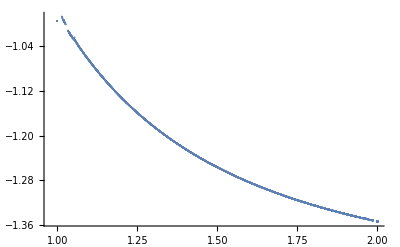

```mathematica
plotσfe=Show[ListPlot[tabσ]]
```

```mathematica
deg=3;
```

```mathematica
f[r_]:=Sum[A[i]r^i,{i,0,deg}]
```

```mathematica
fitr03=FindFit[Select[tabσr03,#[[1]]>1.2&],f[r],Table[A[i],{i,0,deg}],r]
```

{A[0]→4.24202,A[1]→-8.9859,A[2]→5.01777,A[3]→-0.946126}

```mathematica
fitr01=FindFit[Select[tabσr01,#[[1]]>1.2&],f[r],Table[A[i],{i,0,deg}],r]
```

{A[0]→0.621364,A[1]→-2.6118,A[2]→1.22625,A[3]→-0.202579}

```mathematica
fitr005=FindFit[Select[tabσr005,#[[1]]>1.2&],f[r],Table[A[i],{i,0,deg}],r]
```

{A[0]→0.594204,A[1]→-2.60741,A[2]→1.22527,A[3]→-0.202764}

```mathematica
fitr0025=FindFit[Select[tabσr0025,#[[1]]>1.2&],f[r],Table[A[i],{i,0,deg}],r]
```

{A[0]→0.589131,A[1]→-2.62254,A[2]→1.23516,A[3]→-0.204903}

```mathematica
(*sigma extrapolated to r -> 0*)
```

```mathematica
finf[rs_]:=α/.FindFit[{{0.3,f[rs]/.fitr03},{0.1,f[rs]/.fitr01},{0.05,f[rs]/.fitr005},{0.025,f[rs]/.fitr0025}},α+β x+γ x^2+ϵ x^3,{α,β,γ,ϵ},x]
```

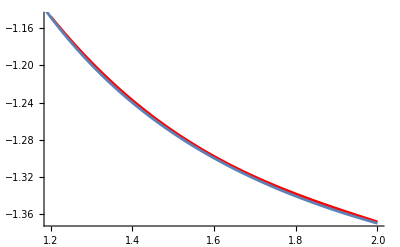

```mathematica
Show[Plot[finf[rs],{rs,1.2,Rmax},PlotStyle->Red],plotσexact]
```

```mathematica
(*r=0.3*)
```

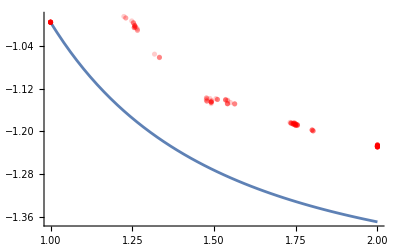

```mathematica
(*r=0.1*)
```

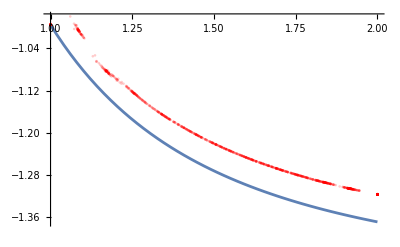

```mathematica
(*r=0.05*)
```

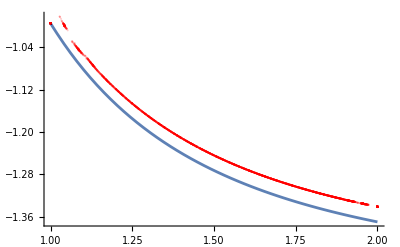

```mathematica
(*r=0.025*)
```